# Non-positive energy quasidistributions in coherent collision models

Author: Marco Pezzutto, Stefano Gherardini, Gabriele De Chiara
Copyright © 2025 Stefano Gherardini,Marco Pezzutto
ArXiv reference: 
https://arxiv.org/abs/2503.07759
NOTES:
 The cells for the analytic calculation of the dynamics of one collision, the exact theoretical thermodynamic quantities, the one-collision quasiprobabilities and the expectation values and variances are all Initialization cells. 
The numerical simulation of the iterated dynamics employs as much as possible dimensionless variables, as explaned below, for the sake of numerical stability and flexibility with respect to reference physical systems, allowing for the values of the numerical constants to vary over a wide range.
Please allow for 3-5 minutes of computing time for the evaluation of all the analytic quantities.
Scroll down for results in the form of plots. To simply look at them, there is no need to execute the notebook.

## Working Directory

```mathematica
Directory[]
SetDirectory[NotebookDirectory[]]
```

C:\Users\marcopezzutto\Documents

C:\Users\marcopezzutto\Documents\Progetti-Creativi\QuantumThermo_Stefano_Marco\Quasiprobabilities\Mathematica_notebooks

## 0. Constraints on symbolic physical parameters

```mathematica
ClearAll[constraints]
(* constraints for symbolic simplification *)
constraints={ωs∈Reals,ωs>0,ωe∈Reals,ωe>0,ω∈Reals,ω>0,β∈Reals,β>0,τse∈Reals,τse>0,τ∈Reals,τ>0,Jse∈Reals,Jse>0,g∈Reals,g>0,ρ11∈Reals,ρ11≥0,ρ11≤1,ρ12R∈Reals,ρ12I∈Reals,ℏ∈Reals,ℏ>0,ωs1∈Reals,ωs1>0,β1∈Reals,β1>0,τ1∈Reals,τ1>0,g1∈Reals,g1>0,λ1∈Reals,Δ∈Reals};
```

## 1. Density Matrix and Tensor manipulation machinery

#### Functions working on symbolic objects within Mathematica

```mathematica
ClearAll[σx,σz,σy, σ0 ,ketbra,σ,Σ,id2,id4];
ClearAll[Rank2toRank4];
ClearAll[CVNfunc,VNfunc,SvN,TrDist,MatSqrt, Fid];
ClearAll[MatLog,RelEnt,Mychop]
ClearAll[IncreaseRank,MatrixToTensor,TensorToMatrix,DecreaseRank];
ClearAll[PTraceOneP,Marginal,PTraceFirst,PTraceE,PTraceE1,PTraceENN];

(* Pauli matrices *)
σ0=IdentityMatrix[2];
σx=PauliMatrix[1];
σy=PauliMatrix[2];
σz=PauliMatrix[3];
Σ={σ0,σx,σy,σz};
σ={σx,σy,σz};
id2=IdentityMatrix[2];
id4=IdentityMatrix[4];

(* projector on a pure state vector *)
ketbra[vec_]:=Module[{d,m,i,j},
(* builts the projector starting from a pure vector state *)
d=Dimensions[vec][[1]];
m=Table[vec[[i]] vec[[j]]*,{i,1,d},{j,1,d}];
m
];

(* eigenvectors of Pauli matricex *)
grnd={0,1};
exct={1,0};
piu=1/(√2){1,1};
meno=1/(√2){1,-1};
R=1/(√2){1,I};
L=1/(√2){1,-I};

(* projectors on eigenvectors of Pauli matrices *)
PR=ketbra[R];
PL=ketbra[L];
P0=ketbra[exct];
P1=ketbra[grnd];
Ppiu=ketbra[piu];
Pmeno=ketbra[meno];
P01={{0,1},{0,0}};
P10={{0,0},{1,0}};

(* to Bloch representation and back *)
ToBloch[matrix_]:=Module[{k,result},
result=Table[Re[Tr[matrix.σ[[k]]]],{k,3}];
result
];
ToMatrix[BlVec_]:=Module[{k,result},
result=(Chop[σ0+Sum[BlVec[[k]]*σ[[k]],{k,3}]])/2;
result
];

(* Initialization of a pure state density matrix *)
Initial[θ_,ϕ_]:=Block[{BlVec,mat,i},
BlVec={1,Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]};
mat=Simplify[1/2 Sum[BlVec[[i]]*Σ[[i]],{i,4}],Assumptions:>{θ∈Reals,ϕ∈Reals}];
mat
];

(* von Neumann Entropy*)
VNfunc=Function[{x},Module[{res},
res=0;
If[Abs[x]<10^-16,res=0,res=x*Log[x]];
res
]];
CVNfunc=Compile[{x},Module[{res},
res=0.;
If[Abs[x]<10^-16,res=0.,res=x*Log[x]];
res
]];
SvN[matrix_]:=Module[{dim,spec,res2,i},
dim=Dimensions[matrix][[1]];
spec=Chop[Eigensystem[matrix][[1]]];
res2=-Sum[VNfunc[spec[[i]]],{i,1,dim}];
res2
];

(* Relative Entropy *)
RelEnt[matrix1_,matrix2_]:=-SvN[matrix1]-Tr[matrix1.MatLog[matrix2]];

(* Trace Distance *)
TrDist[matrix1_,matrix2_]:=Module[{dim2,spec2,res3,i},
dim2=Dimensions[matrix1][[1]];
spec2=Eigenvalues[matrix1-matrix2];
res3=1/2 Sum[Abs[spec2[[i]]],{i,1,dim2}];
res3
];

(* Fidelity *)
Fid[matrix1_,matrix2_]:=Tr[MatSqrt[MatSqrt[matrix1].matrix2.MatSqrt[matrix1]]];

(* Matrix Norm |M| = ∑_i |Subscript[λ, i]| *)
Norma[matrix_]:=Module[{dim2,spec2,res3,i},
dim2=Dimensions[matrix][[1]];
spec2=Eigenvalues[matrix];
res3=1/2 Sum[Abs[spec2[[i]]],{i,1,dim2}];
res3
];

(* Matrix Square Root *)
MatSqrt[matrix_]:=Module[{dim,spec,vecs,res,i},
dim=Dimensions[matrix][[1]];
spec=Eigenvalues[matrix];
vecs=Eigenvectors[matrix];
res=Sum[Sqrt[spec[[i]]]*ketbra[Normalize[vecs[[i]]]],{i,1,dim}];
res
];

(* Matrix Logarithm *)
MatLog[matrix_]:=Module[{dim,spec,vecs,res,i},
dim=Dimensions[matrix][[1]];
spec=Eigenvalues[matrix];
vecs=Eigenvectors[matrix];
res=Sum[Log[spec[[i]]]*ketbra[Normalize[vecs[[i]]]],{i,1,dim}];
res
];


(* Partial traces, marginals, tensor manipulation functions *)
Rank2toRank4[matrix_]:=Module[{temp,result,i,j,k},
(* from matrix representation to the true tensor representation of a 2-particle state *)
temp=Partition[Table[Partition[matrix[[i]],2],{i,1,4}],2];
result=Table[Table[Table[temp[[k,i,j]],{i,1,2}],{j,1,2}],{k,1,2}];
result
];
MatrixToTensor[matrix_]:=Module[{dim,Hdim,rank,temp7,temp8,temp9,result,i,k,l,j},
(* from matrix representation to the true tensor representation *)
dim=Dimensions[matrix][[1]];
Hdim=dim/2;
rank =2 Log[2,dim];
If[!(rank∈Integers)||rank<0,Print["The input matrix is not a good multi-qubit matrix since its dimensions are not powers of 2. Error in MatrixToTensor. "];
result=Null,
If[rank==2,
result=matrix,
If[rank==4,
result=Rank2toRank4[matrix],
(* caso generale *)
temp7=Table[Partition[matrix[[i]],Hdim],{i,dim}];
temp8=Partition[temp7,Hdim];
temp9=Table[Table[temp8[[k,i,l]],{i,Hdim}],{k,2},{l,2}];
result=Table[MatrixToTensor[temp9[[i,j]]],{i,2},{j,2}];
]
]
];
result
];
TensorToMatrix[tensor_]:=Module[{rank,dim,Hdim,temp,result,i,j,k},
(* Inverse of MatrixToTensor: from Tensor representation to square matrix representation *)
rank=TensorRank[tensor];
dim=2^(rank/2);
Hdim=dim/2;
If[rank==4,
result=Flatten[Table[Flatten[Table[tensor[[i,j,k]],{j,2}],1],{i,2},{k,Hdim}],1],
temp=Table[Table[TensorToMatrix[tensor[[i,j]]],{j,2}],{i,2}];
result=Flatten[Table[Flatten[Table[temp[[i,j,k]],{j,2}]],{i,2},{k,Hdim}],1]
];
result
];
IncreaseRank[matrix_]:=Module[{dim,Hdim,rank,temp7,temp8,temp9,result,i,k,l},
(* module to perform the passage to higher rank representation only for the first particle in the state, useful for tracing out just the system efficiently *)
dim=Dimensions[matrix][[1]];
Hdim=dim/2;
rank =2 Log[2,dim];
If[!(rank∈Integers)||rank<0,Print["The input matrix is not a good multi-qubit matrix since its dimensions are not powers of 2. Error in MatrixToTensor. "];
result=Null,
If[rank==2,
result=matrix,
If[rank==4,
result=Rank2toRank4[matrix],(* now the general case *)
temp7=Table[Partition[matrix[[i]],Hdim],{i,dim}];
temp8=Partition[temp7,Hdim];
result=Table[Table[temp8[[k,i,l]],{i,Hdim}],{k,2},{l,2}];
]
]
];
result
];
DecreaseRank[tensor_]:=Module[{dim,Hdim,result,l,i,j,k,rankT,dimT},
(* performs only one iteration in the process of going from tensor to matrix, acting on the representation of the first partice represented by tensor. In order to function properly, all the other particles must be ALREADY represented in matricial form, NOT tensorial. *)
rankT=TensorRank[tensor];
dimT=Dimensions[tensor];
dim=Sqrt[Product[dimT[[l]],{l,rankT}]];
Hdim=dim/2;
If[rankT==2,
result=tensor,
result=Flatten[Table[Flatten[Table[tensor[[i,j,k]],{j,2}]],{i,2},{k,Hdim}],1]
];
result
];
PTraceOneP[matrix_,j_]:=Module[{dim,Hdim,rank,result,NPart,temp,tensor},
(* tracing away only the j-th particle *)
dim=Dimensions[matrix][[1]];
Hdim=dim/2;
NPart=Log[2,dim];
rank=2NPart;
If[(j≤0||j>NPart),
Print["The input matrix doesn't have particle ",j];
result=Null,
If[dim==2,
result=matrix,
tensor=MatrixToTensor[matrix];
temp=TensorContract[tensor,{2j-1,2j}];
result=TensorToMatrix[temp]
]
];
result
];
Marginal[matrix_,j_]:=Module[{dim,Hdim,rank,result,NPart,temp,i},
(* gives the marginal state of the j-th particle *)
dim=Dimensions[matrix][[1]];
Hdim=dim/2;
NPart=Log[2,dim];
rank=2NPart;
If[(j≤0||j>NPart),
Print["The input matrix doesn't have particle ",j];
result=Null,
If[dim==2,
result=matrix,
If[j==1,
result=PTraceE[matrix],
temp=matrix;
For[i=1,i<j,i++,
temp=PTraceFirst[temp]
];
result=PTraceE[temp]
]
]
];
result
];
PTraceFirst[matrix_]:=Module[{dim,Hdim,rank,temp1,result},
(* partial trace on the FIRST particle in the tensor product order *)
dim=Dimensions[matrix][[1]];
Hdim=dim/2;
rank =2 Log[2,dim];
temp1=IncreaseRank[matrix];
result=TensorContract[temp1,{1,2}]
];
PTraceE[matrix_]:=Module[{dim,Hdim,rank,temp1,result,j},
(* partial trace on ALL the environment particles, for any arbitrary number of them, that is on ALL the particles but the first one in the tensor product order *)
dim=Dimensions[matrix][[1]];
Hdim=dim/2;
rank=2Log[2,dim];
temp1=MatrixToTensor[matrix];
If[dim==2,
result=matrix,
For[j=rank,j>3,j=j-2,
temp1=TensorContract[temp1,{{j-1,j}}];
(* Print["Particle traced away: ",j/2, ", rank of new tensor state: ",TensorRank[temp1]] *)
];
result=temp1
];
result
];
PTraceENN[matrix_]:=Module[{dim,Hdim,rank,temp1,result,j},
(* partial trace on all environment particles BUT THE FIRST ONE, that is all the NN particles, leaving the collective state of the first 2 particles, usually the system and the first environment particle *)
dim=Dimensions[matrix][[1]];
Hdim=dim/2;
rank=2Log[2,dim];
temp1=MatrixToTensor[matrix];
For[j=rank,j>5,j=j-2,
temp1=TensorContract[temp1,{{j-1,j}}];
(* Print["Particle traced away: ",j/2, ", rank of new tensor state: ",TensorRank[temp1]] *)
];
result=DecreaseRank[temp1]
];
PTraceE1[matrix_]:=Module[{temp1,temp2,temp3,result,i,j},
(* traces away only the SECOND particle in the state. It is equivalent to PTraceOneP[matrix,2], but more efficient. To be used when tracing away the oldest environment particle *)
temp1=IncreaseRank[matrix];
temp2=Table[IncreaseRank[temp1[[i,j]]],{i,2},{j,2}];
temp3=TensorContract[temp2,{3,4}];
result=DecreaseRank[temp3]
];

(* Quantum Discord *)
MyDiscord[matrix_]:=Module[{ρAB,ρA,ρB,θ,ϕ,list,res,SortedList,SρB,SρAB,Discord,Angles,P1,P2,ρP1,ρP2,p1,p2,SρP1,SρP2,result},
list={};
ρAB=matrix;
ρA=Chop[Marginal[ρAB,1]];
ρB=Chop[Marginal[ρAB,2]];
Do[
P1=N[KroneckerProduct[σ0,Initial[θ,ϕ]]];
P2=N[KroneckerProduct[σ0,Initial[π-θ,π+ϕ]]];
ρP1=Chop[P1.ρAB.P1];
ρP2=Chop[P2.ρAB.P2];
p1=Chop[Tr[ρP1]];
p2=Chop[Tr[ρP2]];
ρP1=ρP1/p1;
ρP2=ρP2/p2;
SρP1=Chop[SvN[ρP1]];
SρP2=Chop[SvN[ρP2]];
res=p1 SρP1+p2 SρP2;
AppendTo[list,{Re[res],θ,0}],
{θ,0,π,π/64},{ϕ,0,π/2,π/2}];
SortedList=Sort[list,#1[[1]]<#2[[1]]&];
SρB=Chop[SvN[ρB]];
SρAB=Chop[SvN[ρAB]];
Discord=SρB-SρAB+SortedList[[1,1]];
Angles=Take[SortedList[[1]],-2];
result=Flatten[{Discord,N[Angles]}]
];

(* Chop function taylored for complex matrices and vectors *)
Mychop[matrix_]:=Module[{dim,mat,i,j,Melem,thresholdMat},
dim=Dimensions[matrix][[1]];
thresholdMat=1×10^-15;
mat=Table[
(If[Abs[Re[matrix[[i,j]]]]<thresholdMat&&Abs[Im[matrix[[i,j]]]]<thresholdMat,Melem=0];
If[Abs[Im[matrix[[i,j]]]]<thresholdMat&&Abs[Re[matrix[[i,j]]]]≥thresholdMat,Melem=Re[matrix[[i,j]]]];
If[Abs[Re[matrix[[i,j]]]]<thresholdMat&&Abs[Im[matrix[[i,j]]]]≥thresholdMat,Melem=I*Im[matrix[[i,j]]]];
If[Abs[Im[matrix[[i,j]]]]>=thresholdMat&&Abs[Re[matrix[[i,j]]]]≥thresholdMat,Melem=matrix[[i,j]]];Melem),{i,dim},{j,dim}];
mat
];
MyChopVec[vector_]:=Module[{dim,vec,Velem,thresholdVec},
dim=Dimensions[vector][[1]];
thresholdVec=1×10^-7;
vec=Table[
(If[Abs[Re[vector[[i]]]]<thresholdVec&&Abs[Im[vector[[i]]]]<thresholdVec,Velem=0];
If[Abs[Im[vector[[i]]]]<thresholdVec&&Abs[Re[vector[[i]]]]≥thresholdVec,Velem=Re[vector[[i]]]];
If[Abs[Re[vector[[i]]]]<thresholdVec&&Abs[Im[vector[[i]]]]≥thresholdVec,Velem=I*Im[vector[[i]]]];
If[Abs[Im[vector[[i]]]]>=thresholdVec&&Abs[Re[vector[[i]]]]≥thresholdVec,Velem=vector[[i]]];Velem),{i,dim}];
vec
];
```

## 2. Hamiltonian Model construction

```mathematica
ClearAll[He,Hs,H0,VSE,HintSE,U0,U,Udag]
ClearAll[g,JmatSE,ωs,ωe,ω,ℏ,τ]
ClearAll[vecES,vecEA,ProjES,ProjEA,ΔESfi,ΔEAfi]

Hs=(ℏ ωs)/2 σz;
He=(ℏ ωe)/2 σz;

Print["Local Hamiltonians of System and Environment (Ancilla):"]
MatrixForm[Hs]
MatrixForm[He]

Print["Energies of S (Eigenvalues of HS):"]
vecES=Diagonal[Hs]

Print["System energy differences:"]
ΔESfi=Table[vecES[[i]]-vecES[[j]],{i,1,2},{j,1,2}];
vecΔES=Flatten[ΔESfi]

Print["Projectors on System eigenbasis:"]
ProjES={ketbra[exct],ketbra[grnd]};
MatrixForm[ProjES[[1]]]
MatrixForm[ProjES[[2]]]

Print["Energies of A (Eigenvalues of HA):"]
vecEA=Diagonal[He]

Print["Ancilla energy differences:"]
ΔEAfi=Table[vecEA[[i]]-vecEA[[j]],{i,1,2},{j,1,2}];
vecΔEA=Flatten[ΔEAfi]

Print["Projectors on Ancilla eigenbasis:"]
ProjEA={ketbra[exct],ketbra[grnd]};
MatrixForm[ProjEA[[1]]]
MatrixForm[ProjEA[[2]]]

H0=KroneckerProduct[Hs,σ0]+KroneckerProduct[σ0,He];
Print["H0: ",MatrixForm[H0]]

Print[" XX + YY interaction - It is Energy-preserving ONLY at resonance, ωs = ωe: "]
JmatSE=Table[If[i==j,ℏ g/2,0],{i,1,3},{j,1,3}];
JmatSE[[3,3]]=0;
Print["Matrix of system-environment coupling coefficients: ",MatrixForm[JmatSE]]

HintSE=Sum[Sum[JmatSE[[i,j]]*KroneckerProduct[σ[[i]],σ[[j]]],{i,1,3}],{j,1,3}];
Print["HintSE: ",MatrixForm[HintSE]]

U0=FullSimplify[MatrixExp[-I/ℏ H0*τ]];
U=FullSimplify[MatrixExp[-I/ℏ(H0+HintSE)*τ]];
Udag=Simplify[ComplexExpand[ConjugateTranspose[U]],Assumptions->constraints];

Print["U0: ",MatrixForm[U0]]
Print["U: ",MatrixForm[U]]
Print["Udag: ",MatrixForm[Udag]]

Print["Checks for the energy-preservation condition of the interaction"]
Print["[HintSE,H0]: ",MatrixForm[FullSimplify[HintSE.H0-H0.HintSE]]]
Print["[U,H0]: ",MatrixForm[ FullSimplify[U.H0-H0.U,Assumptions->constraints]]]
```

Local Hamiltonians of System and Environment (Ancilla):

((ωs ℏ)/2 | 0
0 | -(ωs ℏ)/2)

((ωe ℏ)/2 | 0
0 | -(ωe ℏ)/2)

Energies of S (Eigenvalues of HS):

{(ωs ℏ)/2,-(ωs ℏ)/2}

System energy differences:

{0,ωs ℏ,-ωs ℏ,0}

Projectors on System eigenbasis:

(1 | 0
0 | 0)

(0 | 0
0 | 1)

Energies of A (Eigenvalues of HA):

{(ωe ℏ)/2,-(ωe ℏ)/2}

Ancilla energy differences:

{0,ωe ℏ,-ωe ℏ,0}

Projectors on Ancilla eigenbasis:

(1 | 0
0 | 0)

(0 | 0
0 | 1)

H0: ((ωe ℏ)/2+(ωs ℏ)/2 | 0 | 0 | 0
0 | -(ωe ℏ)/2+(ωs ℏ)/2 | 0 | 0
0 | 0 | (ωe ℏ)/2-(ωs ℏ)/2 | 0
0 | 0 | 0 | -(ωe ℏ)/2-(ωs ℏ)/2)

XX + YY interaction - It is Energy-preserving ONLY at resonance, ωs = ωe:

Matrix of system-environment coupling coefficients: ((g ℏ)/2 | 0 | 0
0 | (g ℏ)/2 | 0
0 | 0 | 0)

HintSE: (0 | 0 | 0 | 0
0 | 0 | g ℏ | 0
0 | g ℏ | 0 | 0
0 | 0 | 0 | 0)

U0: (ⅇ^(-1/2 ⅈ τ (ωe+ωs)) | 0 | 0 | 0
0 | ⅇ^(1/2 ⅈ τ (ωe-ωs)) | 0 | 0
0 | 0 | ⅇ^(-1/2 ⅈ τ (ωe-ωs)) | 0
0 | 0 | 0 | ⅇ^(1/2 ⅈ τ (ωe+ωs)))

U: (ⅇ^(-1/2 ⅈ τ (ωe+ωs)) | 0 | 0 | 0
0 | (√(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ⅈ (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(√(4 g^2+(ωe-ωs)^2)) | -(2 ⅈ g Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(√(4 g^2+(ωe-ωs)^2)) | 0
0 | -(2 ⅈ g Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(√(4 g^2+(ωe-ωs)^2)) | (√(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]-ⅈ (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(√(4 g^2+(ωe-ωs)^2)) | 0
0 | 0 | 0 | ⅇ^(1/2 ⅈ τ (ωe+ωs)))

Udag: (Cos[1/2 τ (ωe+ωs)]+ⅈ Sin[1/2 τ (ωe+ωs)] | 0 | 0 | 0
0 | Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]-(ⅈ (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(√(4 g^2+(ωe-ωs)^2)) | (2 ⅈ g Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(√(4 g^2+(ωe-ωs)^2)) | 0
0 | (2 ⅈ g Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(√(4 g^2+(ωe-ωs)^2)) | Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(ⅈ (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(√(4 g^2+(ωe-ωs)^2)) | 0
0 | 0 | 0 | Cos[1/2 τ (ωe+ωs)]-ⅈ Sin[1/2 τ (ωe+ωs)])

Checks for the energy-preservation condition of the interaction

[HintSE,H0]: (0 | 0 | 0 | 0
0 | 0 | g (ωe-ωs) ℏ^2 | 0
0 | g (-ωe+ωs) ℏ^2 | 0 | 0
0 | 0 | 0 | 0)

[U,H0]: (0 | 0 | 0 | 0
0 | 0 | -(2 ⅈ g (ωe-ωs) ℏ Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(√(4 g^2+(ωe-ωs)^2)) | 0
0 | (2 ⅈ g (ωe-ωs) ℏ Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(√(4 g^2+(ωe-ωs)^2)) | 0 | 0
0 | 0 | 0 | 0)

As  can  be  seen, the interaction is energy-preserving at the resonant condition, ωs = ωe.

## 3. State Initialisation and single collision dynamics: evolved global and local states

```mathematica
ClearAll[λ1,β,ρ11,ρ12R,ρ12I]
ClearAll[ρAth,χ,ρA,ρSt0,ρin,ρend,ρSend,ρAend]

(* NOTE: We use as the environment state coherence parameter λ1 instead of λ, without including explicitly √τ, because we are not taking the small-τ approximation here. In comparison with the previous notebooks, λ1 = λ √τ, however we never use this here.  *)

(* Initial system state *)
ρSt0={{ρ11,ρ12R+I*ρ12I},{ρ12R-I*ρ12I,1-ρ11}};
Print["Initial system state:"]
MatrixForm[ρSt0]

(* Initial environment state *)
ρAth=MatrixExp[-β He]/Tr[MatrixExp[-β He]]; 
Print["Environment thermal state:"]
MatrixForm[ρAth]

χA=λ1 σx;
ρA=ρAth+χA;
Print["Environment state with coherence:"]
MatrixForm[ρA] 

(* Initial collective state *)
ρin=KroneckerProduct[ρSt0,ρA];
Print["Collective initial state:"]
MatrixForm[ρin]

(* Evolved collective state *)
ρend=Simplify[U.ρin.Udag,Assumptions->constraints];
Print["Collective final evolved state:"]
MatrixForm[ρend]

(* Evolved system state *)

ρSend=Simplify[Marginal[ρend,1],Assumptions->constraints];
Print["Evolved system state:"]
MatrixForm[ρSend]

Print["In the resonant case:"]
MatrixForm[Simplify[ρSend/.{ωe->ω,ωs->ω},Assumptions->constraints]]

(* Evolved ancilla state *)

ρAend=Simplify[Marginal[ρend,2],Assumptions->constraints];
Print["Evolved environment state:"]
MatrixForm[ρAend]

Print["In the resonant case:"]
MatrixForm[Simplify[ρAend/.{ωe->ω,ωs->ω},Assumptions->constraints]]
```

Initial system state:

(ρ11 | ⅈ ρ12I+ρ12R
-ⅈ ρ12I+ρ12R | 1-ρ11)

Environment thermal state:

(ⅇ^(-1/2 β ωe ℏ)/(ⅇ^(-1/2 β ωe ℏ)+ⅇ^((β ωe ℏ)/2)) | 0
0 | ⅇ^((β ωe ℏ)/2)/(ⅇ^(-1/2 β ωe ℏ)+ⅇ^((β ωe ℏ)/2)))

Environment state with coherence:

(ⅇ^(-1/2 β ωe ℏ)/(ⅇ^(-1/2 β ωe ℏ)+ⅇ^((β ωe ℏ)/2)) | λ1
λ1 | ⅇ^((β ωe ℏ)/2)/(ⅇ^(-1/2 β ωe ℏ)+ⅇ^((β ωe ℏ)/2)))

Collective initial state:

((ⅇ^(-1/2 β ωe ℏ) ρ11)/(ⅇ^(-1/2 β ωe ℏ)+ⅇ^((β ωe ℏ)/2)) | λ1 ρ11 | (ⅇ^(-1/2 β ωe ℏ) (ⅈ ρ12I+ρ12R))/(ⅇ^(-1/2 β ωe ℏ)+ⅇ^((β ωe ℏ)/2)) | λ1 (ⅈ ρ12I+ρ12R)
λ1 ρ11 | (ⅇ^((β ωe ℏ)/2) ρ11)/(ⅇ^(-1/2 β ωe ℏ)+ⅇ^((β ωe ℏ)/2)) | λ1 (ⅈ ρ12I+ρ12R) | (ⅇ^((β ωe ℏ)/2) (ⅈ ρ12I+ρ12R))/(ⅇ^(-1/2 β ωe ℏ)+ⅇ^((β ωe ℏ)/2))
(ⅇ^(-1/2 β ωe ℏ) (-ⅈ ρ12I+ρ12R))/(ⅇ^(-1/2 β ωe ℏ)+ⅇ^((β ωe ℏ)/2)) | λ1 (-ⅈ ρ12I+ρ12R) | (ⅇ^(-1/2 β ωe ℏ) (1-ρ11))/(ⅇ^(-1/2 β ωe ℏ)+ⅇ^((β ωe ℏ)/2)) | λ1 (1-ρ11)
λ1 (-ⅈ ρ12I+ρ12R) | (ⅇ^((β ωe ℏ)/2) (-ⅈ ρ12I+ρ12R))/(ⅇ^(-1/2 β ωe ℏ)+ⅇ^((β ωe ℏ)/2)) | λ1 (1-ρ11) | (ⅇ^((β ωe ℏ)/2) (1-ρ11))/(ⅇ^(-1/2 β ωe ℏ)+ⅇ^((β ωe ℏ)/2)))

Collective final evolved state:

(ρ11/(1+ⅇ^(β ωe ℏ)) | (ⅇ^(-1/2 ⅈ τ (ωe+ωs)) ((1+ⅇ^(β ωe ℏ)) λ1 ρ11 √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]-(2 g (ρ12I-ⅈ ρ12R)+ⅈ (1+ⅇ^(β ωe ℏ)) λ1 ρ11 (ωe-ωs)) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) √(4 g^2+(ωe-ωs)^2)) | (ⅇ^(-1/2 ⅈ τ (ωe+ωs)) ((ⅈ ρ12I+ρ12R) √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(2 ⅈ (1+ⅇ^(β ωe ℏ)) g λ1 ρ11-(ρ12I-ⅈ ρ12R) (ωe-ωs)) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) √(4 g^2+(ωe-ωs)^2)) | ⅇ^(-ⅈ τ (ωe+ωs)) λ1 (ⅈ ρ12I+ρ12R)
(((1+ⅇ^(β ωe ℏ)) λ1 ρ11 √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]-(2 g (ρ12I+ⅈ ρ12R)-ⅈ (1+ⅇ^(β ωe ℏ)) λ1 ρ11 (ωe-ωs)) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]) (Cos[1/2 τ (ωe+ωs)]+ⅈ Sin[1/2 τ (ωe+ωs)]))/((1+ⅇ^(β ωe ℏ)) √(4 g^2+(ωe-ωs)^2)) | (2 g^2-2 g^2 ρ11+2 ⅇ^(β ωe ℏ) g^2 ρ11-2 g λ1 ρ12R ωe-2 ⅇ^(β ωe ℏ) g λ1 ρ12R ωe+ⅇ^(β ωe ℏ) ρ11 ωe^2+2 g λ1 ρ12R ωs+2 ⅇ^(β ωe ℏ) g λ1 ρ12R ωs-2 ⅇ^(β ωe ℏ) ρ11 ωe ωs+ⅇ^(β ωe ℏ) ρ11 ωs^2+2 g (g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) Cos[τ √(4 g^2+(ωe-ωs)^2)]-2 (1+ⅇ^(β ωe ℏ)) g λ1 ρ12I √(4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)])/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)) | (ⅈ ⅇ^((β ωe ℏ)/2) (-2 ⅇ^(-1/2 β ωe ℏ) g Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (-ⅇ^(β ωe ℏ) ρ11 √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(2 (1+ⅇ^(β ωe ℏ)) g λ1 (ρ12I+ⅈ ρ12R)-ⅈ ⅇ^(β ωe ℏ) ρ11 (ωe-ωs)) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])+ⅈ ⅇ^(-1/2 β ωe ℏ) (√(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ⅈ (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]) (-2 ⅈ g (-1+ρ11) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(1+ⅇ^(β ωe ℏ)) λ1 (ρ12I-ⅈ ρ12R) (-ⅈ √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)) | ((ⅇ^(β ωe ℏ) (ρ12I-ⅈ ρ12R) √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(2 (1+ⅇ^(β ωe ℏ)) g λ1 (-1+ρ11)+ⅇ^(β ωe ℏ) (ⅈ ρ12I+ρ12R) (ωe-ωs)) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]) (ⅈ Cos[1/2 τ (ωe+ωs)]+Sin[1/2 τ (ωe+ωs)]))/((1+ⅇ^(β ωe ℏ)) √(4 g^2+(ωe-ωs)^2))
(((ρ12I+ⅈ ρ12R) √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(2 (1+ⅇ^(β ωe ℏ)) g λ1 ρ11+(-ⅈ ρ12I+ρ12R) (ωe-ωs)) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]) (-ⅈ Cos[1/2 τ (ωe+ωs)]+Sin[1/2 τ (ωe+ωs)]))/((1+ⅇ^(β ωe ℏ)) √(4 g^2+(ωe-ωs)^2)) | -(ⅈ ⅇ^((β ωe ℏ)/2) (2 ⅇ^(-1/2 β ωe ℏ) g Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (-2 (1+ⅇ^(β ωe ℏ)) g λ1 (ρ12I-ⅈ ρ12R) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(-1+ρ11) (√(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]-ⅈ (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))+(√(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]-ⅈ (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]) (2 ⅇ^((β ωe ℏ)/2) g ρ11 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ⅇ^(-1/2 β ωe ℏ) (1+ⅇ^(β ωe ℏ)) λ1 (ρ12I+ⅈ ρ12R) (√(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]-ⅈ (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)) | (2 g^2-2 g^2 ρ11+2 ⅇ^(β ωe ℏ) g^2 ρ11+2 g λ1 ρ12R ωe+2 ⅇ^(β ωe ℏ) g λ1 ρ12R ωe+ωe^2-ρ11 ωe^2-2 g λ1 ρ12R ωs-2 ⅇ^(β ωe ℏ) g λ1 ρ12R ωs-2 ωe ωs+2 ρ11 ωe ωs+ωs^2-ρ11 ωs^2-2 g (g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) Cos[τ √(4 g^2+(ωe-ωs)^2)]+2 (1+ⅇ^(β ωe ℏ)) g λ1 ρ12I √(4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)])/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)) | (((2 ⅇ^(β ωe ℏ) g (ρ12I-ⅈ ρ12R) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(1+ⅇ^(β ωe ℏ))+λ1 (1-ρ11) (√(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]-ⅈ (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])) (Cos[1/2 τ (ωe+ωs)]-ⅈ Sin[1/2 τ (ωe+ωs)]))/(√(4 g^2+(ωe-ωs)^2))
ⅇ^(ⅈ τ (ωe+ωs)) λ1 (-ⅈ ρ12I+ρ12R) | ⅇ^(1/2 ⅈ τ (ωe+ωs)) (-(2 ⅈ g λ1 (-1+ρ11) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(√(4 g^2+(ωe-ωs)^2))+(ⅇ^(β ωe ℏ) (-ⅈ ρ12I+ρ12R) (Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]-(ⅈ (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(√(4 g^2+(ωe-ωs)^2))))/(1+ⅇ^(β ωe ℏ))) | ⅇ^(1/2 ⅈ τ (ωe+ωs)) ((2 ⅇ^(β ωe ℏ) g (ρ12I+ⅈ ρ12R) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/((1+ⅇ^(β ωe ℏ)) √(4 g^2+(ωe-ωs)^2))+λ1 (1-ρ11) (Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(ⅈ (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(√(4 g^2+(ωe-ωs)^2)))) | -(ⅇ^(β ωe ℏ) (-1+ρ11))/(1+ⅇ^(β ωe ℏ)))

Evolved system state:

((ρ11+(2 g^2-2 g^2 ρ11+2 ⅇ^(β ωe ℏ) g^2 ρ11-2 g λ1 ρ12R ωe-2 ⅇ^(β ωe ℏ) g λ1 ρ12R ωe+ⅇ^(β ωe ℏ) ρ11 ωe^2+2 g λ1 ρ12R ωs+2 ⅇ^(β ωe ℏ) g λ1 ρ12R ωs-2 ⅇ^(β ωe ℏ) ρ11 ωe ωs+ⅇ^(β ωe ℏ) ρ11 ωs^2+2 g (g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) Cos[τ √(4 g^2+(ωe-ωs)^2)]-2 (1+ⅇ^(β ωe ℏ)) g λ1 ρ12I √(4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)])/(4 g^2+(ωe-ωs)^2))/(1+ⅇ^(β ωe ℏ)) | (ⅇ^(-1/2 ⅈ τ (ωe+ωs)) ((ⅈ ρ12I+ρ12R) √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(2 ⅈ (1+ⅇ^(β ωe ℏ)) g λ1 ρ11-(ρ12I-ⅈ ρ12R) (ωe-ωs)) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])+(ⅇ^(β ωe ℏ) (ρ12I-ⅈ ρ12R) √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(2 (1+ⅇ^(β ωe ℏ)) g λ1 (-1+ρ11)+ⅇ^(β ωe ℏ) (ⅈ ρ12I+ρ12R) (ωe-ωs)) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]) (ⅈ Cos[1/2 τ (ωe+ωs)]+Sin[1/2 τ (ωe+ωs)]))/((1+ⅇ^(β ωe ℏ)) √(4 g^2+(ωe-ωs)^2))
(ⅈ (ⅇ^(1/2 ⅈ τ (ωe+ωs)) (-2 (1+ⅇ^(β ωe ℏ)) g λ1 (-1+ρ11) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ⅈ ⅇ^(β ωe ℏ) (ⅈ ρ12I-ρ12R) (√(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]-ⅈ (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))+ⅈ ((ρ12I+ⅈ ρ12R) √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(2 (1+ⅇ^(β ωe ℏ)) g λ1 ρ11+(-ⅈ ρ12I+ρ12R) (ωe-ωs)) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]) (ⅈ Cos[1/2 τ (ωe+ωs)]-Sin[1/2 τ (ωe+ωs)])))/((1+ⅇ^(β ωe ℏ)) √(4 g^2+(ωe-ωs)^2)) | (-ⅇ^(β ωe ℏ) (-1+ρ11)+(2 g^2-2 g^2 ρ11+2 ⅇ^(β ωe ℏ) g^2 ρ11+2 g λ1 ρ12R ωe+2 ⅇ^(β ωe ℏ) g λ1 ρ12R ωe+ωe^2-ρ11 ωe^2-2 g λ1 ρ12R ωs-2 ⅇ^(β ωe ℏ) g λ1 ρ12R ωs-2 ωe ωs+2 ρ11 ωe ωs+ωs^2-ρ11 ωs^2-2 g (g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) Cos[τ √(4 g^2+(ωe-ωs)^2)]+2 (1+ⅇ^(β ωe ℏ)) g λ1 ρ12I √(4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)])/(4 g^2+(ωe-ωs)^2))/(1+ⅇ^(β ωe ℏ)))

In the resonant case:

((g (1+ρ11+ⅇ^(β ω ℏ) ρ11)+g (-1+ρ11+ⅇ^(β ω ℏ) ρ11) Cos[2 √(g^2) τ]-2 (1+ⅇ^(β ω ℏ)) √(g^2) λ1 ρ12I Sin[2 √(g^2) τ])/(2 (1+ⅇ^(β ω ℏ)) g) | (ⅇ^(-ⅈ τ ω) (√(g^2) (ⅈ ρ12I+ρ12R) Cos[√(g^2) τ]+ⅈ g λ1 (-1+2 ρ11) Sin[√(g^2) τ]))/(√(g^2))
(ⅇ^(ⅈ τ ω) (√(g^2) (-ⅈ ρ12I+ρ12R) Cos[√(g^2) τ]+ⅈ g λ1 (1-2 ρ11) Sin[√(g^2) τ]))/(√(g^2)) | -(g (-1+ⅇ^(β ω ℏ) (-2+ρ11)+ρ11)+g (-1+ρ11+ⅇ^(β ω ℏ) ρ11) Cos[2 √(g^2) τ]-2 (1+ⅇ^(β ω ℏ)) √(g^2) λ1 ρ12I Sin[2 √(g^2) τ])/(2 (1+ⅇ^(β ω ℏ)) g))

Evolved environment state:

((2 g^2+2 g^2 ρ11+2 ⅇ^(β ωe ℏ) g^2 ρ11+2 g λ1 ρ12R ωe+2 ⅇ^(β ωe ℏ) g λ1 ρ12R ωe+ωe^2-2 g λ1 ρ12R ωs-2 ⅇ^(β ωe ℏ) g λ1 ρ12R ωs-2 ωe ωs+ωs^2-2 g (g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) Cos[τ √(4 g^2+(ωe-ωs)^2)]+2 (1+ⅇ^(β ωe ℏ)) g λ1 ρ12I √(4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)])/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)) | (ⅇ^(-1/2 ⅈ τ (ωe+ωs)) ((1+ⅇ^(β ωe ℏ)) λ1 ρ11 √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]-(2 g (ρ12I-ⅈ ρ12R)+ⅈ (1+ⅇ^(β ωe ℏ)) λ1 ρ11 (ωe-ωs)) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])+(2 ⅇ^(β ωe ℏ) g (ρ12I-ⅈ ρ12R) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(1+ⅇ^(β ωe ℏ)) λ1 (1-ρ11) (√(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]-ⅈ (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])) (Cos[1/2 τ (ωe+ωs)]-ⅈ Sin[1/2 τ (ωe+ωs)]))/((1+ⅇ^(β ωe ℏ)) √(4 g^2+(ωe-ωs)^2))
(ⅇ^(1/2 ⅈ τ (ωe+ωs)) (2 ⅇ^(β ωe ℏ) g (ρ12I+ⅈ ρ12R) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(1+ⅇ^(β ωe ℏ)) λ1 (1-ρ11) (√(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ⅈ (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))+((1+ⅇ^(β ωe ℏ)) λ1 ρ11 √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]-(2 g (ρ12I+ⅈ ρ12R)-ⅈ (1+ⅇ^(β ωe ℏ)) λ1 ρ11 (ωe-ωs)) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]) (Cos[1/2 τ (ωe+ωs)]+ⅈ Sin[1/2 τ (ωe+ωs)]))/((1+ⅇ^(β ωe ℏ)) √(4 g^2+(ωe-ωs)^2)) | (2 g^2+4 ⅇ^(β ωe ℏ) g^2-2 g^2 ρ11-2 ⅇ^(β ωe ℏ) g^2 ρ11-2 g λ1 ρ12R ωe-2 ⅇ^(β ωe ℏ) g λ1 ρ12R ωe+ⅇ^(β ωe ℏ) ωe^2+2 g λ1 ρ12R ωs+2 ⅇ^(β ωe ℏ) g λ1 ρ12R ωs-2 ⅇ^(β ωe ℏ) ωe ωs+ⅇ^(β ωe ℏ) ωs^2+2 g (g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) Cos[τ √(4 g^2+(ωe-ωs)^2)]-2 (1+ⅇ^(β ωe ℏ)) g λ1 ρ12I √(4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)])/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)))

In the resonant case:

((g (1+ρ11+ⅇ^(β ω ℏ) ρ11)-g (-1+ρ11+ⅇ^(β ω ℏ) ρ11) Cos[2 √(g^2) τ]+2 (1+ⅇ^(β ω ℏ)) √(g^2) λ1 ρ12I Sin[2 √(g^2) τ])/(2 (1+ⅇ^(β ω ℏ)) g) | (ⅇ^(-ⅈ τ ω) ((1+ⅇ^(β ω ℏ)) √(g^2) λ1 Cos[√(g^2) τ]+(-1+ⅇ^(β ω ℏ)) g (ρ12I-ⅈ ρ12R) Sin[√(g^2) τ]))/((1+ⅇ^(β ω ℏ)) √(g^2))
(ⅇ^(ⅈ τ ω) ((1+ⅇ^(β ω ℏ)) √(g^2) λ1 Cos[√(g^2) τ]+(-1+ⅇ^(β ω ℏ)) g (ρ12I+ⅈ ρ12R) Sin[√(g^2) τ]))/((1+ⅇ^(β ω ℏ)) √(g^2)) | (-g (-1+ⅇ^(β ω ℏ) (-2+ρ11)+ρ11)+g (-1+ρ11+ⅇ^(β ω ℏ) ρ11) Cos[2 √(g^2) τ]-2 (1+ⅇ^(β ω ℏ)) √(g^2) λ1 ρ12I Sin[2 √(g^2) τ])/(2 (1+ⅇ^(β ω ℏ)) g))

## 4. Thermodynamic quantities, Exact Theoretical values: ΔES, ΔEA, QS, QA, WcS, WcA and Wnep

### Exact theoretical Internal Energy variation

```mathematica
ClearAll[AverageΔESTHEO,AverageΔEATHEO]

(* Theoretical average System Energy variation *)

Print["Exact Average δES "]
AverageΔESTHEO=Simplify[ComplexExpand[Tr[Hs.(ρSend-ρSt0)]]]

Print["In the resonant case:"]
Simplify[AverageΔESTHEO/.{ωe->ω,ωs->ω},Assumptions->constraints]

(* Theoretical average Ancilla Energy variation *)

Print["Exact Average δEA "]
AverageΔEATHEO=Simplify[ComplexExpand[Tr[He.(ρAend-ρA)]]]

Print["In the resonant case:"]
Simplify[AverageΔEATHEO/.{ωe->ω,ωs->ω},Assumptions->constraints]

(* Total energy conservation check *)

Print["Check of total energy conservation: δES + δEA ="]
Simplify[AverageΔESTHEO+AverageΔEATHEO]

Print["In the resonant case:"]
Simplify[AverageΔESTHEO+AverageΔEATHEO/.{ωe->ω,ωs->ω},Assumptions->constraints]
```

Exact Average δES

-(4 g ωs ℏ Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] ((1+ⅇ^(β ωe ℏ)) λ1 ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) √(4 g^2+(ωe-ωs)^2) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)^(3/2))

In the resonant case:

-(ω ℏ Sin[√(g^2) τ] (2 (1+ⅇ^(β ω ℏ)) g λ1 ρ12I Cos[√(g^2) τ]+√(g^2) (-1+ρ11+ⅇ^(β ω ℏ) ρ11) Sin[√(g^2) τ]))/((1+ⅇ^(β ω ℏ)) √(g^2))

Exact Average δEA

(4 g ωe ℏ Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] ((1+ⅇ^(β ωe ℏ)) λ1 ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) √(4 g^2+(ωe-ωs)^2) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)^(3/2))

In the resonant case:

(ω ℏ Sin[√(g^2) τ] (2 (1+ⅇ^(β ω ℏ)) g λ1 ρ12I Cos[√(g^2) τ]+√(g^2) (-1+ρ11+ⅇ^(β ω ℏ) ρ11) Sin[√(g^2) τ]))/((1+ⅇ^(β ω ℏ)) √(g^2))

Check of total energy conservation: δES + δEA =

(4 g (ωe-ωs) ℏ Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] ((1+ⅇ^(β ωe ℏ)) λ1 ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) √(4 g^2+(ωe-ωs)^2) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)^(3/2))

In the resonant case:

0

### Theoretical External Non-energy-preserving Work (Wnep) aka “mechanical work” (LM for "Lavoro Meccanico") and total Energy Conservation

```mathematica
LM=FullSimplify[Tr[H0.(ρend-ρin)],Assumptions->constraints]
LMtheo=LM;

Print["In the resonant case:"]
Simplify[LM/.{ωe->ω,ωs->ω,ℏ->1},Assumptions->constraints]
```

(2 g (ωe-ωs) ℏ (g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)+(-g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)-(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) Cos[τ √(4 g^2+(ωe-ωs)^2)]+(1+ⅇ^(β ωe ℏ)) λ1 ρ12I √(4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))

In the resonant case:

0

### Theoretical exact incoherent heat

This  section  essentially  repeats  the  calculations  of  the  previous  section, simply  substituting  ρA with ρAth in the initial state, or, in  other  words, putting  the  correlations  to  0  (λ = 0).

```mathematica
ClearAll[ρthSAend,ρthSend,ρthAend,AverageQSTHEO,AverageQATHEO]
ρthSAend=Simplify[(U.KroneckerProduct[ρSt0,ρAth].Udag),Assumptions->constraints];
ρthSend=FullSimplify[Marginal[ρthSAend,1],Assumptions->constraints];
ρthAend=FullSimplify[Marginal[ρthSAend,2],Assumptions->constraints];

(* Heat exchanged by the System *)

Print["Exact Average QS:"]
AverageQSTHEO=Simplify[Tr[Hs.(ρthSend-ρSt0)]]

Print["In the resonant case:"]
Simplify[AverageQSTHEO/.{ωe->ω,ωs->ω},Assumptions->constraints]

Print["For comparison, here again the internal energy variation:"]
Print["Average ΔES exact:"]
AverageΔESTHEO

(* Heat exchanged by the Ancilla *)

Print["Exact Average QA:"]
AverageQATHEO=Simplify[Tr[He.(ρthAend-ρAth)]]

Print["In the resonant case:"]
Simplify[AverageQATHEO/.{ωe->ω,ωs->ω},Assumptions->constraints]

Print["For comparison, here again the internal energy variation:"]
Print["Average ΔEA exact:"]
AverageΔEATHEO

(* Check of symmetry of heat transfer *)

Print["Check of symmetry of heat transfer: QS + QA ="]
FullSimplify[AverageQSTHEO+AverageQATHEO]

Print["In the resonant case:"]
Simplify[(AverageQSTHEO+AverageQATHEO)/.{ωe->ω,ωs->ω},Assumptions->constraints]
```

Exact Average QS:

(2 g^2 (-1+ρ11+ⅇ^(β ωe ℏ) ρ11) ωs ℏ (-1+Cos[τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))

In the resonant case:

-((-1+ρ11+ⅇ^(β ω ℏ) ρ11) ω ℏ Sin[√(g^2) τ]^2)/(1+ⅇ^(β ω ℏ))

For comparison, here again the internal energy variation:

Average ΔES exact:

-(4 g ωs ℏ Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] ((1+ⅇ^(β ωe ℏ)) λ1 ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) √(4 g^2+(ωe-ωs)^2) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)^(3/2))

Exact Average QA:

-(2 g^2 (-1+ρ11+ⅇ^(β ωe ℏ) ρ11) ωe ℏ (-1+Cos[τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))

In the resonant case:

((-1+ρ11+ⅇ^(β ω ℏ) ρ11) ω ℏ Sin[√(g^2) τ]^2)/(1+ⅇ^(β ω ℏ))

For comparison, here again the internal energy variation:

Average ΔEA exact:

(4 g ωe ℏ Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] ((1+ⅇ^(β ωe ℏ)) λ1 ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) √(4 g^2+(ωe-ωs)^2) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)^(3/2))

Check of symmetry of heat transfer: QS + QA =

-(2 g^2 (-1+ρ11+ⅇ^(β ωe ℏ) ρ11) (ωe-ωs) ℏ (-1+Cos[τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))

In the resonant case:

0

### Theoretical exact coherent work

This  section  essentially  repeats  the  calculations  of  the  energy  variation section, simply  substituting  ρA with χA.
Note that strictly speaking these calculations don’t have a real physical meaning on their own, since χA is not a legitimate density matrix on its own right (Tr[χA] = 0). 
These calculations on the coherent work make sense only in the context of the First Law of Thermodynamics ΔE = Δq + Wc (up to +/- signs depending on your preferred sign convention).
Here the sign convention is such that a positive ΔE/ΔQ/Wc corresponds to an INCREASE of the particle’s energy. This holds both for the System and for the Ancilla.

```mathematica
ClearAll[ρχSAend,ρχSend,ρχAend,AverageWcSTHEO,AverageWcATHEO]
ρχSAend=Simplify[(U.KroneckerProduct[ρSt0,χA].ConjugateTranspose[U]),Assumptions->constraints];
ρχSend=FullSimplify[ComplexExpand[Marginal[ρχSAend,1]],Assumptions->constraints];
ρχAend=FullSimplify[ComplexExpand[Marginal[ρχSAend,2]],Assumptions->constraints];

Print["Post-collision exact SAχ pseudo-state, and its trace:"]
MatrixForm[ρχSAend]
Simplify[Tr[ρχSAend]]

Print["Post-collision exact Sχ pseudo-state, and its trace:"]
MatrixForm[ρχSend]
Simplify[Tr[ρχSend]]

Print["Post-collision exact Aχ pseudo-state, and its trace:"]
MatrixForm[ρχAend]
Simplify[Tr[ρχAend]]

(* Coherent work from the perspective of the System *)

Print["Average WcS exact:"]
AverageWcSTHEO=Simplify[Tr[Hs.(ρχSend)]]

Print["In the resonant case:"]
Simplify[AverageWcSTHEO/.{ωe->ω,ωs->ω},Assumptions->constraints]

Print["For comparison, here again the internal energy variation:"]
Print["Average ΔES exact:"]
AverageΔESTHEO

(* Coherent work from the perspective of the Ancilla *)

Print["Average WcA exact:"]
AverageWcATHEO=Simplify[Tr[He.(ρχAend-χ)]]

Print["In the resonant case:"]
Simplify[AverageWcATHEO/.{ωe->ω,ωs->ω},Assumptions->constraints]

(* Check of symmetry of Work exchange *)

Print["Symmetry of work exchange check:"]
FullSimplify[AverageWcSTHEO+AverageWcATHEO]

Print["In the resonant case:"]
Simplify[AverageWcSTHEO+AverageWcATHEO/.{ωe->ω,ωs->ω},Assumptions->constraints]
```

Post-collision exact SAχ pseudo-state, and its trace:

(0 | ⅇ^(-1/2 ⅈ τ (ωe+ωs)) λ1 ρ11 Conjugate[(√(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ⅈ (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(√(4 g^2+(ωe-ωs)^2))] | 2 ⅈ ⅇ^(-1/2 ⅈ τ (ωe+ωs)) λ1 ρ11 Conjugate[g/(√(4 g^2+(ωe-ωs)^2))] Sin[1/2 Conjugate[τ √(4 g^2+(ωe-ωs)^2)]] | ⅇ^(-1/2 ⅈ (τ (ωe+ωs)+Conjugate[τ (ωe+ωs)])) λ1 (ⅈ ρ12I+ρ12R)
(ⅇ^(1/2 ⅈ Conjugate[τ (ωe+ωs)]) λ1 ρ11 (√(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ⅈ (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/(√(4 g^2+(ωe-ωs)^2)) | -(2 ⅈ λ1 (g (-ⅈ ρ12I+ρ12R) Conjugate[(√(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ⅈ (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(√(4 g^2+(ωe-ωs)^2))] Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]-(ⅈ ρ12I+ρ12R) Conjugate[g/(√(4 g^2+(ωe-ωs)^2))] (√(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ⅈ (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]) Sin[1/2 Conjugate[τ √(4 g^2+(ωe-ωs)^2)]]))/(√(4 g^2+(ωe-ωs)^2)) | (λ1 ((ⅈ ρ12I+ρ12R) Conjugate[(√(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]-ⅈ (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(√(4 g^2+(ωe-ωs)^2))] (√(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ⅈ (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])+4 g (-ⅈ ρ12I+ρ12R) Conjugate[g/(√(4 g^2+(ωe-ωs)^2))] Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] Sin[1/2 Conjugate[τ √(4 g^2+(ωe-ωs)^2)]]))/(√(4 g^2+(ωe-ωs)^2)) | (2 ⅈ ⅇ^(-1/2 ⅈ Conjugate[τ (ωe+ωs)]) g λ1 (-1+ρ11) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(√(4 g^2+(ωe-ωs)^2))
-(2 ⅈ ⅇ^(1/2 ⅈ Conjugate[τ (ωe+ωs)]) g λ1 ρ11 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(√(4 g^2+(ωe-ωs)^2)) | (λ1 ((-ⅈ ρ12I+ρ12R) Conjugate[(√(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ⅈ (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(√(4 g^2+(ωe-ωs)^2))] (√(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]-ⅈ (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])+4 g (ⅈ ρ12I+ρ12R) Conjugate[g/(√(4 g^2+(ωe-ωs)^2))] Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] Sin[1/2 Conjugate[τ √(4 g^2+(ωe-ωs)^2)]]))/(√(4 g^2+(ωe-ωs)^2)) | -(2 ⅈ λ1 (g (ⅈ ρ12I+ρ12R) Conjugate[(√(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]-ⅈ (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(√(4 g^2+(ωe-ωs)^2))] Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]-(-ⅈ ρ12I+ρ12R) Conjugate[g/(√(4 g^2+(ωe-ωs)^2))] (√(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]-ⅈ (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]) Sin[1/2 Conjugate[τ √(4 g^2+(ωe-ωs)^2)]]))/(√(4 g^2+(ωe-ωs)^2)) | (ⅇ^(-1/2 ⅈ Conjugate[τ (ωe+ωs)]) λ1 (1-ρ11) (√(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]-ⅈ (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/(√(4 g^2+(ωe-ωs)^2))
ⅇ^(1/2 ⅈ (τ (ωe+ωs)+Conjugate[τ (ωe+ωs)])) λ1 (-ⅈ ρ12I+ρ12R) | -2 ⅈ ⅇ^(1/2 ⅈ τ (ωe+ωs)) λ1 (-1+ρ11) Conjugate[g/(√(4 g^2+(ωe-ωs)^2))] Sin[1/2 Conjugate[τ √(4 g^2+(ωe-ωs)^2)]] | -ⅇ^(1/2 ⅈ τ (ωe+ωs)) λ1 (-1+ρ11) Conjugate[(√(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]-ⅈ (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(√(4 g^2+(ωe-ωs)^2))] | 0)

1/(√(4 g^2+(ωe-ωs)^2))2 λ1 (g (ρ12I-ⅈ ρ12R) Conjugate[(√(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]-ⅈ (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(√(4 g^2+(ωe-ωs)^2))] Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]-g (ρ12I+ⅈ ρ12R) Conjugate[(√(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ⅈ (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(√(4 g^2+(ωe-ωs)^2))] Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]+2 ⅈ Conjugate[g/(√(4 g^2+(ωe-ωs)^2))] (ρ12R √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12I (-ωe+ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]) Sin[1/2 Conjugate[τ √(4 g^2+(ωe-ωs)^2)]])

Post-collision exact Sχ pseudo-state, and its trace:

(4 g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (-(ρ12I Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(√(4 g^2+(ωe-ωs)^2))+(ρ12R (-ωe+ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(4 g^2+(ωe-ωs)^2)) | (2 ⅈ ⅇ^(-1/2 ⅈ τ (ωe+ωs)) g λ1 (-1+2 ρ11) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(√(4 g^2+(ωe-ωs)^2))
-(2 ⅈ ⅇ^(1/2 ⅈ τ (ωe+ωs)) g λ1 (-1+2 ρ11) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(√(4 g^2+(ωe-ωs)^2)) | 4 g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] ((ρ12I Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(√(4 g^2+(ωe-ωs)^2))+(ρ12R (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(4 g^2+(ωe-ωs)^2)))

0

Post-collision exact Aχ pseudo-state, and its trace:

(4 g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] ((ρ12I Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(√(4 g^2+(ωe-ωs)^2))+(ρ12R (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(4 g^2+(ωe-ωs)^2)) | (ⅇ^(-1/2 ⅈ τ (ωe+ωs)) λ1 (√(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]-ⅈ (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/(√(4 g^2+(ωe-ωs)^2))
(ⅇ^(1/2 ⅈ τ (ωe+ωs)) λ1 (√(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ⅈ (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/(√(4 g^2+(ωe-ωs)^2)) | 4 g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (-(ρ12I Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(√(4 g^2+(ωe-ωs)^2))+(ρ12R (-ωe+ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(4 g^2+(ωe-ωs)^2)))

0

Average WcS exact:

-(4 g λ1 ωs ℏ Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12R √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))

In the resonant case:

-(g^3 λ1 ρ12I ω ℏ Sin[2 √(g^2) τ])/((g^2)^(3/2))

For comparison, here again the internal energy variation:

Average ΔES exact:

-(4 g ωs ℏ Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] ((1+ⅇ^(β ωe ℏ)) λ1 ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) √(4 g^2+(ωe-ωs)^2) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)^(3/2))

Average WcA exact:

(2 g λ1 ωe ℏ (2 ρ12R √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]^2+ρ12I (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))

In the resonant case:

(g^3 λ1 ρ12I ω ℏ Sin[2 √(g^2) τ])/((g^2)^(3/2))

Symmetry of work exchange check:

(2 g λ1 (ωe-ωs) ℏ (-ρ12R (ωe-ωs) (-1+Cos[τ √(4 g^2+(ωe-ωs)^2)])+ρ12I √(4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)]))/(4 g^2+(ωe-ωs)^2)

In the resonant case:

0

REMARK: in the resonant case, all the three quantities ΔE, ΔQ and Wc are conserved separately. However this is a direct consequence of the conservation of ΔE and of the conservation of ΔQ, which is mathematically works in the same way, the only difference being the substitution of ρA with ρAth. Then, the conservation of Wc follows by difference, because of the First Law.

## 5. Quasiprobabilities for local thermodynamic quantities: ΔES, ΔEA, QS, QA, WcS, WcA and Wnep

```mathematica
ClearAll[ρ11,ρ12R,ρ12I,ℏ,ω,β,g,sτ,λ,λ1,λmax,λmaxN,parameters]
parameters={ℏ->1,ρ11->1/4,ρ12R->1/5,ρ12I->1/5,ω->2,β->1/10,g->1,sτ->1/√1000,τ->1/1000,λ->(10 √10 ⅇ^(1/10))/(1+ⅇ^(1/5)),λ1->(10 √10 ⅇ^(1/10))/(1+ⅇ^(1/5))};
λmax=√(ρAth[[1,1]]*ρAth[[2,2]]);
```

### Quasiprobabilities for System Energy exchange

```mathematica
ClearAll[qΔESfi,vecqΔES,sumqΔES,negqΔES,negqΔESR,negqΔESI,temp,vec1]

qΔESfi=Table[
FullSimplify[ComplexExpand[
Tr[
Udag.KroneckerProduct[ProjES[[i]],id2].U.KroneckerProduct[ProjES[[j]],id2].KroneckerProduct[ρSt0,ρA]
]
],Assumptions->constraints],
{i,1,2},{j,1,2}];

vecqΔES=Flatten[qΔESfi];
Print["Quasiprobabilities of ΔES:"]
MatrixForm[vecqΔES]

Print["Quasiprobabilities of ΔES In the resonant case:"]
MatrixForm[Simplify[vecqΔES/.{ωe->ω,ωs->ω},Assumptions->constraints]]

Print["Quasiprobabilities of ΔES - Real part:"]
temp=Simplify[ComplexExpand[Re[vecqΔES]],Assumptions->constraints];
MatrixForm[temp]

Print["Quasiprobabilities of ΔES - Real part in the resonant case:"]
MatrixForm[Simplify[temp/.{ωe->ω,ωs->ω},Assumptions->constraints]]

Print["Quasiprobabilities of ΔES - Imaginary part:"]
temp=Simplify[ComplexExpand[Im[vecqΔES]],Assumptions->constraints];
MatrixForm[temp]

Print["Quasiprobabilities of ΔES - Imaginary part in the resonant case:"]
MatrixForm[Simplify[temp/.{ωe->ω,ωs->ω},Assumptions->constraints]]

Print["Sum of the quasiprobabilities:"]
sumqΔES=Simplify[Total[vecqΔES],Assumptions->constraints]
Print[""]

Print["Negativity:"]
negqΔES=Simplify[Total[ComplexExpand[Abs[vecqΔES]]],Assumptions->constraints]-1

Print["Negativity in the resonant case:"]
negqΔESres=Simplify[negqΔES/.{ωe->ω,ωs->ω},Assumptions->constraints]

Print["numerical check with system AND ancilla coherences, at resonance:"]
Simplify[((negqΔESres/.λ1->λmax)/.{ωe->ω,ωs->ω})/.parameters];
N[%]
Print[""]

(* Looking just at the REAL PART of the quasiprobabilities *)

Print["Absolute values of Real Parts:"]
vec1=Simplify[Abs[ComplexExpand[Re[vecqΔES]]],Assumptions->constraints];
MatrixForm[%]

Print["Negativity, just Real Part:"]
negqΔESR=Simplify[Total[Abs[ComplexExpand[Re[vecqΔES]]]],Assumptions->constraints]-1

Print["Negativity, just Real Part, in the resonant case:"]
negqΔESRres=Simplify[negqΔESR/.{ωe->ω,ωs->ω},Assumptions->constraints]

Print["numerical check with system coherences, at resonance:"]
Simplify[((negqΔESRres/.λ1->λmax)/.{ωe->ω,ωs->ω})/.parameters];
N[%,10]
Print[""]

(* Looking just at the IMAGINARY PART of the quasiprobabilities *)

Print["Absolute values of Imaginary Parts:"]
vec1=Simplify[Abs[ComplexExpand[Im[vecqΔES]]],Assumptions->constraints];
MatrixForm[%]

Print["Negativity, just Imaginary Part:"]
negqΔESI=Simplify[Total[Abs[ComplexExpand[Im[vecqΔES]]]],Assumptions->constraints]

Print["Negativity, just Imaginary Part, in the resonant case:"]
negqΔESIres=Simplify[negqΔESI/.{ωe->ω,ωs->ω},Assumptions->constraints]

Print["numerical check with system coherences, at resonance:"]
Simplify[((negqΔESIres/.λ1->λmax)/.{ωe->ω,ωs->ω})/.parameters];
N[%,10]
```

Quasiprobabilities of ΔES:

((ⅇ^(-1/2 β ωe ℏ) √(ⅇ^(β ωe ℏ)) ρ11 (4 g^2+(ωe-ωs)^2)+ⅇ^(β ωe ℏ) (2 g^2 ρ11-ⅈ g λ1 (ρ12I-ⅈ ρ12R) (ωe-ωs)+ρ11 (ωe-ωs)^2)-ⅈ g λ1 (ρ12I-ⅈ ρ12R) (ωe-ωs)+g (ⅇ^(β ωe ℏ) (2 g ρ11+λ1 (ⅈ ρ12I+ρ12R) (ωe-ωs))+λ1 (ⅈ ρ12I+ρ12R) (ωe-ωs)) Cos[τ √(4 g^2+(ωe-ωs)^2)]-(1+ⅇ^(β ωe ℏ)) g λ1 (ρ12I-ⅈ ρ12R) √(4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)])/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))
-(2 g Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] ((1+ⅇ^(β ωe ℏ)) λ1 (ρ12I+ⅈ ρ12R) √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(2 g (-1+ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 (-ⅈ ρ12I+ρ12R) (ωe-ωs)) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))
(2 g Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] ((1+ⅇ^(β ωe ℏ)) λ1 (ρ12I-ⅈ ρ12R) √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(ⅇ^(β ωe ℏ) (2 g ρ11+λ1 (ⅈ ρ12I+ρ12R) (ωe-ωs))+λ1 (ⅈ ρ12I+ρ12R) (ωe-ωs)) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))
(-2 (1+2 ⅇ^((β ωe ℏ)/2) √(ⅇ^(β ωe ℏ))) g^2 (-1+ρ11)+(1+ⅇ^(β ωe ℏ)) g λ1 (-ⅈ ρ12I+ρ12R) (ωe-ωs)-(1+ⅇ^((β ωe ℏ)/2) √(ⅇ^(β ωe ℏ))) (-1+ρ11) (ωe-ωs)^2+g (-2 g (-1+ρ11)+ⅈ (1+ⅇ^(β ωe ℏ)) λ1 (ρ12I+ⅈ ρ12R) (ωe-ωs)) Cos[τ √(4 g^2+(ωe-ωs)^2)]+(1+ⅇ^(β ωe ℏ)) g λ1 (ρ12I+ⅈ ρ12R) √(4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)])/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)))

Quasiprobabilities of ΔES In the resonant case:

((ⅇ^(β ω ℏ) g ρ11+2 ⅇ^(-1/2 β ω ℏ) √(ⅇ^(β ω ℏ)) g ρ11+ⅇ^(β ω ℏ) g ρ11 Cos[2 √(g^2) τ]-(1+ⅇ^(β ω ℏ)) √(g^2) λ1 (ρ12I-ⅈ ρ12R) Sin[2 √(g^2) τ])/(2 (1+ⅇ^(β ω ℏ)) g)
-(Sin[√(g^2) τ] ((1+ⅇ^(β ω ℏ)) √(g^2) λ1 (ρ12I+ⅈ ρ12R) Cos[√(g^2) τ]+g (-1+ρ11) Sin[√(g^2) τ]))/((1+ⅇ^(β ω ℏ)) g)
(Sin[√(g^2) τ] ((1+ⅇ^(β ω ℏ)) √(g^2) λ1 (ρ12I-ⅈ ρ12R) Cos[√(g^2) τ]+ⅇ^(β ω ℏ) g ρ11 Sin[√(g^2) τ]))/((1+ⅇ^(β ω ℏ)) g)
-((1+2 ⅇ^((β ω ℏ)/2) √(ⅇ^(β ω ℏ))) g (-1+ρ11)+g (-1+ρ11) Cos[2 √(g^2) τ]-(1+ⅇ^(β ω ℏ)) √(g^2) λ1 (ρ12I+ⅈ ρ12R) Sin[2 √(g^2) τ])/(2 (1+ⅇ^(β ω ℏ)) g))

Quasiprobabilities of ΔES - Real part:

((√(4 g^2+(ωe-ωs)^2) (2 (2+ⅇ^(β ωe ℏ)) g^2 ρ11-(1+ⅇ^(β ωe ℏ)) g λ1 ρ12R (ωe-ωs)+(1+ⅇ^(β ωe ℏ)) ρ11 (ωe-ωs)^2)+g (ⅇ^(β ωe ℏ) (2 g ρ11+λ1 ρ12R (ωe-ωs))+λ1 ρ12R (ωe-ωs)) √(4 g^2+(ωe-ωs)^2) Cos[τ √(4 g^2+(ωe-ωs)^2)]-(1+ⅇ^(β ωe ℏ)) g λ1 ρ12I (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)])/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)^(3/2))
-(g (2 (2 g (-1+ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) √(4 g^2+(ωe-ωs)^2) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]^2+(1+ⅇ^(β ωe ℏ)) λ1 ρ12I (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)^(3/2))
(2 g Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] ((1+ⅇ^(β ωe ℏ)) λ1 ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(ⅇ^(β ωe ℏ) (2 g ρ11+λ1 ρ12R (ωe-ωs))+λ1 ρ12R (ωe-ωs)) √(4 g^2+(ωe-ωs)^2) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)^(3/2))
(√(4 g^2+(ωe-ωs)^2) (-2 (1+2 ⅇ^(β ωe ℏ)) g^2 (-1+ρ11)+(1+ⅇ^(β ωe ℏ)) g λ1 ρ12R (ωe-ωs)-(1+ⅇ^(β ωe ℏ)) (-1+ρ11) (ωe-ωs)^2)-g (2 g (-1+ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) √(4 g^2+(ωe-ωs)^2) Cos[τ √(4 g^2+(ωe-ωs)^2)]+(1+ⅇ^(β ωe ℏ)) g λ1 ρ12I (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)])/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)^(3/2)))

Quasiprobabilities of ΔES - Real part in the resonant case:

(((2+ⅇ^(β ω ℏ)) √(g^2) ρ11+ⅇ^(β ω ℏ) √(g^2) ρ11 Cos[2 √(g^2) τ]-(1+ⅇ^(β ω ℏ)) g λ1 ρ12I Sin[2 √(g^2) τ])/(2 (1+ⅇ^(β ω ℏ)) √(g^2))
(-2 √(g^2) (-1+ρ11) Sin[√(g^2) τ]^2-(1+ⅇ^(β ω ℏ)) g λ1 ρ12I Sin[2 √(g^2) τ])/(2 (1+ⅇ^(β ω ℏ)) √(g^2))
(Sin[√(g^2) τ] ((1+ⅇ^(β ω ℏ)) g λ1 ρ12I Cos[√(g^2) τ]+ⅇ^(β ω ℏ) √(g^2) ρ11 Sin[√(g^2) τ]))/((1+ⅇ^(β ω ℏ)) √(g^2))
(-(1+2 ⅇ^(β ω ℏ)) √(g^2) (-1+ρ11)-√(g^2) (-1+ρ11) Cos[2 √(g^2) τ]+(1+ⅇ^(β ω ℏ)) g λ1 ρ12I Sin[2 √(g^2) τ])/(2 (1+ⅇ^(β ω ℏ)) √(g^2)))

Quasiprobabilities of ΔES - Imaginary part:

((g λ1 (ρ12I √(4 g^2+(ωe-ωs)^2) (-ωe+ωs)+ρ12I √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Cos[τ √(4 g^2+(ωe-ωs)^2)]+ρ12R (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))
-(g λ1 (-2 ρ12I √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]^2+ρ12R (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))
-(g λ1 (-2 ρ12I √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]^2+ρ12R (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))
(g λ1 (ρ12I √(4 g^2+(ωe-ωs)^2) (-ωe+ωs)+ρ12I √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Cos[τ √(4 g^2+(ωe-ωs)^2)]+ρ12R (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2)))

Quasiprobabilities of ΔES - Imaginary part in the resonant case:

((g^3 λ1 ρ12R Sin[2 √(g^2) τ])/(2 (g^2)^(3/2))
-(g^3 λ1 ρ12R Sin[2 √(g^2) τ])/(2 (g^2)^(3/2))
-(g^3 λ1 ρ12R Sin[2 √(g^2) τ])/(2 (g^2)^(3/2))
(g^3 λ1 ρ12R Sin[2 √(g^2) τ])/(2 (g^2)^(3/2)))

Sum of the quasiprobabilities:

(ⅇ^(-1/2 β ωe ℏ) (-ⅇ^((β ωe ℏ)/2) (-1+ρ11)+ⅇ^((3 β ωe ℏ)/2) ρ11+√(ⅇ^(β ωe ℏ)) (-ⅇ^(β ωe ℏ) (-1+ρ11)+ρ11)))/(1+ⅇ^(β ωe ℏ))

Negativity:

-1+1/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))(2 √(g^2) √(Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]^2) √(((1+ⅇ^(β ωe ℏ)) λ1 ρ12I √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(ⅇ^(β ωe ℏ) (2 g ρ11+λ1 ρ12R (ωe-ωs))+λ1 ρ12R (ωe-ωs)) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])^2+(1+ⅇ^(β ωe ℏ))^2 λ1^2 (ρ12R √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12I (-ωe+ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])^2)+2 √(g^2) √(Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]^2) √(((1+ⅇ^(β ωe ℏ)) λ1 ρ12I √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(2 g (-1+ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])^2+(1+ⅇ^(β ωe ℏ))^2 λ1^2 (ρ12R √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12I (-ωe+ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])^2)+√((ρ11 (4 g^2+(ωe-ωs)^2)-g λ1 ρ12R (ωe-ωs)+ⅇ^(β ωe ℏ) (2 g^2 ρ11+ρ11 (ωe-ωs)^2+g λ1 ρ12R (-ωe+ωs))+g (ⅇ^(β ωe ℏ) (2 g ρ11+λ1 ρ12R (ωe-ωs))+λ1 ρ12R (ωe-ωs)) Cos[τ √(4 g^2+(ωe-ωs)^2)]+(-1-ⅇ^(β ωe ℏ)) g λ1 ρ12I √(4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)])^2+(1+ⅇ^(β ωe ℏ))^2 g^2 λ1^2 (-ρ12I ωe+ρ12I ωs+ρ12I (ωe-ωs) Cos[τ √(4 g^2+(ωe-ωs)^2)]+ρ12R √(4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)])^2)+√((-2 (1+2 ⅇ^(β ωe ℏ)) g^2 (-1+ρ11)+(1+ⅇ^(β ωe ℏ)) g λ1 ρ12R (ωe-ωs)-(1+ⅇ^(β ωe ℏ)) (-1+ρ11) (ωe-ωs)^2+g (-2 g (-1+ρ11)-(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) Cos[τ √(4 g^2+(ωe-ωs)^2)]+(1+ⅇ^(β ωe ℏ)) g λ1 ρ12I √(4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)])^2+(1+ⅇ^(β ωe ℏ))^2 g^2 λ1^2 (-ρ12I ωe+ρ12I ωs+ρ12I (ωe-ωs) Cos[τ √(4 g^2+(ωe-ωs)^2)]+ρ12R √(4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)])^2))

Negativity in the resonant case:

1/(2 (1+ⅇ^(β ω ℏ)) g^2)(-2 g^2-2 ⅇ^(β ω ℏ) g^2+√(g^2) √(Sin[√(g^2) τ]^2) √(4 (1+ⅇ^(β ω ℏ))^2 g^2 λ1^2 ρ12R^2 Cos[√(g^2) τ]^2+(2 (1+ⅇ^(β ω ℏ)) √(g^2) λ1 ρ12I Cos[√(g^2) τ]+2 g (-1+ρ11) Sin[√(g^2) τ])^2)+√(g^2) √(Sin[√(g^2) τ]^2) √(4 (1+ⅇ^(β ω ℏ))^2 g^2 λ1^2 ρ12R^2 Cos[√(g^2) τ]^2+(2 (1+ⅇ^(β ω ℏ)) √(g^2) λ1 ρ12I Cos[√(g^2) τ]+2 ⅇ^(β ω ℏ) g ρ11 Sin[√(g^2) τ])^2)+√(g^2 ((1+ⅇ^(β ω ℏ))^2 g^2 λ1^2 ρ12R^2 Sin[2 √(g^2) τ]^2+((1+2 ⅇ^(β ω ℏ)) g (-1+ρ11)+g (-1+ρ11) Cos[2 √(g^2) τ]-(1+ⅇ^(β ω ℏ)) √(g^2) λ1 ρ12I Sin[2 √(g^2) τ])^2))+√(g^2 ((1+ⅇ^(β ω ℏ))^2 g^2 λ1^2 ρ12R^2 Sin[2 √(g^2) τ]^2+((2+ⅇ^(β ω ℏ)) g ρ11+ⅇ^(β ω ℏ) g ρ11 Cos[2 √(g^2) τ]-(1+ⅇ^(β ω ℏ)) √(g^2) λ1 ρ12I Sin[2 √(g^2) τ])^2)))

numerical check with system AND ancilla coherences, at resonance:

0.000280844

Absolute values of Real Parts:

(Abs[(√(4 g^2+(ωe-ωs)^2) (2 (2+ⅇ^(β ωe ℏ)) g^2 ρ11-(1+ⅇ^(β ωe ℏ)) g λ1 ρ12R (ωe-ωs)+(1+ⅇ^(β ωe ℏ)) ρ11 (ωe-ωs)^2)+g (ⅇ^(β ωe ℏ) (2 g ρ11+λ1 ρ12R (ωe-ωs))+λ1 ρ12R (ωe-ωs)) √(4 g^2+(ωe-ωs)^2) Cos[τ √(4 g^2+(ωe-ωs)^2)]-(1+ⅇ^(β ωe ℏ)) g λ1 ρ12I (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)])/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)^(3/2))]
Abs[(g (2 (2 g (-1+ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) √(4 g^2+(ωe-ωs)^2) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]^2+(1+ⅇ^(β ωe ℏ)) λ1 ρ12I (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)^(3/2))]
2 Abs[(g Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] ((1+ⅇ^(β ωe ℏ)) λ1 ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(ⅇ^(β ωe ℏ) (2 g ρ11+λ1 ρ12R (ωe-ωs))+λ1 ρ12R (ωe-ωs)) √(4 g^2+(ωe-ωs)^2) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)^(3/2))]
Abs[(√(4 g^2+(ωe-ωs)^2) (-2 (1+2 ⅇ^(β ωe ℏ)) g^2 (-1+ρ11)+(1+ⅇ^(β ωe ℏ)) g λ1 ρ12R (ωe-ωs)-(1+ⅇ^(β ωe ℏ)) (-1+ρ11) (ωe-ωs)^2)-g (2 g (-1+ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) √(4 g^2+(ωe-ωs)^2) Cos[τ √(4 g^2+(ωe-ωs)^2)]+(1+ⅇ^(β ωe ℏ)) g λ1 ρ12I (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)])/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)^(3/2))])

Negativity, just Real Part:

-1+2 Abs[(g Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] ((1+ⅇ^(β ωe ℏ)) λ1 ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(ⅇ^(β ωe ℏ) (2 g ρ11+λ1 ρ12R (ωe-ωs))+λ1 ρ12R (ωe-ωs)) √(4 g^2+(ωe-ωs)^2) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)^(3/2))]+Abs[(g (2 (2 g (-1+ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) √(4 g^2+(ωe-ωs)^2) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]^2+(1+ⅇ^(β ωe ℏ)) λ1 ρ12I (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)^(3/2))]+Abs[1/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)^(3/2))(√(4 g^2+(ωe-ωs)^2) (2 (2+ⅇ^(β ωe ℏ)) g^2 ρ11-(1+ⅇ^(β ωe ℏ)) g λ1 ρ12R (ωe-ωs)+(1+ⅇ^(β ωe ℏ)) ρ11 (ωe-ωs)^2)+g (ⅇ^(β ωe ℏ) (2 g ρ11+λ1 ρ12R (ωe-ωs))+λ1 ρ12R (ωe-ωs)) √(4 g^2+(ωe-ωs)^2) Cos[τ √(4 g^2+(ωe-ωs)^2)]-(1+ⅇ^(β ωe ℏ)) g λ1 ρ12I (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)])]+Abs[1/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)^(3/2))(√(4 g^2+(ωe-ωs)^2) (-2 (1+2 ⅇ^(β ωe ℏ)) g^2 (-1+ρ11)+(1+ⅇ^(β ωe ℏ)) g λ1 ρ12R (ωe-ωs)-(1+ⅇ^(β ωe ℏ)) (-1+ρ11) (ωe-ωs)^2)-g (2 g (-1+ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) √(4 g^2+(ωe-ωs)^2) Cos[τ √(4 g^2+(ωe-ωs)^2)]+(1+ⅇ^(β ωe ℏ)) g λ1 ρ12I (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)])]

Negativity, just Real Part, in the resonant case:

1/2 (-2+2 Abs[(Sin[√(g^2) τ] ((1+ⅇ^(β ω ℏ)) g λ1 ρ12I Cos[√(g^2) τ]+ⅇ^(β ω ℏ) √(g^2) ρ11 Sin[√(g^2) τ]))/((1+ⅇ^(β ω ℏ)) √(g^2))]+Abs[((2+ⅇ^(β ω ℏ)) √(g^2) ρ11+ⅇ^(β ω ℏ) √(g^2) ρ11 Cos[2 √(g^2) τ]-(1+ⅇ^(β ω ℏ)) g λ1 ρ12I Sin[2 √(g^2) τ])/((1+ⅇ^(β ω ℏ)) √(g^2))]+Abs[(-(1+2 ⅇ^(β ω ℏ)) √(g^2) (-1+ρ11)-√(g^2) (-1+ρ11) Cos[2 √(g^2) τ]+(1+ⅇ^(β ω ℏ)) g λ1 ρ12I Sin[2 √(g^2) τ])/((1+ⅇ^(β ω ℏ)) √(g^2))]+Abs[(2 √(g^2) (-1+ρ11) Sin[√(g^2) τ]^2+(1+ⅇ^(β ω ℏ)) g λ1 ρ12I Sin[2 √(g^2) τ])/((1+ⅇ^(β ω ℏ)) √(g^2))])

numerical check with system coherences, at resonance:

0.0001983287683

Absolute values of Imaginary Parts:

(Abs[(g λ1 (ρ12I √(4 g^2+(ωe-ωs)^2) (-ωe+ωs)+ρ12I √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Cos[τ √(4 g^2+(ωe-ωs)^2)]+ρ12R (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))]
Abs[(g λ1 (-2 ρ12I √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]^2+ρ12R (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))]
Abs[(g λ1 (-2 ρ12I √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]^2+ρ12R (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))]
Abs[(g λ1 (ρ12I √(4 g^2+(ωe-ωs)^2) (-ωe+ωs)+ρ12I √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Cos[τ √(4 g^2+(ωe-ωs)^2)]+ρ12R (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))])

Negativity, just Imaginary Part:

2 (Abs[(g λ1 (ρ12I √(4 g^2+(ωe-ωs)^2) (-ωe+ωs)+ρ12I √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Cos[τ √(4 g^2+(ωe-ωs)^2)]+ρ12R (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))]+Abs[(g λ1 (-2 ρ12I √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]^2+ρ12R (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))])

Negativity, just Imaginary Part, in the resonant case:

2 Abs[λ1 ρ12R Sin[2 √(g^2) τ]]

numerical check with system coherences, at resonance:

0.0003980080342

### Quasiprobabilities for Ancilla Energy exchange

```mathematica
ClearAll[qΔEAfi,vecqΔEA,sumqΔEA,negqΔEA,negqΔEAR,negqΔEAI,vec1,temp]

qΔEAfi=Table[
FullSimplify[ComplexExpand[
Tr[
Udag.KroneckerProduct[id2,ProjEA[[i]]].U.KroneckerProduct[id2,ProjEA[[j]]].KroneckerProduct[ρSt0,ρA]
]
],Assumptions->constraints],
{i,1,2},{j,1,2}];

vecqΔEA=Flatten[qΔEAfi];
Print["Quasiprobabilities of ΔEA:"]
MatrixForm[vecqΔEA]

Print["Quasiprobabilities of ΔEA In the resonant case:"]
MatrixForm[Simplify[vecqΔEA/.{ωe->ω,ωs->ω},Assumptions->constraints]]

Print["Quasiprobabilities of ΔEA - Real part:"]
temp=Simplify[ComplexExpand[Re[vecqΔEA]],Assumptions->constraints];
MatrixForm[temp]

Print["Quasiprobabilities of ΔEA - Real part in the resonant case:"]
MatrixForm[Simplify[temp/.{ωe->ω,ωs->ω},Assumptions->constraints]]

Print["Quasiprobabilities of ΔEA - Imaginary part:"]
temp=Simplify[ComplexExpand[Im[vecqΔEA]],Assumptions->constraints];
MatrixForm[temp]

Print["Quasiprobabilities of ΔEA - Imaginary part in the resonant case:"]
MatrixForm[Simplify[temp/.{ωe->ω,ωs->ω},Assumptions->constraints]]

Print["Sum of the quasiprobabilities:"]
sumqΔEA=Simplify[Total[vecqΔEA],Assumptions->constraints]
Print[""]

(* Print["Negativity:"] *)
negqΔEA=Simplify[Total[ComplexExpand[Abs[vecqΔEA]]],Assumptions->constraints]-1;

Print["Negativity in the resonant case:"]
MatrixForm[Simplify[negqΔEA/.{ωe->ω,ωs->ω},Assumptions->constraints]]

Print["numerical check with system AND ancilla coherences, at resonance:"]
Simplify[((negqΔEA/.λ1->λmax)/.{ωe->ω,ωs->ω})/.parameters];
N[%]
Print[""]

(* Looking just at the REAL PART of the quasiprobabilities *)

Print["Absolute values of Real Parts:"]
vec1=Simplify[Abs[ComplexExpand[Re[vecqΔEA]]],Assumptions->constraints];
MatrixForm[%]

(* Print["Negativity, just Real Part:"]*)
negqΔEAR=Simplify[Total[Abs[ComplexExpand[Re[vecqΔES]]]],Assumptions->constraints]-1;

Print["Negativity, just Real Part, in the resonant case:"]
MatrixForm[Simplify[negqΔEAR/.{ωe->ω,ωs->ω},Assumptions->constraints]]

Print["numerical check with system coherences, at resonance:"]
Simplify[((negqΔEAR/.λ1->λmax)/.{ωe->ω,ωs->ω})/.parameters];
N[%,10]
Print[""]

(* Looking just at the IMAGINARY PART of the quasiprobabilities *)

Print["Absolute values of Imaginary Parts:"]
vec1=Simplify[Abs[ComplexExpand[Im[vecqΔEA]]],Assumptions->constraints];
MatrixForm[%]

(* Print["Negativity, just Imaginary Part:"]*)
negqΔEAI=Simplify[Total[Abs[ComplexExpand[Im[vecqΔEA]]]],Assumptions->constraints];

Print["Negativity, just Imaginary Part, in the resonant case:"]
MatrixForm[Simplify[negqΔEAI/.{ωe->ω,ωs->ω},Assumptions->constraints]]

Print["numerical check with system coherences, at resonance:"]
Simplify[((negqΔEAI/.λ1->λmax)/.{ωe->ω,ωs->ω})/.parameters];
N[%,10]
```

Quasiprobabilities of ΔEA:

((-2 g^2 (-1+ρ11)+ⅇ^(-1/2 β ωe ℏ) √(ⅇ^(β ωe ℏ)) ρ11 (4 g^2+(ωe-ωs)^2)+(1+ⅇ^(β ωe ℏ)) g λ1 (-ⅈ ρ12I+ρ12R) (ωe-ωs)-(-1+ρ11) (ωe-ωs)^2+g (-2 g (-1+ρ11)+ⅈ (1+ⅇ^(β ωe ℏ)) λ1 (ρ12I+ⅈ ρ12R) (ωe-ωs)) Cos[τ √(4 g^2+(ωe-ωs)^2)]+(1+ⅇ^(β ωe ℏ)) g λ1 (ρ12I+ⅈ ρ12R) √(4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)])/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))
(2 g Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] ((1+ⅇ^(β ωe ℏ)) λ1 (ρ12I-ⅈ ρ12R) √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(ⅇ^(β ωe ℏ) (2 g ρ11+λ1 (ⅈ ρ12I+ρ12R) (ωe-ωs))+λ1 (ⅈ ρ12I+ρ12R) (ωe-ωs)) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))
-(2 g Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] ((1+ⅇ^(β ωe ℏ)) λ1 (ρ12I+ⅈ ρ12R) √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(2 g (-1+ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 (-ⅈ ρ12I+ρ12R) (ωe-ωs)) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))
(ⅇ^((β ωe ℏ)/2) (g^2 (-4 √(ⅇ^(β ωe ℏ)) (-1+ρ11)+2 ⅇ^((β ωe ℏ)/2) ρ11)-(√(ⅇ^(β ωe ℏ)) (-1+ρ11)-ⅇ^((β ωe ℏ)/2) ρ11) (ωe-ωs)^2)+g (ⅇ^(β ωe ℏ) (2 g ρ11+λ1 (ⅈ ρ12I+ρ12R) (ωe-ωs))+λ1 (ⅈ ρ12I+ρ12R) (ωe-ωs)) Cos[τ √(4 g^2+(ωe-ωs)^2)]-ⅈ (1+ⅇ^(β ωe ℏ)) g λ1 (ρ12I-ⅈ ρ12R) (ωe-ωs-ⅈ √(4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)))

Quasiprobabilities of ΔEA In the resonant case:

((g-g ρ11+2 ⅇ^(-1/2 β ω ℏ) √(ⅇ^(β ω ℏ)) g ρ11-g (-1+ρ11) Cos[2 √(g^2) τ]+(1+ⅇ^(β ω ℏ)) √(g^2) λ1 (ρ12I+ⅈ ρ12R) Sin[2 √(g^2) τ])/(2 (1+ⅇ^(β ω ℏ)) g)
(Sin[√(g^2) τ] ((1+ⅇ^(β ω ℏ)) √(g^2) λ1 (ρ12I-ⅈ ρ12R) Cos[√(g^2) τ]+ⅇ^(β ω ℏ) g ρ11 Sin[√(g^2) τ]))/((1+ⅇ^(β ω ℏ)) g)
-(Sin[√(g^2) τ] ((1+ⅇ^(β ω ℏ)) √(g^2) λ1 (ρ12I+ⅈ ρ12R) Cos[√(g^2) τ]+g (-1+ρ11) Sin[√(g^2) τ]))/((1+ⅇ^(β ω ℏ)) g)
(ⅇ^((β ω ℏ)/2) g (-2 √(ⅇ^(β ω ℏ)) (-1+ρ11)+ⅇ^((β ω ℏ)/2) ρ11)+ⅇ^(β ω ℏ) g ρ11 Cos[2 √(g^2) τ]-(1+ⅇ^(β ω ℏ)) √(g^2) λ1 (ρ12I-ⅈ ρ12R) Sin[2 √(g^2) τ])/(2 (1+ⅇ^(β ω ℏ)) g))

Quasiprobabilities of ΔEA - Real part:

((√(4 g^2+(ωe-ωs)^2) (2 g^2 (1+ρ11)+(1+ⅇ^(β ωe ℏ)) g λ1 ρ12R (ωe-ωs)+(ωe-ωs)^2)-g (2 g (-1+ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) √(4 g^2+(ωe-ωs)^2) Cos[τ √(4 g^2+(ωe-ωs)^2)]+(1+ⅇ^(β ωe ℏ)) g λ1 ρ12I (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)])/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)^(3/2))
(2 g Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] ((1+ⅇ^(β ωe ℏ)) λ1 ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(ⅇ^(β ωe ℏ) (2 g ρ11+λ1 ρ12R (ωe-ωs))+λ1 ρ12R (ωe-ωs)) √(4 g^2+(ωe-ωs)^2) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)^(3/2))
-(g (2 (2 g (-1+ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) √(4 g^2+(ωe-ωs)^2) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]^2+(1+ⅇ^(β ωe ℏ)) λ1 ρ12I (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)^(3/2))
(√(4 g^2+(ωe-ωs)^2) (g λ1 ρ12R (-ωe+ωs)+ⅇ^(β ωe ℏ) (-2 g^2 (-2+ρ11)+(ωe-ωs)^2+g λ1 ρ12R (-ωe+ωs)))+g (ⅇ^(β ωe ℏ) (2 g ρ11+λ1 ρ12R (ωe-ωs))+λ1 ρ12R (ωe-ωs)) √(4 g^2+(ωe-ωs)^2) Cos[τ √(4 g^2+(ωe-ωs)^2)]-(1+ⅇ^(β ωe ℏ)) g λ1 ρ12I (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)])/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)^(3/2)))

Quasiprobabilities of ΔEA - Real part in the resonant case:

((√(g^2) (1+ρ11)-√(g^2) (-1+ρ11) Cos[2 √(g^2) τ]+(1+ⅇ^(β ω ℏ)) g λ1 ρ12I Sin[2 √(g^2) τ])/(2 (1+ⅇ^(β ω ℏ)) √(g^2))
(Sin[√(g^2) τ] ((1+ⅇ^(β ω ℏ)) g λ1 ρ12I Cos[√(g^2) τ]+ⅇ^(β ω ℏ) √(g^2) ρ11 Sin[√(g^2) τ]))/((1+ⅇ^(β ω ℏ)) √(g^2))
(-2 √(g^2) (-1+ρ11) Sin[√(g^2) τ]^2-(1+ⅇ^(β ω ℏ)) g λ1 ρ12I Sin[2 √(g^2) τ])/(2 (1+ⅇ^(β ω ℏ)) √(g^2))
(-ⅇ^(β ω ℏ) √(g^2) (-2+ρ11)+ⅇ^(β ω ℏ) √(g^2) ρ11 Cos[2 √(g^2) τ]-(1+ⅇ^(β ω ℏ)) g λ1 ρ12I Sin[2 √(g^2) τ])/(2 (1+ⅇ^(β ω ℏ)) √(g^2)))

Quasiprobabilities of ΔEA - Imaginary part:

((g λ1 (ρ12I √(4 g^2+(ωe-ωs)^2) (-ωe+ωs)+ρ12I √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Cos[τ √(4 g^2+(ωe-ωs)^2)]+ρ12R (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))
-(g λ1 (-2 ρ12I √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]^2+ρ12R (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))
-(g λ1 (-2 ρ12I √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]^2+ρ12R (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))
(g λ1 (ρ12I √(4 g^2+(ωe-ωs)^2) (-ωe+ωs)+ρ12I √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Cos[τ √(4 g^2+(ωe-ωs)^2)]+ρ12R (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2)))

Quasiprobabilities of ΔEA - Imaginary part in the resonant case:

((g^3 λ1 ρ12R Sin[2 √(g^2) τ])/(2 (g^2)^(3/2))
-(g^3 λ1 ρ12R Sin[2 √(g^2) τ])/(2 (g^2)^(3/2))
-(g^3 λ1 ρ12R Sin[2 √(g^2) τ])/(2 (g^2)^(3/2))
(g^3 λ1 ρ12R Sin[2 √(g^2) τ])/(2 (g^2)^(3/2)))

Sum of the quasiprobabilities:

(ⅇ^(-1/2 β ωe ℏ) (-ⅇ^((β ωe ℏ)/2) (-1+ρ11)+ⅇ^((3 β ωe ℏ)/2) ρ11+√(ⅇ^(β ωe ℏ)) (-ⅇ^(β ωe ℏ) (-1+ρ11)+ρ11)))/(1+ⅇ^(β ωe ℏ))

Negativity in the resonant case:

1/(2 (1+ⅇ^(β ω ℏ)) g^2)(-2 g^2-2 ⅇ^(β ω ℏ) g^2+√(g^2) √(Sin[√(g^2) τ]^2) √(4 (1+ⅇ^(β ω ℏ))^2 g^2 λ1^2 ρ12R^2 Cos[√(g^2) τ]^2+(2 (1+ⅇ^(β ω ℏ)) √(g^2) λ1 ρ12I Cos[√(g^2) τ]+2 g (-1+ρ11) Sin[√(g^2) τ])^2)+√(g^2) √(Sin[√(g^2) τ]^2) √(4 (1+ⅇ^(β ω ℏ))^2 g^2 λ1^2 ρ12R^2 Cos[√(g^2) τ]^2+(2 (1+ⅇ^(β ω ℏ)) √(g^2) λ1 ρ12I Cos[√(g^2) τ]+2 ⅇ^(β ω ℏ) g ρ11 Sin[√(g^2) τ])^2)+√(g^2 ((1+ⅇ^(β ω ℏ))^2 g^2 λ1^2 ρ12R^2 Sin[2 √(g^2) τ]^2+(g+g ρ11-g (-1+ρ11) Cos[2 √(g^2) τ]+(1+ⅇ^(β ω ℏ)) √(g^2) λ1 ρ12I Sin[2 √(g^2) τ])^2))+√(g^2 ((1+ⅇ^(β ω ℏ))^2 g^2 λ1^2 ρ12R^2 Sin[2 √(g^2) τ]^2+(ⅇ^(β ω ℏ) g (-2+ρ11)-ⅇ^(β ω ℏ) g ρ11 Cos[2 √(g^2) τ]+(1+ⅇ^(β ω ℏ)) √(g^2) λ1 ρ12I Sin[2 √(g^2) τ])^2)))

numerical check with system AND ancilla coherences, at resonance:

0.000280838

Absolute values of Real Parts:

(Abs[(√(4 g^2+(ωe-ωs)^2) (2 g^2 (1+ρ11)+(1+ⅇ^(β ωe ℏ)) g λ1 ρ12R (ωe-ωs)+(ωe-ωs)^2)-g (2 g (-1+ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) √(4 g^2+(ωe-ωs)^2) Cos[τ √(4 g^2+(ωe-ωs)^2)]+(1+ⅇ^(β ωe ℏ)) g λ1 ρ12I (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)])/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)^(3/2))]
2 Abs[(g Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] ((1+ⅇ^(β ωe ℏ)) λ1 ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(ⅇ^(β ωe ℏ) (2 g ρ11+λ1 ρ12R (ωe-ωs))+λ1 ρ12R (ωe-ωs)) √(4 g^2+(ωe-ωs)^2) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)^(3/2))]
Abs[(g (2 (2 g (-1+ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) √(4 g^2+(ωe-ωs)^2) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]^2+(1+ⅇ^(β ωe ℏ)) λ1 ρ12I (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)^(3/2))]
Abs[(√(4 g^2+(ωe-ωs)^2) (g λ1 ρ12R (-ωe+ωs)+ⅇ^(β ωe ℏ) (-2 g^2 (-2+ρ11)+(ωe-ωs)^2+g λ1 ρ12R (-ωe+ωs)))+g (ⅇ^(β ωe ℏ) (2 g ρ11+λ1 ρ12R (ωe-ωs))+λ1 ρ12R (ωe-ωs)) √(4 g^2+(ωe-ωs)^2) Cos[τ √(4 g^2+(ωe-ωs)^2)]-(1+ⅇ^(β ωe ℏ)) g λ1 ρ12I (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)])/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)^(3/2))])

Negativity, just Real Part, in the resonant case:

1/2 (-2+2 Abs[(Sin[√(g^2) τ] ((1+ⅇ^(β ω ℏ)) g λ1 ρ12I Cos[√(g^2) τ]+ⅇ^(β ω ℏ) √(g^2) ρ11 Sin[√(g^2) τ]))/((1+ⅇ^(β ω ℏ)) √(g^2))]+Abs[((2+ⅇ^(β ω ℏ)) √(g^2) ρ11+ⅇ^(β ω ℏ) √(g^2) ρ11 Cos[2 √(g^2) τ]-(1+ⅇ^(β ω ℏ)) g λ1 ρ12I Sin[2 √(g^2) τ])/((1+ⅇ^(β ω ℏ)) √(g^2))]+Abs[(-(1+2 ⅇ^(β ω ℏ)) √(g^2) (-1+ρ11)-√(g^2) (-1+ρ11) Cos[2 √(g^2) τ]+(1+ⅇ^(β ω ℏ)) g λ1 ρ12I Sin[2 √(g^2) τ])/((1+ⅇ^(β ω ℏ)) √(g^2))]+Abs[(2 √(g^2) (-1+ρ11) Sin[√(g^2) τ]^2+(1+ⅇ^(β ω ℏ)) g λ1 ρ12I Sin[2 √(g^2) τ])/((1+ⅇ^(β ω ℏ)) √(g^2))])

numerical check with system coherences, at resonance:

0.0001983287683

Absolute values of Imaginary Parts:

(Abs[(g λ1 (ρ12I √(4 g^2+(ωe-ωs)^2) (-ωe+ωs)+ρ12I √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Cos[τ √(4 g^2+(ωe-ωs)^2)]+ρ12R (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))]
Abs[(g λ1 (-2 ρ12I √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]^2+ρ12R (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))]
Abs[(g λ1 (-2 ρ12I √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]^2+ρ12R (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))]
Abs[(g λ1 (ρ12I √(4 g^2+(ωe-ωs)^2) (-ωe+ωs)+ρ12I √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Cos[τ √(4 g^2+(ωe-ωs)^2)]+ρ12R (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))])

Negativity, just Imaginary Part, in the resonant case:

2 Abs[λ1 ρ12R Sin[2 √(g^2) τ]]

numerical check with system coherences, at resonance:

0.0003980080342

```mathematica
λmaxN
```

### Quasiprobabilities for System Heat exchange

```mathematica
ClearAll[qQSfi,vecqQS,sumqQS,negqQS,negqQSR,negqQSI,temp,vec1]

qQSfi=Table[
FullSimplify[ComplexExpand[
Tr[
Udag.KroneckerProduct[ProjES[[i]],id2].U.KroneckerProduct[ProjES[[j]],id2].KroneckerProduct[ρSt0,ρAth]
]
],Assumptions->constraints],
{i,1,2},{j,1,2}];

vecqQS=Flatten[qQSfi];
Print["Quasiprobabilities of QS:"]
MatrixForm[vecqQS]

Print["Quasiprobabilities of QS In the resonant case:"]
MatrixForm[Simplify[vecqQS/.{ωe->ω,ωs->ω},Assumptions->constraints]]

Print["Quasiprobabilities of QS - Real part:"]
temp=Simplify[ComplexExpand[Re[vecqQS]],Assumptions->constraints];
MatrixForm[temp]

Print["Quasiprobabilities of QS - Real part in the resonant case:"]
MatrixForm[Simplify[temp/.{ωe->ω,ωs->ω},Assumptions->constraints]]

Print["Quasiprobabilities of QS - Imaginary part:"]
temp=Simplify[ComplexExpand[Im[vecqQS]],Assumptions->constraints];
MatrixForm[temp]

Print["Sum of the quasiprobabilities:"]
sumqQS=Simplify[Total[vecqQS],Assumptions->constraints]
Print[""]

 Print["Negativity:"] 
negqQS=Simplify[Total[ComplexExpand[Abs[vecqQS]]],Assumptions->constraints]-1

Print["Negativity in the resonant case:"]
MatrixForm[Simplify[negqQS/.{ωe->ω,ωs->ω},Assumptions->constraints]]

Print["numerical check with system coherences:"]
Simplify[((negqQS/.λ1->λmax)/.{ωe->2.2,ωs->2.})/.parameters]
Print[""]

(* Looking just at the REAL PART of the quasiprobabilities *)

Print["Absolute values of Real Parts:"]
vec1=Simplify[Abs[ComplexExpand[Re[vecqQS]]],Assumptions->constraints];
MatrixForm[%]

(* Print["Negativity, just Real Part:"]*)
negqQSR=Simplify[Total[Abs[ComplexExpand[Re[vecqQS]]]],Assumptions->constraints]-1;

Print["Negativity, just Real Part, in the resonant case:"]
MatrixForm[Simplify[negqQSR/.{ωe->ω,ωs->ω},Assumptions->constraints]]

Print["numerical check with system coherences:"]
Simplify[((negqQSR/.λ1->λmax)/.{ωe->2.2,ωs->2.})/.parameters];
Chop[N[%,10]]
Print[""]

Print["numerical check with system coherences, at resonance:"]
Simplify[((negqQSR/.λ1->λmax)/.{ωe->ω,ωs->ω})/.parameters];
Chop[N[%,10]]
Print[""]
```

Quasiprobabilities of QS:

((ⅇ^(-1/2 β ωe ℏ) ρ11 (ⅇ^((3 β ωe ℏ)/2) (2 g^2+(ωe-ωs)^2)+√(ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)+2 ⅇ^((3 β ωe ℏ)/2) g^2 Cos[τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))
(2 g^2 (-1+ρ11) (-1+Cos[τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))
-(2 ⅇ^(β ωe ℏ) g^2 ρ11 (-1+Cos[τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))
-((-1+ρ11) ((2+4 ⅇ^((β ωe ℏ)/2) √(ⅇ^(β ωe ℏ))) g^2+(1+ⅇ^((β ωe ℏ)/2) √(ⅇ^(β ωe ℏ))) (ωe-ωs)^2+2 g^2 Cos[τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)))

Quasiprobabilities of QS In the resonant case:

((ⅇ^(-1/2 β ω ℏ) ρ11 (ⅇ^((3 β ω ℏ)/2)+2 √(ⅇ^(β ω ℏ))+ⅇ^((3 β ω ℏ)/2) Cos[2 √(g^2) τ]))/(2 (1+ⅇ^(β ω ℏ)))
-((-1+ρ11) Sin[√(g^2) τ]^2)/(1+ⅇ^(β ω ℏ))
(ⅇ^(β ω ℏ) ρ11 Sin[√(g^2) τ]^2)/(1+ⅇ^(β ω ℏ))
-((-1+ρ11) (1+2 ⅇ^((β ω ℏ)/2) √(ⅇ^(β ω ℏ))+Cos[2 √(g^2) τ]))/(2 (1+ⅇ^(β ω ℏ))))

Quasiprobabilities of QS - Real part:

((ρ11 (2 (2+ⅇ^(β ωe ℏ)) g^2+(1+ⅇ^(β ωe ℏ)) (ωe-ωs)^2+2 ⅇ^(β ωe ℏ) g^2 Cos[τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))
(2 g^2 (-1+ρ11) (-1+Cos[τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))
-(2 ⅇ^(β ωe ℏ) g^2 ρ11 (-1+Cos[τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))
-((-1+ρ11) ((2+4 ⅇ^(β ωe ℏ)) g^2+(1+ⅇ^(β ωe ℏ)) (ωe-ωs)^2+2 g^2 Cos[τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)))

Quasiprobabilities of QS - Real part in the resonant case:

((ρ11 (2+ⅇ^(β ω ℏ)+ⅇ^(β ω ℏ) Cos[2 √(g^2) τ]))/(2 (1+ⅇ^(β ω ℏ)))
-((-1+ρ11) Sin[√(g^2) τ]^2)/(1+ⅇ^(β ω ℏ))
(ⅇ^(β ω ℏ) ρ11 Sin[√(g^2) τ]^2)/(1+ⅇ^(β ω ℏ))
-((-1+ρ11) (1+2 ⅇ^(β ω ℏ)+Cos[2 √(g^2) τ]))/(2 (1+ⅇ^(β ω ℏ))))

Quasiprobabilities of QS - Imaginary part:

(0
0
0
0)

Sum of the quasiprobabilities:

(ⅇ^(-1/2 β ωe ℏ) (-ⅇ^((β ωe ℏ)/2) (-1+ρ11)+ⅇ^((3 β ωe ℏ)/2) ρ11+√(ⅇ^(β ωe ℏ)) (-ⅇ^(β ωe ℏ) (-1+ρ11)+ρ11)))/(1+ⅇ^(β ωe ℏ))

Negativity:

-1+1/(√(ⅇ^(β ωe ℏ)) (1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))(2 √(ⅇ^(β ωe ℏ)) g^2 √((-1+ρ11)^2) √((-1+Cos[τ √(4 g^2+(ωe-ωs)^2)])^2)+2 (ⅇ^(β ωe ℏ))^(3/2) g^2 √(ρ11^2) √((-1+Cos[τ √(4 g^2+(ωe-ωs)^2)])^2)+√(ⅇ^(β ωe ℏ)) √((-1+ρ11)^2) √(((2+4 ⅇ^(β ωe ℏ)) g^2+(1+ⅇ^(β ωe ℏ)) (ωe-ωs)^2+2 g^2 Cos[τ √(4 g^2+(ωe-ωs)^2)])^2)+√(ρ11^2) √(ⅇ^(β ωe ℏ) (2 (2+ⅇ^(β ωe ℏ)) g^2+(1+ⅇ^(β ωe ℏ)) (ωe-ωs)^2+2 ⅇ^(β ωe ℏ) g^2 Cos[τ √(4 g^2+(ωe-ωs)^2)])^2))

Negativity in the resonant case:

(√(ⅇ^(β ω ℏ)) g^2 (-2+ⅇ^(β ω ℏ) (-2+√(ρ11^2) √((-1+Cos[2 √(g^2) τ])^2))+√((-1+ρ11)^2) √((-1+Cos[2 √(g^2) τ])^2))+√(ⅇ^(β ω ℏ)) √((-1+ρ11)^2) √(g^4 (1+2 ⅇ^(β ω ℏ)+Cos[2 √(g^2) τ])^2)+√(ρ11^2) √(ⅇ^(β ω ℏ) g^4 (2+ⅇ^(β ω ℏ)+ⅇ^(β ω ℏ) Cos[2 √(g^2) τ])^2))/(2 √(ⅇ^(β ω ℏ)) (1+ⅇ^(β ω ℏ)) g^2)

numerical check with system coherences:

0.

Absolute values of Real Parts:

(Abs[(ρ11 (2 (2+ⅇ^(β ωe ℏ)) g^2+(1+ⅇ^(β ωe ℏ)) (ωe-ωs)^2+2 ⅇ^(β ωe ℏ) g^2 Cos[τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))]
2 Abs[(g^2 (-1+ρ11) (-1+Cos[τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))]
2 ⅇ^Re[β ωe ℏ] Abs[(g^2 ρ11 (-1+Cos[τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))]
Abs[((-1+ρ11) ((2+4 ⅇ^(β ωe ℏ)) g^2+(1+ⅇ^(β ωe ℏ)) (ωe-ωs)^2+2 g^2 Cos[τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))])

Negativity, just Real Part, in the resonant case:

1/2 (Abs[((-1+ρ11) (1+2 ⅇ^(β ω ℏ)+Cos[2 √(g^2) τ]))/(1+ⅇ^(β ω ℏ))]+Abs[(ρ11 (2+ⅇ^(β ω ℏ)+ⅇ^(β ω ℏ) Cos[2 √(g^2) τ]))/(1+ⅇ^(β ω ℏ))]+2 (-1+Abs[((-1+ρ11) Sin[√(g^2) τ]^2)/(1+ⅇ^(β ω ℏ))]+ⅇ^Re[β ω ℏ] Abs[(ρ11 Sin[√(g^2) τ]^2)/(1+ⅇ^(β ω ℏ))]))

numerical check with system coherences:

0

numerical check with system coherences, at resonance:

0

### Quasiprobabilities for Ancilla Heat exchange

```mathematica
ClearAll[qQAfi,vecqQA,sumqQA,negqQA,negqQAR,negqQAI,temp,vec1]

qQAfi=Table[
FullSimplify[ComplexExpand[
Tr[
Udag.KroneckerProduct[id2,ProjEA[[i]]].U.KroneckerProduct[id2,ProjES[[j]]].KroneckerProduct[ρSt0,ρAth]
]
],Assumptions->constraints],
{i,1,2},{j,1,2}];

vecqQA=Flatten[qQAfi];
Print["Quasiprobabilities of QA:"]
MatrixForm[vecqQA]

Print["Quasiprobabilities of QA In the resonant case:"]
MatrixForm[Simplify[vecqQA/.{ωe->ω,ωs->ω},Assumptions->constraints]]

Print["Quasiprobabilities of QA - Real part:"]
temp=Simplify[ComplexExpand[Re[vecqQA]],Assumptions->constraints];
MatrixForm[temp]

Print["Quasiprobabilities of QA - Real part in the resonant case:"]
MatrixForm[Simplify[temp/.{ωe->ω,ωs->ω},Assumptions->constraints]]

Print["Quasiprobabilities of QA - Imaginary part:"]
temp=Simplify[ComplexExpand[Im[vecqQA]],Assumptions->constraints];
MatrixForm[temp]

Print["Sum of the quasiprobabilities:"]
sumqQA=Simplify[Total[vecqQA],Assumptions->constraints]
Print[""]

 Print["Negativity:"] 
negqQA=Simplify[Total[ComplexExpand[Abs[vecqQA]]],Assumptions->constraints]-1

Print["Negativity in the resonant case:"]
MatrixForm[Simplify[negqQA/.{ωe->ω,ωs->ω},Assumptions->constraints]]

Print["numerical check with system coherences:"]
Simplify[((negqQA/.λ1->λmax)/.{ωe->2.2,ωs->2.})/.parameters]
Print[""]

(* Looking just at the REAL PART of the quasiprobabilities *)

Print["Absolute values of Real Parts:"]
vec1=Simplify[Abs[ComplexExpand[Re[vecqQA]]],Assumptions->constraints];
MatrixForm[%]

(* Print["Negativity, just Real Part:"]*)
negqQAR=Simplify[Total[Abs[ComplexExpand[Re[vecqQA]]]],Assumptions->constraints]-1;

Print["Negativity, just Real Part, in the resonant case:"]
MatrixForm[Simplify[negqQAR/.{ωe->ω,ωs->ω},Assumptions->constraints]]

Print["numerical check with system coherences:"]
Simplify[((negqQAR/.λ1->λmax)/.{ωe->2.2,ωs->2.})/.parameters];
Chop[N[%,10]]
Print[""]

Print["numerical check with system coherences, at resonance:"]
Simplify[((negqQAR/.λ1->λmax)/.{ωe->ω,ωs->ω})/.parameters];
Chop[N[%,10]]
Print[""]
```

Quasiprobabilities of QA:

((ⅇ^(-1/2 β ωe ℏ) (-ⅇ^((β ωe ℏ)/2) (-1+ρ11) (2 g^2+(ωe-ωs)^2)+√(ⅇ^(β ωe ℏ)) ρ11 (4 g^2+(ωe-ωs)^2)-2 ⅇ^((β ωe ℏ)/2) g^2 (-1+ρ11) Cos[τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))
-(2 ⅇ^(β ωe ℏ) g^2 ρ11 (-1+Cos[τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))
(2 g^2 (-1+ρ11) (-1+Cos[τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))
(ⅇ^((β ωe ℏ)/2) (g^2 (-4 √(ⅇ^(β ωe ℏ)) (-1+ρ11)+2 ⅇ^((β ωe ℏ)/2) ρ11)-(√(ⅇ^(β ωe ℏ)) (-1+ρ11)-ⅇ^((β ωe ℏ)/2) ρ11) (ωe-ωs)^2+2 ⅇ^((β ωe ℏ)/2) g^2 ρ11 Cos[τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)))

Quasiprobabilities of QA In the resonant case:

((ⅇ^(-1/2 β ω ℏ) (-ⅇ^((β ω ℏ)/2) (-1+ρ11)+2 √(ⅇ^(β ω ℏ)) ρ11-ⅇ^((β ω ℏ)/2) (-1+ρ11) Cos[2 √(g^2) τ]))/(2 (1+ⅇ^(β ω ℏ)))
(ⅇ^(β ω ℏ) ρ11 Sin[√(g^2) τ]^2)/(1+ⅇ^(β ω ℏ))
-((-1+ρ11) Sin[√(g^2) τ]^2)/(1+ⅇ^(β ω ℏ))
(ⅇ^((β ω ℏ)/2) (-2 √(ⅇ^(β ω ℏ)) (-1+ρ11)+ⅇ^((β ω ℏ)/2) ρ11+ⅇ^((β ω ℏ)/2) ρ11 Cos[2 √(g^2) τ]))/(2 (1+ⅇ^(β ω ℏ))))

Quasiprobabilities of QA - Real part:

((2 g^2 (1+ρ11)+(ωe-ωs)^2-2 g^2 (-1+ρ11) Cos[τ √(4 g^2+(ωe-ωs)^2)])/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))
-(2 ⅇ^(β ωe ℏ) g^2 ρ11 (-1+Cos[τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))
(2 g^2 (-1+ρ11) (-1+Cos[τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))
(ⅇ^(β ωe ℏ) (-2 g^2 (-2+ρ11)+(ωe-ωs)^2+2 g^2 ρ11 Cos[τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)))

Quasiprobabilities of QA - Real part in the resonant case:

((1+ρ11-(-1+ρ11) Cos[2 √(g^2) τ])/(2 (1+ⅇ^(β ω ℏ)))
(ⅇ^(β ω ℏ) ρ11 Sin[√(g^2) τ]^2)/(1+ⅇ^(β ω ℏ))
-((-1+ρ11) Sin[√(g^2) τ]^2)/(1+ⅇ^(β ω ℏ))
(ⅇ^(β ω ℏ) (2-ρ11+ρ11 Cos[2 √(g^2) τ]))/(2 (1+ⅇ^(β ω ℏ))))

Quasiprobabilities of QA - Imaginary part:

(0
0
0
0)

Sum of the quasiprobabilities:

(ⅇ^(-1/2 β ωe ℏ) (-ⅇ^((β ωe ℏ)/2) (-1+ρ11)+ⅇ^((3 β ωe ℏ)/2) ρ11+√(ⅇ^(β ωe ℏ)) (-ⅇ^(β ωe ℏ) (-1+ρ11)+ρ11)))/(1+ⅇ^(β ωe ℏ))

Negativity:

-1+1/(√(ⅇ^(β ωe ℏ)) (1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))(2 √(ⅇ^(β ωe ℏ)) g^2 √((-1+ρ11)^2) √((-1+Cos[τ √(4 g^2+(ωe-ωs)^2)])^2)+2 (ⅇ^(β ωe ℏ))^(3/2) g^2 √(ρ11^2) √((-1+Cos[τ √(4 g^2+(ωe-ωs)^2)])^2)+√(ⅇ^(β ωe ℏ) (2 g^2 (1+ρ11)+(ωe-ωs)^2-2 g^2 (-1+ρ11) Cos[τ √(4 g^2+(ωe-ωs)^2)])^2)+ⅇ^(β ωe ℏ) √(ⅇ^(β ωe ℏ) (-2 g^2 (-2+ρ11)+(ωe-ωs)^2+2 g^2 ρ11 Cos[τ √(4 g^2+(ωe-ωs)^2)])^2))

Negativity in the resonant case:

-1+(√(ⅇ^(β ω ℏ)) g^2 √((-1+ρ11)^2) √((-1+Cos[2 √(g^2) τ])^2)+(ⅇ^(β ω ℏ))^(3/2) g^2 √(ρ11^2) √((-1+Cos[2 √(g^2) τ])^2)+√(ⅇ^(β ω ℏ) g^4 (1+ρ11-(-1+ρ11) Cos[2 √(g^2) τ])^2)+ⅇ^(β ω ℏ) √(ⅇ^(β ω ℏ) g^4 (2-ρ11+ρ11 Cos[2 √(g^2) τ])^2))/(2 √(ⅇ^(β ω ℏ)) (1+ⅇ^(β ω ℏ)) g^2)

numerical check with system coherences:

0.

Absolute values of Real Parts:

(Abs[(2 g^2 (1+ρ11)+(ωe-ωs)^2-2 g^2 (-1+ρ11) Cos[τ √(4 g^2+(ωe-ωs)^2)])/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))]
2 ⅇ^Re[β ωe ℏ] Abs[(g^2 ρ11 (-1+Cos[τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))]
2 Abs[(g^2 (-1+ρ11) (-1+Cos[τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))]
ⅇ^Re[β ωe ℏ] Abs[(-2 g^2 (-2+ρ11)+(ωe-ωs)^2+2 g^2 ρ11 Cos[τ √(4 g^2+(ωe-ωs)^2)])/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))])

Negativity, just Real Part, in the resonant case:

1/2 (Abs[(1+ρ11-(-1+ρ11) Cos[2 √(g^2) τ])/(1+ⅇ^(β ω ℏ))]+ⅇ^Re[β ω ℏ] Abs[(2-ρ11+ρ11 Cos[2 √(g^2) τ])/(1+ⅇ^(β ω ℏ))]+2 (-1+Abs[((-1+ρ11) Sin[√(g^2) τ]^2)/(1+ⅇ^(β ω ℏ))]+ⅇ^Re[β ω ℏ] Abs[(ρ11 Sin[√(g^2) τ]^2)/(1+ⅇ^(β ω ℏ))]))

numerical check with system coherences:

0

numerical check with system coherences, at resonance:

0

### Pseudo-Quasiprobabilities for Coherent Work (evaluated on the System)

```mathematica
ClearAll[qWcSfi,vecqWcS,sumqWcS,negqWcS,negqWcSR,negqWcSI,temp,vec1]

qWcSfi=Table[
FullSimplify[ComplexExpand[
Tr[
Udag.KroneckerProduct[ProjES[[i]],id2].U.KroneckerProduct[ProjES[[j]],id2].KroneckerProduct[ρSt0,χA]
]
],Assumptions->constraints],
{i,1,2},{j,1,2}];

vecqWcS=Flatten[qWcSfi];
Print["Quasiprobabilities of WcS:"]
MatrixForm[vecqWcS]

Print["Quasiprobabilities of WcS In the resonant case:"]
MatrixForm[Simplify[vecqWcS/.{ωe->ω,ωs->ω},Assumptions->constraints]]

Print["Quasiprobabilities of WcS - Real part:"]
temp=Simplify[ComplexExpand[Re[vecqWcS]],Assumptions->constraints];
MatrixForm[temp]

Print["Quasiprobabilities of WcS - Real part in the resonant case:"]
MatrixForm[Simplify[temp/.{ωe->ω,ωs->ω},Assumptions->constraints]]

Print["Quasiprobabilities of WcS - Imaginary part:"]
temp=Simplify[ComplexExpand[Im[vecqWcS]],Assumptions->constraints];
MatrixForm[temp]

Print["Quasiprobabilities of WcS - Imaginary part in the resonant case:"]
MatrixForm[Simplify[temp/.{ωe->ω,ωs->ω},Assumptions->constraints]]

Print["Sum of the quasiprobabilities:"]
sumqWcS=Simplify[Total[vecqWcS],Assumptions->constraints]
Print[""]

 Print["Negativity (recall that in this case the Sum[Abs[qWcS]] should give 0 in the classical case):"]
negqWcS=Simplify[Total[ComplexExpand[Abs[vecqWcS]]],Assumptions->constraints]

Print["Negativity in the resonant case:"]
MatrixForm[Simplify[negqWcS/.{ωe->ω,ωs->ω},Assumptions->constraints]]

Print["numerical check with system AND ancilla coherences, at resonance:"]
Simplify[((negqWcS/.λ1->λmax)/.{ωe->ω,ωs->ω})/.parameters];
N[%]
Print[""]

(* Looking just at the REAL PART of the quasiprobabilities *)

Print["Absolute values of Real Parts:"]
vec1=Simplify[Abs[ComplexExpand[Re[vecqWcS]]],Assumptions->constraints];
MatrixForm[%]

Print["Negativity, just Real Part (recall that in this case the Sum[Abs[Re[qWcS]]] should give 0 in the classical case):"]
negqWcSR=Simplify[Total[Abs[ComplexExpand[Re[vecqWcS]]]],Assumptions->constraints]

Print["Negativity, just Real Part, in the resonant case:"]
MatrixForm[Simplify[negqWcSR/.{ωe->ω,ωs->ω},Assumptions->constraints]]

Print["numerical check with system coherences, at resonance:"]
Simplify[((negqWcSR/.λ1->λmax)/.{ωe->ω,ωs->ω})/.parameters];
N[%,10]
Print[""]

(* Looking just at the IMAGINARY PART of the quasiprobabilities *)

Print["Absolute values of Imaginary Parts:"]
vec1=Simplify[Abs[ComplexExpand[Im[vecqWcS]]],Assumptions->constraints];
MatrixForm[%]

(* Print["Negativity, just Imaginary Part:"]*)
negqWcSI=Simplify[Total[Abs[ComplexExpand[Im[vecqWcS]]]],Assumptions->constraints];

Print["Negativity, just Imaginary Part, in the resonant case:"]
MatrixForm[Simplify[negqWcSI/.{ωe->ω,ωs->ω},Assumptions->constraints]]

Print["numerical check with system coherences, at resonance:"]
Simplify[((negqWcSI/.λ1->λmax)/.{ωe->ω,ωs->ω})/.parameters];
N[%,10]
```

Quasiprobabilities of WcS:

(-(2 g λ1 (ρ12I-ⅈ ρ12R) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] ((4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ⅈ √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))
-(2 g λ1 (ρ12I+ⅈ ρ12R) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] ((4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]-ⅈ √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))
(2 g λ1 (ρ12I-ⅈ ρ12R) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] ((4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ⅈ √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))
(2 g λ1 (ρ12I+ⅈ ρ12R) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] ((4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]-ⅈ √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2)))

Quasiprobabilities of WcS In the resonant case:

(-(g λ1 (ρ12I-ⅈ ρ12R) Sin[2 √(g^2) τ])/(2 √(g^2))
-(g λ1 (ρ12I+ⅈ ρ12R) Sin[2 √(g^2) τ])/(2 √(g^2))
(g λ1 (ρ12I-ⅈ ρ12R) Sin[2 √(g^2) τ])/(2 √(g^2))
(g λ1 (ρ12I+ⅈ ρ12R) Sin[2 √(g^2) τ])/(2 √(g^2)))

Quasiprobabilities of WcS - Real part:

(-(2 g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12R √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))
-(2 g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12R √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))
(2 g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12R √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))
(2 g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12R √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2)))

Quasiprobabilities of WcS - Real part in the resonant case:

(-(g^3 λ1 ρ12I Sin[2 √(g^2) τ])/(2 (g^2)^(3/2))
-(g^3 λ1 ρ12I Sin[2 √(g^2) τ])/(2 (g^2)^(3/2))
(g^3 λ1 ρ12I Sin[2 √(g^2) τ])/(2 (g^2)^(3/2))
(g^3 λ1 ρ12I Sin[2 √(g^2) τ])/(2 (g^2)^(3/2)))

Quasiprobabilities of WcS - Imaginary part:

((2 g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12R (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12I √(4 g^2+(ωe-ωs)^2) (-ωe+ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))
-(2 g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12R (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12I √(4 g^2+(ωe-ωs)^2) (-ωe+ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))
-(2 g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12R (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12I √(4 g^2+(ωe-ωs)^2) (-ωe+ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))
(2 g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12R (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12I √(4 g^2+(ωe-ωs)^2) (-ωe+ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2)))

Quasiprobabilities of WcS - Imaginary part in the resonant case:

((g^3 λ1 ρ12R Sin[2 √(g^2) τ])/(2 (g^2)^(3/2))
-(g^3 λ1 ρ12R Sin[2 √(g^2) τ])/(2 (g^2)^(3/2))
-(g^3 λ1 ρ12R Sin[2 √(g^2) τ])/(2 (g^2)^(3/2))
(g^3 λ1 ρ12R Sin[2 √(g^2) τ])/(2 (g^2)^(3/2)))

Sum of the quasiprobabilities:

0

Negativity (recall that in this case the Sum[Abs[qWcS]] should give 0 in the classical case):

(8 √(g^2) √(λ1^2) √(ρ12I^2+ρ12R^2) √((4 g^2+(ωe-ωs)^2) (2 g^2+(ωe-ωs)^2+2 g^2 Cos[τ √(4 g^2+(ωe-ωs)^2)])) √(Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]^2))/((4 g^2+(ωe-ωs)^2)^(3/2))

Negativity in the resonant case:

(4 √(λ1^2) √(ρ12I^2+ρ12R^2) √(g^4 Cos[√(g^2) τ]^2) √(Sin[√(g^2) τ]^2))/g^2

numerical check with system AND ancilla coherences, at resonance:

0.000562868

Absolute values of Real Parts:

(2 Abs[(g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12R √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))]
2 Abs[(g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12R √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))]
2 Abs[(g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12R √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))]
2 Abs[(g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12R √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))])

Negativity, just Real Part (recall that in this case the Sum[Abs[Re[qWcS]]] should give 0 in the classical case):

4 Abs[(g λ1 (2 ρ12R √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]^2+ρ12I (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))]

Negativity, just Real Part, in the resonant case:

2 Abs[λ1 ρ12I Sin[2 √(g^2) τ]]

numerical check with system coherences, at resonance:

0.0003980080342

Absolute values of Imaginary Parts:

(2 Abs[(g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12R (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12I √(4 g^2+(ωe-ωs)^2) (-ωe+ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))]
2 Abs[(g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12R (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12I √(4 g^2+(ωe-ωs)^2) (-ωe+ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))]
2 Abs[(g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12R (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12I √(4 g^2+(ωe-ωs)^2) (-ωe+ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))]
2 Abs[(g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12R (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12I √(4 g^2+(ωe-ωs)^2) (-ωe+ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))])

Negativity, just Imaginary Part, in the resonant case:

2 Abs[λ1 ρ12R Sin[2 √(g^2) τ]]

numerical check with system coherences, at resonance:

0.0003980080342

### Pseudo-Quasiprobabilities for Coherent Work (evaluated on the Ancilla)

```mathematica
ClearAll[qWcAfi,vecqWcA,sumqWcA,negqWcA,negqWcAR,negqWcAI,temp,vec1]

qWcAfi=Table[
FullSimplify[ComplexExpand[
Tr[
Udag.KroneckerProduct[id2,ProjES[[i]]].U.KroneckerProduct[id2,ProjES[[j]]].KroneckerProduct[ρSt0,χA]
]
],Assumptions->constraints],
{i,1,2},{j,1,2}];

vecqWcA=Flatten[qWcAfi];
Print["Quasiprobabilities of WcA:"]
MatrixForm[vecqWcA]

Print["Quasiprobabilities of WcA In the resonant case:"]
MatrixForm[Simplify[vecqWcA/.{ωe->ω,ωs->ω},Assumptions->constraints]]

Print["Quasiprobabilities of WcAS - Real part:"]
temp=Simplify[ComplexExpand[Re[vecqWcA]],Assumptions->constraints];
MatrixForm[temp]

Print["Quasiprobabilities of WcA - Real part in the resonant case:"]
MatrixForm[Simplify[temp/.{ωe->ω,ωs->ω},Assumptions->constraints]]

Print["Quasiprobabilities of WcA - Imaginary part:"]
temp=Simplify[ComplexExpand[Im[vecqWcA]],Assumptions->constraints];
MatrixForm[temp]

Print["Quasiprobabilities of WcA - Imaginary part in the resonant case:"]
MatrixForm[Simplify[temp/.{ωe->ω,ωs->ω},Assumptions->constraints]]

Print["Sum of the quasiprobabilities:"]
sumqWcA=Simplify[Total[vecqWcA],Assumptions->constraints]
Print[""]

Print["Negativity (recall that in this case the Sum[Abs[qWcA]] should give 0 in the classical case):"]
negqWcA=Simplify[Total[ComplexExpand[Abs[vecqWcA]]],Assumptions->constraints]

Print["Negativity in the resonant case:"]
MatrixForm[Simplify[negqWcA/.{ωe->ω,ωs->ω},Assumptions->constraints]]

Print["numerical check with system AND ancilla coherences, at resonance:"]
Simplify[((negqWcA/.λ1->λmax)/.{ωe->ω,ωs->ω})/.parameters];
N[%]
Print[""]

(* Looking just at the REAL PART of the quasiprobabilities *)

Print["Absolute values of Real Parts:"]
vec1=Simplify[Abs[ComplexExpand[Re[vecqWcA]]],Assumptions->constraints];
MatrixForm[%]

Print["Negativity, just Real Part (recall that in this case the Sum[Abs[Re[qWcS]]] should give 0 in the classical case):"]
negqWcAR=Simplify[Total[Abs[ComplexExpand[Re[vecqWcA]]]],Assumptions->constraints]

Print["Negativity, just Real Part, in the resonant case:"]
MatrixForm[Simplify[negqWcAR/.{ωe->ω,ωs->ω},Assumptions->constraints]]

Print["numerical check with system coherences, at resonance:"]
Simplify[((negqWcAR/.λ1->λmax)/.{ωe->ω,ωs->ω})/.parameters];
N[%,10]
Print[""]

(* Looking just at the IMAGINARY PART of the quasiprobabilities *)

Print["Absolute values of Imaginary Parts:"]
vec1=Simplify[Abs[ComplexExpand[Im[vecqWcA]]],Assumptions->constraints];
MatrixForm[%]

(* Print["Negativity, just Imaginary Part:"]*)
negqWcAI=Simplify[Total[Abs[ComplexExpand[Im[vecqWcA]]]],Assumptions->constraints];

Print["Negativity, just Imaginary Part, in the resonant case:"]
MatrixForm[Simplify[negqWcAI/.{ωe->ω,ωs->ω},Assumptions->constraints]]

Print["numerical check with system coherences, at resonance:"]
Simplify[((negqWcAI/.λ1->λmax)/.{ωe->ω,ωs->ω})/.parameters];
N[%,10]
```

Quasiprobabilities of WcA:

((2 g λ1 (ρ12I+ⅈ ρ12R) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] ((4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]-ⅈ √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))
(2 g λ1 (ρ12I-ⅈ ρ12R) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] ((4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ⅈ √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))
-(2 g λ1 (ρ12I+ⅈ ρ12R) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] ((4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]-ⅈ √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))
-(2 g λ1 (ρ12I-ⅈ ρ12R) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] ((4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ⅈ √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2)))

Quasiprobabilities of WcA In the resonant case:

((g λ1 (ρ12I+ⅈ ρ12R) Sin[2 √(g^2) τ])/(2 √(g^2))
(g λ1 (ρ12I-ⅈ ρ12R) Sin[2 √(g^2) τ])/(2 √(g^2))
-(g λ1 (ρ12I+ⅈ ρ12R) Sin[2 √(g^2) τ])/(2 √(g^2))
-(g λ1 (ρ12I-ⅈ ρ12R) Sin[2 √(g^2) τ])/(2 √(g^2)))

Quasiprobabilities of WcAS - Real part:

((2 g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12R √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))
(2 g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12R √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))
-(2 g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12R √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))
-(2 g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12R √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2)))

Quasiprobabilities of WcA - Real part in the resonant case:

((g^3 λ1 ρ12I Sin[2 √(g^2) τ])/(2 (g^2)^(3/2))
(g^3 λ1 ρ12I Sin[2 √(g^2) τ])/(2 (g^2)^(3/2))
-(g^3 λ1 ρ12I Sin[2 √(g^2) τ])/(2 (g^2)^(3/2))
-(g^3 λ1 ρ12I Sin[2 √(g^2) τ])/(2 (g^2)^(3/2)))

Quasiprobabilities of WcA - Imaginary part:

((2 g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12R (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12I √(4 g^2+(ωe-ωs)^2) (-ωe+ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))
-(2 g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12R (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12I √(4 g^2+(ωe-ωs)^2) (-ωe+ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))
-(2 g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12R (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12I √(4 g^2+(ωe-ωs)^2) (-ωe+ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))
(2 g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12R (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12I √(4 g^2+(ωe-ωs)^2) (-ωe+ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2)))

Quasiprobabilities of WcA - Imaginary part in the resonant case:

((g^3 λ1 ρ12R Sin[2 √(g^2) τ])/(2 (g^2)^(3/2))
-(g^3 λ1 ρ12R Sin[2 √(g^2) τ])/(2 (g^2)^(3/2))
-(g^3 λ1 ρ12R Sin[2 √(g^2) τ])/(2 (g^2)^(3/2))
(g^3 λ1 ρ12R Sin[2 √(g^2) τ])/(2 (g^2)^(3/2)))

Sum of the quasiprobabilities:

0

Negativity (recall that in this case the Sum[Abs[qWcA]] should give 0 in the classical case):

(8 √(g^2) √(λ1^2) √(ρ12I^2+ρ12R^2) √((4 g^2+(ωe-ωs)^2) (2 g^2+(ωe-ωs)^2+2 g^2 Cos[τ √(4 g^2+(ωe-ωs)^2)])) √(Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]^2))/((4 g^2+(ωe-ωs)^2)^(3/2))

Negativity in the resonant case:

(4 √(λ1^2) √(ρ12I^2+ρ12R^2) √(g^4 Cos[√(g^2) τ]^2) √(Sin[√(g^2) τ]^2))/g^2

numerical check with system AND ancilla coherences, at resonance:

0.000562868

Absolute values of Real Parts:

(2 Abs[(g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12R √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))]
2 Abs[(g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12R √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))]
2 Abs[(g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12R √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))]
2 Abs[(g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12R √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))])

Negativity, just Real Part (recall that in this case the Sum[Abs[Re[qWcS]]] should give 0 in the classical case):

4 Abs[(g λ1 (2 ρ12R √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]^2+ρ12I (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))]

Negativity, just Real Part, in the resonant case:

2 Abs[λ1 ρ12I Sin[2 √(g^2) τ]]

numerical check with system coherences, at resonance:

0.0003980080342

Absolute values of Imaginary Parts:

(2 Abs[(g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12R (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12I √(4 g^2+(ωe-ωs)^2) (-ωe+ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))]
2 Abs[(g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12R (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12I √(4 g^2+(ωe-ωs)^2) (-ωe+ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))]
2 Abs[(g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12R (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12I √(4 g^2+(ωe-ωs)^2) (-ωe+ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))]
2 Abs[(g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12R (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12I √(4 g^2+(ωe-ωs)^2) (-ωe+ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))])

Negativity, just Imaginary Part, in the resonant case:

2 Abs[λ1 ρ12R Sin[2 √(g^2) τ]]

numerical check with system coherences, at resonance:

0.0003980080342

### Quasiprobabilities for the Non-energy-preserving Work (Wnep aka LM)

#### Preparation

```mathematica
ClearAll[vecs,values,Psa]

Print["Total free Hamiltonian:"]
MatrixForm[H0]

Print["Its eigenvectors and eigenvalues:"]
vecs=Eigenvectors[H0]
values=Eigenvalues[H0]

Print["Projectors on the eigenvectors:"]
Psa=Table[ketbra[vecs[[i]]],{i,4}];
Psa[[1]]//MatrixForm
Psa[[2]]//MatrixForm
Psa[[3]]//MatrixForm
Psa[[4]]//MatrixForm

Print["Initial global state (which is a product state) and S and E marginals:"]
ρin//MatrixForm
Simplify[Marginal[ρin,1]]//MatrixForm
Simplify[Marginal[ρin,2]]//MatrixForm
```

Total free Hamiltonian:

((ωe ℏ)/2+(ωs ℏ)/2 | 0 | 0 | 0
0 | -(ωe ℏ)/2+(ωs ℏ)/2 | 0 | 0
0 | 0 | (ωe ℏ)/2-(ωs ℏ)/2 | 0
0 | 0 | 0 | -(ωe ℏ)/2-(ωs ℏ)/2)

Its eigenvectors and eigenvalues:

{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}}

{1/2 (-ωe-ωs) ℏ,1/2 (ωe-ωs) ℏ,1/2 (-ωe+ωs) ℏ,1/2 (ωe+ωs) ℏ}

Projectors on the eigenvectors:

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0)

(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

Initial global state (which is a product state) and S and E marginals:

((ⅇ^(-1/2 β ωe ℏ) ρ11)/(ⅇ^(-1/2 β ωe ℏ)+ⅇ^((β ωe ℏ)/2)) | λ1 ρ11 | (ⅇ^(-1/2 β ωe ℏ) (ⅈ ρ12I+ρ12R))/(ⅇ^(-1/2 β ωe ℏ)+ⅇ^((β ωe ℏ)/2)) | λ1 (ⅈ ρ12I+ρ12R)
λ1 ρ11 | (ⅇ^((β ωe ℏ)/2) ρ11)/(ⅇ^(-1/2 β ωe ℏ)+ⅇ^((β ωe ℏ)/2)) | λ1 (ⅈ ρ12I+ρ12R) | (ⅇ^((β ωe ℏ)/2) (ⅈ ρ12I+ρ12R))/(ⅇ^(-1/2 β ωe ℏ)+ⅇ^((β ωe ℏ)/2))
(ⅇ^(-1/2 β ωe ℏ) (-ⅈ ρ12I+ρ12R))/(ⅇ^(-1/2 β ωe ℏ)+ⅇ^((β ωe ℏ)/2)) | λ1 (-ⅈ ρ12I+ρ12R) | (ⅇ^(-1/2 β ωe ℏ) (1-ρ11))/(ⅇ^(-1/2 β ωe ℏ)+ⅇ^((β ωe ℏ)/2)) | λ1 (1-ρ11)
λ1 (-ⅈ ρ12I+ρ12R) | (ⅇ^((β ωe ℏ)/2) (-ⅈ ρ12I+ρ12R))/(ⅇ^(-1/2 β ωe ℏ)+ⅇ^((β ωe ℏ)/2)) | λ1 (1-ρ11) | (ⅇ^((β ωe ℏ)/2) (1-ρ11))/(ⅇ^(-1/2 β ωe ℏ)+ⅇ^((β ωe ℏ)/2)))

(ρ11 | ⅈ ρ12I+ρ12R
-ⅈ ρ12I+ρ12R | 1-ρ11)

(1/(1+ⅇ^(β ωe ℏ)) | λ1
λ1 | ⅇ^(β ωe ℏ)/(1+ⅇ^(β ωe ℏ)))

#### Quasiprobabilities

```mathematica
ClearAll[Qlm,lm, LM]

Qlm=Table[Simplify[Tr[Psa[[f]].U.Psa[[i]].ρin.Udag],Assumptions->constraints],{i,1,4},{f,1,4}];
Print["quasiprobabilities of mechanical work:"]
Qlm//Flatten//MatrixForm

Print["Quasiprobabilities Qlm in the energy-preserving-interaction case:"]
Simplify[Qlm/.{ωe->ω,ωs->ω},Assumptions->constraints]//Flatten//MatrixForm

Print["Values of Mechanical work:"]
lm=Table[Simplify[values[[f]]-values[[i]]],{i,1,4},{f,1,4}];
MatrixForm[Flatten[lm]]

Print["In the energy-preserving case:"]
MatrixForm[Flatten[lm/.{ωs->ω,ωe->ω}]]

Print["Check of non-zero contributions to Qlm.lm :"]
MatrixForm[FullSimplify[Flatten[Qlm]*Flatten[lm]]]

Print["Check of non-zero contributions to Qlm.lm^2 :"]
MatrixForm[FullSimplify[Flatten[Qlm]*Flatten[lm^2]]]

(* Negativity of the quasiprobabilities: full formula *)

Print["Negativity, full formula (recall that in this case the Sum[Abs[Re[qWcS]]] should give 0 in the classical case):"]
negqLM=Simplify[Total[Abs[Qlm],2]-1,Assumptions->constraints]

(* Looking just at the REAL PART of the quasiprobabilities *)

Print["Negativity, just Real Part (recall that in this case the Sum[Abs[Re[qWcS]]] should give 0 in the classical case):"]
negqLMR=Simplify[Total[Abs[ComplexExpand[Re[Qlm]]],2]-1,Assumptions->constraints]

(* Looking just at the IMAGINARY PART of the quasiprobabilities *)

Print["Negativity, just Imaginary Part:"]
negqLMI=Simplify[Total[Abs[ComplexExpand[Im[Qlm]]],2],Assumptions->constraints]
```

quasiprobabilities of mechanical work:

(-(ⅇ^(β ωe ℏ) (-1+ρ11))/(1+ⅇ^(β ωe ℏ))
0
0
0
0
((ⅈ (-1+ρ11) √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(2 (1+ⅇ^(β ωe ℏ)) g λ1 (-ⅈ ρ12I+ρ12R)-(-1+ρ11) (ωe-ωs)) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]) (ⅈ √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))
(2 g Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (-(2 g (-1+ρ11) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(1+ⅇ^(β ωe ℏ))+ⅈ λ1 (ρ12I+ⅈ ρ12R) (ⅈ √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])))/(4 g^2+(ωe-ωs)^2)
0
0
(2 g Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (λ1 (ρ12I-ⅈ ρ12R) √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+((ⅇ^(β ωe ℏ) (2 g ρ11+λ1 (ⅈ ρ12I+ρ12R) (ωe-ωs))+λ1 (ⅈ ρ12I+ρ12R) (ωe-ωs)) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(1+ⅇ^(β ωe ℏ))))/(4 g^2+(ωe-ωs)^2)
((ⅈ ⅇ^(β ωe ℏ) ρ11 √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(-2 ⅈ (1+ⅇ^(β ωe ℏ)) g λ1 (ρ12I-ⅈ ρ12R)+ⅇ^(β ωe ℏ) ρ11 (ωe-ωs)) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]) (-ⅈ √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))
0
0
0
0
ρ11/(1+ⅇ^(β ωe ℏ)))

Quasiprobabilities Qlm in the energy-preserving-interaction case:

(-(ⅇ^(β ω ℏ) (-1+ρ11))/(1+ⅇ^(β ω ℏ))
0
0
0
0
-(Cos[√(g^2) τ] (√(g^2) (-1+ρ11) Cos[√(g^2) τ]-(1+ⅇ^(β ω ℏ)) g λ1 (ρ12I+ⅈ ρ12R) Sin[√(g^2) τ]))/((1+ⅇ^(β ω ℏ)) √(g^2))
(Sin[√(g^2) τ] (-2 √(g^2) λ1 (ρ12I+ⅈ ρ12R) Cos[√(g^2) τ]-(2 g (-1+ρ11) Sin[√(g^2) τ])/(1+ⅇ^(β ω ℏ))))/(2 g)
0
0
(Sin[√(g^2) τ] (2 √(g^2) λ1 (ρ12I-ⅈ ρ12R) Cos[√(g^2) τ]+(2 ⅇ^(β ω ℏ) g ρ11 Sin[√(g^2) τ])/(1+ⅇ^(β ω ℏ))))/(2 g)
(Cos[√(g^2) τ] (ⅇ^(β ω ℏ) √(g^2) ρ11 Cos[√(g^2) τ]-(1+ⅇ^(β ω ℏ)) g λ1 (ρ12I-ⅈ ρ12R) Sin[√(g^2) τ]))/((1+ⅇ^(β ω ℏ)) √(g^2))
0
0
0
0
ρ11/(1+ⅇ^(β ω ℏ)))

Values of Mechanical work:

(0
ωe ℏ
ωs ℏ
(ωe+ωs) ℏ
-ωe ℏ
0
(-ωe+ωs) ℏ
ωs ℏ
-ωs ℏ
(ωe-ωs) ℏ
0
ωe ℏ
-(ωe+ωs) ℏ
-ωs ℏ
-ωe ℏ
0)

In the energy-preserving case:

(0
ω ℏ
ω ℏ
2 ω ℏ
-ω ℏ
0
0
ω ℏ
-ω ℏ
0
0
ω ℏ
-2 ω ℏ
-ω ℏ
-ω ℏ
0)

Check of non-zero contributions to Qlm.lm :

(0
0
0
0
0
0
(2 g (-ωe+ωs) ℏ Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (-λ1 (ρ12I+ⅈ ρ12R) √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+((-2 g (-1+ρ11)+ⅈ (1+ⅇ^(β ωe ℏ)) λ1 (ρ12I+ⅈ ρ12R) (ωe-ωs)) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(1+ⅇ^(β ωe ℏ))))/(4 g^2+(ωe-ωs)^2)
0
0
(2 g (ωe-ωs) ℏ Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (λ1 (ρ12I-ⅈ ρ12R) √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+((ⅇ^(β ωe ℏ) (2 g ρ11+λ1 (ⅈ ρ12I+ρ12R) (ωe-ωs))+λ1 (ⅈ ρ12I+ρ12R) (ωe-ωs)) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(1+ⅇ^(β ωe ℏ))))/(4 g^2+(ωe-ωs)^2)
0
0
0
0
0
0)

Check of non-zero contributions to Qlm.lm^2 :

(0
0
0
0
0
0
(2 g (ωe-ωs)^2 ℏ^2 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (-λ1 (ρ12I+ⅈ ρ12R) √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+((-2 g (-1+ρ11)+ⅈ (1+ⅇ^(β ωe ℏ)) λ1 (ρ12I+ⅈ ρ12R) (ωe-ωs)) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(1+ⅇ^(β ωe ℏ))))/(4 g^2+(ωe-ωs)^2)
0
0
(2 g (ωe-ωs)^2 ℏ^2 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (λ1 (ρ12I-ⅈ ρ12R) √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+((ⅇ^(β ωe ℏ) (2 g ρ11+λ1 (ⅈ ρ12I+ρ12R) (ωe-ωs))+λ1 (ⅈ ρ12I+ρ12R) (ωe-ωs)) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(1+ⅇ^(β ωe ℏ))))/(4 g^2+(ωe-ωs)^2)
0
0
0
0
0
0)

Negativity, full formula (recall that in this case the Sum[Abs[Re[qWcS]]] should give 0 in the classical case):

-1+ⅇ^Re[β ωe ℏ] Abs[(-1+ρ11)/(1+ⅇ^(β ωe ℏ))]+Abs[ρ11/(1+ⅇ^(β ωe ℏ))]+2 Abs[(g Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (λ1 (ρ12I-ⅈ ρ12R) √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+((ⅇ^(β ωe ℏ) (2 g ρ11+λ1 (ⅈ ρ12I+ρ12R) (ωe-ωs))+λ1 (ⅈ ρ12I+ρ12R) (ωe-ωs)) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(1+ⅇ^(β ωe ℏ))))/(4 g^2+(ωe-ωs)^2)]+Abs[((ⅈ ⅇ^(β ωe ℏ) ρ11 √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(-2 ⅈ (1+ⅇ^(β ωe ℏ)) g λ1 (ρ12I-ⅈ ρ12R)+ⅇ^(β ωe ℏ) ρ11 (ωe-ωs)) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]) (-ⅈ √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))]+Abs[((ⅈ (-1+ρ11) √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(2 (1+ⅇ^(β ωe ℏ)) g λ1 (-ⅈ ρ12I+ρ12R)-(-1+ρ11) (ωe-ωs)) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]) (ⅈ √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))]+2 Abs[(g Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (-(2 g (-1+ρ11) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(1+ⅇ^(β ωe ℏ))+ⅈ λ1 (ρ12I+ⅈ ρ12R) (ⅈ √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])))/(4 g^2+(ωe-ωs)^2)]

Negativity, just Real Part (recall that in this case the Sum[Abs[Re[qWcS]]] should give 0 in the classical case):

-1+ⅇ^Re[β ωe ℏ] Abs[(-1+ρ11)/(1+ⅇ^(β ωe ℏ))]+Abs[ρ11/(1+ⅇ^(β ωe ℏ))]+2 Abs[(g Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] ((1+ⅇ^(β ωe ℏ)) λ1 ρ12I √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(2 g (-1+ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))]+2 Abs[(g Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] ((1+ⅇ^(β ωe ℏ)) λ1 ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(ⅇ^(β ωe ℏ) (2 g ρ11+λ1 ρ12R (ωe-ωs))+λ1 ρ12R (ωe-ωs)) √(4 g^2+(ωe-ωs)^2) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)^(3/2))]+Abs[1/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)^(3/2))(√(4 g^2+(ωe-ωs)^2) (g λ1 ρ12R (-ωe+ωs)+ⅇ^(β ωe ℏ) (2 g^2 ρ11+ρ11 (ωe-ωs)^2+g λ1 ρ12R (-ωe+ωs)))+g (ⅇ^(β ωe ℏ) (2 g ρ11+λ1 ρ12R (ωe-ωs))+λ1 ρ12R (ωe-ωs)) √(4 g^2+(ωe-ωs)^2) Cos[τ √(4 g^2+(ωe-ωs)^2)]-(1+ⅇ^(β ωe ℏ)) g λ1 ρ12I (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)])]+Abs[(√(4 g^2+(ωe-ωs)^2) (-2 g^2 (-1+ρ11)+(1+ⅇ^(β ωe ℏ)) g λ1 ρ12R (ωe-ωs)-(-1+ρ11) (ωe-ωs)^2)-g (2 g (-1+ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) √(4 g^2+(ωe-ωs)^2) Cos[τ √(4 g^2+(ωe-ωs)^2)]+(1+ⅇ^(β ωe ℏ)) g λ1 ρ12I (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)])/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)^(3/2))]

Negativity, just Imaginary Part:

2 Abs[(g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12R (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12I √(4 g^2+(ωe-ωs)^2) (-ωe+ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))]+3 Abs[(g λ1 (-2 ρ12I √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]^2+ρ12R (4 g^2+(ωe-ωs)^2) Sin[τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))]

REMARK: comparing the values of Qlm and those of lm, we see that only #7 and #10 are both non-zero at the same time, therefore they are the only contributors to the expectation value of LM.
In the energy-preserving case, Qlm #7 and #10 are also 0, so the average of LM is 0, as it should be.

#### Quasiprobabilities #7 and #10: negativities and imaginary parts

```mathematica
ClearAll[Qlm23R,Qlm23I,Qlm32R,Qlm32I]

Print["Quasiprobabilities of LM:"]
Qlm//MatrixForm

Print["Quasiprobability #7, that is Qlm[[2,3]]:"]
Qlm[[2,3]]

Print["Quasiprobability #10, that is Qlm[[3,2]]:"]
Qlm[[3,2]]

Print["Real part of Qlm[[2,3]] (general, and resonant case):"]
Qlm23R=Simplify[ComplexExpand[Re[Qlm[[2,3]]]],Assumptions->constraints]
Simplify[Qlm23R/.{ωe->ω,ωs->ω,ℏ->1},Assumptions->constraints]

Print["Real part of Qlm[[3,2]] (general, and resonant case):"]
Qlm32R=Simplify[ComplexExpand[Re[Qlm[[2,3]]]],Assumptions->constraints]
Simplify[Qlm32R/.{ωe->ω,ωs->ω,ℏ->1},Assumptions->constraints]

Print["Imaginary part of Qlm[[2,3]] (general, and resonant case):"]
Qlm23I=Simplify[ComplexExpand[Im[Qlm[[2,3]]]],Assumptions->constraints]
Simplify[Qlm23I/.{ωe->ω,ωs->ω,ℏ->1},Assumptions->constraints]

Print["Imaginary part of Qlm[[3,2]] (general, and resonant case):"]
Qlm32I=Simplify[ComplexExpand[Im[Qlm[[2,3]]]],Assumptions->constraints]
Simplify[Qlm32I/.{ωe->ω,ωs->ω,ℏ->1},Assumptions->constraints]

Print["Consistency check: Sum of all quasiprobabilities = 1:"]
check4=FullSimplify[Total[Qlm,2],Assumptions->constraints]
```

Quasiprobabilities of LM:

(-(ⅇ^(β ωe ℏ) (-1+ρ11))/(1+ⅇ^(β ωe ℏ)) | 0 | 0 | 0
0 | ((ⅈ (-1+ρ11) √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(2 (1+ⅇ^(β ωe ℏ)) g λ1 (-ⅈ ρ12I+ρ12R)-(-1+ρ11) (ωe-ωs)) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]) (ⅈ √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)) | (2 g Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (-(2 g (-1+ρ11) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(1+ⅇ^(β ωe ℏ))+ⅈ λ1 (ρ12I+ⅈ ρ12R) (ⅈ √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])))/(4 g^2+(ωe-ωs)^2) | 0
0 | (2 g Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (λ1 (ρ12I-ⅈ ρ12R) √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+((ⅇ^(β ωe ℏ) (2 g ρ11+λ1 (ⅈ ρ12I+ρ12R) (ωe-ωs))+λ1 (ⅈ ρ12I+ρ12R) (ωe-ωs)) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(1+ⅇ^(β ωe ℏ))))/(4 g^2+(ωe-ωs)^2) | ((ⅈ ⅇ^(β ωe ℏ) ρ11 √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(-2 ⅈ (1+ⅇ^(β ωe ℏ)) g λ1 (ρ12I-ⅈ ρ12R)+ⅇ^(β ωe ℏ) ρ11 (ωe-ωs)) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]) (-ⅈ √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)) | 0
0 | 0 | 0 | ρ11/(1+ⅇ^(β ωe ℏ)))

Quasiprobability #7, that is Qlm[[2,3]]:

(2 g Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (-(2 g (-1+ρ11) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(1+ⅇ^(β ωe ℏ))+ⅈ λ1 (ρ12I+ⅈ ρ12R) (ⅈ √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])))/(4 g^2+(ωe-ωs)^2)

Quasiprobability #10, that is Qlm[[3,2]]:

(2 g Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (λ1 (ρ12I-ⅈ ρ12R) √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+((ⅇ^(β ωe ℏ) (2 g ρ11+λ1 (ⅈ ρ12I+ρ12R) (ωe-ωs))+λ1 (ⅈ ρ12I+ρ12R) (ωe-ωs)) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)])/(1+ⅇ^(β ωe ℏ))))/(4 g^2+(ωe-ωs)^2)

Real part of Qlm[[2,3]] (general, and resonant case):

-(2 g Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] ((1+ⅇ^(β ωe ℏ)) λ1 ρ12I √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(2 g (-1+ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))

-(Sin[√(g^2) τ] ((1+ⅇ^(β ω)) √(g^2) λ1 ρ12I Cos[√(g^2) τ]+g (-1+ρ11) Sin[√(g^2) τ]))/((1+ⅇ^(β ω)) g)

Real part of Qlm[[3,2]] (general, and resonant case):

-(2 g Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] ((1+ⅇ^(β ωe ℏ)) λ1 ρ12I √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(2 g (-1+ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))

-(Sin[√(g^2) τ] ((1+ⅇ^(β ω)) √(g^2) λ1 ρ12I Cos[√(g^2) τ]+g (-1+ρ11) Sin[√(g^2) τ]))/((1+ⅇ^(β ω)) g)

Imaginary part of Qlm[[2,3]] (general, and resonant case):

-(2 g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12R (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12I √(4 g^2+(ωe-ωs)^2) (-ωe+ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))

-(g^3 λ1 ρ12R Sin[2 √(g^2) τ])/(2 (g^2)^(3/2))

Imaginary part of Qlm[[3,2]] (general, and resonant case):

-(2 g λ1 Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ρ12R (4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ρ12I √(4 g^2+(ωe-ωs)^2) (-ωe+ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))

-(g^3 λ1 ρ12R Sin[2 √(g^2) τ])/(2 (g^2)^(3/2))

Consistency check: Sum of all quasiprobabilities = 1:

1

## 6a. FIGURE 1: 2D plots of the Non-Classicality of δES VS ϕ_12 for various τ

### OUT OF RESONANCE

#### OUT OF Resonance - Low temperature WITH INSET

Maximum coherence in the system initial state:

√((1-ρ11) ρ11)

(√3)/4

Plots with λ = λmax

√(1/((ⅇ^(-1/2 β ωe ℏ)+ⅇ^((β ωe ℏ)/2))^2))

0.0815356

Non-classicality functional for ΔES (Negativity), i.e. the function we wish to plot:

-1+1/((1+ⅇ^(5 ωe)) (4+Δ^2))(2 √(Sin[1/2 √(4+Δ^2) τ]^2) √(0.00664806 (1+ⅇ^(5 ωe))^2 (√(4+Δ^2) ρ12R Cos[1/2 √(4+Δ^2) τ]+Δ ρ12I Sin[1/2 √(4+Δ^2) τ])^2+(0.0815356 (1+ⅇ^(5 ωe)) √(4+Δ^2) ρ12I Cos[1/2 √(4+Δ^2) τ]+(-3/2-0.0815356 (1+ⅇ^(5 ωe)) Δ ρ12R) Sin[1/2 √(4+Δ^2) τ])^2)+2 √(Sin[1/2 √(4+Δ^2) τ]^2) √(0.00664806 (1+ⅇ^(5 ωe))^2 (√(4+Δ^2) ρ12R Cos[1/2 √(4+Δ^2) τ]+Δ ρ12I Sin[1/2 √(4+Δ^2) τ])^2+(0.0815356 (1+ⅇ^(5 ωe)) √(4+Δ^2) ρ12I Cos[1/2 √(4+Δ^2) τ]+(-0.0815356 Δ ρ12R+ⅇ^(5 ωe) (1/2-0.0815356 Δ ρ12R)) Sin[1/2 √(4+Δ^2) τ])^2)+√((3/2+3 ⅇ^(5 ωe)+3/4 (1+ⅇ^(5 ωe)) Δ^2-0.0815356 (1+ⅇ^(5 ωe)) Δ ρ12R+(3/2+0.0815356 (1+ⅇ^(5 ωe)) Δ ρ12R) Cos[√(4+Δ^2) τ]+0.0815356 (1+ⅇ^(5 ωe)) √(4+Δ^2) ρ12I Sin[√(4+Δ^2) τ])^2+0.00664806 (1.+ⅇ^(5 ωe))^2 (-1. Δ ρ12I+Δ ρ12I Cos[√(4+Δ^2) τ]-1. √(4+Δ^2) ρ12R Sin[√(4+Δ^2) τ])^2)+√((1/4 (4+Δ^2)+0.0815356 Δ ρ12R+0.25 ⅇ^(5 ωe) (2.+Δ^2+0.326142 Δ ρ12R)+(-0.0815356 Δ ρ12R+ⅇ^(5 ωe) (1/2-0.0815356 Δ ρ12R)) Cos[√(4+Δ^2) τ]-0.0815356 (1.+ⅇ^(5 ωe)) √(4+Δ^2) ρ12I Sin[√(4+Δ^2) τ])^2+0.00664806 (1.+ⅇ^(5 ωe))^2 (-1. Δ ρ12I+Δ ρ12I Cos[√(4+Δ^2) τ]-1. √(4+Δ^2) ρ12R Sin[√(4+Δ^2) τ])^2))

-1.+0.000514835 (2. √(Sin[1.80278 τ]^2) √(148.413 (3.60555 ρ12R Cos[1.80278 τ]+3. ρ12I Sin[1.80278 τ])^2+(43.9246 ρ12I Cos[1.80278 τ]+(-1.5-36.5475 ρ12R) Sin[1.80278 τ])^2)+2. √(Sin[1.80278 τ]^2) √(148.413 (3.60555 ρ12R Cos[1.80278 τ]+3. ρ12I Sin[1.80278 τ])^2+(43.9246 ρ12I Cos[1.80278 τ]+(148.413 (0.5-0.244607 ρ12R)-0.244607 ρ12R) Sin[1.80278 τ])^2)+√((3.25+37.1033 (11.+0.978427 ρ12R)+0.244607 ρ12R+(148.413 (0.5-0.244607 ρ12R)-0.244607 ρ12R) Cos[3.60555 τ]-43.9246 ρ12I Sin[3.60555 τ])^2+148.413 (-3. ρ12I+3. ρ12I Cos[3.60555 τ]-3.60555 ρ12R Sin[3.60555 τ])^2)+√((1455.28-36.5475 ρ12R+(1.5+36.5475 ρ12R) Cos[3.60555 τ]+43.9246 ρ12I Sin[3.60555 τ])^2+148.413 (-3. ρ12I+3. ρ12I Cos[3.60555 τ]-3.60555 ρ12R Sin[3.60555 τ])^2))

-Graphics3D-

Time τ labels:

(τ = 0.523599
τ = 0.436332
τ = 0.349066
τ = 0.261799
τ = 0.174533
τ = 0.0872665)

{RGBColor[0, 1, 0],RGBColor[0, Rational[5, 6], 0],RGBColor[0, Rational[2, 3], 0],RGBColor[0, Rational[1, 2], 0],RGBColor[0, Rational[1, 3], 0],RGBColor[0, Rational[1, 6], 0]}

{π/6,(5 π)/36,π/9,π/12,π/18,π/36}

{τ = π/36,τ = π/18,τ = π/12,τ = π/9,τ = (5 π)/36 ,τ = π/6}

{τ = π/6,τ = (5 π)/36 ,τ = π/9,τ = π/12,τ = π/18,τ = π/36}

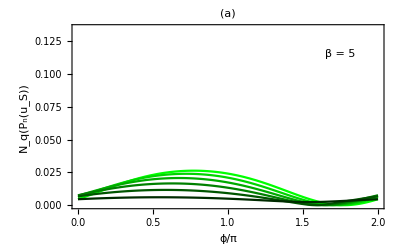

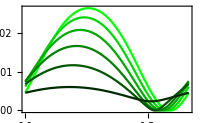

-Graphics-

Non-classicality-functional-energy-complex-lambda-full-2D-cold-INSET.pdf

Non-classicality-functional-energy-complex-lambda-full-2D-cold-INSET.png

Non-classicality-functional-energy-complex-lambda-full-2D-cold-INSET.eps

```mathematica
ClearAll[temp3,temp4,NegFunc,CoherenceSMaxN,τ,r,ρ12I,ρ12R,λmaxN]

Print["Maximum coherence in the system initial state:"]
CoherenceSMax=√(ρ11(1-ρ11))
CoherenceSMaxN=CoherenceSMax/.ρ11->1/4

Print["Plots with λ = λmax"]
λmax
λmaxN=(λmax/.{ωs->ωe+Δ,β->5,g->1,ℏ->1,ρ11->1/4})/.{ωe->1.,Δ->3.}

Print["Non-classicality functional for ΔES (Negativity), i.e. the function we wish to plot:"]
temp3=Simplify[negqΔES/.{ωs->ωe+Δ,β->5,g->1,ℏ->1,ρ11->1/4,λ1->λmaxN},Assumptions->constraints]

temp4=N[temp3/.{ωe->1.,Δ->3.}]
NegFunc[r12R_,r12I_,t_]:=Chop[temp4/.{ρ12R->r12R,ρ12I->r12I,τ->t}];

τmax=π/6;
Plot3D[(r=CoherenceSMaxN;
NegFunc[r*Cos[ϕ π],r*Sin[ϕ π],]),{ϕ,0,2 },{τ,0,τmax},
PlotLabel->"Non-classicality functional as a function of time",
AxesLabel->{"ϕ_12/π","τ"}]

Print["Time τ labels:"]
ClearAll[functions,plot1c,labels]
nτ=6;
τmax=π/6;
functions=Table[
(r=CoherenceSMaxN;
τ=(nτ-n+1)/nτ*τmax;
N[NegFunc[r*Cos[ϕ π],r*Sin[ϕ π],τ]]
),{n,1,nτ}];
labels=Table["τ = "<>ToString[1.*(nτ-n+1)/nτ*τmax ],{n,1,nτ}];
MatrixForm[labels]
colors=Table[RGBColor[0,(nτ-n+1)/nτ,0],{n,1,nτ}]
labels2=Table[τmax*(nτ-n+1)/nτ,{n,1,nτ}]
labels3={"τ = π/36","τ = π/18","τ = π/12","τ = π/9","τ = (5 π)/36 ","τ = π/6"}
labels3={"τ = π/6","τ = (5 π)/36 ","τ = π/9","τ = π/12","τ = π/18","τ = π/36"}

plot1c=Plot[
functions,{ϕ,0,2 },
PlotRange->{{0,2},{0,0.135}},
Frame->True,
FrameLabel->{"ϕ/π","N_q(P_n(u_S))"},
PlotLabel->"(a)",
Epilog->{Inset[Framed["β = 5"],Offset[{0,0},{1.75,0.115}],Background->White]},
(*PlotLegends->labels3,*)
PlotStyle->colors,
BaseStyle->{FontFamily->"Times",FontSize->20},
ImageSize->400]

plot1cInset=Plot[
functions,{ϕ,0,2 },
PlotRange->{{0,2},All},
Frame->True,
PlotStyle->colors,
BaseStyle->{FontFamily->"Times",FontSize->16},
ImageSize->200]

plot1cCombined=Plot[
functions,{ϕ,0,2 },
PlotRange->{{0,2},{0,0.135}},
Frame->True,
FrameLabel->{"ϕ/π","N_q(P_n(u_S))"},
PlotLabel->"(a)",
Epilog->{
Inset[Framed["β = 5"],Offset[{0,0},{1.75,0.115}],Background->White],Dynamic[Locator[Dynamic[Scaled[{0.4,0.6}]],plot1cInset]]},
PlotStyle->colors,
BaseStyle->{FontFamily->"Times",FontSize->20},
ImageSize->400]

Export["Non-classicality-functional-energy-complex-lambda-full-2D-cold-INSET.pdf",plot1cCombined]
Export["Non-classicality-functional-energy-complex-lambda-full-2D-cold-INSET.png",plot1cCombined,ImageResolution->200]
Export["Non-classicality-functional-energy-complex-lambda-full-2D-cold-INSET.eps",plot1cCombined]
```

#### OUT OF Resonance - Medium temperature

Maximum coherence in the system initial state:

√((1-ρ11) ρ11)

(√3)/4

Plots with λ = λmax

√(1/((ⅇ^(-1/2 β ωe ℏ)+ⅇ^((β ωe ℏ)/2))^2))

0.443409

Non-classicality functional for ΔES (Negativity), i.e. the function we wish to plot:

-1+1/((1+ⅇ^ωe) (4+Δ^2))(2 √(Sin[1/2 √(4+Δ^2) τ]^2) √(0.196612 (1+ⅇ^ωe)^2 (√(4+Δ^2) ρ12R Cos[1/2 √(4+Δ^2) τ]+Δ ρ12I Sin[1/2 √(4+Δ^2) τ])^2+(0.443409 (1+ⅇ^ωe) √(4+Δ^2) ρ12I Cos[1/2 √(4+Δ^2) τ]+(-3/2-0.443409 (1+ⅇ^ωe) Δ ρ12R) Sin[1/2 √(4+Δ^2) τ])^2)+2 √(Sin[1/2 √(4+Δ^2) τ]^2) √(0.196612 (1+ⅇ^ωe)^2 (√(4+Δ^2) ρ12R Cos[1/2 √(4+Δ^2) τ]+Δ ρ12I Sin[1/2 √(4+Δ^2) τ])^2+(0.443409 (1+ⅇ^ωe) √(4+Δ^2) ρ12I Cos[1/2 √(4+Δ^2) τ]+(-0.443409 Δ ρ12R+ⅇ^ωe (1/2-0.443409 Δ ρ12R)) Sin[1/2 √(4+Δ^2) τ])^2)+√((3/2+3 ⅇ^ωe+3/4 (1+ⅇ^ωe) Δ^2-0.443409 (1+ⅇ^ωe) Δ ρ12R+(3/2+0.443409 (1+ⅇ^ωe) Δ ρ12R) Cos[√(4+Δ^2) τ]+0.443409 (1+ⅇ^ωe) √(4+Δ^2) ρ12I Sin[√(4+Δ^2) τ])^2+0.196612 (1.+ⅇ^ωe)^2 (-1. Δ ρ12I+Δ ρ12I Cos[√(4+Δ^2) τ]-1. √(4+Δ^2) ρ12R Sin[√(4+Δ^2) τ])^2)+√((1/4 (4+Δ^2)+0.443409 Δ ρ12R+0.25 ⅇ^ωe (2.+Δ^2+1.77364 Δ ρ12R)+(-0.443409 Δ ρ12R+ⅇ^ωe (1/2-0.443409 Δ ρ12R)) Cos[√(4+Δ^2) τ]-0.443409 (1.+ⅇ^ωe) √(4+Δ^2) ρ12I Sin[√(4+Δ^2) τ])^2+0.196612 (1.+ⅇ^ωe)^2 (-1. Δ ρ12I+Δ ρ12I Cos[√(4+Δ^2) τ]-1. √(4+Δ^2) ρ12R Sin[√(4+Δ^2) τ])^2))

Non-classicality functional for ΔES (Negativity), i.e. the function we wish to plot, numerically:

-1.+0.0206878 (2. √(Sin[1.80278 τ]^2) √(2.71828 (3.60555 ρ12R Cos[1.80278 τ]+3. ρ12I Sin[1.80278 τ])^2+(5.94455 ρ12I Cos[1.80278 τ]+(-1.5-4.94616 ρ12R) Sin[1.80278 τ])^2)+2. √(Sin[1.80278 τ]^2) √(2.71828 (3.60555 ρ12R Cos[1.80278 τ]+3. ρ12I Sin[1.80278 τ])^2+(5.94455 ρ12I Cos[1.80278 τ]+(2.71828 (0.5-1.33023 ρ12R)-1.33023 ρ12R) Sin[1.80278 τ])^2)+√((3.25+1.33023 ρ12R+0.67957 (11.+5.32091 ρ12R)+(2.71828 (0.5-1.33023 ρ12R)-1.33023 ρ12R) Cos[3.60555 τ]-5.94455 ρ12I Sin[3.60555 τ])^2+2.71828 (-3. ρ12I+3. ρ12I Cos[3.60555 τ]-3.60555 ρ12R Sin[3.60555 τ])^2)+√((34.7532-4.94616 ρ12R+(1.5+4.94616 ρ12R) Cos[3.60555 τ]+5.94455 ρ12I Sin[3.60555 τ])^2+2.71828 (-3. ρ12I+3. ρ12I Cos[3.60555 τ]-3.60555 ρ12R Sin[3.60555 τ])^2))

-Graphics3D-

Time τ labels:

(τ = 0.523599
τ = 0.436332
τ = 0.349066
τ = 0.261799
τ = 0.174533
τ = 0.0872665)

{RGBColor[0, 1, 0],RGBColor[0, Rational[5, 6], 0],RGBColor[0, Rational[2, 3], 0],RGBColor[0, Rational[1, 2], 0],RGBColor[0, Rational[1, 3], 0],RGBColor[0, Rational[1, 6], 0]}

{τ = π/36,τ = π/18,τ = π/12,τ = π/9,τ = (5 π)/36 ,τ = π/6}

{τ = π/6,τ = (5 π)/36 ,τ = π/9,τ = π/12,τ = π/18,τ = π/36}

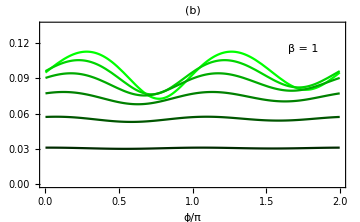

Non-classicality-functional-energy-complex-lambda-full-2D-medium.pdf

Non-classicality-functional-energy-complex-lambda-full-2D-medium.png

Non-classicality-functional-energy-complex-lambda-full-2D-medium.eps

```mathematica
ClearAll[temp3,temp4,NegFunc,CoherenceSMaxN,τ,r,ρ12I,ρ12R]

Print["Maximum coherence in the system initial state:"]
CoherenceSMax=√(ρ11(1-ρ11))
CoherenceSMaxN=CoherenceSMax/.ρ11->1/4

Print["Plots with λ = λmax"]
λmax
λmaxN=(λmax/.{ωs->ωe+Δ,β->1,g->1,ℏ->1,ρ11->1/4})/.{ωe->1.,Δ->3.}

Print["Non-classicality functional for ΔES (Negativity), i.e. the function we wish to plot:"]
temp3=Simplify[negqΔES/.{ωs->ωe+Δ,β->1,g->1,ℏ->1,ρ11->1/4,λ1->λmaxN},Assumptions->constraints]

Print["Non-classicality functional for ΔES (Negativity), i.e. the function we wish to plot, numerically:"]
temp4=N[temp3/.{ωe->1.,Δ->3.}]
NegFunc[r12R_,r12I_,t_]:=Chop[temp4/.{ρ12R->r12R,ρ12I->r12I,τ->t}];

τmax=π/6;
Plot3D[(r=CoherenceSMaxN;
NegFunc[r*Cos[ϕ π],r*Sin[ϕ π],]),{ϕ,0,2 },{τ,0,τmax},
PlotLabel->"Non-classicality functional as a function of time",
AxesLabel->{"ϕ_12/π","τ"}]

Print["Time τ labels:"]
ClearAll[functions,plot1c,labels]
nτ=6;
τmax=π/6;
functions=Table[
(r=CoherenceSMaxN;
τ=(nτ-n+1)/nτ*τmax;
N[NegFunc[r*Cos[ϕ π],r*Sin[ϕ π],τ]]
),{n,1,nτ}];
labels=Table["τ = "<>ToString[1.*(nτ-n+1)/nτ*τmax ],{n,1,nτ}];
MatrixForm[labels]
colors=Table[RGBColor[0,(nτ-n+1)/nτ,0],{n,1,nτ}]
labels3={"τ = π/36","τ = π/18","τ = π/12","τ = π/9","τ = (5 π)/36 ","τ = π/6"}
labels3={"τ = π/6","τ = (5 π)/36 ","τ = π/9","τ = π/12","τ = π/18","τ = π/36"}

plot1c=Plot[
functions,{ϕ,0,2 },
PlotRange->{{0,2},{0,0.135}},
Frame->True,
FrameLabel->{"ϕ/π",None},
PlotLabel->"(b)",
Epilog->{Inset[Framed["β = 1"],Offset[{0,0},{1.75,0.115}],Background->White]},
(*PlotLegends->labels3,*)
PlotStyle->colors,
BaseStyle->{FontFamily->"Times",FontSize->20},
ImageSize->Medium]

Export["Non-classicality-functional-energy-complex-lambda-full-2D-medium.pdf",plot1c]
Export["Non-classicality-functional-energy-complex-lambda-full-2D-medium.png",plot1c,ImageResolution->200]
Export["Non-classicality-functional-energy-complex-lambda-full-2D-medium.eps",plot1c]
```

#### OUT OF Resonance - High temperature

Maximum coherence in the system initial state:

√((1-ρ11) ρ11)

(√3)/4

Plots with λ = λmax

√(1/((ⅇ^(-1/2 β ωe ℏ)+ⅇ^((β ωe ℏ)/2))^2))

0.49751

Non-classicality functional for ΔES (Negativity), i.e. the function we wish to plot:

-1+1/((1+ⅇ^(ωe/5)) (4+Δ^2))(2 √(Sin[1/2 √(4+Δ^2) τ]^2) √(0.247517 (1+ⅇ^(ωe/5))^2 (√(4+Δ^2) ρ12R Cos[1/2 √(4+Δ^2) τ]+Δ ρ12I Sin[1/2 √(4+Δ^2) τ])^2+(0.49751 (1+ⅇ^(ωe/5)) √(4+Δ^2) ρ12I Cos[1/2 √(4+Δ^2) τ]+(-3/2-0.49751 (1+ⅇ^(ωe/5)) Δ ρ12R) Sin[1/2 √(4+Δ^2) τ])^2)+2 √(Sin[1/2 √(4+Δ^2) τ]^2) √(0.247517 (1+ⅇ^(ωe/5))^2 (√(4+Δ^2) ρ12R Cos[1/2 √(4+Δ^2) τ]+Δ ρ12I Sin[1/2 √(4+Δ^2) τ])^2+(0.49751 (1+ⅇ^(ωe/5)) √(4+Δ^2) ρ12I Cos[1/2 √(4+Δ^2) τ]+(-0.49751 Δ ρ12R+ⅇ^(ωe/5) (1/2-0.49751 Δ ρ12R)) Sin[1/2 √(4+Δ^2) τ])^2)+√((3/2+3 ⅇ^(ωe/5)+3/4 (1+ⅇ^(ωe/5)) Δ^2-0.49751 (1+ⅇ^(ωe/5)) Δ ρ12R+(3/2+0.49751 (1+ⅇ^(ωe/5)) Δ ρ12R) Cos[√(4+Δ^2) τ]+0.49751 (1+ⅇ^(ωe/5)) √(4+Δ^2) ρ12I Sin[√(4+Δ^2) τ])^2+0.247517 (1.+ⅇ^(ωe/5))^2 (-1. Δ ρ12I+Δ ρ12I Cos[√(4+Δ^2) τ]-1. √(4+Δ^2) ρ12R Sin[√(4+Δ^2) τ])^2)+√((1/4 (4+Δ^2)+0.49751 Δ ρ12R+0.25 ⅇ^(ωe/5) (2.+Δ^2+1.99004 Δ ρ12R)+(-0.49751 Δ ρ12R+ⅇ^(ωe/5) (1/2-0.49751 Δ ρ12R)) Cos[√(4+Δ^2) τ]-0.49751 (1.+ⅇ^(ωe/5)) √(4+Δ^2) ρ12I Sin[√(4+Δ^2) τ])^2+0.247517 (1.+ⅇ^(ωe/5))^2 (-1. Δ ρ12I+Δ ρ12I Cos[√(4+Δ^2) τ]-1. √(4+Δ^2) ρ12R Sin[√(4+Δ^2) τ])^2))

-1.+0.0346282 (2. √(Sin[1.80278 τ]^2) √(1.2214 (3.60555 ρ12R Cos[1.80278 τ]+3. ρ12I Sin[1.80278 τ])^2+(3.98475 ρ12I Cos[1.80278 τ]+(-1.5-3.31551 ρ12R) Sin[1.80278 τ])^2)+2. √(Sin[1.80278 τ]^2) √(1.2214 (3.60555 ρ12R Cos[1.80278 τ]+3. ρ12I Sin[1.80278 τ])^2+(3.98475 ρ12I Cos[1.80278 τ]+(1.2214 (0.5-1.49253 ρ12R)-1.49253 ρ12R) Sin[1.80278 τ])^2)+√((3.25+1.49253 ρ12R+0.305351 (11.+5.97012 ρ12R)+(1.2214 (0.5-1.49253 ρ12R)-1.49253 ρ12R) Cos[3.60555 τ]-3.98475 ρ12I Sin[3.60555 τ])^2+1.2214 (-3. ρ12I+3. ρ12I Cos[3.60555 τ]-3.60555 ρ12R Sin[3.60555 τ])^2)+√((20.1587-3.31551 ρ12R+(1.5+3.31551 ρ12R) Cos[3.60555 τ]+3.98475 ρ12I Sin[3.60555 τ])^2+1.2214 (-3. ρ12I+3. ρ12I Cos[3.60555 τ]-3.60555 ρ12R Sin[3.60555 τ])^2))

-Graphics3D-

Time τ labels:

(τ = 0.523599
τ = 0.436332
τ = 0.349066
τ = 0.261799
τ = 0.174533
τ = 0.0872665)

{RGBColor[0, 1, 0],RGBColor[0, Rational[5, 6], 0],RGBColor[0, Rational[2, 3], 0],RGBColor[0, Rational[1, 2], 0],RGBColor[0, Rational[1, 3], 0],RGBColor[0, Rational[1, 6], 0]}

{π/36,π/18,π/12,π/9,(5 π)/36,π/6}

{τ = π/36,τ = π/18,τ = π/12,τ = π/9,τ = (5 π)/36 ,τ = π/6}

{τ = π/6,τ = (5 π)/36 ,τ = π/9,τ = π/12,τ = π/18,τ = π/36}

{RGBColor[0, 1, 0],RGBColor[0, Rational[5, 6], 0],RGBColor[0, Rational[2, 3], 0],RGBColor[0, Rational[1, 2], 0],RGBColor[0, Rational[1, 3], 0],RGBColor[0, Rational[1, 6], 0]}

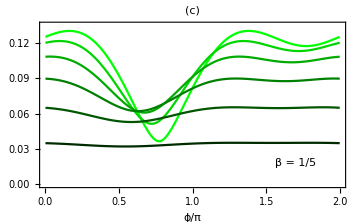

Non-classicality-functional-energy-complex-lambda-full-2D-hot.pdf

Non-classicality-functional-energy-complex-lambda-full-2D-hot.png

Non-classicality-functional-energy-complex-lambda-full-2D-hot.eps

```mathematica
ClearAll[temp3,temp4,NegFunc,CoherenceSMaxN,τ,r,ρ12I,ρ12R]

Print["Maximum coherence in the system initial state:"]
CoherenceSMax=√(ρ11(1-ρ11))
CoherenceSMaxN=CoherenceSMax/.ρ11->1/4

Print["Plots with λ = λmax"]
λmax
λmaxN=(λmax/.{ωs->ωe+Δ,β->1/5,g->1,ℏ->1,ρ11->1/4})/.{ωe->1.,Δ->3.}

Print["Non-classicality functional for ΔES (Negativity), i.e. the function we wish to plot:"]
temp3=Simplify[negqΔES/.{ωs->ωe+Δ,β->1/5,g->1,ℏ->1,ρ11->1/4,λ1->λmaxN},Assumptions->constraints]

temp4=N[temp3/.{ωe->1.,Δ->3.}]
NegFunc[r12R_,r12I_,t_]:=Chop[temp4/.{ρ12R->r12R,ρ12I->r12I,τ->t}];

τmax=π/6;
Plot3D[(r=CoherenceSMaxN;
NegFunc[r*Cos[ϕ π],r*Sin[ϕ π],]),{ϕ,0,2 },{τ,0,τmax},
PlotLabel->"Non-classicality functional as a function of time",
AxesLabel->{"ϕ_12/π","τ"}]

Print["Time τ labels:"]
ClearAll[functions,plot1c,labels]
nτ=6;
τmax=π/6;
functions=Table[
(r=CoherenceSMaxN;
τ=(nτ-n+1)/nτ*τmax;
N[NegFunc[r*Cos[ϕ π],r*Sin[ϕ π],τ]]
),{n,1,nτ}];
labels=Table["τ = "<>ToString[1.*(nτ-n+1)/nτ*τmax ],{n,1,nτ}];
MatrixForm[labels]
colors=Table[RGBColor[0,(nτ-n+1)/nτ,0],{n,1,nτ}]
labels2=Table[τmax*n/nτ,{n,1,nτ}]
 labels3={"τ = π/36","τ = π/18","τ = π/12","τ = π/9","τ = (5 π)/36 ","τ = π/6"}
 labels3={"τ = π/6","τ = (5 π)/36 ","τ = π/9","τ = π/12","τ = π/18","τ = π/36"}
(*labels3={"τ = π/36","τ = π/18","τ = π/12","τ = π/6","τ = 5 π/36 ","τ = π/6"}*)
legenda=LineLegend[labels3,LabelStyle->{FontSize->20,FontFamily->"Times"}];
colors=Table[RGBColor[0,(nτ-n+1)/nτ,0],{n,1,nτ}]

plot1c=Plot[
functions,{ϕ,0,2 },
PlotRange->{{0,2},{0,0.135}},
Frame->True,
FrameLabel->{"ϕ/π",None},
PlotLabel->"(c)",
Epilog->{Inset[Framed["β = 1/5"],Offset[{0,0},{1.7,0.018}],Background->White]},
PlotLegends->legenda,
PlotStyle->colors,
BaseStyle->{FontFamily->"Times",FontSize->20},
ImageSize->Medium]

Export["Non-classicality-functional-energy-complex-lambda-full-2D-hot.pdf",plot1c]
Export["Non-classicality-functional-energy-complex-lambda-full-2D-hot.png",plot1c,ImageResolution->200]
Export["Non-classicality-functional-energy-complex-lambda-full-2D-hot.eps",plot1c]
```

## 6b. FIGURE 2: 2D plots of the Non-classicality of Non-Energy-preserving Work Wnep (LM)

#### Cold temperature

Parameters:

Maximum coherence in the system initial state:

√((1-ρ11) ρ11)

(√3)/4

{ℏ→1.,ρ11→1/4,ωe→1,ωs→4,β→5,g→1}

Maximum coherence λmax in the ancilla:

√(1/((ⅇ^(-1/2 β ωe ℏ)+ⅇ^((β ωe ℏ)/2))^2))

0.0815356

Non-classicality functional of the non-energy-preserving Work:

-1+ⅇ^Re[β ωe ℏ] Abs[(-1+ρ11)/(1+ⅇ^(β ωe ℏ))]+Abs[ρ11/(1+ⅇ^(β ωe ℏ))]+Abs[((ⅈ √(4 g^2+Δ^2) Cos[1/2 √(4 g^2+Δ^2) τ]-Δ Sin[1/2 √(4 g^2+Δ^2) τ]) (ⅈ √(4 g^2+Δ^2) (-1+ρ11) Cos[1/2 √(4 g^2+Δ^2) τ]+(Δ (-1+ρ11)+2 (1+ⅇ^(β ωe ℏ)) g λ1 (-ⅈ ρ12I+ρ12R)) Sin[1/2 √(4 g^2+Δ^2) τ]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+Δ^2))]+2 Abs[(g Sin[1/2 √(4 g^2+Δ^2) τ] (-√(4 g^2+Δ^2) λ1 (ρ12I+ⅈ ρ12R) Cos[1/2 √(4 g^2+Δ^2) τ]+((-2 g (-1+ρ11)+(1+ⅇ^(β ωe ℏ)) Δ λ1 (-ⅈ ρ12I+ρ12R)) Sin[1/2 √(4 g^2+Δ^2) τ])/(1+ⅇ^(β ωe ℏ))))/(4 g^2+Δ^2)]+Abs[((ⅈ √(4 g^2+Δ^2) Cos[1/2 √(4 g^2+Δ^2) τ]+Δ Sin[1/2 √(4 g^2+Δ^2) τ]) (-ⅈ ⅇ^(β ωe ℏ) √(4 g^2+Δ^2) ρ11 Cos[1/2 √(4 g^2+Δ^2) τ]+(2 g λ1 (ⅈ ρ12I+ρ12R)+ⅇ^(β ωe ℏ) (Δ ρ11+2 g λ1 (ⅈ ρ12I+ρ12R))) Sin[1/2 √(4 g^2+Δ^2) τ]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+Δ^2))]+2 Abs[(g Sin[1/2 √(4 g^2+Δ^2) τ] (√(4 g^2+Δ^2) λ1 (ρ12I-ⅈ ρ12R) Cos[1/2 √(4 g^2+Δ^2) τ]+((-Δ λ1 (ⅈ ρ12I+ρ12R)+ⅇ^(β ωe ℏ) (2 g ρ11-Δ λ1 (ⅈ ρ12I+ρ12R))) Sin[1/2 √(4 g^2+Δ^2) τ])/(1+ⅇ^(β ωe ℏ))))/(4 g^2+Δ^2)]

0.153846 (-1.64675+0.00334643 Abs[(-ⅈ √13 Cos[(√13 τ)/2]-3 Sin[(√13 τ)/2]) ((0.+133.778 ⅈ) Cos[(√13 τ)/2]+(-111.31-(0.+24.365 ⅈ) ρ12I-24.365 ρ12R) Sin[(√13 τ)/2])]+Abs[Sin[(√13 τ)/2] (0.293981 (ρ12I-ⅈ ρ12R) Cos[(√13 τ)/2]+(0.496654-(0.+0.244607 ⅈ) ρ12I-0.244607 ρ12R) Sin[(√13 τ)/2])]+Abs[Sin[(√13 τ)/2] (-0.293981 (ρ12I+ⅈ ρ12R) Cos[(√13 τ)/2]+(0.0100393+0.244607 (-ⅈ ρ12I+ρ12R)) Sin[(√13 τ)/2])]+0.00334643 Abs[(ⅈ √13 Cos[(√13 τ)/2]-3 Sin[(√13 τ)/2]) (-3/4 ⅈ √13 Cos[(√13 τ)/2]+(-9/4+24.365 (-ⅈ ρ12I+ρ12R)) Sin[(√13 τ)/2])])

0.153846 (-1.64675+0.00334643 Abs[((0.-3.60555 ⅈ) Cos[1.80278 τ]-3. Sin[1.80278 τ]) ((0.+133.778 ⅈ) Cos[1.80278 τ]+(-111.31-(0.+24.365 ⅈ) ρ12I-24.365 ρ12R) Sin[1.80278 τ])]+Abs[Sin[1.80278 τ] (0.293981 (ρ12I-(0.+1. ⅈ) ρ12R) Cos[1.80278 τ]+(0.496654-(0.+0.244607 ⅈ) ρ12I-0.244607 ρ12R) Sin[1.80278 τ])]+Abs[Sin[1.80278 τ] (-0.293981 (ρ12I+(0.+1. ⅈ) ρ12R) Cos[1.80278 τ]+(0.0100393+0.244607 ((0.-1. ⅈ) ρ12I+ρ12R)) Sin[1.80278 τ])]+0.00334643 Abs[((0.+3.60555 ⅈ) Cos[1.80278 τ]-3. Sin[1.80278 τ]) ((0.-2.70416 ⅈ) Cos[1.80278 τ]+(-2.25+24.365 ((0.-1. ⅈ) ρ12I+ρ12R)) Sin[1.80278 τ])])

π/6

(τ = 0.523599
τ = 0.436332
τ = 0.349066
τ = 0.261799
τ = 0.174533
τ = 0.0872665)

{π/6,(5 π)/36,π/9,π/12,π/18,π/36}

{τ = π/6,τ = (5 π)/36 ,τ = π/9,τ = π/12,τ = π/18,τ = π/36}

{RGBColor[0, 1, 0],RGBColor[0, Rational[5, 6], 0],RGBColor[0, Rational[2, 3], 0],RGBColor[0, Rational[1, 2], 0],RGBColor[0, Rational[1, 3], 0],RGBColor[0, Rational[1, 6], 0]}

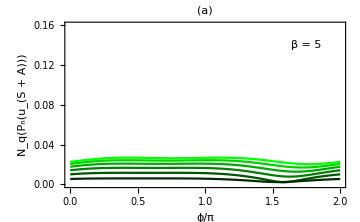

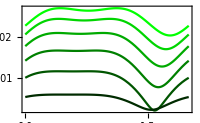

-Graphics-

Non-classicality-functional-Wnep-complex-lambda-full-2D-cold-INSET.pdf

Non-classicality-functional-Wnep-complex-lambda-full-2D-cold-INSET.png

Non-classicality-functional-Wnep-complex-lambda-full-2D-cold-INSET.eps

```mathematica
ClearAll[τ,r12I,r12R,ρ12I,ρ12R,ϕ12,β,ω,ωe,ωs,Δ,λ1,ℏ,g]

Print["Parameters:"]

Print["Maximum coherence in the system initial state:"]
CoherenceSMax=√(ρ11(1-ρ11))
CoherenceSMaxN=CoherenceSMax/.ρ11->1/4

parameters2={ℏ->1.,ρ11->1/4,ωe->1,ωs->4,β->5,g->1}

Print["Maximum coherence λmax in the ancilla:"]
λmax
λmaxN=(λmax)/.parameters2

Print["Non-classicality functional of the non-energy-preserving Work:"]
Simplify[negqLM/.{ωs->ωe+Δ},Assumptions->constraints]

ClearAll[τ,temp,negqLMplot, functions,plot1d,labels]

temp=Simplify[negqLM/.parameters2,Assumptions->constraints]/.λ1->λmaxN

negqLMplot[r12R_,r12I_,t_]:=Chop[N[temp/.{ρ12R->r12R,ρ12I->r12I,τ->t}]]
negqLMplot[ρ12R,ρ12I,τ]

ClearAll[functions,plot1d,labels]
nτ=6;
τmax=π/6
functions=Table[
(r=CoherenceSMaxN;
τ=(nτ-n+1)/nτ*τmax;
N[negqLMplot[r*Cos[ϕ π],r*Sin[ϕ π],τ]]
),{n,1,nτ}];
labels=Table["τ = "<>ToString[1.*(nτ-n+1)/nτ*τmax ],{n,1,nτ}];
MatrixForm[labels]
labels2=Table[τmax*(nτ-n+1)/nτ,{n,1,nτ}]
 labels3={"τ = π/6","τ = (5 π)/36 ","τ = π/9","τ = π/12","τ = π/18","τ = π/36"}
legenda=LineLegend[labels3,LabelStyle->{FontSize->20}];
colors=Table[RGBColor[0,(nτ-n+1)/nτ,0],{n,1,nτ}]

plot1d=Plot[
functions,{ϕ,0,2 },
PlotRange->{{0,2},{0,0.16}},
Frame->True,
FrameLabel->{"ϕ/π","N_q(P_n(u_(S + A)))"},
PlotLabel->"(a)",
PlotStyle->colors,
BaseStyle->{FontFamily->"Times",FontSize->20},
Epilog->{Inset[Framed["β = 5"],Offset[{0,0},{1.75,0.14}],Background->White]},
ImageSize->Medium]

plot1dInset=Plot[
functions,{ϕ,0,2 },
PlotRange->{{0,2},All},
Frame->True,
PlotStyle->colors,
BaseStyle->{FontFamily->"Times",FontSize->16},
ImageSize->200]

plot1dCombined=Plot[
functions,{ϕ,0,2 },
PlotRange->{{0,2},{0,0.16}},
Frame->True,
FrameLabel->{"ϕ/π","N_q(P_n(u_(S + A)))"},
PlotLabel->"(a)",
Epilog->{
Inset[Framed["β = 5"],Offset[{0,0},{1.75,0.115}],Background->White],Dynamic[Locator[Dynamic[Scaled[{0.4,0.6}]],plot1dInset]]},
PlotStyle->colors,
BaseStyle->{FontFamily->"Times",FontSize->20},
ImageSize->400]

Export["Non-classicality-functional-Wnep-complex-lambda-full-2D-cold-INSET.pdf",plot1dCombined]
Export["Non-classicality-functional-Wnep-complex-lambda-full-2D-cold-INSET.png",plot1dCombined,ImageResolution->200]
Export["Non-classicality-functional-Wnep-complex-lambda-full-2D-cold-INSET.eps",plot1dCombined]
```

#### Medium temperature

Parameters:

Maximum coherence in the system initial state:

√((1-ρ11) ρ11)

(√3)/4

{ℏ→1.,ρ11→1/4,ωe→1,ωs→4,β→1,g→1}

Maximum coherence λmax in the ancilla:

√(1/((ⅇ^(-1/2 β ωe ℏ)+ⅇ^((β ωe ℏ)/2))^2))

0.443409

Non-classicality functional of the non-energy-preserving Work:

-1+ⅇ^Re[β ωe ℏ] Abs[(-1+ρ11)/(1+ⅇ^(β ωe ℏ))]+Abs[ρ11/(1+ⅇ^(β ωe ℏ))]+Abs[((ⅈ √(4 g^2+Δ^2) Cos[1/2 √(4 g^2+Δ^2) τ]-Δ Sin[1/2 √(4 g^2+Δ^2) τ]) (ⅈ √(4 g^2+Δ^2) (-1+ρ11) Cos[1/2 √(4 g^2+Δ^2) τ]+(Δ (-1+ρ11)+2 (1+ⅇ^(β ωe ℏ)) g λ1 (-ⅈ ρ12I+ρ12R)) Sin[1/2 √(4 g^2+Δ^2) τ]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+Δ^2))]+2 Abs[(g Sin[1/2 √(4 g^2+Δ^2) τ] (-√(4 g^2+Δ^2) λ1 (ρ12I+ⅈ ρ12R) Cos[1/2 √(4 g^2+Δ^2) τ]+((-2 g (-1+ρ11)+(1+ⅇ^(β ωe ℏ)) Δ λ1 (-ⅈ ρ12I+ρ12R)) Sin[1/2 √(4 g^2+Δ^2) τ])/(1+ⅇ^(β ωe ℏ))))/(4 g^2+Δ^2)]+Abs[((ⅈ √(4 g^2+Δ^2) Cos[1/2 √(4 g^2+Δ^2) τ]+Δ Sin[1/2 √(4 g^2+Δ^2) τ]) (-ⅈ ⅇ^(β ωe ℏ) √(4 g^2+Δ^2) ρ11 Cos[1/2 √(4 g^2+Δ^2) τ]+(2 g λ1 (ⅈ ρ12I+ρ12R)+ⅇ^(β ωe ℏ) (Δ ρ11+2 g λ1 (ⅈ ρ12I+ρ12R))) Sin[1/2 √(4 g^2+Δ^2) τ]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+Δ^2))]+2 Abs[(g Sin[1/2 √(4 g^2+Δ^2) τ] (√(4 g^2+Δ^2) λ1 (ρ12I-ⅈ ρ12R) Cos[1/2 √(4 g^2+Δ^2) τ]+((-Δ λ1 (ⅈ ρ12I+ρ12R)+ⅇ^(β ωe ℏ) (2 g ρ11-Δ λ1 (ⅈ ρ12I+ρ12R))) Sin[1/2 √(4 g^2+Δ^2) τ])/(1+ⅇ^(β ωe ℏ))))/(4 g^2+Δ^2)]

0.153846 (-2.49906+0.134471 Abs[(-ⅈ √13 Cos[(√13 τ)/2]-3 Sin[(√13 τ)/2]) ((0.+2.45023 ⅈ) Cos[(√13 τ)/2]+(-2.03871-(0.+3.29744 ⅈ) ρ12I-3.29744 ρ12R) Sin[(√13 τ)/2])]+Abs[Sin[(√13 τ)/2] (1.59874 (ρ12I-ⅈ ρ12R) Cos[(√13 τ)/2]+(0.365529-(0.+1.33023 ⅈ) ρ12I-1.33023 ρ12R) Sin[(√13 τ)/2])]+Abs[Sin[(√13 τ)/2] (-1.59874 (ρ12I+ⅈ ρ12R) Cos[(√13 τ)/2]+(0.403412+1.33023 (-ⅈ ρ12I+ρ12R)) Sin[(√13 τ)/2])]+0.134471 Abs[(ⅈ √13 Cos[(√13 τ)/2]-3 Sin[(√13 τ)/2]) (-3/4 ⅈ √13 Cos[(√13 τ)/2]+(-9/4+3.29744 (-ⅈ ρ12I+ρ12R)) Sin[(√13 τ)/2])])

0.153846 (-2.49906+0.134471 Abs[((0.-3.60555 ⅈ) Cos[1.80278 τ]-3. Sin[1.80278 τ]) ((0.+2.45023 ⅈ) Cos[1.80278 τ]+(-2.03871-(0.+3.29744 ⅈ) ρ12I-3.29744 ρ12R) Sin[1.80278 τ])]+Abs[Sin[1.80278 τ] (1.59874 (ρ12I-(0.+1. ⅈ) ρ12R) Cos[1.80278 τ]+(0.365529-(0.+1.33023 ⅈ) ρ12I-1.33023 ρ12R) Sin[1.80278 τ])]+Abs[Sin[1.80278 τ] (-1.59874 (ρ12I+(0.+1. ⅈ) ρ12R) Cos[1.80278 τ]+(0.403412+1.33023 ((0.-1. ⅈ) ρ12I+ρ12R)) Sin[1.80278 τ])]+0.134471 Abs[((0.+3.60555 ⅈ) Cos[1.80278 τ]-3. Sin[1.80278 τ]) ((0.-2.70416 ⅈ) Cos[1.80278 τ]+(-2.25+3.29744 ((0.-1. ⅈ) ρ12I+ρ12R)) Sin[1.80278 τ])])

π/6

(τ = 0.523599
τ = 0.436332
τ = 0.349066
τ = 0.261799
τ = 0.174533
τ = 0.0872665)

{π/6,(5 π)/36,π/9,π/12,π/18,π/36}

{τ = π/6,τ = (5 π)/36 ,τ = π/9,τ = π/12,τ = π/18,τ = π/36}

{RGBColor[0, 1, 0],RGBColor[0, Rational[5, 6], 0],RGBColor[0, Rational[2, 3], 0],RGBColor[0, Rational[1, 2], 0],RGBColor[0, Rational[1, 3], 0],RGBColor[0, Rational[1, 6], 0]}

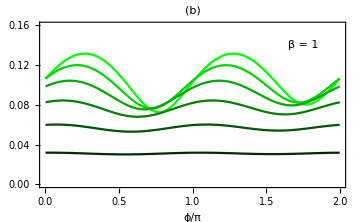

Non-classicality-functional-Wnep-complex-lambda-full-2D-medium.pdf

Non-classicality-functional-Wnep-complex-lambda-full-2D-medium.png

Non-classicality-functional-Wnep-complex-lambda-full-2D-medium.eps

```mathematica
ClearAll[τ,r12I,r12R,ρ12I,ρ12R,ϕ12,β,ω,ωe,ωs,Δ,λ1,ℏ,g]

Print["Parameters:"]

Print["Maximum coherence in the system initial state:"]
CoherenceSMax=√(ρ11(1-ρ11))
CoherenceSMaxN=CoherenceSMax/.ρ11->1/4

parameters2={ℏ->1.,ρ11->1/4,ωe->1,ωs->4,β->1,g->1}

Print["Maximum coherence λmax in the ancilla:"]
λmax
λmaxN=(λmax)/.parameters2

Print["Non-classicality functional of the non-energy-preserving Work:"]
Simplify[negqLM/.{ωs->ωe+Δ},Assumptions->constraints]

ClearAll[τ,temp,negqLMplot, functions,plot1d,labels]

temp=Simplify[negqLM/.parameters2,Assumptions->constraints]/.λ1->λmaxN

negqLMplot[r12R_,r12I_,t_]:=Chop[N[temp/.{ρ12R->r12R,ρ12I->r12I,τ->t}]]
negqLMplot[ρ12R,ρ12I,τ]

ClearAll[functions,plot1d,labels]
nτ=6;
τmax=π/6
functions=Table[
(r=CoherenceSMaxN;
τ=(nτ-n+1)/nτ*τmax;
N[negqLMplot[r*Cos[ϕ π],r*Sin[ϕ π],τ]]
),{n,1,nτ}];
labels=Table["τ = "<>ToString[1.*(nτ-n+1)/nτ*τmax ],{n,1,nτ}];
MatrixForm[labels]
labels2=Table[τmax*(nτ-n+1)/nτ,{n,1,nτ}]
 labels3={"τ = π/6","τ = (5 π)/36 ","τ = π/9","τ = π/12","τ = π/18","τ = π/36"}
legenda=LineLegend[labels3,LabelStyle->{FontSize->20}];
colors=Table[RGBColor[0,(nτ-n+1)/nτ,0],{n,1,nτ}]

plot1d=Plot[
functions,{ϕ,0,2 },
PlotRange->{{0,2},{0,0.16}},
Frame->True,
FrameLabel->{"ϕ/π",None},PlotLabel->"(b)",
PlotStyle->colors,
BaseStyle->{FontFamily->"Times",FontSize->20},
Epilog->{Inset[Framed["β = 1"],Offset[{0,0},{1.75,0.14}],Background->White]},
ImageSize->Medium]

Export["Non-classicality-functional-Wnep-complex-lambda-full-2D-medium.pdf",plot1d]
Export["Non-classicality-functional-Wnep-complex-lambda-full-2D-medium.png",plot1d,ImageResolution->200]
Export["Non-classicality-functional-Wnep-complex-lambda-full-2D-medium.eps",plot1d]
```

#### High temperature

Parameters:

Maximum coherence in the system initial state:

√((1-ρ11) ρ11)

(√3)/4

{ℏ→1.,ρ11→1/4,ωe→1,ωs→4,β→1/5,g→1}

Maximum coherence λmax in the ancilla:

√(1/((ⅇ^(-1/2 β ωe ℏ)+ⅇ^((β ωe ℏ)/2))^2))

0.49751

Non-classicality functional of the non-energy-preserving Work:

-1+ⅇ^Re[β ωe ℏ] Abs[(-1+ρ11)/(1+ⅇ^(β ωe ℏ))]+Abs[ρ11/(1+ⅇ^(β ωe ℏ))]+Abs[((ⅈ √(4 g^2+Δ^2) Cos[1/2 √(4 g^2+Δ^2) τ]-Δ Sin[1/2 √(4 g^2+Δ^2) τ]) (ⅈ √(4 g^2+Δ^2) (-1+ρ11) Cos[1/2 √(4 g^2+Δ^2) τ]+(Δ (-1+ρ11)+2 (1+ⅇ^(β ωe ℏ)) g λ1 (-ⅈ ρ12I+ρ12R)) Sin[1/2 √(4 g^2+Δ^2) τ]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+Δ^2))]+2 Abs[(g Sin[1/2 √(4 g^2+Δ^2) τ] (-√(4 g^2+Δ^2) λ1 (ρ12I+ⅈ ρ12R) Cos[1/2 √(4 g^2+Δ^2) τ]+((-2 g (-1+ρ11)+(1+ⅇ^(β ωe ℏ)) Δ λ1 (-ⅈ ρ12I+ρ12R)) Sin[1/2 √(4 g^2+Δ^2) τ])/(1+ⅇ^(β ωe ℏ))))/(4 g^2+Δ^2)]+Abs[((ⅈ √(4 g^2+Δ^2) Cos[1/2 √(4 g^2+Δ^2) τ]+Δ Sin[1/2 √(4 g^2+Δ^2) τ]) (-ⅈ ⅇ^(β ωe ℏ) √(4 g^2+Δ^2) ρ11 Cos[1/2 √(4 g^2+Δ^2) τ]+(2 g λ1 (ⅈ ρ12I+ρ12R)+ⅇ^(β ωe ℏ) (Δ ρ11+2 g λ1 (ⅈ ρ12I+ρ12R))) Sin[1/2 √(4 g^2+Δ^2) τ]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+Δ^2))]+2 Abs[(g Sin[1/2 √(4 g^2+Δ^2) τ] (√(4 g^2+Δ^2) λ1 (ρ12I-ⅈ ρ12R) Cos[1/2 √(4 g^2+Δ^2) τ]+((-Δ λ1 (ⅈ ρ12I+ρ12R)+ⅇ^(β ωe ℏ) (2 g ρ11-Δ λ1 (ⅈ ρ12I+ρ12R))) Sin[1/2 √(4 g^2+Δ^2) τ])/(1+ⅇ^(β ωe ℏ))))/(4 g^2+Δ^2)]

0.153846 (-3.08804+0.225083 Abs[(-ⅈ √13 Cos[(√13 τ)/2]-3 Sin[(√13 τ)/2]) ((0.+1.10096 ⅈ) Cos[(√13 τ)/2]+(-0.916052-(0.+2.21034 ⅈ) ρ12I-2.21034 ρ12R) Sin[(√13 τ)/2])]+Abs[Sin[(√13 τ)/2] (1.7938 (ρ12I-ⅈ ρ12R) Cos[(√13 τ)/2]+(0.274917-(0.+1.49253 ⅈ) ρ12I-1.49253 ρ12R) Sin[(√13 τ)/2])]+Abs[Sin[(√13 τ)/2] (-1.7938 (ρ12I+ⅈ ρ12R) Cos[(√13 τ)/2]+(0.675249+1.49253 (-ⅈ ρ12I+ρ12R)) Sin[(√13 τ)/2])]+0.225083 Abs[(ⅈ √13 Cos[(√13 τ)/2]-3 Sin[(√13 τ)/2]) (-3/4 ⅈ √13 Cos[(√13 τ)/2]+(-9/4+2.21034 (-ⅈ ρ12I+ρ12R)) Sin[(√13 τ)/2])])

0.153846 (-3.08804+0.225083 Abs[((0.-3.60555 ⅈ) Cos[1.80278 τ]-3. Sin[1.80278 τ]) ((0.+1.10096 ⅈ) Cos[1.80278 τ]+(-0.916052-(0.+2.21034 ⅈ) ρ12I-2.21034 ρ12R) Sin[1.80278 τ])]+Abs[Sin[1.80278 τ] (1.7938 (ρ12I-(0.+1. ⅈ) ρ12R) Cos[1.80278 τ]+(0.274917-(0.+1.49253 ⅈ) ρ12I-1.49253 ρ12R) Sin[1.80278 τ])]+Abs[Sin[1.80278 τ] (-1.7938 (ρ12I+(0.+1. ⅈ) ρ12R) Cos[1.80278 τ]+(0.675249+1.49253 ((0.-1. ⅈ) ρ12I+ρ12R)) Sin[1.80278 τ])]+0.225083 Abs[((0.+3.60555 ⅈ) Cos[1.80278 τ]-3. Sin[1.80278 τ]) ((0.-2.70416 ⅈ) Cos[1.80278 τ]+(-2.25+2.21034 ((0.-1. ⅈ) ρ12I+ρ12R)) Sin[1.80278 τ])])

(τ = 0.523599
τ = 0.436332
τ = 0.349066
τ = 0.261799
τ = 0.174533
τ = 0.0872665)

{π/6,(5 π)/36,π/9,π/12,π/18,π/36}

{τ = π/6,τ = (5 π)/36 ,τ = π/9,τ = π/12,τ = π/18,τ = π/36}

{RGBColor[0, 1, 0],RGBColor[0, Rational[5, 6], 0],RGBColor[0, Rational[2, 3], 0],RGBColor[0, Rational[1, 2], 0],RGBColor[0, Rational[1, 3], 0],RGBColor[0, Rational[1, 6], 0]}

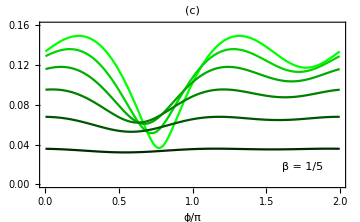

Non-classicality-functional-Wnep-complex-lambda-full-2D-high.pdf

Non-classicality-functional-Wnep-complex-lambda-full-2D-high.png

Non-classicality-functional-Wnep-complex-lambda-full-2D-high.eps

```mathematica
ClearAll[τ,r12I,r12R,ρ12I,ρ12R,ϕ12,β,ω,ωe,ωs,Δ,λ1,ℏ,g]

Print["Parameters:"]

Print["Maximum coherence in the system initial state:"]
CoherenceSMax=√(ρ11(1-ρ11))
CoherenceSMaxN=CoherenceSMax/.ρ11->1/4

parameters2={ℏ->1.,ρ11->1/4,ωe->1,ωs->4,β->1/5,g->1}

Print["Maximum coherence λmax in the ancilla:"]
λmax
λmaxN=(λmax)/.parameters2

Print["Non-classicality functional of the non-energy-preserving Work:"]
Simplify[negqLM/.{ωs->ωe+Δ},Assumptions->constraints]

ClearAll[τ,temp,negqLMplot, functions,plot1d,labels]

temp=Simplify[negqLM/.parameters2,Assumptions->constraints]/.λ1->λmaxN

negqLMplot[r12R_,r12I_,t_]:=Chop[N[temp/.{ρ12R->r12R,ρ12I->r12I,τ->t}]]
negqLMplot[ρ12R,ρ12I,τ]

ClearAll[functions,plot1d,labels]
nτ=6;
τmax=π/6;
functions=Table[
(r=CoherenceSMaxN;
τ=(nτ-n+1)/nτ*τmax;
N[negqLMplot[r*Cos[ϕ π],r*Sin[ϕ π],τ]]
),{n,1,nτ}];
labels=Table["τ = "<>ToString[1.*(nτ-n+1)/nτ*τmax ],{n,1,nτ}];
MatrixForm[labels]
labels2=Table[τmax*(nτ-n+1)/nτ,{n,1,nτ}]
 labels3={"τ = π/6","τ = (5 π)/36 ","τ = π/9","τ = π/12","τ = π/18","τ = π/36"}
legenda=LineLegend[labels3,LabelStyle->{FontSize->18,FontFamily->"Times"}];
colors=Table[RGBColor[0,(nτ-n+1)/nτ,0],{n,1,nτ}]

plot1d=Plot[
functions,{ϕ,0,2 },
PlotRange->{{0,2},{0,0.16}},
Frame->True,
FrameLabel->{"ϕ/π",None},
PlotLabel->"(c)",
PlotLegends->legenda,
PlotStyle->colors,
BaseStyle->{FontFamily->"Times",FontSize->20},
Epilog->{Inset[Framed["β = 1/5"],Offset[{0,0},{1.75,0.018}],Background->White]},
ImageSize->Medium]

Export["Non-classicality-functional-Wnep-complex-lambda-full-2D-high.pdf",plot1d]
Export["Non-classicality-functional-Wnep-complex-lambda-full-2D-high.png",plot1d,ImageResolution->200]
Export["Non-classicality-functional-Wnep-complex-lambda-full-2D-high.eps",plot1d]
```

## 7a. Expectation Values, Second Moments and Variances AT RESONANCE

### System Energy Exchange at resonance

```mathematica
ClearAll[AverageΔESqres,SquareΔESq,VarΔESqres]

Print["Quasiprobabilities of ΔES at resonance:"]
MatrixForm[Simplify[vecqΔES/.{ωs->ω,ωe->ω},Assumptions->constraints]]

Print["System energy differences:"]
vecΔES

Print["Average of ΔES at resonance:"]
AverageΔESqres=Simplify[(vecΔES.vecqΔES)/.{ωs->ω,ωe->ω},Assumptions->constraints]

Print["Compared to theoretical value of ΔES:"]
Simplify[AverageΔESTHEO/.{ωs->ω,ωe->ω},Assumptions->constraints]

Print["Second moment of ΔES:"]
SquareΔESq=Simplify[((vecΔES^2).vecqΔES)/.{ωs->ω,ωe->ω},Assumptions->constraints]

Print["Variance of ΔES:"]
VarΔESqres=Simplify[(SquareΔESq-AverageΔESqres^2)/.{ωs->ω,ωe->ω},Assumptions->constraints]
```

Quasiprobabilities of ΔES at resonance:

((ⅇ^(β ω ℏ) g ρ11+2 ⅇ^(-1/2 β ω ℏ) √(ⅇ^(β ω ℏ)) g ρ11+ⅇ^(β ω ℏ) g ρ11 Cos[(√(g^2) π)/18]-(1+ⅇ^(β ω ℏ)) √(g^2) λ1 (ρ12I-ⅈ ρ12R) Sin[(√(g^2) π)/18])/(2 (1+ⅇ^(β ω ℏ)) g)
-(Sin[(√(g^2) π)/36] ((1+ⅇ^(β ω ℏ)) √(g^2) λ1 (ρ12I+ⅈ ρ12R) Cos[(√(g^2) π)/36]+g (-1+ρ11) Sin[(√(g^2) π)/36]))/((1+ⅇ^(β ω ℏ)) g)
(Sin[(√(g^2) π)/36] ((1+ⅇ^(β ω ℏ)) √(g^2) λ1 (ρ12I-ⅈ ρ12R) Cos[(√(g^2) π)/36]+ⅇ^(β ω ℏ) g ρ11 Sin[(√(g^2) π)/36]))/((1+ⅇ^(β ω ℏ)) g)
-((1+2 ⅇ^((β ω ℏ)/2) √(ⅇ^(β ω ℏ))) g (-1+ρ11)+g (-1+ρ11) Cos[(√(g^2) π)/18]-(1+ⅇ^(β ω ℏ)) √(g^2) λ1 (ρ12I+ⅈ ρ12R) Sin[(√(g^2) π)/18])/(2 (1+ⅇ^(β ω ℏ)) g))

System energy differences:

{0,ωs ℏ,-ωs ℏ,0}

Average of ΔES at resonance:

-(ω ℏ Sin[(√(g^2) π)/36] (2 (1+ⅇ^(β ω ℏ)) √(g^2) λ1 ρ12I Cos[(√(g^2) π)/36]+g (-1+ρ11+ⅇ^(β ω ℏ) ρ11) Sin[(√(g^2) π)/36]))/((1+ⅇ^(β ω ℏ)) g)

Compared to theoretical value of ΔES:

-(ω ℏ Sin[(√(g^2) π)/36] (2 (1+ⅇ^(β ω ℏ)) g λ1 ρ12I Cos[(√(g^2) π)/36]+√(g^2) (-1+ρ11+ⅇ^(β ω ℏ) ρ11) Sin[(√(g^2) π)/36]))/((1+ⅇ^(β ω ℏ)) √(g^2))

Second moment of ΔES:

(ω^2 ℏ^2 Sin[(√(g^2) π)/36] (-2 ⅈ (1+ⅇ^(β ω ℏ)) √(g^2) λ1 ρ12R Cos[(√(g^2) π)/36]+g (1+(-1+ⅇ^(β ω ℏ)) ρ11) Sin[(√(g^2) π)/36]))/((1+ⅇ^(β ω ℏ)) g)

Variance of ΔES:

(ω^2 ℏ^2 Sin[(√(g^2) π)/36] (-Sin[(√(g^2) π)/36] (2 (1+ⅇ^(β ω ℏ)) √(g^2) λ1 ρ12I Cos[(√(g^2) π)/36]+g (-1+ρ11+ⅇ^(β ω ℏ) ρ11) Sin[(√(g^2) π)/36])^2+(1+ⅇ^(β ω ℏ)) g (-2 ⅈ (1+ⅇ^(β ω ℏ)) √(g^2) λ1 ρ12R Cos[(√(g^2) π)/36]+g (1+(-1+ⅇ^(β ω ℏ)) ρ11) Sin[(√(g^2) π)/36])))/((1+ⅇ^(β ω ℏ))^2 g^2)

### Ancilla Energy Exchange at resonance

```mathematica
ClearAll[AverageΔEAqres,SquareΔEAq,VarΔEAqres]

Print["Quasiprobabilities of ΔEA at resonance:"]
MatrixForm[Simplify[vecqΔEA/.{ωs->ω,ωe->ω},Assumptions->constraints]]

Print["Ancilla energy differences:"]
vecΔEA

Print["Average of ΔEA at resonance:"]
AverageΔEAqres=Simplify[(vecΔEA.vecqΔEA)/.{ωs->ω,ωe->ω},Assumptions->constraints]

Print["Compared to theoretical value of ΔEA:"]
Simplify[AverageΔEATHEO/.{ωs->ω,ωe->ω},Assumptions->constraints]

Print["Second moment of ΔEA:"]
SquareΔEAq=Simplify[((vecΔEA^2).vecqΔEA)/.{ωs->ω,ωe->ω},Assumptions->constraints]

Print["Variance of ΔEA:"]
VarΔEAqres=Simplify[(SquareΔEAq-AverageΔEAqres^2)/.{ωs->ω,ωe->ω},Assumptions->constraints]
```

Quasiprobabilities of ΔEA at resonance:

((g-g ρ11+2 ⅇ^(-1/2 β ω ℏ) √(ⅇ^(β ω ℏ)) g ρ11-g (-1+ρ11) Cos[(√(g^2) π)/18]+(1+ⅇ^(β ω ℏ)) √(g^2) λ1 (ρ12I+ⅈ ρ12R) Sin[(√(g^2) π)/18])/(2 (1+ⅇ^(β ω ℏ)) g)
(Sin[(√(g^2) π)/36] ((1+ⅇ^(β ω ℏ)) √(g^2) λ1 (ρ12I-ⅈ ρ12R) Cos[(√(g^2) π)/36]+ⅇ^(β ω ℏ) g ρ11 Sin[(√(g^2) π)/36]))/((1+ⅇ^(β ω ℏ)) g)
-(Sin[(√(g^2) π)/36] ((1+ⅇ^(β ω ℏ)) √(g^2) λ1 (ρ12I+ⅈ ρ12R) Cos[(√(g^2) π)/36]+g (-1+ρ11) Sin[(√(g^2) π)/36]))/((1+ⅇ^(β ω ℏ)) g)
(ⅇ^((β ω ℏ)/2) g (-2 √(ⅇ^(β ω ℏ)) (-1+ρ11)+ⅇ^((β ω ℏ)/2) ρ11)+ⅇ^(β ω ℏ) g ρ11 Cos[(√(g^2) π)/18]-(1+ⅇ^(β ω ℏ)) √(g^2) λ1 (ρ12I-ⅈ ρ12R) Sin[(√(g^2) π)/18])/(2 (1+ⅇ^(β ω ℏ)) g))

Ancilla energy differences:

{0,ωe ℏ,-ωe ℏ,0}

Average of ΔEA at resonance:

(ω ℏ Sin[(√(g^2) π)/36] (2 (1+ⅇ^(β ω ℏ)) √(g^2) λ1 ρ12I Cos[(√(g^2) π)/36]+g (-1+ρ11+ⅇ^(β ω ℏ) ρ11) Sin[(√(g^2) π)/36]))/((1+ⅇ^(β ω ℏ)) g)

Compared to theoretical value of ΔEA:

(ω ℏ Sin[(√(g^2) π)/36] (2 (1+ⅇ^(β ω ℏ)) g λ1 ρ12I Cos[(√(g^2) π)/36]+√(g^2) (-1+ρ11+ⅇ^(β ω ℏ) ρ11) Sin[(√(g^2) π)/36]))/((1+ⅇ^(β ω ℏ)) √(g^2))

Second moment of ΔEA:

(ω^2 ℏ^2 Sin[(√(g^2) π)/36] (-2 ⅈ (1+ⅇ^(β ω ℏ)) √(g^2) λ1 ρ12R Cos[(√(g^2) π)/36]+g (1+(-1+ⅇ^(β ω ℏ)) ρ11) Sin[(√(g^2) π)/36]))/((1+ⅇ^(β ω ℏ)) g)

Variance of ΔEA:

(ω^2 ℏ^2 Sin[(√(g^2) π)/36] (-Sin[(√(g^2) π)/36] (2 (1+ⅇ^(β ω ℏ)) √(g^2) λ1 ρ12I Cos[(√(g^2) π)/36]+g (-1+ρ11+ⅇ^(β ω ℏ) ρ11) Sin[(√(g^2) π)/36])^2+(1+ⅇ^(β ω ℏ)) g (-2 ⅈ (1+ⅇ^(β ω ℏ)) √(g^2) λ1 ρ12R Cos[(√(g^2) π)/36]+g (1+(-1+ⅇ^(β ω ℏ)) ρ11) Sin[(√(g^2) π)/36])))/((1+ⅇ^(β ω ℏ))^2 g^2)

### Incoherent Heat Exchange at resonance, from the side of the Ancilla

```mathematica
ClearAll[AverageQAqres,SquareQAq,VarQAqres]

Print["Quasiprobabilities of QA at resonance:"]
MatrixForm[Simplify[vecqQA/.{ωs->ω,ωe->ω},Assumptions->constraints]]

Print["Ancilla energy differences:"]
vecΔEA

Print["Average of QA at resonance:"]
AverageQAqres=Simplify[(vecΔEA.vecqQA)/.{ωs->ω,ωe->ω},Assumptions->constraints]

Print["Compared to theoretical value of QA:"]
Simplify[AverageQATHEO/.{ωs->ω,ωe->ω},Assumptions->constraints]

Print["Second moment of QA:"]
SquareQAq=Simplify[((vecΔEA^2).vecqQA)/.{ωs->ω,ωe->ω},Assumptions->constraints]

Print["Variance of QA:"]
VarQAqres=Simplify[(SquareQAq-AverageQAqres^2)/.{ωs->ω,ωe->ω},Assumptions->constraints]
```

Quasiprobabilities of QA at resonance:

((1+(-1+2 ⅇ^(-1/2 β ω ℏ) √(ⅇ^(β ω ℏ))) ρ11-(-1+ρ11) Cos[(√(g^2) π)/18])/(2 (1+ⅇ^(β ω ℏ)))
(ⅇ^(β ω ℏ) ρ11 Sin[(√(g^2) π)/36]^2)/(1+ⅇ^(β ω ℏ))
-((-1+ρ11) Sin[(√(g^2) π)/36]^2)/(1+ⅇ^(β ω ℏ))
(ⅇ^((β ω ℏ)/2) (-2 √(ⅇ^(β ω ℏ)) (-1+ρ11)+ⅇ^((β ω ℏ)/2) ρ11+ⅇ^((β ω ℏ)/2) ρ11 Cos[(√(g^2) π)/18]))/(2 (1+ⅇ^(β ω ℏ))))

Ancilla energy differences:

{0,ωe ℏ,-ωe ℏ,0}

Average of QA at resonance:

((-1+ρ11+ⅇ^(β ω ℏ) ρ11) ω ℏ Sin[(√(g^2) π)/36]^2)/(1+ⅇ^(β ω ℏ))

Compared to theoretical value of QA:

((-1+ρ11+ⅇ^(β ω ℏ) ρ11) ω ℏ Sin[(√(g^2) π)/36]^2)/(1+ⅇ^(β ω ℏ))

Second moment of QA:

((1+(-1+ⅇ^(β ω ℏ)) ρ11) ω^2 ℏ^2 Sin[(√(g^2) π)/36]^2)/(1+ⅇ^(β ω ℏ))

Variance of QA:

-(ω^2 ℏ^2 Sin[(√(g^2) π)/36]^2 (-1-ⅇ^(β ω ℏ)+ρ11-ⅇ^(2 β ω ℏ) ρ11+(-1+ρ11+ⅇ^(β ω ℏ) ρ11)^2 Sin[(√(g^2) π)/36]^2))/((1+ⅇ^(β ω ℏ))^2)

### Incoherent Heat Exchange at resonance, from the side of the System

```mathematica
ClearAll[AverageQSqres,SquareQSq,VarQSqres]

Print["Quasiprobabilities of QS at resonance:"]
MatrixForm[Simplify[vecqQS/.{ωs->ω,ωe->ω},Assumptions->constraints]]

Print["System energy differences:"]
vecΔES

Print["Average of QS at resonance:"]
AverageQSqres=Simplify[(vecΔES.vecqQS)/.{ωs->ω,ωe->ω},Assumptions->constraints]

Print["Compared to theoretical value of QS:"]
Simplify[AverageQSTHEO/.{ωs->ω,ωe->ω},Assumptions->constraints]

Print["Second moment of QS:"]
SquareQSq=Simplify[((vecΔES^2).vecqQS)/.{ωs->ω,ωe->ω},Assumptions->constraints]

Print["Variance of QS:"]
VarQSqres=Simplify[(SquareQSq-AverageQSqres^2)/.{ωs->ω,ωe->ω},Assumptions->constraints]
```

Quasiprobabilities of QS at resonance:

((ⅇ^(β ω ℏ) ρ11+2 ⅇ^(-1/2 β ω ℏ) √(ⅇ^(β ω ℏ)) ρ11+ⅇ^(β ω ℏ) ρ11 Cos[(√(g^2) π)/18])/(2+2 ⅇ^(β ω ℏ))
-((-1+ρ11) Sin[(√(g^2) π)/36]^2)/(1+ⅇ^(β ω ℏ))
(ⅇ^(β ω ℏ) ρ11 Sin[(√(g^2) π)/36]^2)/(1+ⅇ^(β ω ℏ))
-((-1+ρ11) (1+2 ⅇ^((β ω ℏ)/2) √(ⅇ^(β ω ℏ))+Cos[(√(g^2) π)/18]))/(2 (1+ⅇ^(β ω ℏ))))

System energy differences:

{0,ωs ℏ,-ωs ℏ,0}

Average of QS at resonance:

-((-1+ρ11+ⅇ^(β ω ℏ) ρ11) ω ℏ Sin[(√(g^2) π)/36]^2)/(1+ⅇ^(β ω ℏ))

Compared to theoretical value of QS:

-((-1+ρ11+ⅇ^(β ω ℏ) ρ11) ω ℏ Sin[(√(g^2) π)/36]^2)/(1+ⅇ^(β ω ℏ))

Second moment of QS:

((1+(-1+ⅇ^(β ω ℏ)) ρ11) ω^2 ℏ^2 Sin[(√(g^2) π)/36]^2)/(1+ⅇ^(β ω ℏ))

Variance of QS:

-(ω^2 ℏ^2 Sin[(√(g^2) π)/36]^2 (-1-ⅇ^(β ω ℏ)+ρ11-ⅇ^(2 β ω ℏ) ρ11+(-1+ρ11+ⅇ^(β ω ℏ) ρ11)^2 Sin[(√(g^2) π)/36]^2))/((1+ⅇ^(β ω ℏ))^2)

### Coherent Work Exchange at resonance, from the side of the Ancilla

```mathematica
ClearAll[AverageWcAqres,SquareWcAq,VarWcAqres]

Print["Pseudo-Quasiprobabilities of WcA at resonance:"]
MatrixForm[Simplify[vecqWcA/.{ωs->ω,ωe->ω},Assumptions->constraints]]

Print["Ancilla energy differences:"]
vecΔEA

Print["Average of WcA at resonance:"]
AverageWcAqres=Simplify[(vecΔEA.vecqWcA)/.{ωs->ω,ωe->ω},Assumptions->constraints]

Print["Compared to theoretical value of WcA:"]
Simplify[AverageWcATHEO/.{ωs->ω,ωe->ω},Assumptions->constraints]

Print["Second moment of WcA:"]
SquareWcAq=Simplify[((vecΔEA^2).vecqWcA)/.{ωs->ω,ωe->ω},Assumptions->constraints]

Print["Variance of WcA:"]
VarWcAqres=Simplify[(SquareWcAq-AverageWcAqres^2)/.{ωs->ω,ωe->ω},Assumptions->constraints]
```

Pseudo-Quasiprobabilities of WcA at resonance:

((g λ1 (ρ12I+ⅈ ρ12R) Sin[(√(g^2) π)/18])/(2 √(g^2))
(g λ1 (ρ12I-ⅈ ρ12R) Sin[(√(g^2) π)/18])/(2 √(g^2))
-(g λ1 (ρ12I+ⅈ ρ12R) Sin[(√(g^2) π)/18])/(2 √(g^2))
-(g λ1 (ρ12I-ⅈ ρ12R) Sin[(√(g^2) π)/18])/(2 √(g^2)))

Ancilla energy differences:

{0,ωe ℏ,-ωe ℏ,0}

Average of WcA at resonance:

(g λ1 ρ12I ω ℏ Sin[(√(g^2) π)/18])/(√(g^2))

Compared to theoretical value of WcA:

(g^3 λ1 ρ12I ω ℏ Sin[(√(g^2) π)/18])/((g^2)^(3/2))

Second moment of WcA:

-(ⅈ g λ1 ρ12R ω^2 ℏ^2 Sin[(√(g^2) π)/18])/(√(g^2))

Variance of WcA:

-(λ1 ω^2 ℏ^2 Sin[(√(g^2) π)/18] (ⅈ g ρ12R+√(g^2) λ1 ρ12I^2 Sin[(√(g^2) π)/18]))/(√(g^2))

### Coherent Work Exchange at resonance, from the side of the System

```mathematica
ClearAll[AverageWcSqres,SquareWcSq,VarWcSqres]

Print["Pseudo-Quasiprobabilities of WcS at resonance:"]
MatrixForm[Simplify[vecqWcS/.{ωs->ω,ωe->ω},Assumptions->constraints]]

Print["System energy differences:"]
vecΔES

Print["Average of WcS at resonance:"]
AverageWcSqres=Simplify[(vecΔES.vecqWcS)/.{ωs->ω,ωe->ω},Assumptions->constraints]

Print["Compared to theoretical value of WcS:"]
Simplify[AverageWcSTHEO/.{ωs->ω,ωe->ω},Assumptions->constraints]

Print["Second moment of WcS:"]
SquareWcSq=Simplify[((vecΔES^2).vecqWcS)/.{ωs->ω,ωe->ω},Assumptions->constraints]

Print["Variance of WcS:"]
VarWcSqres=Simplify[(SquareWcSq-AverageWcSqres^2)/.{ωs->ω,ωe->ω},Assumptions->constraints]
```

Pseudo-Quasiprobabilities of WcS at resonance:

(-(g λ1 (ρ12I-ⅈ ρ12R) Sin[(√(g^2) π)/18])/(2 √(g^2))
-(g λ1 (ρ12I+ⅈ ρ12R) Sin[(√(g^2) π)/18])/(2 √(g^2))
(g λ1 (ρ12I-ⅈ ρ12R) Sin[(√(g^2) π)/18])/(2 √(g^2))
(g λ1 (ρ12I+ⅈ ρ12R) Sin[(√(g^2) π)/18])/(2 √(g^2)))

System energy differences:

{0,ωs ℏ,-ωs ℏ,0}

Average of WcS at resonance:

-(g λ1 ρ12I ω ℏ Sin[(√(g^2) π)/18])/(√(g^2))

Compared to theoretical value of WcS:

-(g^3 λ1 ρ12I ω ℏ Sin[(√(g^2) π)/18])/((g^2)^(3/2))

Second moment of WcS:

-(ⅈ g λ1 ρ12R ω^2 ℏ^2 Sin[(√(g^2) π)/18])/(√(g^2))

Variance of WcS:

-(λ1 ω^2 ℏ^2 Sin[(√(g^2) π)/18] (ⅈ g ρ12R+√(g^2) λ1 ρ12I^2 Sin[(√(g^2) π)/18]))/(√(g^2))

## 7b. Expectation Values, Second Moments and Variances OFF RESONANCE

### System Energy Exchange OFF resonance

```mathematica
ClearAll[AverageΔESqnonres,SquareΔESq,VarΔESqnonres]

Print["Quasiprobabilities of ΔES OFF resonance:"]
vecqΔES//MatrixForm

Print["System energy differences:"]
vecΔES

Print["Average of ΔES OFF resonance:"]
AverageΔESqnonres=FullSimplify[(vecΔES.vecqΔES),Assumptions->constraints]

Print["Compared to theoretical value of ΔES:"]
Simplify[AverageΔESTHEO,Assumptions->constraints]

Print["Second moment of ΔES:"]
SquareΔESq=Simplify[((vecΔES^2).vecqΔES),Assumptions->constraints]

Print["Variance of ΔES:"]
VarΔESqnonres=Simplify[(SquareΔESq-AverageΔESqnonres^2),Assumptions->constraints]
```

Quasiprobabilities of ΔES OFF resonance:

((ⅇ^(-1/2 β ωe ℏ) √(ⅇ^(β ωe ℏ)) ρ11 (4 g^2+(ωe-ωs)^2)+ⅇ^(β ωe ℏ) (2 g^2 ρ11-ⅈ g λ1 (ρ12I-ⅈ ρ12R) (ωe-ωs)+ρ11 (ωe-ωs)^2)-ⅈ g λ1 (ρ12I-ⅈ ρ12R) (ωe-ωs)+g (ⅇ^(β ωe ℏ) (2 g ρ11+λ1 (ⅈ ρ12I+ρ12R) (ωe-ωs))+λ1 (ⅈ ρ12I+ρ12R) (ωe-ωs)) Cos[1/36 π √(4 g^2+(ωe-ωs)^2)]-(1+ⅇ^(β ωe ℏ)) g λ1 (ρ12I-ⅈ ρ12R) √(4 g^2+(ωe-ωs)^2) Sin[1/36 π √(4 g^2+(ωe-ωs)^2)])/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))
-(2 g Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] ((1+ⅇ^(β ωe ℏ)) λ1 (ρ12I+ⅈ ρ12R) √(4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+(2 g (-1+ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 (-ⅈ ρ12I+ρ12R) (ωe-ωs)) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))
(2 g Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] ((1+ⅇ^(β ωe ℏ)) λ1 (ρ12I-ⅈ ρ12R) √(4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+(ⅇ^(β ωe ℏ) (2 g ρ11+λ1 (ⅈ ρ12I+ρ12R) (ωe-ωs))+λ1 (ⅈ ρ12I+ρ12R) (ωe-ωs)) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))
(-2 (1+2 ⅇ^((β ωe ℏ)/2) √(ⅇ^(β ωe ℏ))) g^2 (-1+ρ11)+(1+ⅇ^(β ωe ℏ)) g λ1 (-ⅈ ρ12I+ρ12R) (ωe-ωs)-(1+ⅇ^((β ωe ℏ)/2) √(ⅇ^(β ωe ℏ))) (-1+ρ11) (ωe-ωs)^2+g (-2 g (-1+ρ11)+ⅈ (1+ⅇ^(β ωe ℏ)) λ1 (ρ12I+ⅈ ρ12R) (ωe-ωs)) Cos[1/36 π √(4 g^2+(ωe-ωs)^2)]+(1+ⅇ^(β ωe ℏ)) g λ1 (ρ12I+ⅈ ρ12R) √(4 g^2+(ωe-ωs)^2) Sin[1/36 π √(4 g^2+(ωe-ωs)^2)])/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)))

System energy differences:

{0,ωs ℏ,-ωs ℏ,0}

Average of ΔES OFF resonance:

-(4 g ωs ℏ Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] ((1+ⅇ^(β ωe ℏ)) λ1 ρ12I √(4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+(g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))

Compared to theoretical value of ΔES:

-(4 g ωs ℏ Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] ((1+ⅇ^(β ωe ℏ)) λ1 ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+(g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) √(4 g^2+(ωe-ωs)^2) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)^(3/2))

Second moment of ΔES:

(4 g ωs^2 ℏ^2 Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] (-ⅈ (1+ⅇ^(β ωe ℏ)) λ1 ρ12R √(4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+(g (1+(-1+ⅇ^(β ωe ℏ)) ρ11)+ⅈ (1+ⅇ^(β ωe ℏ)) λ1 ρ12I (ωe-ωs)) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))

Variance of ΔES:

1/((1+ⅇ^(β ωe ℏ))^2 (4 g^2+(ωe-ωs)^2)^2)4 g ωs^2 ℏ^2 Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] ((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2) (-ⅈ (1+ⅇ^(β ωe ℏ)) λ1 ρ12R √(4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+(g (1+(-1+ⅇ^(β ωe ℏ)) ρ11)+ⅈ (1+ⅇ^(β ωe ℏ)) λ1 ρ12I (ωe-ωs)) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)])-4 g Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] ((1+ⅇ^(β ωe ℏ)) λ1 ρ12I √(4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+(g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)])^2)

### Ancilla Energy Exchange OFF resonance

```mathematica
ClearAll[AverageΔEAqnonres,SquareΔEAq,VarΔEAqnonres]

Print["Quasiprobabilities of ΔEA OFF resonance:"]
vecqΔEA//MatrixForm

Print["Ancilla energy differences:"]
vecΔEA

Print["Average of ΔEA OFF resonance:"]
AverageΔEAqnonres=Simplify[(vecΔEA.vecqΔEA),Assumptions->constraints]

Print["Compared to theoretical value of ΔEA:"]
Simplify[AverageΔEATHEO,Assumptions->constraints]

Print["Second moment of ΔEA:"]
SquareΔEAq=Simplify[((vecΔEA^2).vecqΔEA),Assumptions->constraints]

Print["Variance of ΔEA:"]
VarΔEAqnonres=Simplify[(SquareΔEAq-AverageΔEAqnonres^2),Assumptions->constraints]
```

Quasiprobabilities of ΔEA OFF resonance:

((-2 g^2 (-1+ρ11)+ⅇ^(-1/2 β ωe ℏ) √(ⅇ^(β ωe ℏ)) ρ11 (4 g^2+(ωe-ωs)^2)+(1+ⅇ^(β ωe ℏ)) g λ1 (-ⅈ ρ12I+ρ12R) (ωe-ωs)-(-1+ρ11) (ωe-ωs)^2+g (-2 g (-1+ρ11)+ⅈ (1+ⅇ^(β ωe ℏ)) λ1 (ρ12I+ⅈ ρ12R) (ωe-ωs)) Cos[1/36 π √(4 g^2+(ωe-ωs)^2)]+(1+ⅇ^(β ωe ℏ)) g λ1 (ρ12I+ⅈ ρ12R) √(4 g^2+(ωe-ωs)^2) Sin[1/36 π √(4 g^2+(ωe-ωs)^2)])/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))
(2 g Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] ((1+ⅇ^(β ωe ℏ)) λ1 (ρ12I-ⅈ ρ12R) √(4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+(ⅇ^(β ωe ℏ) (2 g ρ11+λ1 (ⅈ ρ12I+ρ12R) (ωe-ωs))+λ1 (ⅈ ρ12I+ρ12R) (ωe-ωs)) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))
-(2 g Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] ((1+ⅇ^(β ωe ℏ)) λ1 (ρ12I+ⅈ ρ12R) √(4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+(2 g (-1+ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 (-ⅈ ρ12I+ρ12R) (ωe-ωs)) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))
(ⅇ^((β ωe ℏ)/2) (g^2 (-4 √(ⅇ^(β ωe ℏ)) (-1+ρ11)+2 ⅇ^((β ωe ℏ)/2) ρ11)-(√(ⅇ^(β ωe ℏ)) (-1+ρ11)-ⅇ^((β ωe ℏ)/2) ρ11) (ωe-ωs)^2)+g (ⅇ^(β ωe ℏ) (2 g ρ11+λ1 (ⅈ ρ12I+ρ12R) (ωe-ωs))+λ1 (ⅈ ρ12I+ρ12R) (ωe-ωs)) Cos[1/36 π √(4 g^2+(ωe-ωs)^2)]-ⅈ (1+ⅇ^(β ωe ℏ)) g λ1 (ρ12I-ⅈ ρ12R) (ωe-ωs-ⅈ √(4 g^2+(ωe-ωs)^2) Sin[1/36 π √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)))

Ancilla energy differences:

{0,ωe ℏ,-ωe ℏ,0}

Average of ΔEA OFF resonance:

(4 g ωe ℏ Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] ((1+ⅇ^(β ωe ℏ)) λ1 ρ12I √(4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+(g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))

Compared to theoretical value of ΔEA:

(4 g ωe ℏ Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] ((1+ⅇ^(β ωe ℏ)) λ1 ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+(g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) √(4 g^2+(ωe-ωs)^2) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)^(3/2))

Second moment of ΔEA:

(4 g ωe^2 ℏ^2 Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] (-ⅈ (1+ⅇ^(β ωe ℏ)) λ1 ρ12R √(4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+(g (1+(-1+ⅇ^(β ωe ℏ)) ρ11)+ⅈ (1+ⅇ^(β ωe ℏ)) λ1 ρ12I (ωe-ωs)) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))

Variance of ΔEA:

1/((1+ⅇ^(β ωe ℏ))^2 (4 g^2+(ωe-ωs)^2)^2)4 g ωe^2 ℏ^2 Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] ((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2) (-ⅈ (1+ⅇ^(β ωe ℏ)) λ1 ρ12R √(4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+(g (1+(-1+ⅇ^(β ωe ℏ)) ρ11)+ⅈ (1+ⅇ^(β ωe ℏ)) λ1 ρ12I (ωe-ωs)) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)])-4 g Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] ((1+ⅇ^(β ωe ℏ)) λ1 ρ12I √(4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+(g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)])^2)

### Incoherent Heat Exchange OFF resonance, from the side of the Ancilla

```mathematica
ClearAll[AverageQAqnonres,SquareQAq,VarQAqnonres]

Print["Quasiprobabilities of QA OFF resonance:"]
MatrixForm[vecqQA]

Print["Ancilla energy differences:"]
vecΔEA

Print["Average of QA OFF resonance:"]
AverageQAqnonres=Simplify[(vecΔEA.vecqQA),Assumptions->constraints]

Print["Compared to theoretical value of QA:"]
AverageQATHEO

Print["Second moment of QA:"]
SquareQAq=Simplify[((vecΔEA^2).vecqQA),Assumptions->constraints]

Print["Variance of QA:"]
VarQAqnonres=Simplify[(SquareQAq-AverageQAqnonres^2),Assumptions->constraints]
```

Quasiprobabilities of QA OFF resonance:

((ⅇ^(-1/2 β ωe ℏ) (-ⅇ^((β ωe ℏ)/2) (-1+ρ11) (2 g^2+(ωe-ωs)^2)+√(ⅇ^(β ωe ℏ)) ρ11 (4 g^2+(ωe-ωs)^2)-2 ⅇ^((β ωe ℏ)/2) g^2 (-1+ρ11) Cos[1/36 π √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))
-(2 ⅇ^(β ωe ℏ) g^2 ρ11 (-1+Cos[1/36 π √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))
(2 g^2 (-1+ρ11) (-1+Cos[1/36 π √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))
(ⅇ^((β ωe ℏ)/2) (g^2 (-4 √(ⅇ^(β ωe ℏ)) (-1+ρ11)+2 ⅇ^((β ωe ℏ)/2) ρ11)-(√(ⅇ^(β ωe ℏ)) (-1+ρ11)-ⅇ^((β ωe ℏ)/2) ρ11) (ωe-ωs)^2+2 ⅇ^((β ωe ℏ)/2) g^2 ρ11 Cos[1/36 π √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)))

Ancilla energy differences:

{0,ωe ℏ,-ωe ℏ,0}

Average of QA OFF resonance:

-(2 g^2 (-1+ρ11+ⅇ^(β ωe ℏ) ρ11) ωe ℏ (-1+Cos[1/36 π √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))

Compared to theoretical value of QA:

-(2 g^2 (-1+ρ11+ⅇ^(β ωe ℏ) ρ11) ωe ℏ (-1+Cos[1/36 π √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))

Second moment of QA:

-(2 g^2 (1+(-1+ⅇ^(β ωe ℏ)) ρ11) ωe^2 ℏ^2 (-1+Cos[1/36 π √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))

Variance of QA:

(2 g^2 ωe^2 ℏ^2 (-(1+ⅇ^(β ωe ℏ)) (1+(-1+ⅇ^(β ωe ℏ)) ρ11) (4 g^2+(ωe-ωs)^2)-2 g^2 (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)^2 (-1+Cos[1/36 π √(4 g^2+(ωe-ωs)^2)])) (-1+Cos[1/36 π √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ))^2 (4 g^2+(ωe-ωs)^2)^2)

### Incoherent Heat Exchange OFF resonance, from the side of the System

```mathematica
ClearAll[AverageQSqnonres,SquareQSq,VarQSqnonres]

Print["Quasiprobabilities of QS OFF resonance:"]
MatrixForm[vecqQS]

Print["System energy differences:"]
vecΔES

Print["Average of QS OFF resonance:"]
AverageQSqnonres=Simplify[(vecΔES.vecqQS),Assumptions->constraints]

Print["Compared to theoretical value of QS:"]
Simplify[AverageQSTHEO,Assumptions->constraints]

Print["Second moment of QS:"]
SquareQSq=Simplify[((vecΔES^2).vecqQS),Assumptions->constraints]

Print["Variance of QS:"]
VarQSqnonres=Simplify[(SquareQSq-AverageQSqnonres^2),Assumptions->constraints]
```

Quasiprobabilities of QS OFF resonance:

((ⅇ^(-1/2 β ωe ℏ) ρ11 (ⅇ^((3 β ωe ℏ)/2) (2 g^2+(ωe-ωs)^2)+√(ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)+2 ⅇ^((3 β ωe ℏ)/2) g^2 Cos[1/36 π √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))
(2 g^2 (-1+ρ11) (-1+Cos[1/36 π √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))
-(2 ⅇ^(β ωe ℏ) g^2 ρ11 (-1+Cos[1/36 π √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))
-((-1+ρ11) ((2+4 ⅇ^((β ωe ℏ)/2) √(ⅇ^(β ωe ℏ))) g^2+(1+ⅇ^((β ωe ℏ)/2) √(ⅇ^(β ωe ℏ))) (ωe-ωs)^2+2 g^2 Cos[1/36 π √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)))

System energy differences:

{0,ωs ℏ,-ωs ℏ,0}

Average of QS OFF resonance:

(2 g^2 (-1+ρ11+ⅇ^(β ωe ℏ) ρ11) ωs ℏ (-1+Cos[1/36 π √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))

Compared to theoretical value of QS:

(2 g^2 (-1+ρ11+ⅇ^(β ωe ℏ) ρ11) ωs ℏ (-1+Cos[1/36 π √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))

Second moment of QS:

-(2 g^2 (1+(-1+ⅇ^(β ωe ℏ)) ρ11) ωs^2 ℏ^2 (-1+Cos[1/36 π √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))

Variance of QS:

(2 g^2 ωs^2 ℏ^2 (-(1+ⅇ^(β ωe ℏ)) (1+(-1+ⅇ^(β ωe ℏ)) ρ11) (4 g^2+(ωe-ωs)^2)-2 g^2 (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)^2 (-1+Cos[1/36 π √(4 g^2+(ωe-ωs)^2)])) (-1+Cos[1/36 π √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ))^2 (4 g^2+(ωe-ωs)^2)^2)

### Coherent Work Exchange OFF resonance, from the side of the Ancilla

```mathematica
ClearAll[AverageWcAqnonres,SquareWcAq,VarWcAqnonres]

Print["Pseudo-Quasiprobabilities of WcA at resonance:"]
MatrixForm[vecqWcA]

Print["Ancilla energy differences:"]
vecΔEA

Print["Average of WcA OFF resonance:"]
AverageWcAqnonres=Simplify[(vecΔEA.vecqWcA),Assumptions->constraints]

Print["Compared to theoretical value of WcA:"]
AverageWcATHEO

Print["Second moment of WcA:"]
SquareWcAq=Simplify[((vecΔEA^2).vecqWcA),Assumptions->constraints]

Print["Variance of WcA:"]
VarWcAqnonres=Simplify[(SquareWcAq-AverageWcAqnonres^2),Assumptions->constraints]
```

Pseudo-Quasiprobabilities of WcA at resonance:

((2 g λ1 (ρ12I+ⅈ ρ12R) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] ((4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]-ⅈ √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))
(2 g λ1 (ρ12I-ⅈ ρ12R) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] ((4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+ⅈ √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))
-(2 g λ1 (ρ12I+ⅈ ρ12R) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] ((4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]-ⅈ √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))
-(2 g λ1 (ρ12I-ⅈ ρ12R) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] ((4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+ⅈ √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2)))

Ancilla energy differences:

{0,ωe ℏ,-ωe ℏ,0}

Average of WcA OFF resonance:

(4 g λ1 ωe ℏ Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] (ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+ρ12R √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))

Compared to theoretical value of WcA:

(2 g λ1 ωe ℏ (2 ρ12R √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)]^2+ρ12I (4 g^2+(ωe-ωs)^2) Sin[1/36 π √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))

Second moment of WcA:

-(4 ⅈ g λ1 ωe^2 ℏ^2 Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] (ρ12R (4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+ρ12I √(4 g^2+(ωe-ωs)^2) (-ωe+ωs) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))

Variance of WcA:

4 g λ1 ωe^2 ℏ^2 Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] (-(4 g λ1 Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] (ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+ρ12R √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)])^2)/((4 g^2+(ωe-ωs)^2)^3)-(ⅈ (ρ12R (4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+ρ12I √(4 g^2+(ωe-ωs)^2) (-ωe+ωs) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2)))

### Coherent Work Exchange OFF resonance, from the side of the System

```mathematica
ClearAll[AverageWcSqnonres,SquareWcSq,VarWcSqnonres]

Print["Pseudo-Quasiprobabilities of WcS OFF resonance:"]
MatrixForm[vecqWcS]

Print["System energy differences:"]
vecΔES

Print["Average of WcS OFF resonance:"]
AverageWcSqnonres=Simplify[(vecΔES.vecqWcS),Assumptions->constraints]

Print["Compared to theoretical value of WcS:"]
AverageWcSTHEO

Print["Second moment of WcS:"]
SquareWcSq=Simplify[((vecΔES^2).vecqWcS),Assumptions->constraints]

Print["Variance of WcS:"]
VarWcSqnonres=Simplify[(SquareWcSq-AverageWcSqnonres^2),Assumptions->constraints]
```

Pseudo-Quasiprobabilities of WcS OFF resonance:

(-(2 g λ1 (ρ12I-ⅈ ρ12R) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] ((4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+ⅈ √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))
-(2 g λ1 (ρ12I+ⅈ ρ12R) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] ((4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]-ⅈ √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))
(2 g λ1 (ρ12I-ⅈ ρ12R) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] ((4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+ⅈ √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))
(2 g λ1 (ρ12I+ⅈ ρ12R) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] ((4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]-ⅈ √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2)))

System energy differences:

{0,ωs ℏ,-ωs ℏ,0}

Average of WcS OFF resonance:

-(4 g λ1 ωs ℏ Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] (ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+ρ12R √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))

Compared to theoretical value of WcS:

-(4 g λ1 ωs ℏ Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] (ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+ρ12R √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))

Second moment of WcS:

-(4 ⅈ g λ1 ωs^2 ℏ^2 Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] (ρ12R (4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+ρ12I √(4 g^2+(ωe-ωs)^2) (-ωe+ωs) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))

Variance of WcS:

4 g λ1 ωs^2 ℏ^2 Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] (-(4 g λ1 Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] (ρ12I (4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+ρ12R √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)])^2)/((4 g^2+(ωe-ωs)^2)^3)-(ⅈ (ρ12R (4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+ρ12I √(4 g^2+(ωe-ωs)^2) (-ωe+ωs) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2)))

### Non-energy-preserving Work Wnep (aka LM) - Only relevant OFF RESONANCE

```mathematica
ClearAll[LM]

Qlm//MatrixForm

Print["Check - Quasiprobabilities Qlm at resonance:"]
Simplify[Qlm/.{ωe->ω,ωs->ω},Assumptions->constraints]//MatrixForm

Print["Values of Mechanical work:"]
lm=Table[Simplify[values[[f]]-values[[i]]],{i,1,4},{f,1,4}];
MatrixForm[lm]

Print["Expectation value of Mechanical Work LM:"]
LM=Simplify[Sum[Qlm[[i,f]]*lm[[i,f]],{i,1,4},{f,1,4}],Assumptions->constraints]

Print["Theoretical exact average mechanical work LM:"]
LMtheo

Print["Check that the QP expectation value matches with the theoretical one (LM-LMtheo):"]
LMtheo-LM//FullSimplify

Print["Check: LM = ΔES + ΔEA:"]
LM-(AverageΔESqnonres+AverageΔEAqnonres)//FullSimplify

Print["Check - Mechanical Work LM in the resonant case:"]
Simplify[(Sum[Qlm[[i,f]]*lm[[i,f]],{i,1,4},{f,1,4}])/.{ωe->ω,ωs->ω},Assumptions->constraints]

Print["Second moment:"]
SquareLMq=Simplify[Sum[Qlm[[i,f]]*(lm[[i,f]])^2,{i,1,4},{f,1,4}],Assumptions->constraints]

Print["Variance of Mechanical Work LM:"]
VarLM=Simplify[SquareLMq-LM^2,Assumptions->constraints]

Print["Check - Variance of Mechanical Work LM in the resonant case:"]
Simplify[VarLM/.{ωe->ω,ωs->ω},Assumptions->constraints]
```

(-(ⅇ^(β ωe ℏ) (-1+ρ11))/(1+ⅇ^(β ωe ℏ)) | 0 | 0 | 0
0 | ((ⅈ (-1+ρ11) √(4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+(2 (1+ⅇ^(β ωe ℏ)) g λ1 (-ⅈ ρ12I+ρ12R)-(-1+ρ11) (ωe-ωs)) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)]) (ⅈ √(4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+(ωe-ωs) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)) | (2 g Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] (-(2 g (-1+ρ11) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)])/(1+ⅇ^(β ωe ℏ))+ⅈ λ1 (ρ12I+ⅈ ρ12R) (ⅈ √(4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+(ωe-ωs) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)])))/(4 g^2+(ωe-ωs)^2) | 0
0 | (2 g Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] (λ1 (ρ12I-ⅈ ρ12R) √(4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+((ⅇ^(β ωe ℏ) (2 g ρ11+λ1 (ⅈ ρ12I+ρ12R) (ωe-ωs))+λ1 (ⅈ ρ12I+ρ12R) (ωe-ωs)) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)])/(1+ⅇ^(β ωe ℏ))))/(4 g^2+(ωe-ωs)^2) | ((ⅈ ⅇ^(β ωe ℏ) ρ11 √(4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+(-2 ⅈ (1+ⅇ^(β ωe ℏ)) g λ1 (ρ12I-ⅈ ρ12R)+ⅇ^(β ωe ℏ) ρ11 (ωe-ωs)) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)]) (-ⅈ √(4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+(ωe-ωs) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2)) | 0
0 | 0 | 0 | ρ11/(1+ⅇ^(β ωe ℏ)))

Check - Quasiprobabilities Qlm at resonance:

(-(ⅇ^(β ω ℏ) (-1+ρ11))/(1+ⅇ^(β ω ℏ)) | 0 | 0 | 0
0 | -(Cos[(√(g^2) π)/36] (√(g^2) (-1+ρ11) Cos[(√(g^2) π)/36]-(1+ⅇ^(β ω ℏ)) g λ1 (ρ12I+ⅈ ρ12R) Sin[(√(g^2) π)/36]))/((1+ⅇ^(β ω ℏ)) √(g^2)) | (Sin[(√(g^2) π)/36] (-2 √(g^2) λ1 (ρ12I+ⅈ ρ12R) Cos[(√(g^2) π)/36]-(2 g (-1+ρ11) Sin[(√(g^2) π)/36])/(1+ⅇ^(β ω ℏ))))/(2 g) | 0
0 | (Sin[(√(g^2) π)/36] (2 √(g^2) λ1 (ρ12I-ⅈ ρ12R) Cos[(√(g^2) π)/36]+(2 ⅇ^(β ω ℏ) g ρ11 Sin[(√(g^2) π)/36])/(1+ⅇ^(β ω ℏ))))/(2 g) | (Cos[(√(g^2) π)/36] (ⅇ^(β ω ℏ) √(g^2) ρ11 Cos[(√(g^2) π)/36]-(1+ⅇ^(β ω ℏ)) g λ1 (ρ12I-ⅈ ρ12R) Sin[(√(g^2) π)/36]))/((1+ⅇ^(β ω ℏ)) √(g^2)) | 0
0 | 0 | 0 | ρ11/(1+ⅇ^(β ω ℏ)))

Values of Mechanical work:

(0 | ωe ℏ | ωs ℏ | (ωe+ωs) ℏ
-ωe ℏ | 0 | (-ωe+ωs) ℏ | ωs ℏ
-ωs ℏ | (ωe-ωs) ℏ | 0 | ωe ℏ
-(ωe+ωs) ℏ | -ωs ℏ | -ωe ℏ | 0)

Expectation value of Mechanical Work LM:

(4 g (ωe-ωs) ℏ Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] ((1+ⅇ^(β ωe ℏ)) λ1 ρ12I √(4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+(g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))

Theoretical exact average mechanical work LM:

(2 g (ωe-ωs) ℏ (g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)+(-g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)-(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) Cos[1/36 π √(4 g^2+(ωe-ωs)^2)]+(1+ⅇ^(β ωe ℏ)) λ1 ρ12I √(4 g^2+(ωe-ωs)^2) Sin[1/36 π √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))

Check that the QP expectation value matches with the theoretical one (LM-LMtheo):

0

Check: LM = ΔES + ΔEA:

0

Check - Mechanical Work LM in the resonant case:

0

Second moment:

(4 g (ωe-ωs)^2 ℏ^2 Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] (-ⅈ (1+ⅇ^(β ωe ℏ)) λ1 ρ12R √(4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+(g (1+(-1+ⅇ^(β ωe ℏ)) ρ11)+ⅈ (1+ⅇ^(β ωe ℏ)) λ1 ρ12I (ωe-ωs)) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))

Variance of Mechanical Work LM:

1/((1+ⅇ^(β ωe ℏ))^2 (4 g^2+(ωe-ωs)^2)^2)4 g (ωe-ωs)^2 ℏ^2 Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] ((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2) (-ⅈ (1+ⅇ^(β ωe ℏ)) λ1 ρ12R √(4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+(g (1+(-1+ⅇ^(β ωe ℏ)) ρ11)+ⅈ (1+ⅇ^(β ωe ℏ)) λ1 ρ12I (ωe-ωs)) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)])-4 g Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] ((1+ⅇ^(β ωe ℏ)) λ1 ρ12I √(4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+(g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)])^2)

Check - Variance of Mechanical Work LM in the resonant case:

0

## 7c. FIGURE 3

### Fig. 3(a): δES OFF-resonance

{ωs∈Reals,ωs>0,ωe∈Reals,ωe>0,ω∈Reals,ω>0,β∈Reals,β>0,τse∈Reals,τse>0,τ∈Reals,τ>0,τ1∈Reals,τ1>0,Jse∈Reals,Jse>0,g∈Reals,g>0,g1∈Reals,g1>0,ρ11∈Reals,ρ11≥0,ρ11≤1,ρ12R∈Reals,ρ12I∈Reals,ℏ∈Reals,ℏ>0,ωs1∈Reals,ωs1>0,β1∈Reals,β1>0,True,True,True,ϕ∈Reals,λ1∈Reals}

Maximum coherence in the system initial state:

√((1-ρ11) ρ11)

(√3)/4

Plots with λ = λmax

√(1/((ⅇ^(-1/2 β ωe ℏ)+ⅇ^((β ωe ℏ)/2))^2))

0.0815356

pippo is just δES rewritten using Δ = ωs - ωe

-(4 g (Δ+ωe) ℏ Sin[1/72 π √(4 g^2+Δ^2)] ((1+ⅇ^(β ωe ℏ)) √(4 g^2+Δ^2) λ1 ρ12I Cos[1/72 π √(4 g^2+Δ^2)]+(g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)-(1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12R) Sin[1/72 π √(4 g^2+Δ^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+Δ^2))

Auxiliary functions: cβ, τ1[Δ,τ], a[Δ], b[Δ], θ[Δ]

1+ⅇ^(β ωe ℏ)

√(4 g^2+Δ^2) τ

(1+ⅇ^(β ωe ℏ)) √(4 g^2+Δ^2) λ1 ρ12I

g (-1+(1+ⅇ^(β ωe ℏ)) ρ11)-(1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12R

ArcTan[(g (-1+(1+ⅇ^(β ωe ℏ)) ρ11)-(1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12R)/((1+ⅇ^(β ωe ℏ)) √(4 g^2+Δ^2) λ1 ρ12I)]

pippo2 is still just an exact rewriting of pippo i.e. δES with auxiliary functions:

(2 g (Δ+ωe) ℏ (g (1-(1+ⅇ^(β ωe ℏ)) ρ11)+(1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12R+(g (-1+(1+ⅇ^(β ωe ℏ)) ρ11)-(1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12R) Cos[√(4 g^2+Δ^2) τ]-(1+ⅇ^(β ωe ℏ)) √(4 g^2+Δ^2) λ1 ρ12I Sin[√(4 g^2+Δ^2) τ]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+Δ^2))

Check that the rewriting is correct (check = 0 if correct):

(4 g (Δ+ωe) ℏ Sin[1/72 √(4 g^2+Δ^2) (π-36 τ)] ((1+ⅇ^(β ωe ℏ)) √(4 g^2+Δ^2) λ1 ρ12I Cos[1/72 √(4 g^2+Δ^2) (π+36 τ)]+(g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)-(1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12R) Sin[1/72 √(4 g^2+Δ^2) (π+36 τ)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+Δ^2))

Exact rewriting of δES with auxiliary functions and using trigonometric identities:

(2 g (Δ+ωe) ℏ (g (1-(1+ⅇ^(β ωe ℏ)) ρ11)+(1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12R-√((1+ⅇ^(β ωe ℏ))^2 (4 g^2+Δ^2) λ1^2 ρ12I^2+(g (-1+(1+ⅇ^(β ωe ℏ)) ρ11)-(1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12R)^2) Sin[√(4 g^2+Δ^2) τ-ArcTan[(g (-1+(1+ⅇ^(β ωe ℏ)) ρ11)-(1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12R)/((1+ⅇ^(β ωe ℏ)) √(4 g^2+Δ^2) λ1 ρ12I)]]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+Δ^2))

pippo4Upper majorises pippo3, by setting the only oscillating cosine to -1:

(2 g (g (1-(1+ⅇ^(β ωe ℏ)) ρ11)+(1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12R+√((1+ⅇ^(β ωe ℏ))^2 (4 g^2+Δ^2) λ1^2 ρ12I^2+(g (-1+(1+ⅇ^(β ωe ℏ)) ρ11)-(1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12R)^2)) (Δ+ωe) ℏ)/((1+ⅇ^(β ωe ℏ)) (4 g^2+Δ^2))

pippo4Lower majorises pippo3, by setting the only oscillating cosine to +1:

(2 g (g (1-(1+ⅇ^(β ωe ℏ)) ρ11)+(1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12R-√((1+ⅇ^(β ωe ℏ))^2 (4 g^2+Δ^2) λ1^2 ρ12I^2+(g (-1+(1+ⅇ^(β ωe ℏ)) ρ11)-(1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12R)^2)) (Δ+ωe) ℏ)/((1+ⅇ^(β ωe ℏ)) (4 g^2+Δ^2))

Exact Functions and upper and lower envelopes:

Maximum coherence:

-(4 (1+Δ) Sin[1/72 π √(4+Δ^2)] (0.0928272 √(4+Δ^2) Cos[1/72 π √(4+Δ^2)]+(-3/4+ⅇ/4-0.0928272 Δ) Sin[1/72 π √(4+Δ^2)]))/((1+ⅇ) (4+Δ^2))

(2 (1+Δ) (1+1/4 (-1-ⅇ)+0.0928272 Δ-√((-1+(1+ⅇ)/4-0.0928272 Δ)^2+0.00861689 (4+Δ^2)) Sin[1/6 π √(4+Δ^2)-ArcTan[(10.7727 (-1+(1+ⅇ)/4-0.0928272 Δ))/(√(4+Δ^2))]]))/((1+ⅇ) (4+Δ^2))

(2 (1+Δ) (1+1/4 (-1-ⅇ)+0.0928272 Δ+√((-1+(1+ⅇ)/4-0.0928272 Δ)^2+0.00861689 (4+Δ^2))))/((1+ⅇ) (4+Δ^2))

(2 (1+Δ) (1+1/4 (-1-ⅇ)+0.0928272 Δ-√((-1+(1+ⅇ)/4-0.0928272 Δ)^2+0.00861689 (4+Δ^2))))/((1+ⅇ) (4+Δ^2))

Some coherence:

-(4 (1+Δ) Sin[1/72 π √(4+Δ^2)] (0.0464136 √(4+Δ^2) Cos[1/72 π √(4+Δ^2)]+(-3/4+ⅇ/4-0.0464136 Δ) Sin[1/72 π √(4+Δ^2)]))/((1+ⅇ) (4+Δ^2))

(2 (1+Δ) (1+1/4 (-1-ⅇ)+0.0464136 Δ+√((-1+(1+ⅇ)/4-0.0464136 Δ)^2+0.00215422 (4+Δ^2))))/((1+ⅇ) (4+Δ^2))

(2 (1+Δ) (1+1/4 (-1-ⅇ)+0.0464136 Δ-√((-1+(1+ⅇ)/4-0.0464136 Δ)^2+0.00215422 (4+Δ^2))))/((1+ⅇ) (4+Δ^2))

Little coherence:

-(4 (1+Δ) Sin[1/72 π √(4+Δ^2)] (0.00928272 √(4+Δ^2) Cos[1/72 π √(4+Δ^2)]+(-3/4+ⅇ/4-0.00928272 Δ) Sin[1/72 π √(4+Δ^2)]))/((1+ⅇ) (4+Δ^2))

(2 (1+Δ) (1+1/4 (-1-ⅇ)+0.00928272 Δ+√((-1+(1+ⅇ)/4-0.00928272 Δ)^2+0.0000861689 (4+Δ^2))))/((1+ⅇ) (4+Δ^2))

(2 (1+Δ) (1+1/4 (-1-ⅇ)+0.00928272 Δ-√((-1+(1+ⅇ)/4-0.00928272 Δ)^2+0.0000861689 (4+Δ^2))))/((1+ⅇ) (4+Δ^2))

40

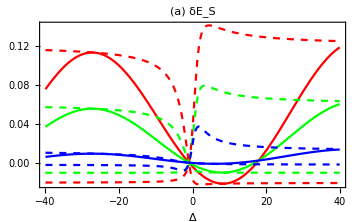

deltaES_VS_Delta.pdf

deltaES_VS_Delta.png

deltaES_VS_Delta.eps

```mathematica
ClearAll[ωs,ωe,λ1,ℏ,ρ11,ρ12R,ρ12I,β,g,τ,Δ,CoherenceSMax,CoherenceSMaxN,parameters4,λmaxN]

constraints={ωs∈Reals,ωs>0,ωe∈Reals,ωe>0,ω∈Reals,ω>0,β∈Reals,β>0,τse∈Reals,τse>0,τ∈Reals,τ>0,τ1∈Reals,τ1>0,Jse∈Reals,Jse>0,g∈Reals,g>0,g1∈Reals,g1>0,ρ11∈Reals,ρ11≥0,ρ11≤1,ρ12R∈Reals,ρ12I∈Reals,ℏ∈Reals,ℏ>0,ωs1∈Reals,ωs1>0,β1∈Reals,β1>0,r∈Reals,r>=0,r<=1,ϕ∈Reals,λ1∈Reals}

Print["Maximum coherence in the system initial state:"]
CoherenceSMax=√(ρ11(1-ρ11))
CoherenceSMaxN=CoherenceSMax/.ρ11->1/4

parameters4={ωe->1,ℏ->1,ρ11->1/4,ρ12R->CoherenceSMaxN/√2,ρ12I->CoherenceSMaxN/√2,β->1,g->1,λ1->2/10};

Print["Plots with λ = λmax"]
λmax
λmaxN=(λmax/.{ωs->ωe+Δ,β->5,g->1,ℏ->1,ρ11->1/4})/.{ωe->1.,Δ->3.}

ClearAll[cβ,τ1,a,b,θ,pippo,pippo2,pippo3,pippo4,Δ]

Print["pippo is just δES rewritten using Δ = ωs - ωe"]
pippo = Simplify[AverageΔESqnonres/.{ωs->ωe + Δ},Assumptions->constraints]

Print["Auxiliary functions: cβ, τ1[Δ,τ], a[Δ], b[Δ], θ[Δ]"]

cβ=(1+ⅇ^(β ωe ℏ))

τ1[δ_,t_]:=(√(4 g^2+Δ^2) τ)/.{Δ->δ,τ->t};
τ1[Δ,τ]

a[δ_]:=((1+ⅇ^(β ωe ℏ)) √(4 g^2+Δ^2) λ1 ρ12I)/.{Δ->δ};
a[δ_]:=(cβ √(4 g^2+Δ^2) λ1 ρ12I)/.{Δ->δ};
a[Δ]

b[δ_]:=(-g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)+(1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12R)/.{Δ->δ};
b[δ_]:=(g (ρ11*cβ-1)-cβ Δ λ1 ρ12R)/.{Δ->δ};
b[Δ]

θ[δ_]:=ArcTan[b[δ]/a[δ]];
θ[Δ]

Print[" pippo2 is still just an exact rewriting of pippo i.e. δES with auxiliary functions:"]
pippo2[δ_,t_]:=-(2 g (δ+ωe) ℏ (g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)-(1+ⅇ^(β ωe ℏ)) δ λ1 ρ12R-b[δ]* Cos[τ1[δ,t]]+a[δ]* Sin[τ1[δ,t]]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+δ^2));
pippo2[δ_,t_]:=(2 g (δ+ωe) ℏ (g (1-ρ11 cβ)+cβ δ λ1 ρ12R+b[δ]* Cos[τ1[δ,t]]-a[δ]* Sin[τ1[δ,t]]))/(cβ(4 g^2+δ^2));
pippo2[Δ,τ]
Print["Check that the rewriting is correct (check = 0 if correct):"]
FullSimplify[pippo2[Δ,τ]-pippo,Assumptions->constraints]

(* pippo3 is still just a rewriting of pippo i.e. ΔES with auxiliary functions *)
pippo3[δ_,t_]:=(2 g (δ+ωe) ℏ (g (1-ρ11 cβ)+cβ δ λ1 ρ12R-√(a[δ]^2+b[δ]^2)*Sin[τ1[δ,t]-θ[δ]]))/(cβ(4 g^2+δ^2));
Print["Exact rewriting of δES with auxiliary functions and using trigonometric identities:"]
pippo3[Δ,τ]

Print["pippo4Upper majorises pippo3, by setting the only oscillating cosine to -1:"]
pippo4Upper[δ_]:=(2 g (δ+ωe) ℏ (g (1-ρ11 cβ)+cβ δ λ1 ρ12R+√(a[δ]^2+b[δ]^2)))/((1+ⅇ^(β ωe ℏ)) (4 g^2+δ^2));
pippo4Upper[Δ]

Print["pippo4Lower majorises pippo3, by setting the only oscillating cosine to +1:"]
pippo4Lower[δ_]:=(2 g (δ+ωe) ℏ (g (1-ρ11 cβ)+cβ δ λ1 ρ12R-√(a[δ]^2+b[δ]^2)))/((1+ⅇ^(β ωe ℏ)) (4 g^2+δ^2));
pippo4Lower[Δ]

ClearAll[ϕ]
ClearAll[plotfunc1,plotfunc2,plotfunc3,upper1, upper2,upper3,lower1,lower2,lower3,parameters4,parameters5,parameters6]

parameters4={ωe->1,ℏ->1,ρ11->1/4,ρ12R->CoherenceSMaxN/√2,ρ12I->CoherenceSMaxN/√2,β->1,g->1,λ1->λmaxN};
parameters5={ωe->1,ℏ->1,ρ11->1/4,ρ12R->CoherenceSMaxN/(√2),ρ12I->CoherenceSMaxN/(√2),β->1,g->1,λ1->λmaxN/2};
parameters6={ωe->1,ℏ->1,ρ11->1/4,ρ12R->CoherenceSMaxN/(√2),ρ12I->CoherenceSMaxN/(√2),β->1,g->1,λ1->λmaxN/10};

Print["Exact Functions and upper and lower envelopes: "]

Print["Maximum coherence:"]
plotfunc1[x_]:=(pippo/.parameters4)/.{Δ->x,τ->π/6}
plotfunc1[Δ]
plotfunc1var[x_]:=(pippo3[x,π/6]/.parameters4)
plotfunc1var[Δ]
upper1[x_]:=(pippo4Upper[x]/.parameters4)/.{τ->π/6}
upper1[Δ]
lower1[x_]:=(pippo4Lower[x]/.parameters4)/.{τ->π/6}
lower1[Δ]

Print["Some coherence:"]
plotfunc2[x_]:=(pippo/.parameters5)/.{Δ->x,τ->π/6}
plotfunc2[Δ]
upper2[x_]:=(pippo4Upper[x]/.parameters5)/.{τ->π/6}
upper2[Δ]
lower2[x_]:=(pippo4Lower[x]/.parameters5)/.{τ->π/6}
lower2[Δ]

Print["Little coherence:"]
plotfunc3[x_]:=(pippo/.parameters6)/.{Δ->x,τ->π/6}
plotfunc3[Δ]
upper3[x_]:=(pippo4Upper[x]/.parameters6)/.{τ->π/6}
upper3[Δ]
lower3[x_]:=(pippo4Lower[x]/.parameters6)/.{τ->π/6}
lower3[Δ]

(* Combined plots *)
ClearAll[functions]

(*functions={plotfunc1[Δ],plotfunc2[Δ],plotfunc3[Δ],LimPiuN1,LimPiuN2,LimPiuN3,LimMenoN1,LimMenoN2,LimMenoN3};*)
functions={plotfunc1[Δ],plotfunc2[Δ],plotfunc3[Δ],upper1[Δ],upper2[Δ],upper3[Δ],lower1[Δ],lower2[Δ],lower3[Δ],};

styles={Red,Green,Blue,{Red,Dashed},{Green,Dashed},{Blue,Dashed},{Red,Dashed},{Green,Dashed},{Blue,Dashed}};

labels={"λ = λ_max","λ = λ_max/2","λ = λ_max/10",None,None,None,None,None,None};
legenda=LineLegend[labels,LabelStyle->{FontSize->18,FontFamily->"Times"}];

ΔMax=40

plotES=Plot[functions,{Δ,-ΔMax,ΔMax},
PlotRange->All,
Frame->True,
FrameLabel->{"Δ",None},
PlotLabel->"(a) δE_S",
PlotLegends->legenda,
PlotStyle->styles,
BaseStyle->{FontFamily->"Times",FontSize->18},
ImageSize->Medium]

Export["deltaES_VS_Delta.pdf",plotES]
Export["deltaES_VS_Delta.png",plotES,ImageResolution->200]
Export["deltaES_VS_Delta.eps",plotES]
```

### Fig. 3(b): Non-energy-preserving-work Wnep OFF-resonance

Wnep (aka LM for Lavoro Meccanico):

(4 g (ωe-ωs) ℏ Sin[1/72 π √(4 g^2+(ωe-ωs)^2)] ((1+ⅇ^(β ωe ℏ)) λ1 ρ12I √(4 g^2+(ωe-ωs)^2) Cos[1/72 π √(4 g^2+(ωe-ωs)^2)]+(g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)+(1+ⅇ^(β ωe ℏ)) λ1 ρ12R (ωe-ωs)) Sin[1/72 π √(4 g^2+(ωe-ωs)^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+(ωe-ωs)^2))

pippo5 is LM rewritten using Δ = ωs-ωe:

-(4 g Δ ℏ Sin[1/72 π √(4 g^2+Δ^2)] ((1+ⅇ^(β ωe ℏ)) √(4 g^2+Δ^2) λ1 ρ12I Cos[1/72 π √(4 g^2+Δ^2)]+(g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)-(1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12R) Sin[1/72 π √(4 g^2+Δ^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+Δ^2))

pippo6 is just a convenient and simplifyed rewriting of LM :

-(4 g Δ ℏ Sin[1/2 √(4 g^2+Δ^2) τ] ((1+ⅇ^(β ωe ℏ)) √(4 g^2+Δ^2) λ1 ρ12I Cos[1/2 √(4 g^2+Δ^2) τ]+(g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)-(1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12R) Sin[1/2 √(4 g^2+Δ^2) τ]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+Δ^2))

Check that pippo6 == pippo5 :

-(4 g Δ ℏ Sin[1/2 √(4 g^2+Δ^2) τ] ((1+ⅇ^(β ωe ℏ)) √(4 g^2+Δ^2) λ1 ρ12I Cos[1/2 √(4 g^2+Δ^2) τ]+(g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)-(1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12R) Sin[1/2 √(4 g^2+Δ^2) τ]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+Δ^2))==-(4 g Δ ℏ Sin[1/72 π √(4 g^2+Δ^2)] ((1+ⅇ^(β ωe ℏ)) √(4 g^2+Δ^2) λ1 ρ12I Cos[1/72 π √(4 g^2+Δ^2)]+(g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)-(1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12R) Sin[1/72 π √(4 g^2+Δ^2)]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+Δ^2))

Auxiliary functions: cβ, τ1[Δ,τ], a[Δ], b[Δ], θ[Δ]:

1+ⅇ^(β ωe ℏ)

√(4 g^2+Δ^2) τ

(1+ⅇ^(β ωe ℏ)) √(4 g^2+Δ^2) λ1 ρ12I

g (-1+(1+ⅇ^(β ωe ℏ)) ρ11)-(1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12R

ArcTan[(g (-1+(1+ⅇ^(β ωe ℏ)) ρ11)-(1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12R)/((1+ⅇ^(β ωe ℏ)) √(4 g^2+Δ^2) λ1 ρ12I)]

pippo7 is a rewriting of pippo6 using the cβ, τ1[Δ,τ], a[Δ] and b[δ] and θ functions:

-(4 g Δ ℏ Sin[1/2 √(4 g^2+Δ^2) τ] ((1+ⅇ^(β ωe ℏ)) √(4 g^2+Δ^2) λ1 ρ12I Cos[1/2 √(4 g^2+Δ^2) τ]+(g (-1+(1+ⅇ^(β ωe ℏ)) ρ11)-(1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12R) Sin[1/2 √(4 g^2+Δ^2) τ]))/((1+ⅇ^(β ωe ℏ)) (4 g^2+Δ^2))

Check that pippo7 == pippo6:

True

pippo8 is a rewriting of pippo7 exploiting trigonometric identities to obtain an expression with one single Cos[...] function:

-(4 g Δ √((1+ⅇ^(β ωe ℏ))^2 (4 g^2+Δ^2) λ1^2 ρ12I^2+(g (-1+(1+ⅇ^(β ωe ℏ)) ρ11)-(1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12R)^2) ℏ Cos[1/2 √(4 g^2+Δ^2) τ-ArcTan[(g (-1+(1+ⅇ^(β ωe ℏ)) ρ11)-(1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12R)/((1+ⅇ^(β ωe ℏ)) √(4 g^2+Δ^2) λ1 ρ12I)]] Sin[1/2 √(4 g^2+Δ^2) τ])/((1+ⅇ^(β ωe ℏ)) (4 g^2+Δ^2))

Coherence in the system:

√((1-ρ11) ρ11)

(√3)/4

λmax:

√(1/((ⅇ^(-1/2 β ωe ℏ)+ⅇ^((β ωe ℏ)/2))^2))

1/(1/ⅇ+ⅇ)

0.324027

Numerical check that pippo8-pippo7 ==0:

-3.46945×10^-18

As a function of τ:

Fixing the phase ϕ:

π/4

Maximum positive coherence

-(20 Sin[√101 τ] ((√(303/2) (1+ⅇ) Cos[√101 τ])/(2 (1/ⅇ+ⅇ))+(-3/4+ⅇ/4-(5 √(3/2) (1+ⅇ))/(1/ⅇ+ⅇ)) Sin[√101 τ]))/(101 (1+ⅇ))

Some positive coherence

-(20 Sin[√101 τ] ((√(303/2) (1+ⅇ) Cos[√101 τ])/(4 (1/ⅇ+ⅇ))+(-3/4+ⅇ/4-(5 √(3/2) (1+ⅇ))/(2 (1/ⅇ+ⅇ))) Sin[√101 τ]))/(101 (1+ⅇ))

Zero coherence

-(20 (-3/4+ⅇ/4) Sin[√101 τ]^2)/(101 (1+ⅇ))

Some negative coherence

-(20 Sin[√101 τ] (-(√(303/2) (1+ⅇ) Cos[√101 τ])/(4 (1/ⅇ+ⅇ))+(-3/4+ⅇ/4+(5 √(3/2) (1+ⅇ))/(2 (1/ⅇ+ⅇ))) Sin[√101 τ]))/(101 (1+ⅇ))

Maximum negative coherence

-(20 Sin[√101 τ] (-(√(303/2) (1+ⅇ) Cos[√101 τ])/(2 (1/ⅇ+ⅇ))+(-3/4+ⅇ/4+(5 √(3/2) (1+ⅇ))/(1/ⅇ+ⅇ)) Sin[√101 τ]))/(101 (1+ⅇ))

{RGBColor[1, 0, 0],RGBColor[Rational[3, 4], 0, Rational[1, 4]],RGBColor[Rational[1, 2], 0, Rational[1, 2]],RGBColor[Rational[1, 4], 0, Rational[3, 4]],RGBColor[0, 0, 1]}

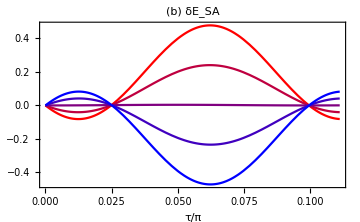

Legends:

(RGBColor[1, 0, 0] | λ = λ_max
RGBColor[Rational[3, 4], 0, Rational[1, 4]] | λ = λ_max/2
RGBColor[Rational[1, 2], 0, Rational[1, 2]] | λ = 0
RGBColor[Rational[1, 4], 0, Rational[3, 4]] | λ = -λ_max/2
RGBColor[0, 0, 1] | λ = -λ_max)

Wnep_VS_tau.pdf

Wnep_VS_tau.png

Wnep_VS_tau.eps

```mathematica
Print["Wnep (aka LM for Lavoro Meccanico):"]
LM

ClearAll[pippo5,pippo6,pippo7,pippo8,pippo9]

Print["pippo5 is LM rewritten using Δ = ωs-ωe:"]
pippo5 = Simplify[LM/.{ωs->ωe+Δ},Assumptions->constraints]

Print["pippo6 is just a convenient and simplifyed rewriting of LM :"]
pippo6=4 g Δ ℏ Sin[1/2 √(4 g^2+Δ^2) τ] (-((1+ⅇ^(β ωe ℏ))*λ1 ρ12I *√(4 g^2+Δ^2)*Cos[1/2 √(4 g^2+Δ^2) τ])/((4 g^2+Δ^2)(1+ⅇ^(β ωe ℏ)))-((g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)-(1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12R) Sin[1/2 √(4 g^2+Δ^2) τ])/((1+ⅇ^(β ωe ℏ)) (4 g^2+Δ^2)));
pippo6=-4 g Δ ℏ Sin[1/2 √(4 g^2+Δ^2) τ] ((1+ⅇ^(β ωe ℏ))*λ1 ρ12I *√(4 g^2+Δ^2)*Cos[1/2 √(4 g^2+Δ^2) τ]+(g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)-(1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12R) Sin[1/2 √(4 g^2+Δ^2) τ])/((1+ⅇ^(β ωe ℏ)) (4 g^2+Δ^2))

Print["Check that pippo6 == pippo5 :"]
Simplify[pippo6]==pippo5
Print[""]

ClearAll[cβ,τ1,a,b,θ]

Print["Auxiliary functions: cβ, τ1[Δ,τ], a[Δ], b[Δ], θ[Δ]:"]

cβ=(1+ⅇ^(β ωe ℏ))

τ1[δ_,t_]:=(√(4 g^2+Δ^2) τ)/.{Δ->δ,τ->t};
τ1[Δ,τ]

a[δ_]:=((1+ⅇ^(β ωe ℏ)) √(4 g^2+Δ^2) λ1 ρ12I)/.{Δ->δ};
a[δ_]:=(cβ λ1 ρ12I √(4 g^2+Δ^2) )/.{Δ->δ};
a[Δ]

b[δ_]:=(g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)-(1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12R)/.{Δ->δ};
b[δ_]:=(g (ρ11*cβ-1)-cβ Δ λ1 ρ12R)/.{Δ->δ};
b[Δ]

θ[δ_]:=ArcTan[b[δ]/a[δ]];
θ[Δ]

Print[""]
Print[" pippo7 is a rewriting of pippo6 using the cβ, τ1[Δ,τ], a[Δ] and b[δ] and θ functions: "]
pippo7=-4 g Δ ℏ Sin[τ1[Δ,τ]/2]*(a[Δ]*Cos[τ1[Δ,τ]/2]+b[Δ]*Sin[τ1[Δ,τ]/2])/(cβ(4 g^2+Δ^2))
Print["Check that pippo7 == pippo6:"]
Simplify[pippo7]==Simplify[pippo6]

Print["pippo8 is a rewriting of pippo7 exploiting trigonometric identities to obtain an expression with one single Cos[...] function:"]
pippo8=-4 g Δ ℏ Sin[τ1[Δ,τ]/2] (√(a[Δ]^2+b[Δ]^2)*Cos[τ1[Δ,τ]/2-θ[Δ]])/(cβ*(4 g^2+Δ^2))

(* parameters *)

ClearAll[ϕ,parameters4,parameters5,parameters6]

Print["Coherence in the system:"]
CoherenceSMax=√(ρ11(1-ρ11))
CoherenceSMaxN=CoherenceSMax/.ρ11->1/4

Print["λmax:"]
λmax
λmaxN=λmax/.{β->1,ℏ->1,ωe->2}
N[%]

parameters4={ωe->1,ℏ->1,τ->π/8,ρ11->1/4,β->1,g->1,λ1->λmaxN,r->CoherenceSMaxN,ϕ->π/6};
parameters5={ωe->1,ℏ->1,τ->π/6,ρ11->1/4,ρ12R->CoherenceSMaxN/(√2),ρ12I->CoherenceSMaxN/(√2),β->1,g->1,λ1->λmaxN/2};
parameters6={ωe->1,ℏ->1,τ->π/6,ρ11->1/4,ρ12R->CoherenceSMaxN/(√2),ρ12I->CoherenceSMaxN/(√2),β->1,g->1,λ1->λmaxN/10};

Print["Numerical check that pippo8-pippo7 ==0:"]
FullSimplify[N[((pippo8-pippo7/.parameters4)/.{ρ12R->r Cos[ϕ],ρ12I->r Sin[ϕ],Δ->1})/.parameters4]]

Print["As a function of τ:"]
ClearAll[τ,τmax,plotfunc7,parameters7,parameters8,parameters9,parameters10,parameters11]

Print["Fixing the phase ϕ:"]
ϕ1=π/4

Print["Maximum positive coherence"]
parameters7={ωe->1,ℏ->1,ρ11->1/4,β->1,g->1,λ1->λmaxN,r->CoherenceSMaxN,ϕ->ϕ1,Δ->20};
plotfunc7[x_]:=(((pippo6/.parameters7)/.{ρ12R->r*Cos[ϕ],ρ12I->r*Sin[ϕ]})/.parameters7)/.{τ->x}
plotfunc7[τ]

Print["Some positive coherence"]
parameters8={ωe->1,ℏ->1,ρ11->1/4,β->1,g->1,λ1->λmaxN/2,r->CoherenceSMaxN,ϕ->ϕ1,Δ->20};
plotfunc8[x_]:=(((pippo6/.parameters8)/.{ρ12R->r*Cos[ϕ],ρ12I->r*Sin[ϕ]})/.parameters8)/.{τ->x}
plotfunc8[τ]

Print["Zero coherence"]
parameters9={ωe->1,ℏ->1,ρ11->1/4,β->1,g->1,λ1->0,r->CoherenceSMaxN,ϕ->ϕ1,Δ->20};
plotfunc9[x_]:=(((pippo6/.parameters9)/.{ρ12R->r*Cos[ϕ],ρ12I->r*Sin[ϕ]})/.parameters9)/.{τ->x}
plotfunc9[τ]

Print["Some negative coherence"]
parameters10={ωe->1,ℏ->1,ρ11->1/4,β->1,g->1,λ1->-λmaxN/2,r->CoherenceSMaxN,ϕ->ϕ1,Δ->20};
plotfunc10[x_]:=(((pippo6/.parameters10)/.{ρ12R->r*Cos[ϕ],ρ12I->r*Sin[ϕ]})/.parameters10)/.{τ->x}
plotfunc10[τ]

Print["Maximum negative coherence"]
parameters11={ωe->1,ℏ->1,ρ11->1/4,β->1,g->1,λ1->-λmaxN,r->CoherenceSMaxN,ϕ->ϕ1,Δ->20};
plotfunc11[x_]:=(((pippo6/.parameters11)/.{ρ12R->r*Cos[ϕ],ρ12I->r*Sin[ϕ]})/.parameters11)/.{τ->x}
plotfunc11[τ]

(* Combined plots *)
ClearAll[functions]

functions={plotfunc7[τ*π],plotfunc8[τ*π],plotfunc9[τ*π],plotfunc10[τ*π],plotfunc11[τ*π]};

colors=Table[RGBColor[1-j/4,0,j/4],{j,0,4}]

labels={"λ = λ_max","λ = λ_max/2","λ = 0","λ = -λ_max/2","λ = -λ_max"};
legenda=LineLegend[labels,LabelStyle->{FontFamily->"Times",FontSize->18}];

τmax=1/9;(* x π *)

plotWnepTime=Plot[functions,{τ,0,τmax},
PlotRange->All,
Frame->True,
FrameLabel->{"τ/π",None},
PlotLabel->"(b) δE_SA",
PlotLegends->legenda,
PlotStyle->colors,
BaseStyle->{FontFamily->"Times",FontSize->18},
ImageSize->Medium]

Print["Legends:"]
MatrixForm[Transpose[{colors,labels}]]

Export["Wnep_VS_tau.pdf",plotWnepTime]
Export["Wnep_VS_tau.png",plotWnepTime,ImageResolution->200]
Export["Wnep_VS_tau.eps",plotWnepTime]
```

## 7d: FIGURE 4

### Fig. 4 (a): Variance of δES and of Wnep Out of Resonance as function of Δ

```mathematica
ClearAll[τN,parameters4, λmaxN,parameters4,CoherenceSMaxN]

τN=π/6;

Print["Coherence in the system:"]
CoherenceSMax=√(ρ11(1-ρ11))
CoherenceSMaxN=CoherenceSMax/.ρ11->1/4
parameters4={ℏ->1,ρ11->1/4,ρ12R->CoherenceSMaxN/√2,ρ12I->CoherenceSMaxN/√2,ωe->2,β->1,g->1,τ->τN};

Print["λmax:"]
λmax
λmaxN=λmax/.parameters4
N[%]

Print[" Variance of δES using Δ instead of ωs: "]
pippo=Simplify[VarΔESqnonres/.{ωs->ωe + Δ},Assumptions->constraints]

Print[" Variance of δES at resonance: "]
pippo0=Simplify[pippo/.{Δ->0},Assumptions->constraints]

Print[" Variance of δES with numerical parameters - numerical version of pippo: "]
temp4=(Simplify[VarΔESqnonres/.{ωs->ωe + Δ},Assumptions->constraints])/.parameters4

Print["Exact and numerical Functions for the Real Part of the Variance:"]
ClearAll[temp5e,temp5n,ExactFuncES,PlotFuncES]

temp5e=Simplify[ComplexExpand[Re[temp4]],Assumptions->constraints]
ExactFuncES[λ_,Δ1_]:=temp5e/.{λ1->λ,Δ->Δ1};

temp5n=Chop[ComplexExpand[Re[N[temp4]]]];
PlotFuncES[λ_,Δ1_]:=temp5n/.{λ1->λ,Δ->Δ1};
```

Coherence in the system:

√((1-ρ11) ρ11)

(√3)/4

λmax:

√(1/((ⅇ^(-1/2 β ωe ℏ)+ⅇ^((β ωe ℏ)/2))^2))

1/(1/ⅇ+ⅇ)

0.324027

Variance of δES using Δ instead of ωs:

1/((1+ⅇ^(β ωe ℏ))^2 (4 g^2+Δ^2)^2)4 g (Δ+ωe)^2 ℏ^2 Sin[1/72 π √(4 g^2+Δ^2)] ((1+ⅇ^(β ωe ℏ)) (4 g^2+Δ^2) (-ⅈ (1+ⅇ^(β ωe ℏ)) √(4 g^2+Δ^2) λ1 ρ12R Cos[1/72 π √(4 g^2+Δ^2)]+(g (1+(-1+ⅇ^(β ωe ℏ)) ρ11)-ⅈ (1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12I) Sin[1/72 π √(4 g^2+Δ^2)])-4 g Sin[1/72 π √(4 g^2+Δ^2)] ((1+ⅇ^(β ωe ℏ)) √(4 g^2+Δ^2) λ1 ρ12I Cos[1/72 π √(4 g^2+Δ^2)]+(g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)-(1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12R) Sin[1/72 π √(4 g^2+Δ^2)])^2)

Variance of δES at resonance:

(ωe^2 ℏ^2 Sin[(g π)/36] (-Sin[(g π)/36] (2 (1+ⅇ^(β ωe ℏ)) g λ1 ρ12I Cos[(g π)/36]+g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11) Sin[(g π)/36])^2+(1+ⅇ^(β ωe ℏ)) g (-2 ⅈ (1+ⅇ^(β ωe ℏ)) g λ1 ρ12R Cos[(g π)/36]+g (1+(-1+ⅇ^(β ωe ℏ)) ρ11) Sin[(g π)/36])))/((1+ⅇ^(β ωe ℏ))^2 g^2)

Variance of δES with numerical parameters - numerical version of pippo:

1/((1+ⅇ^2)^2 (4+Δ^2)^2)4 (2+Δ)^2 Sin[1/72 π √(4+Δ^2)] (-4 Sin[1/72 π √(4+Δ^2)] (1/4 √(3/2) (1+ⅇ^2) √(4+Δ^2) λ1 Cos[1/72 π √(4+Δ^2)]+(-3/4+ⅇ^2/4-1/4 √(3/2) (1+ⅇ^2) Δ λ1) Sin[1/72 π √(4+Δ^2)])^2+(1+ⅇ^2) (4+Δ^2) (-1/4 ⅈ √(3/2) (1+ⅇ^2) √(4+Δ^2) λ1 Cos[1/72 π √(4+Δ^2)]+(1+1/4 (-1+ⅇ^2)-1/4 ⅈ √(3/2) (1+ⅇ^2) Δ λ1) Sin[1/72 π √(4+Δ^2)]))

Exact and numerical Functions for the Real Part of the Variance:

1/(2 (1+ⅇ^2)^2 (4+Δ^2)^(5/2))(2+Δ)^2 Sin[1/72 π √(4+Δ^2)]^2 (√(4+Δ^2) (ⅇ^4 (7+√6 Δ λ1-6 λ1^2+Δ^2 (2-3 λ1^2))-3 (-5+√6 Δ λ1+2 λ1^2+Δ^2 (-2+λ1^2))-2 ⅇ^2 (-19+√6 Δ λ1+6 λ1^2+Δ^2 (-4+3 λ1^2)))-√(4+Δ^2) (-9-3 √6 Δ λ1+6 λ1^2+ⅇ^4 (-1+√6 Δ λ1+6 λ1^2)+ⅇ^2 (6-2 √6 Δ λ1+12 λ1^2)) Cos[1/36 π √(4+Δ^2)]+(1+ⅇ^2) (4+Δ^2) λ1 (-ⅇ^2 (√6-3 Δ λ1)+3 (√6+Δ λ1)) Sin[1/36 π √(4+Δ^2)])

```mathematica
ClearAll[τN,parameters4, λmaxN,parameters8,CoherenceSMaxN]
ClearAll[ExactFuncWnep,PlotFuncWnep,AbsReVarWnepExact]

τN=π/6;

Print["Coherence in the system:"]
CoherenceSMax=√(ρ11(1-ρ11))
CoherenceSMaxN=CoherenceSMax/.ρ11->1/4
parameters8={ℏ->1,ρ11->1/4,ρ12R->CoherenceSMaxN/√2,ρ12I->CoherenceSMaxN/√2,ωe->2,β->1,g->1,τ->τN};

Print["λmax:"]
λmax
λmaxN=λmax/.parameters8
N[%]

Print[" Variance of Wnep using Δ instead of ωs: "]
pippo=Simplify[VarLM/.{ωs->ωe + Δ},Assumptions->constraints]

Print[" Variance of Wnep with numerical parameters - numerical version of pippo: "]
temp8=(Simplify[VarLM/.{ωs->ωe + Δ},Assumptions->constraints])/.parameters8

Print["Exact and numerical Functions for the Real Part of the Variance:"]
ClearAll[temp9e,temp9n,ExactFuncWnep,PlotFuncWnep]

temp9e=Simplify[ComplexExpand[Re[temp8]],Assumptions->constraints]
ExactFuncWnep[λ_,Δ1_]:=temp9e/.{λ1->λ,Δ->Δ1};

temp9n=Chop[ComplexExpand[Re[N[temp8]]]];
PlotFuncWnep[λ_,Δ1_]:=temp9n/.{λ1->λ,Δ->Δ1};

Print["Abs[Re[Var]] normalized to the value of λ=0"]
pippo8=Simplify[Abs[ExactFuncWnep[λ1,Δ]/ExactFuncWnep[0,Δ]],Assumptions->constraints]

AbsReVarWnepExact[x_,y_]:=(pippo8/.parameters8)/.{λ1->x,Δ->y};
AbsReVarWnepExact[λ1,Δ]
AbsReVarWnepExact[0,Δ]
N[%]
```

Coherence in the system:

√((1-ρ11) ρ11)

(√3)/4

λmax:

√(1/((ⅇ^(-1/2 β ωe ℏ)+ⅇ^((β ωe ℏ)/2))^2))

1/(1/ⅇ+ⅇ)

0.324027

Variance of Wnep using Δ instead of ωs:

1/((1+ⅇ^(β ωe ℏ))^2 (4 g^2+Δ^2)^2)4 g Δ^2 ℏ^2 Sin[1/72 π √(4 g^2+Δ^2)] ((1+ⅇ^(β ωe ℏ)) (4 g^2+Δ^2) (-ⅈ (1+ⅇ^(β ωe ℏ)) √(4 g^2+Δ^2) λ1 ρ12R Cos[1/72 π √(4 g^2+Δ^2)]+(g (1+(-1+ⅇ^(β ωe ℏ)) ρ11)-ⅈ (1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12I) Sin[1/72 π √(4 g^2+Δ^2)])-4 g Sin[1/72 π √(4 g^2+Δ^2)] ((1+ⅇ^(β ωe ℏ)) √(4 g^2+Δ^2) λ1 ρ12I Cos[1/72 π √(4 g^2+Δ^2)]+(g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)-(1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12R) Sin[1/72 π √(4 g^2+Δ^2)])^2)

Variance of Wnep with numerical parameters - numerical version of pippo:

1/((1+ⅇ^2)^2 (4+Δ^2)^2)4 Δ^2 Sin[1/72 π √(4+Δ^2)] (-4 Sin[1/72 π √(4+Δ^2)] (1/4 √(3/2) (1+ⅇ^2) √(4+Δ^2) λ1 Cos[1/72 π √(4+Δ^2)]+(-3/4+ⅇ^2/4-1/4 √(3/2) (1+ⅇ^2) Δ λ1) Sin[1/72 π √(4+Δ^2)])^2+(1+ⅇ^2) (4+Δ^2) (-1/4 ⅈ √(3/2) (1+ⅇ^2) √(4+Δ^2) λ1 Cos[1/72 π √(4+Δ^2)]+(1+1/4 (-1+ⅇ^2)-1/4 ⅈ √(3/2) (1+ⅇ^2) Δ λ1) Sin[1/72 π √(4+Δ^2)]))

Exact and numerical Functions for the Real Part of the Variance:

1/(2 (1+ⅇ^2)^2 (4+Δ^2)^(5/2))Δ^2 Sin[1/72 π √(4+Δ^2)]^2 (√(4+Δ^2) (ⅇ^4 (7+√6 Δ λ1-6 λ1^2+Δ^2 (2-3 λ1^2))-3 (-5+√6 Δ λ1+2 λ1^2+Δ^2 (-2+λ1^2))-2 ⅇ^2 (-19+√6 Δ λ1+6 λ1^2+Δ^2 (-4+3 λ1^2)))-√(4+Δ^2) (-9-3 √6 Δ λ1+6 λ1^2+ⅇ^4 (-1+√6 Δ λ1+6 λ1^2)+ⅇ^2 (6-2 √6 Δ λ1+12 λ1^2)) Cos[1/36 π √(4+Δ^2)]+(1+ⅇ^2) (4+Δ^2) λ1 (-ⅇ^2 (√6-3 Δ λ1)+3 (√6+Δ λ1)) Sin[1/36 π √(4+Δ^2)])

Abs[Re[Var]] normalized to the value of λ=0

Abs[(√(4+Δ^2) (ⅇ^4 (7+√6 Δ λ1-6 λ1^2+Δ^2 (2-3 λ1^2))-3 (-5+√6 Δ λ1+2 λ1^2+Δ^2 (-2+λ1^2))-2 ⅇ^2 (-19+√6 Δ λ1+6 λ1^2+Δ^2 (-4+3 λ1^2)))-√(4+Δ^2) (-9-3 √6 Δ λ1+6 λ1^2+ⅇ^4 (-1+√6 Δ λ1+6 λ1^2)+ⅇ^2 (6-2 √6 Δ λ1+12 λ1^2)) Cos[1/36 π √(4+Δ^2)]+(1+ⅇ^2) (4+Δ^2) λ1 (-ⅇ^2 (√6-3 Δ λ1)+3 (√6+Δ λ1)) Sin[1/36 π √(4+Δ^2)])/(√(4+Δ^2) (15+6 Δ^2+ⅇ^4 (7+2 Δ^2)+ⅇ^2 (38+8 Δ^2)+(-3+ⅇ^2)^2 Cos[1/36 π √(4+Δ^2)]))]

Abs[(√(4+Δ^2) (ⅇ^4 (7+√6 Δ λ1-6 λ1^2+Δ^2 (2-3 λ1^2))-3 (-5+√6 Δ λ1+2 λ1^2+Δ^2 (-2+λ1^2))-2 ⅇ^2 (-19+√6 Δ λ1+6 λ1^2+Δ^2 (-4+3 λ1^2)))-√(4+Δ^2) (-9-3 √6 Δ λ1+6 λ1^2+ⅇ^4 (-1+√6 Δ λ1+6 λ1^2)+ⅇ^2 (6-2 √6 Δ λ1+12 λ1^2)) Cos[1/36 π √(4+Δ^2)]+(1+ⅇ^2) (4+Δ^2) λ1 (-ⅇ^2 (√6-3 Δ λ1)+3 (√6+Δ λ1)) Sin[1/36 π √(4+Δ^2)])/(√(4+Δ^2) (15+6 Δ^2+ⅇ^4 (7+2 Δ^2)+ⅇ^2 (38+8 Δ^2)+(-3+ⅇ^2)^2 Cos[1/36 π √(4+Δ^2)]))]

Abs[(√(4+Δ^2) (-2 ⅇ^2 (-19-4 Δ^2)-3 (-5-2 Δ^2)+ⅇ^4 (7+2 Δ^2))-(-9+6 ⅇ^2-ⅇ^4) √(4+Δ^2) Cos[1/36 π √(4+Δ^2)])/(√(4+Δ^2) (15+6 Δ^2+ⅇ^4 (7+2 Δ^2)+ⅇ^2 (38+8 Δ^2)+(-3+ⅇ^2)^2 Cos[1/36 π √(4+Δ^2)]))]

Abs[(√(4.+Δ^2) (-14.7781 (-19.-4. Δ^2)-3. (-5.-2. Δ^2)+54.5982 (7.+2. Δ^2))+19.2638 √(4.+Δ^2) Cos[0.0872665 √(4.+Δ^2)])/(√(4.+Δ^2) (15.+6. Δ^2+54.5982 (7.+2. Δ^2)+7.38906 (38.+8. Δ^2)+19.2638 Cos[0.0872665 √(4.+Δ^2)]))]

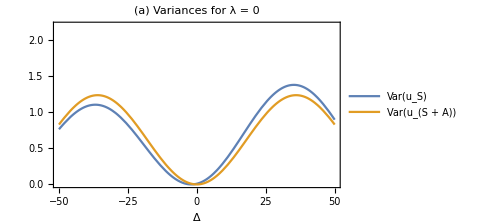

Variance_deltaES_Wnep_VS_Delta_no_coherence.pdf

Variance_deltaES_Wnep_VS_Delta_no_coherence.png

Variance_deltaES_Wnep_VS_Delta_no_coherence.eps

```mathematica
ClearAll[plot7,legenda]

legenda=LineLegend[{"Var(u_S)","Var(u_(S + A))"},LabelStyle->{FontSize->20,FontFamily->"Times"}];

plot7=Plot[
{PlotFuncES[0,Δ],PlotFuncWnep[0,Δ]},{Δ,-50,50},
PlotRange->{Automatic,{0,2.2}},
Frame->True,
FrameLabel->{"Δ",None},
PlotLabel->"(a) Variances for λ = 0",
BaseStyle->{FontFamily->"Times",FontSize->20},
PlotLegends->legenda,
ImageSize->Medium
]

Export["Variance_deltaES_Wnep_VS_Delta_no_coherence.pdf",plot7]
Export["Variance_deltaES_Wnep_VS_Delta_no_coherence.png",plot7,ImageResolution->200]
Export["Variance_deltaES_Wnep_VS_Delta_no_coherence.eps",plot7]
```

### Fig. 4 (b): Variance of δES Out of Resonance as a function of λ for various Δ

```mathematica
ClearAll[maxima,Δ,x]

Print["Maxima of the Variance as a function of Δ:"]
maxima=Table[Maximize[{PlotFuncES[0,Δ],10.*i<Δ<10.*(i+1)},Δ∈Reals],{i,-3,2}]
maxima[[1]]
maxima[[1,2]]

ClearAll[CoherenceSMaxN,parameters6,λmaxN]
ClearAll[Δ,VarNonRes2,ReVarNonRes,ReVarNonResFunc]

Print["Coherence in the system:"]
CoherenceSMax
CoherenceSMaxN=CoherenceSMax/.ρ11->1/4

parameters6={g->1,β->1,ℏ->1,τ->π/6,ρ11->1/4,ρ12R->CoherenceSMaxN/√2,ρ12I->CoherenceSMaxN/√2,ωe->1,ω->1}

Print["Coherence in the ancilla:"]
λmax
λmaxN=N[λmax/.{λ1->x,g->1,β->1,ℏ->1,τ->π/6,ρ11->1/4,ρ12I->CoherenceSMaxN,ω->1,ωe->1}]

Print["Variance of δES using Δ instead of ωs:"]
VarNonRes2=Simplify[VarΔESqnonres/.{ωs->ωe + Δ},Assumptions->constraints]

Print["Real part:"]
ReVarNonRes=Simplify[ComplexExpand[Re[VarNonRes2]],Assumptions->constraints]
ReVarNonResFunc[x_]:=ReVarNonRes/.{λ1->x}

Print["Abs[Re[Var]] normalized to the value of λ=0"]
pippo6=Simplify[Abs[ReVarNonResFunc[λ1]/ReVarNonResFunc[0]],Assumptions->constraints]

AbsReVarNonResFunc[x_]:=(pippo6/.parameters6)/.{λ1->x};
AbsReVarNonResFunc[λ1]
AbsReVarNonResFunc[0]
N[%]
```

Maxima of the Variance as a function of Δ:

{{1.00339,{Δ→-30.}},{0.586884,{Δ→-20.}},{0.14114,{Δ→-10.}},{0.317566,{Δ→10.}},{0.876703,{Δ→20.}},{1.31055,{Δ→30.}}}

{1.00339,{Δ→-30.}}

{Δ→-30.}

Coherence in the system:

√((1-ρ11) ρ11)

(√3)/4

{g→1,β→1,ℏ→1,τ→π/6,ρ11→1/4,ρ12R→(√(3/2))/4,ρ12I→(√(3/2))/4,ωe→1,ω→1}

Coherence in the ancilla:

√(1/((ⅇ^(-1/2 β ωe ℏ)+ⅇ^((β ωe ℏ)/2))^2))

0.443409

Variance of δES using Δ instead of ωs:

1/((1+ⅇ^(β ωe ℏ))^2 (4 g^2+Δ^2)^2)4 g (Δ+ωe)^2 ℏ^2 Sin[1/72 π √(4 g^2+Δ^2)] ((1+ⅇ^(β ωe ℏ)) (4 g^2+Δ^2) (-ⅈ (1+ⅇ^(β ωe ℏ)) √(4 g^2+Δ^2) λ1 ρ12R Cos[1/72 π √(4 g^2+Δ^2)]+(g (1+(-1+ⅇ^(β ωe ℏ)) ρ11)-ⅈ (1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12I) Sin[1/72 π √(4 g^2+Δ^2)])-4 g Sin[1/72 π √(4 g^2+Δ^2)] ((1+ⅇ^(β ωe ℏ)) √(4 g^2+Δ^2) λ1 ρ12I Cos[1/72 π √(4 g^2+Δ^2)]+(g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)-(1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12R) Sin[1/72 π √(4 g^2+Δ^2)])^2)

Real part:

-1/((1+ⅇ^(β ωe ℏ))^2 (4 g^2+Δ^2)^(5/2))4 g^2 (Δ+ωe)^2 ℏ^2 Sin[1/72 π √(4 g^2+Δ^2)]^2 (√(4 g^2+Δ^2) (2 g^2 (-1+ρ11^2+4 λ1^2 ρ12I^2+ⅇ^(2 β ωe ℏ) (-2 ρ11+ρ11^2+4 λ1^2 ρ12I^2)+2 ⅇ^(β ωe ℏ) (-1-ρ11+ρ11^2+4 λ1^2 ρ12I^2))-4 (1+ⅇ^(β ωe ℏ)) g Δ λ1 (-1+ρ11+ⅇ^(β ωe ℏ) ρ11) ρ12R-(1+ⅇ^(β ωe ℏ)) Δ^2 (1+(-1+ⅇ^(β ωe ℏ)) ρ11-2 (1+ⅇ^(β ωe ℏ)) λ1^2 (ρ12I^2+ρ12R^2)))-2 √(4 g^2+Δ^2) (g^2 (1-2 (1+ⅇ^(β ωe ℏ)) ρ11+(1+ⅇ^(β ωe ℏ))^2 ρ11^2-4 (1+ⅇ^(β ωe ℏ))^2 λ1^2 ρ12I^2)-2 (1+ⅇ^(β ωe ℏ)) g Δ λ1 (-1+ρ11+ⅇ^(β ωe ℏ) ρ11) ρ12R-(1+ⅇ^(β ωe ℏ))^2 Δ^2 λ1^2 (ρ12I^2-ρ12R^2)) Cos[1/36 π √(4 g^2+Δ^2)]+4 (1+ⅇ^(β ωe ℏ)) (4 g^2+Δ^2) λ1 ρ12I (g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)-(1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12R) Sin[1/36 π √(4 g^2+Δ^2)])

Abs[Re[Var]] normalized to the value of λ=0

Abs[(√(4 g^2+Δ^2) (2 g^2 (-1+ρ11^2+4 λ1^2 ρ12I^2+ⅇ^(2 β ωe ℏ) (-2 ρ11+ρ11^2+4 λ1^2 ρ12I^2)+2 ⅇ^(β ωe ℏ) (-1-ρ11+ρ11^2+4 λ1^2 ρ12I^2))-4 (1+ⅇ^(β ωe ℏ)) g Δ λ1 (-1+ρ11+ⅇ^(β ωe ℏ) ρ11) ρ12R-(1+ⅇ^(β ωe ℏ)) Δ^2 (1+(-1+ⅇ^(β ωe ℏ)) ρ11-2 (1+ⅇ^(β ωe ℏ)) λ1^2 (ρ12I^2+ρ12R^2)))-2 √(4 g^2+Δ^2) (g^2 (1-2 (1+ⅇ^(β ωe ℏ)) ρ11+(1+ⅇ^(β ωe ℏ))^2 ρ11^2-4 (1+ⅇ^(β ωe ℏ))^2 λ1^2 ρ12I^2)-2 (1+ⅇ^(β ωe ℏ)) g Δ λ1 (-1+ρ11+ⅇ^(β ωe ℏ) ρ11) ρ12R-(1+ⅇ^(β ωe ℏ))^2 Δ^2 λ1^2 (ρ12I^2-ρ12R^2)) Cos[1/36 π √(4 g^2+Δ^2)]+4 (1+ⅇ^(β ωe ℏ)) (4 g^2+Δ^2) λ1 ρ12I (g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)-(1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12R) Sin[1/36 π √(4 g^2+Δ^2)])/(√(4 g^2+Δ^2) (-(1+ⅇ^(β ωe ℏ)) Δ^2 (1+(-1+ⅇ^(β ωe ℏ)) ρ11)+2 g^2 (-1+ⅇ^(2 β ωe ℏ) (-2+ρ11) ρ11+ρ11^2+2 ⅇ^(β ωe ℏ) (-1-ρ11+ρ11^2))-2 g^2 (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)^2 Cos[1/36 π √(4 g^2+Δ^2)]))]

Abs[(√(4+Δ^2) (-√(3/2) (-3/4+ⅇ/4) (1+ⅇ) Δ λ1-(1+ⅇ) Δ^2 (1+1/4 (-1+ⅇ)-3/8 (1+ⅇ) λ1^2)+2 (-15/16+(3 λ1^2)/8+2 ⅇ (-19/16+(3 λ1^2)/8)+ⅇ^2 (-7/16+(3 λ1^2)/8)))-2 √(4+Δ^2) (1+1/2 (-1-ⅇ)+1/16 (1+ⅇ)^2-1/2 √(3/2) (-3/4+ⅇ/4) (1+ⅇ) Δ λ1-3/8 (1+ⅇ)^2 λ1^2) Cos[1/36 π √(4+Δ^2)]+√(3/2) (1+ⅇ) (4+Δ^2) λ1 (-3/4+ⅇ/4-1/4 √(3/2) (1+ⅇ) Δ λ1) Sin[1/36 π √(4+Δ^2)])/(√(4+Δ^2) (2 (-15/16-(19 ⅇ)/8-(7 ⅇ^2)/16)-(1+1/4 (-1+ⅇ)) (1+ⅇ) Δ^2-2 (-3/4+ⅇ/4)^2 Cos[1/36 π √(4+Δ^2)]))]

Abs[(√(4+Δ^2) (2 (-15/16-(19 ⅇ)/8-(7 ⅇ^2)/16)-(1+1/4 (-1+ⅇ)) (1+ⅇ) Δ^2)-2 (1+1/2 (-1-ⅇ)+1/16 (1+ⅇ)^2) √(4+Δ^2) Cos[1/36 π √(4+Δ^2)])/(√(4+Δ^2) (2 (-15/16-(19 ⅇ)/8-(7 ⅇ^2)/16)-(1+1/4 (-1+ⅇ)) (1+ⅇ) Δ^2-2 (-3/4+ⅇ/4)^2 Cos[1/36 π √(4+Δ^2)]))]

Abs[((-21.2523-5.31555 Δ^2) √(4.+Δ^2)-0.00992064 √(4.+Δ^2) Cos[0.0872665 √(4.+Δ^2)])/(√(4.+Δ^2) (-21.2523-5.31555 Δ^2-0.00992064 Cos[0.0872665 √(4.+Δ^2)]))]

Functions for plotting:

{0.0000231677 Abs[1808.99 x (-3/4+ⅇ/4+22.7697 x)+7.32492 (1+1/2 (-1-ⅇ)+1/16 (1+ⅇ)^2-3.20732 x-3/8 (1+ⅇ)^2 x^2)+20.0998 (-6.41465 x-1487.31 (1+1/4 (-1+ⅇ)-3/8 (1+ⅇ) x^2)+2 (-15/16+(3 x^2)/8+2 ⅇ (-19/16+(3 x^2)/8)+ⅇ^2 (-7/16+(3 x^2)/8)))],0.00017738 Abs[368.013 x (-3/4+ⅇ/4+11.3849 x)-12.8384 (1+1/2 (-1-ⅇ)+1/16 (1+ⅇ)^2-1.60366 x-3/8 (1+ⅇ)^2 x^2)+10.198 (-3.20732 x-371.828 (1+1/4 (-1+ⅇ)-3/8 (1+ⅇ) x^2)+2 (-15/16+(3 x^2)/8+2 ⅇ (-19/16+(3 x^2)/8)+ⅇ^2 (-7/16+(3 x^2)/8)))],0.00017738 Abs[368.013 (-3/4+ⅇ/4-11.3849 x) x-12.8384 (1+1/2 (-1-ⅇ)+1/16 (1+ⅇ)^2+1.60366 x-3/8 (1+ⅇ)^2 x^2)+10.198 (3.20732 x-371.828 (1+1/4 (-1+ⅇ)-3/8 (1+ⅇ) x^2)+2 (-15/16+(3 x^2)/8+2 ⅇ (-19/16+(3 x^2)/8)+ⅇ^2 (-7/16+(3 x^2)/8)))],0.0000231677 Abs[1808.99 (-3/4+ⅇ/4-22.7697 x) x+7.32492 (1+1/2 (-1-ⅇ)+1/16 (1+ⅇ)^2+3.20732 x-3/8 (1+ⅇ)^2 x^2)+20.0998 (6.41465 x-1487.31 (1+1/4 (-1+ⅇ)-3/8 (1+ⅇ) x^2)+2 (-15/16+(3 x^2)/8+2 ⅇ (-19/16+(3 x^2)/8)+ⅇ^2 (-7/16+(3 x^2)/8)))]}

{0.0000231677 Abs[1808.99 x (-3/4+ⅇ/4+22.7697 x)+7.32492 (1+1/2 (-1-ⅇ)+1/16 (1+ⅇ)^2-3.20732 x-3/8 (1+ⅇ)^2 x^2)+20.0998 (-6.41465 x-1487.31 (1+1/4 (-1+ⅇ)-3/8 (1+ⅇ) x^2)+2 (-15/16+(3 x^2)/8+2 ⅇ (-19/16+(3 x^2)/8)+ⅇ^2 (-7/16+(3 x^2)/8)))],0.00017738 Abs[368.013 x (-3/4+ⅇ/4+11.3849 x)-12.8384 (1+1/2 (-1-ⅇ)+1/16 (1+ⅇ)^2-1.60366 x-3/8 (1+ⅇ)^2 x^2)+10.198 (-3.20732 x-371.828 (1+1/4 (-1+ⅇ)-3/8 (1+ⅇ) x^2)+2 (-15/16+(3 x^2)/8+2 ⅇ (-19/16+(3 x^2)/8)+ⅇ^2 (-7/16+(3 x^2)/8)))],Abs[4 (-15/16+(3 x^2)/8+2 ⅇ (-19/16+(3 x^2)/8)+ⅇ^2 (-7/16+(3 x^2)/8))-4 (1+1/2 (-1-ⅇ)+1/16 (1+ⅇ)^2-3/8 (1+ⅇ)^2 x^2) Cos[π/18]+2 √6 (-3/4+ⅇ/4) (1+ⅇ) x Sin[π/18]]/(2 (-2 (-15/16-(19 ⅇ)/8-(7 ⅇ^2)/16)+2 (-3/4+ⅇ/4)^2 Cos[π/18])),0.00017738 Abs[368.013 (-3/4+ⅇ/4-11.3849 x) x-12.8384 (1+1/2 (-1-ⅇ)+1/16 (1+ⅇ)^2+1.60366 x-3/8 (1+ⅇ)^2 x^2)+10.198 (3.20732 x-371.828 (1+1/4 (-1+ⅇ)-3/8 (1+ⅇ) x^2)+2 (-15/16+(3 x^2)/8+2 ⅇ (-19/16+(3 x^2)/8)+ⅇ^2 (-7/16+(3 x^2)/8)))],0.0000231677 Abs[1808.99 (-3/4+ⅇ/4-22.7697 x) x+7.32492 (1+1/2 (-1-ⅇ)+1/16 (1+ⅇ)^2+3.20732 x-3/8 (1+ⅇ)^2 x^2)+20.0998 (6.41465 x-1487.31 (1+1/4 (-1+ⅇ)-3/8 (1+ⅇ) x^2)+2 (-15/16+(3 x^2)/8+2 ⅇ (-19/16+(3 x^2)/8)+ⅇ^2 (-7/16+(3 x^2)/8)))]}

Labels:

{Δ = -20.,Δ = -10.,Δ = 10.,Δ = 20.}

{Δ = -20.,Δ = -10.,Δ = 0.0000,Δ = 10.,Δ = 20.}

{Δ = -18.00,Δ = -6.80,Δ = 0.00,Δ = 5.20,Δ = 17.82}

{RGBColor[1, 0, 0],RGBColor[Rational[3, 4], 0, Rational[1, 4]],RGBColor[Rational[1, 2], 0, Rational[1, 2]],RGBColor[Rational[1, 4], 0, Rational[3, 4]],RGBColor[0, 0, 1]}

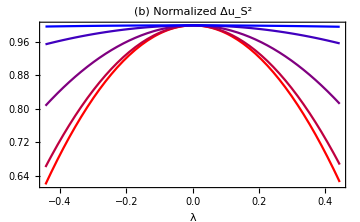

Legend:

(RGBColor[1, 0, 0] | Δ = -18.00
RGBColor[Rational[3, 4], 0, Rational[1, 4]] | Δ = -6.80
RGBColor[Rational[1, 2], 0, Rational[1, 2]] | Δ = 0.00
RGBColor[Rational[1, 4], 0, Rational[3, 4]] | Δ = 5.20
RGBColor[0, 0, 1] | Δ = 17.82)

Variance_uS_VS_Lambda.pdf

Variance_uS_VS_Lambda.png

Variance_uS_VS_Lambda.eps

```mathematica
ClearAll[functions,labels,legenda,colors,plot6]

Print["Functions for plotting:"]
functions=Table[AbsReVarNonResFunc[x]/.maxima[[i,2]],{i,2,5}]
functions=Flatten[{Take[functions,2],AbsReVarNonResFunc[x]/.Δ->0,Take[functions,-2]}]

Print["Labels:"]
labels=Table["Δ = "<>ToString[N[Δ/.maxima[[i,2]],2]],{i,2,5}]
labels=Flatten[{Take[labels,2],"Δ = 0.0000",Take[labels,-2]}]
labels={"Δ = -18.00","Δ = -6.80","Δ = 0.00","Δ = 5.20","Δ = 17.82"}

legenda=LineLegend[labels,LabelStyle->{FontSize->20,FontFamily->"Times"}];

colors=Table[RGBColor[1-i/4,0,i/4],{i,0,4}]

plot6=Plot[
functions,{x,-λmaxN,λmaxN},
PlotRange->{{-λmaxN,λmaxN},Automatic},
Frame->True,
FrameLabel->{"λ",None},
PlotLabel->"(b) Normalized Δu_S^2",
BaseStyle->{FontFamily->"Times",FontSize->20},
PlotStyle->colors,
PlotLegends->legenda,
ImageSize->Medium
]

Print["Legend:"]
MatrixForm[Transpose[{colors,labels}]]

Export["Variance_uS_VS_Lambda.pdf",plot6]
Export["Variance_uS_VS_Lambda.png",plot6,ImageResolution->200]
Export["Variance_uS_VS_Lambda.eps",plot6]
```

### Fig. 4 (c): Variance of Wnep Out of Resonance as a function of λ for various Δ

```mathematica
ClearAll[τN,parameters4, λmaxN,parameters8,CoherenceSMaxN]
ClearAll[ExactFuncWnep,PlotFuncWnep,AbsReVarWnepExact]

τN=π/6;

Print["Coherence in the system:"]
CoherenceSMax=√(ρ11(1-ρ11))
CoherenceSMaxN=CoherenceSMax/.ρ11->1/4
parameters8={ℏ->1,ρ11->1/4,ρ12R->CoherenceSMaxN/√2,ρ12I->CoherenceSMaxN/√2,ωe->2,β->1,g->1,τ->τN};

Print["λmax:"]
λmax
λmaxN=λmax/.parameters8
N[%]

Print[" Variance of Wnep using Δ instead of ωs: "]
pippo=Simplify[VarLM/.{ωs->ωe + Δ},Assumptions->constraints]

Print[" Variance of Wnep with numerical parameters - numerical version of pippo: "]
temp8=(Simplify[VarLM/.{ωs->ωe + Δ},Assumptions->constraints])/.parameters8

Print["Exact and numerical Functions for the Real Part of the Variance:"]
ClearAll[temp9e,temp9n,ExactFuncWnep,PlotFuncWnep]

temp9e=Simplify[ComplexExpand[Re[temp8]],Assumptions->constraints]
ExactFuncWnep[λ_,Δ1_]:=temp9e/.{λ1->λ,Δ->Δ1};

temp9n=Chop[ComplexExpand[Re[N[temp8]]]];
PlotFuncWnep[λ_,Δ1_]:=temp9n/.{λ1->λ,Δ->Δ1};

Print["Abs[Re[Var]] normalized to the value of λ=0"]
pippo8=Simplify[Abs[ExactFuncWnep[λ1,Δ]/ExactFuncWnep[0,Δ]],Assumptions->constraints]

AbsReVarWnepExact[x_,y_]:=(pippo8/.parameters8)/.{λ1->x,Δ->y};
AbsReVarWnepExact[λ1,Δ]
AbsReVarWnepExact[0,Δ]
N[%]
```

Coherence in the system:

√((1-ρ11) ρ11)

(√3)/4

λmax:

√(1/((ⅇ^(-1/2 β ωe ℏ)+ⅇ^((β ωe ℏ)/2))^2))

1/(1/ⅇ+ⅇ)

0.324027

Variance of Wnep using Δ instead of ωs:

1/((1+ⅇ^(β ωe ℏ))^2 (4 g^2+Δ^2)^2)4 g Δ^2 ℏ^2 Sin[1/72 π √(4 g^2+Δ^2)] ((1+ⅇ^(β ωe ℏ)) (4 g^2+Δ^2) (-ⅈ (1+ⅇ^(β ωe ℏ)) √(4 g^2+Δ^2) λ1 ρ12R Cos[1/72 π √(4 g^2+Δ^2)]+(g (1+(-1+ⅇ^(β ωe ℏ)) ρ11)-ⅈ (1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12I) Sin[1/72 π √(4 g^2+Δ^2)])-4 g Sin[1/72 π √(4 g^2+Δ^2)] ((1+ⅇ^(β ωe ℏ)) √(4 g^2+Δ^2) λ1 ρ12I Cos[1/72 π √(4 g^2+Δ^2)]+(g (-1+ρ11+ⅇ^(β ωe ℏ) ρ11)-(1+ⅇ^(β ωe ℏ)) Δ λ1 ρ12R) Sin[1/72 π √(4 g^2+Δ^2)])^2)

Variance of Wnep with numerical parameters - numerical version of pippo:

1/((1+ⅇ^2)^2 (4+Δ^2)^2)4 Δ^2 Sin[1/72 π √(4+Δ^2)] (-4 Sin[1/72 π √(4+Δ^2)] (1/4 √(3/2) (1+ⅇ^2) √(4+Δ^2) λ1 Cos[1/72 π √(4+Δ^2)]+(-3/4+ⅇ^2/4-1/4 √(3/2) (1+ⅇ^2) Δ λ1) Sin[1/72 π √(4+Δ^2)])^2+(1+ⅇ^2) (4+Δ^2) (-1/4 ⅈ √(3/2) (1+ⅇ^2) √(4+Δ^2) λ1 Cos[1/72 π √(4+Δ^2)]+(1+1/4 (-1+ⅇ^2)-1/4 ⅈ √(3/2) (1+ⅇ^2) Δ λ1) Sin[1/72 π √(4+Δ^2)]))

Exact and numerical Functions for the Real Part of the Variance:

1/(2 (1+ⅇ^2)^2 (4+Δ^2)^(5/2))Δ^2 Sin[1/72 π √(4+Δ^2)]^2 (√(4+Δ^2) (ⅇ^4 (7+√6 Δ λ1-6 λ1^2+Δ^2 (2-3 λ1^2))-3 (-5+√6 Δ λ1+2 λ1^2+Δ^2 (-2+λ1^2))-2 ⅇ^2 (-19+√6 Δ λ1+6 λ1^2+Δ^2 (-4+3 λ1^2)))-√(4+Δ^2) (-9-3 √6 Δ λ1+6 λ1^2+ⅇ^4 (-1+√6 Δ λ1+6 λ1^2)+ⅇ^2 (6-2 √6 Δ λ1+12 λ1^2)) Cos[1/36 π √(4+Δ^2)]+(1+ⅇ^2) (4+Δ^2) λ1 (-ⅇ^2 (√6-3 Δ λ1)+3 (√6+Δ λ1)) Sin[1/36 π √(4+Δ^2)])

Abs[Re[Var]] normalized to the value of λ=0

Abs[(√(4+Δ^2) (ⅇ^4 (7+√6 Δ λ1-6 λ1^2+Δ^2 (2-3 λ1^2))-3 (-5+√6 Δ λ1+2 λ1^2+Δ^2 (-2+λ1^2))-2 ⅇ^2 (-19+√6 Δ λ1+6 λ1^2+Δ^2 (-4+3 λ1^2)))-√(4+Δ^2) (-9-3 √6 Δ λ1+6 λ1^2+ⅇ^4 (-1+√6 Δ λ1+6 λ1^2)+ⅇ^2 (6-2 √6 Δ λ1+12 λ1^2)) Cos[1/36 π √(4+Δ^2)]+(1+ⅇ^2) (4+Δ^2) λ1 (-ⅇ^2 (√6-3 Δ λ1)+3 (√6+Δ λ1)) Sin[1/36 π √(4+Δ^2)])/(√(4+Δ^2) (15+6 Δ^2+ⅇ^4 (7+2 Δ^2)+ⅇ^2 (38+8 Δ^2)+(-3+ⅇ^2)^2 Cos[1/36 π √(4+Δ^2)]))]

Abs[(√(4+Δ^2) (ⅇ^4 (7+√6 Δ λ1-6 λ1^2+Δ^2 (2-3 λ1^2))-3 (-5+√6 Δ λ1+2 λ1^2+Δ^2 (-2+λ1^2))-2 ⅇ^2 (-19+√6 Δ λ1+6 λ1^2+Δ^2 (-4+3 λ1^2)))-√(4+Δ^2) (-9-3 √6 Δ λ1+6 λ1^2+ⅇ^4 (-1+√6 Δ λ1+6 λ1^2)+ⅇ^2 (6-2 √6 Δ λ1+12 λ1^2)) Cos[1/36 π √(4+Δ^2)]+(1+ⅇ^2) (4+Δ^2) λ1 (-ⅇ^2 (√6-3 Δ λ1)+3 (√6+Δ λ1)) Sin[1/36 π √(4+Δ^2)])/(√(4+Δ^2) (15+6 Δ^2+ⅇ^4 (7+2 Δ^2)+ⅇ^2 (38+8 Δ^2)+(-3+ⅇ^2)^2 Cos[1/36 π √(4+Δ^2)]))]

Abs[(√(4+Δ^2) (-2 ⅇ^2 (-19-4 Δ^2)-3 (-5-2 Δ^2)+ⅇ^4 (7+2 Δ^2))-(-9+6 ⅇ^2-ⅇ^4) √(4+Δ^2) Cos[1/36 π √(4+Δ^2)])/(√(4+Δ^2) (15+6 Δ^2+ⅇ^4 (7+2 Δ^2)+ⅇ^2 (38+8 Δ^2)+(-3+ⅇ^2)^2 Cos[1/36 π √(4+Δ^2)]))]

Abs[(√(4.+Δ^2) (-14.7781 (-19.-4. Δ^2)-3. (-5.-2. Δ^2)+54.5982 (7.+2. Δ^2))+19.2638 √(4.+Δ^2) Cos[0.0872665 √(4.+Δ^2)])/(√(4.+Δ^2) (15.+6. Δ^2+54.5982 (7.+2. Δ^2)+7.38906 (38.+8. Δ^2)+19.2638 Cos[0.0872665 √(4.+Δ^2)]))]

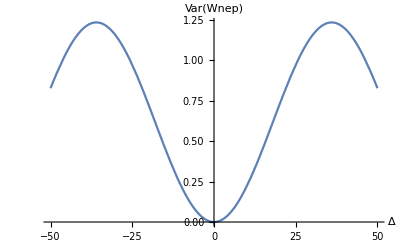

Maxima and minima of the variance function:

((Δ→-4 √2) | (Δ→4 √2)
(Δ→-2 √35) | (Δ→2 √35)
(Δ→-8 √5) | (Δ→8 √5)
(Δ→-2 √143) | (Δ→2 √143)
(Δ→-8 √14) | (Δ→8 √14)
(Δ→-2 √323) | (Δ→2 √323)
(Δ→-4 √110) | (Δ→4 √110)
(Δ→-10 √23) | (Δ→10 √23)
(Δ→-4 √182) | (Δ→4 √182)
(Δ→-2 √899) | (Δ→2 √899))

((Δ→-5.65685) | (Δ→5.65685)
(Δ→-11.8322) | (Δ→11.8322)
(Δ→-17.8885) | (Δ→17.8885)
(Δ→-23.9165) | (Δ→23.9165)
(Δ→-29.9333) | (Δ→29.9333)
(Δ→-35.9444) | (Δ→35.9444)
(Δ→-41.9524) | (Δ→41.9524)
(Δ→-47.9583) | (Δ→47.9583)
(Δ→-53.963) | (Δ→53.963)
(Δ→-59.9667) | (Δ→59.9667))

Maxima:

((Δ→-4 √2) | (Δ→4 √2)
(Δ→-8 √5) | (Δ→8 √5)
(Δ→-8 √14) | (Δ→8 √14)
(Δ→-4 √110) | (Δ→4 √110)
(Δ→-4 √182) | (Δ→4 √182)
(Δ→-16 √17) | (Δ→16 √17)
(Δ→-8 √95) | (Δ→8 √95)
(Δ→-4 √506) | (Δ→4 √506)
(Δ→-20 √26) | (Δ→20 √26)
(Δ→-8 √203) | (Δ→8 √203)
(Δ→-16 √62) | (Δ→16 √62))

Values of Var(Wnep) at maxima:

(0.0737096
0.61135
1.15005
1.15269
0.61833
0.082881
0.0829027
0.618889
1.15498
1.15507)

Zeroes:

((Δ→-2 √35) | (Δ→2 √35)
(Δ→-2 √143) | (Δ→2 √143)
(Δ→-2 √323) | (Δ→2 √323)
(Δ→-10 √23) | (Δ→10 √23)
(Δ→-2 √899) | (Δ→2 √899)
(Δ→-2 √1295) | (Δ→2 √1295)
(Δ→-2 √1763) | (Δ→2 √1763)
(Δ→-14 √47) | (Δ→14 √47)
(Δ→-2 √2915) | (Δ→2 √2915)
(Δ→-2 √3599) | (Δ→2 √3599))

Check they're really zero values:

(0.922089
1.23437
0.927125
0.309253
0
0.309424
0.928385
1.23796
0.928536)

```mathematica
Plot[ExactFuncWnep[0,Δ],{Δ,-50,50},
AxesLabel->{"Δ","Var(Wnep)"}]

ClearAll[Δ,polesEx,maximaEx, zeroesEx]

Print["Maxima and minima of the variance function:"]
polesEx=Table[Solve[τN √(4+Δ^2)==n π,Δ],{n,1,10}];
MatrixForm[polesEx]
MatrixForm[N[polesEx]]

Print["Maxima:"]
maximaEx=Table[Solve[τN √(4+Δ^2)==(2n+1) π,Δ],{n,0,10}];
MatrixForm[%]

Print["Values of Var(Wnep) at maxima:"]
Table[{N[ExactFuncWnep[0,Δ]]}/.maximaEx[[n,2]],{n,1,10}];
MatrixForm[%]

Print["Zeroes:"]
zeroesEx=Table[Solve[τN √(4+Δ^2)==2n π,Δ],{n,1,10}];
MatrixForm[%]

Print["Check they're really zero values:"]
Table[Chop[PlotFuncWnep[0,Δ]/.zeroesEx[[n,2]]],{n,2,10}];
MatrixForm[%]
```

(Abs[450 (1+ⅇ^2) λ (3 (√6-8 √14 λ)-ⅇ^2 (√6+24 √14 λ))+15 √3 (-9+48 √21 λ+6 λ^2+ⅇ^4 (-1-16 √21 λ+6 λ^2)+ⅇ^2 (6+32 √21 λ+12 λ^2))+30 (ⅇ^4 (7-16 √21 λ-6 λ^2+896 (2-3 λ^2))-3 (-5-16 √21 λ+2 λ^2+896 (-2+λ^2))-2 ⅇ^2 (-19-16 √21 λ+6 λ^2+896 (-4+3 λ^2)))]/(30 (5391+7206 ⅇ^2+1799 ⅇ^4-1/2 √3 (-3+ⅇ^2)^2))
Abs[324 (1+ⅇ^2) λ (3 (√6-8 √5 λ)-ⅇ^2 (√6+24 √5 λ))+18 (ⅇ^4 (7-8 √30 λ-6 λ^2+320 (2-3 λ^2))-3 (-5-8 √30 λ+2 λ^2+320 (-2+λ^2))-2 ⅇ^2 (-19-8 √30 λ+6 λ^2+320 (-4+3 λ^2)))]/(18 (1935+2598 ⅇ^2+647 ⅇ^4))
Abs[18 (1+ⅇ^2) λ (3 (√6-4 √2 λ)-ⅇ^2 (√6+12 √2 λ))-3 √3 (-9+24 √3 λ+6 λ^2+ⅇ^4 (-1-8 √3 λ+6 λ^2)+ⅇ^2 (6+16 √3 λ+12 λ^2))+6 (ⅇ^4 (7-8 √3 λ-6 λ^2+32 (2-3 λ^2))-3 (-5-8 √3 λ+2 λ^2+32 (-2+λ^2))-2 ⅇ^2 (-19-8 √3 λ+6 λ^2+32 (-4+3 λ^2)))]/(6 (207+294 ⅇ^2+71 ⅇ^4+1/2 √3 (-3+ⅇ^2)^2))
Abs[18 (1+ⅇ^2) λ (-ⅇ^2 (√6-12 √2 λ)+3 (√6+4 √2 λ))-3 √3 (-9-24 √3 λ+6 λ^2+ⅇ^4 (-1+8 √3 λ+6 λ^2)+ⅇ^2 (6-16 √3 λ+12 λ^2))+6 (ⅇ^4 (7+8 √3 λ-6 λ^2+32 (2-3 λ^2))-3 (-5+8 √3 λ+2 λ^2+32 (-2+λ^2))-2 ⅇ^2 (-19+8 √3 λ+6 λ^2+32 (-4+3 λ^2)))]/(6 (207+294 ⅇ^2+71 ⅇ^4+1/2 √3 (-3+ⅇ^2)^2))
Abs[324 (1+ⅇ^2) λ (-ⅇ^2 (√6-24 √5 λ)+3 (√6+8 √5 λ))+18 (ⅇ^4 (7+8 √30 λ-6 λ^2+320 (2-3 λ^2))-3 (-5+8 √30 λ+2 λ^2+320 (-2+λ^2))-2 ⅇ^2 (-19+8 √30 λ+6 λ^2+320 (-4+3 λ^2)))]/(18 (1935+2598 ⅇ^2+647 ⅇ^4))
Abs[450 (1+ⅇ^2) λ (-ⅇ^2 (√6-24 √14 λ)+3 (√6+8 √14 λ))+15 √3 (-9-48 √21 λ+6 λ^2+ⅇ^4 (-1+16 √21 λ+6 λ^2)+ⅇ^2 (6-32 √21 λ+12 λ^2))+30 (ⅇ^4 (7+16 √21 λ-6 λ^2+896 (2-3 λ^2))-3 (-5+16 √21 λ+2 λ^2+896 (-2+λ^2))-2 ⅇ^2 (-19+16 √21 λ+6 λ^2+896 (-4+3 λ^2)))]/(30 (5391+7206 ⅇ^2+1799 ⅇ^4-1/2 √3 (-3+ⅇ^2)^2)))

{Δ→-8 √14,Δ→-8 √5,Δ→-4 √2,Δ→4 √2,Δ→8 √5,Δ→8 √14}

{Δ = -29.9333,Δ = -17.8885,Δ = -5.65685,Δ = 5.65685,Δ = 17.8885,Δ = 29.9333}

{Δ = -29.93,Δ = -17.89,Δ = -5.66,Δ = 5.66,Δ = 17.89,Δ = 29.93}

{RGBColor[1, 0, 0],RGBColor[Rational[4, 5], 0, Rational[1, 5]],RGBColor[Rational[3, 5], 0, Rational[2, 5]],RGBColor[Rational[2, 5], 0, Rational[3, 5]],RGBColor[Rational[1, 5], 0, Rational[4, 5]],RGBColor[0, 0, 1]}

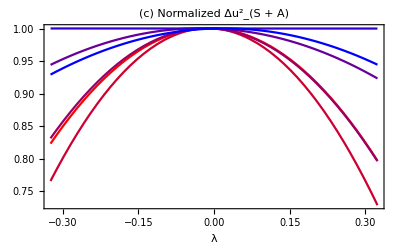

Legend:

(RGBColor[1, 0, 0] | Δ = -29.93
RGBColor[Rational[4, 5], 0, Rational[1, 5]] | Δ = -17.89
RGBColor[Rational[3, 5], 0, Rational[2, 5]] | Δ = -5.66
RGBColor[Rational[2, 5], 0, Rational[3, 5]] | Δ = 5.66
RGBColor[Rational[1, 5], 0, Rational[4, 5]] | Δ = 17.89
RGBColor[0, 0, 1] | Δ = 29.93)

Variance_Wnep_VS_Lambda.pdf

Variance_Wnep_VS_Lambda.png

Variance_Wnep_VS_Lambda.eps

```mathematica
ClearAll[functions, labels,plot8,colors,labels,legenda]

functions=Flatten[{Reverse[Table[AbsReVarWnepExact[λ,Δ]/.maximaEx[[n,1]],{n,1,3}]],Table[AbsReVarWnepExact[λ,Δ]/.maximaEx[[n,2]],{n,1,3}]}];
MatrixForm[%]

labels=Flatten[{Reverse[Table[maximaEx[[n,1]],{n,1,3}]],Table[maximaEx[[n,2]],{n,1,3}]}]
labels=Flatten[{Reverse[Table["Δ = "<>ToString[N[Δ/.maximaEx[[n,1]]]],{n,1,3}]],Table["Δ = "<>ToString[N[Δ/.maximaEx[[n,2]]]],{n,1,3}]}]
labels={"Δ = -29.93","Δ = -17.89","Δ = -5.66","Δ = 5.66","Δ = 17.89","Δ = 29.93"}

legenda=LineLegend[labels,LabelStyle->{FontSize->20,FontFamily->"Times"}];

colors=Table[RGBColor[1-i/5,0,i/5],{i,0,5}]
plot8=Plot[
functions,{λ,-λmaxN,λmaxN},
PlotLabel->"(c) Normalized (Δu^2)_(S + A)",
PlotRange->Automatic,
Frame->True,
FrameLabel->{"λ",None},
BaseStyle->{FontFamily->"Times",FontSize->20},
PlotLegends->legenda,
PlotStyle->colors
]

Print["Legend:"]
MatrixForm[Transpose[{colors,labels}]]

Export["Variance_Wnep_VS_Lambda.pdf",plot8]
Export["Variance_Wnep_VS_Lambda.png",plot8,ImageResolution->200]
Export["Variance_Wnep_VS_Lambda.eps",plot8]
```

## 8a. Operator approach (only energy-preserving case)

### Operators for evaluation of coherent Work exchanges

```mathematica
ClearAll[O1,O2,O2res]

O1=Marginal[KroneckerProduct[Hs,id2].KroneckerProduct[id2,χA],1];
Print["Operator O1: "]
O1//MatrixForm

O2=Simplify[
Marginal[Udag.KroneckerProduct[Hs,id2].U.KroneckerProduct[id2,χA],1],
Assumptions->constraints];

Print["Operator O2: "]
O2//MatrixForm 

Print["Operator O2 at resonance:"]
O2res=Simplify[O2/.{ωs->ω,ωe->ω},Assumptions->constraints]
MatrixForm[%]

(* Print["Its eigenvalues and eigenvectors: "]
Eigensystem[O2] *)

Print["Its eigenvalues and eigenvectors at resonance: "]
Eigensystem[O2res]

Print["Generic initial system state, hermitian and with Tr = 1: "]
MatrixForm[ρSt0]

Print["Average Coherent Work at resonance computed with the new method:"]
AvCohWork =FullSimplify[Tr[(O2res-O1).ρSt0]]

Print["Comparison with the exact theoretical value:"]
Simplify[AverageWcSTHEO/.{ωe->ω,ωs->ω},Assumptions->constraints]
```

Operator O1:

(0 | 0
0 | 0)

Operator O2:

(0 | (2 g λ1 ωs ℏ Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (-ⅈ √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(-ωe+ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/(4 g^2+(ωe-ωs)^2)
(2 g λ1 ωs ℏ Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] (ⅈ √(4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+(-ωe+ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/(4 g^2+(ωe-ωs)^2) | 0)

Operator O2 at resonance:

{{0,-1/2 ⅈ λ1 ω ℏ Sin[2 g τ]},{1/2 ⅈ λ1 ω ℏ Sin[2 g τ],0}}

(0 | -1/2 ⅈ λ1 ω ℏ Sin[2 g τ]
1/2 ⅈ λ1 ω ℏ Sin[2 g τ] | 0)

Its eigenvalues and eigenvectors at resonance:

{{-1/2 λ1 ω ℏ Sin[2 g τ],1/2 λ1 ω ℏ Sin[2 g τ]},{{ⅈ,1},{-ⅈ,1}}}

Generic initial system state, hermitian and with Tr = 1:

(ρ11 | ⅈ ρ12I+ρ12R
-ⅈ ρ12I+ρ12R | 1-ρ11)

Average Coherent Work at resonance computed with the new method:

-λ1 ρ12I ω ℏ Sin[2 g τ]

Comparison with the exact theoretical value:

-λ1 ρ12I ω ℏ Sin[2 g τ]

```mathematica
Eigenvalues[O2res]
```

{-1/2 λ1 ω ℏ Sin[2 g τ],1/2 λ1 ω ℏ Sin[2 g τ]}

```mathematica
{o2m,o2p}=Eigenvalues[O2res]
```

{-1/2 λ1 ω ℏ Sin[2 g τ],1/2 λ1 ω ℏ Sin[2 g τ]}

```mathematica
o2m
```

-1/2 λ1 ω ℏ Sin[2 g τ]

### Quasiprobability Distribution

There’s some freedom in choosing the initial basis because the observable O_1 is zero.

#### Choosing the z-basis for O_1

```mathematica
ClearAll[Π1m,Π1p,Π2m,Π2p,o1p,o1m,o2p,o2m,psi2p,psi2m,qmmz,qmpz,qpmz,qppz]

Print["Eigenprojectors and eigenvalues of O1:"] 

Π1m=P0;
MatrixForm[%]
Π1p=P1;
MatrixForm[%]
o1p=0
o1m=0

Print["Eigenprojectors and eigenvalues of O2 at resonance:"] 

psi2m=1/(√2){1,-I};
Π2m=ketbra[psi2m];
MatrixForm[%]
psi2p=1/(√2){1,I};
Π2p=ketbra[psi2p];
MatrixForm[%]
{o2m,o2p}=Eigenvalues[O2res]

Print["Quasiprobabilities of this process: "]

qmmz=FullSimplify[Tr[Π2m.Π1m.ρSt0]];
Print["qmmz = ",qmmz]
qmpz=FullSimplify[Tr[Π2p.Π1m.ρSt0]];
Print["qmpz = ",qmpz]
qpmz=FullSimplify[Tr[Π2m.Π1p.ρSt0]];
Print["qpmz = ",qpmz]
qppz=FullSimplify[Tr[Π2p.Π1p.ρSt0]];
Print["qppz = ",qppz]
Print["Sum of quasiprobabilities = ",FullSimplify[qmmz+qpmz+qmpz+qppz]]

Print["Average of Wc with this method:"]
MeanCoherentZ=Simplify[(qmmz+qpmz) o2m+(qmpz+qppz)o2p]

Print["Second moment of Wc:"]
SquareCoherentZ=Simplify[(qmmz+qpmz) o2m^2+(qmpz+qppz)o2p^2]

Print["Variance of Wc:"]
VarianceCoherentZ=FullSimplify[SquareCoherentZ-MeanCoherentZ^2]
```

Eigenprojectors and eigenvalues of O1:

(1 | 0
0 | 0)

(0 | 0
0 | 1)

0

0

Eigenprojectors and eigenvalues of O2 at resonance:

(1/2 | ⅈ/2
-ⅈ/2 | 1/2)

(1/2 | -ⅈ/2
ⅈ/2 | 1/2)

{-1/2 λ1 ω ℏ Sin[2 g τ],1/2 λ1 ω ℏ Sin[2 g τ]}

Quasiprobabilities of this process:

qmmz = 1/2 (ρ11+ρ12I-ⅈ ρ12R)

qmpz = 1/2 (ρ11-ρ12I+ⅈ ρ12R)

qpmz = 1/2 (1-ρ11+ρ12I+ⅈ ρ12R)

qppz = 1/2 (1-ρ11-ρ12I-ⅈ ρ12R)

Sum of quasiprobabilities = 1

Average of Wc with this method:

-λ1 ρ12I ω ℏ Sin[2 g τ]

Second moment of Wc:

1/4 λ1^2 ω^2 ℏ^2 Sin[2 g τ]^2

Variance of Wc:

1/4 λ1^2 (1-4 ρ12I^2) ω^2 ℏ^2 Sin[2 g τ]^2

#### Choosing the y-basis for O_1

```mathematica
ClearAll[Π1m,Π1p,Π2m,Π2p,o1p,o1m,o2p,o2m,psi1m,psi1p,psi2p,psi2m,qmmy,qmpy,qpmy,qppy]

Print["Eigenprojectors and eigenvalues of O1:"] 

psi1m=1/(√2){1,-I};
Π1m=ketbra[psi1m];
MatrixForm[%]
psi1p=1/(√2){1,I};
Π1p=ketbra[psi1p];
o1p=0
o1m=0

Print["Eigenprojectors and eigenvalues of O2 at resonance:"] 

psi2m=1/(√2){1,-I};
Π2m=ketbra[psi2m];
MatrixForm[%]
psi2p=1/(√2){1,I};
Π2p=ketbra[psi2p];
MatrixForm[%]
{o2m,o2p}=Eigenvalues[O2res]

Print["Quasiprobabilities of this process: "]

qmmy=FullSimplify[Tr[Π2m.Π1m.ρSt0]];
Print["qmmy = ",qmmy]
qmpy=FullSimplify[Tr[Π2p.Π1m.ρSt0]];
Print["qmpy = ",qmpy]
qpmy=FullSimplify[Tr[Π2m.Π1p.ρSt0]];
Print["qpmy = ",qpmy]
qppy=FullSimplify[Tr[Π2p.Π1p.ρSt0]];
Print["qppy = ",qppy]
Print["Sum of quasiprobabilities = ",FullSimplify[qmmy+qpmy+qmpy+qppy]]

Print["Average of Wc with this method:"]
MeanCoherentY=Simplify[(qmmy+qpmy) o2m+(qmpy+qppy)o2p]

Print["Second moment of Wc:"]
SquareCoherentY=Simplify[(qmmy+qpmy) o2m^2+(qmpy+qppy)o2p^2]

Print["Variance of Wc:"]
VarianceCoherentY=FullSimplify[SquareCoherentY-MeanCoherentY^2]
```

Eigenprojectors and eigenvalues of O1:

(1/2 | ⅈ/2
-ⅈ/2 | 1/2)

0

0

Eigenprojectors and eigenvalues of O2 at resonance:

(1/2 | ⅈ/2
-ⅈ/2 | 1/2)

(1/2 | -ⅈ/2
ⅈ/2 | 1/2)

{-1/2 λ1 ω ℏ Sin[2 g τ],1/2 λ1 ω ℏ Sin[2 g τ]}

Quasiprobabilities of this process:

qmmy = 1/2+ρ12I

qmpy = 0

qpmy = 0

qppy = 1/2-ρ12I

Sum of quasiprobabilities = 1

Average of Wc with this method:

-λ1 ρ12I ω ℏ Sin[2 g τ]

Second moment of Wc:

1/4 λ1^2 ω^2 ℏ^2 Sin[2 g τ]^2

Variance of Wc:

1/4 λ1^2 (1-4 ρ12I^2) ω^2 ℏ^2 Sin[2 g τ]^2

#### Choosing the x-basis for O_1

```mathematica
ClearAll[Π1m,Π1p,Π2m,Π2p,o1p,o1m,o2p,o2m,psi1m,psi1p,psi2p,psi2m,qmmx,qmpx,qpmx,qppx]

Print["Eigenprojectors and eigenvalues of O1:"] 

psi1m=1/(√2){1,-1};
Π1m=ketbra[psi1m];
MatrixForm[%]
psi1p=1/(√2){1,1};
Π1p=ketbra[psi1p];
o1p=0
o1m=0

Print["Eigenprojectors and eigenvalues of O2 at resonance:"] 

psi2m=1/(√2){1,-I};
Π2m=ketbra[psi2m];
MatrixForm[%]
psi2p=1/(√2){1,I};
Π2p=ketbra[psi2p];
MatrixForm[%]
{o2m,o2p}=Eigenvalues[O2res]

Print["Quasiprobabilities of this process: "]

qmmx=FullSimplify[Tr[Π2m.Π1m.ρSt0]];
Print["qmmx = ",qmmx]
qmpx=FullSimplify[Tr[Π2p.Π1m.ρSt0]];
Print["qmpx = ",qmpx]
qpmx=FullSimplify[Tr[Π2m.Π1p.ρSt0]];
Print["qpmx = ",qpmx]
qppx=FullSimplify[Tr[Π2p.Π1p.ρSt0]];
Print["qppx = ",qppx]
Print["Sum of quasiprobabilities = ",FullSimplify[qmmx+qpmx+qmpx+qppx]]

Print["Average of Wc with this method:"]
MeanCoherentX=Simplify[(qmmx+qpmx) o2m+(qmpx+qppx)o2p]

Print["Second moment of Wc:"]
SquareCoherentX=Simplify[(qmmx+qpmx) o2m^2+(qmpx+qppx)o2p^2]

Print["Variance of Wc:"]
VarianceCoherentX=FullSimplify[SquareCoherentX-MeanCoherentX^2]
```

Eigenprojectors and eigenvalues of O1:

(1/2 | -1/2
-1/2 | 1/2)

0

0

Eigenprojectors and eigenvalues of O2 at resonance:

(1/2 | ⅈ/2
-ⅈ/2 | 1/2)

(1/2 | -ⅈ/2
ⅈ/2 | 1/2)

{-1/2 λ1 ω ℏ Sin[2 g τ],1/2 λ1 ω ℏ Sin[2 g τ]}

Quasiprobabilities of this process:

qmmx = (1/4+ⅈ/4)-(ⅈ ρ11)/2+ρ12I/2-ρ12R/2

qmpx = (1/4-ⅈ/4)+(ⅈ ρ11)/2-ρ12I/2-ρ12R/2

qpmx = (1/4-ⅈ/4)+(ⅈ ρ11)/2+ρ12I/2+ρ12R/2

qppx = (1/4+ⅈ/4)-(ⅈ ρ11)/2-ρ12I/2+ρ12R/2

Sum of quasiprobabilities = 1

Average of Wc with this method:

-λ1 ρ12I ω ℏ Sin[2 g τ]

Second moment of Wc:

1/4 λ1^2 ω^2 ℏ^2 Sin[2 g τ]^2

Variance of Wc:

1/4 λ1^2 (1-4 ρ12I^2) ω^2 ℏ^2 Sin[2 g τ]^2

## 8b. FIGURE 5: quasiprobabilities of coherent work

```mathematica
Print["Quasiprobabilities of WcS:"]
MatrixForm[vecqWcS]

Print["Quasiprobabilities of WcS In the resonant case:"]
MatrixForm[Simplify[vecqWcS/.{ωe->ω,ωs->ω},Assumptions->constraints]]

Print["Quasiprobabilities of WcS - Real part in the resonant case:"]
MatrixForm[Simplify[ComplexExpand[Re[vecqWcS]]/.{ωe->ω,ωs->ω},Assumptions->constraints]]

Print["Quasiprobabilities of WcS - Imaginary part in the resonant case:"]
MatrixForm[Simplify[ComplexExpand[Im[vecqWcS]]/.{ωe->ω,ωs->ω},Assumptions->constraints]]

Print["Sum of the quasiprobabilities:"]
sumqWcS=Simplify[Total[vecqWcS],Assumptions->constraints]
Print[""]

Print["Pseudo-Quasiprobabilities of WcS at resonance:"]
vecqWcSres=Simplify[vecqWcS/.{ωs->ω,ωe->ω},Assumptions->constraints];
MatrixForm[%]

Print["System energy differences:"]
vecΔES

Print["Average of WcS at resonance:"]
AverageWcAqres=Simplify[(vecΔES.vecqWcS)/.{ωs->ω,ωe->ω},Assumptions->constraints]

Print["Compared to theoretical value of WcS:"]
Simplify[AverageWcSTHEO/.{ωs->ω,ωe->ω},Assumptions->constraints]
```

Quasiprobabilities of WcS:

(-(2 g λ1 (ρ12I-ⅈ ρ12R) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] ((4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ⅈ √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))
-(2 g λ1 (ρ12I+ⅈ ρ12R) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] ((4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]-ⅈ √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))
(2 g λ1 (ρ12I-ⅈ ρ12R) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] ((4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]+ⅈ √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2))
(2 g λ1 (ρ12I+ⅈ ρ12R) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)] ((4 g^2+(ωe-ωs)^2) Cos[1/2 τ √(4 g^2+(ωe-ωs)^2)]-ⅈ √(4 g^2+(ωe-ωs)^2) (ωe-ωs) Sin[1/2 τ √(4 g^2+(ωe-ωs)^2)]))/((4 g^2+(ωe-ωs)^2)^(3/2)))

Quasiprobabilities of WcS In the resonant case:

(-1/2 λ1 (ρ12I-ⅈ ρ12R) Sin[2 g τ]
-1/2 λ1 (ρ12I+ⅈ ρ12R) Sin[2 g τ]
1/2 λ1 (ρ12I-ⅈ ρ12R) Sin[2 g τ]
1/2 λ1 (ρ12I+ⅈ ρ12R) Sin[2 g τ])

Quasiprobabilities of WcS - Real part in the resonant case:

(-1/2 λ1 ρ12I Sin[2 g τ]
-1/2 λ1 ρ12I Sin[2 g τ]
1/2 λ1 ρ12I Sin[2 g τ]
1/2 λ1 ρ12I Sin[2 g τ])

Quasiprobabilities of WcS - Imaginary part in the resonant case:

(1/2 λ1 ρ12R Sin[2 g τ]
-1/2 λ1 ρ12R Sin[2 g τ]
-1/2 λ1 ρ12R Sin[2 g τ]
1/2 λ1 ρ12R Sin[2 g τ])

Sum of the quasiprobabilities:

0

Pseudo-Quasiprobabilities of WcS at resonance:

(-1/2 λ1 (ρ12I-ⅈ ρ12R) Sin[2 g τ]
-1/2 λ1 (ρ12I+ⅈ ρ12R) Sin[2 g τ]
1/2 λ1 (ρ12I-ⅈ ρ12R) Sin[2 g τ]
1/2 λ1 (ρ12I+ⅈ ρ12R) Sin[2 g τ])

System energy differences:

{0,ωs ℏ,-ωs ℏ,0}

Average of WcS at resonance:

-λ1 ρ12I ω ℏ Sin[2 g τ]

Compared to theoretical value of WcS:

-λ1 ρ12I ω ℏ Sin[2 g τ]

#### Construction of P[w] of Coherent Work - quasiprobability approach

```mathematica
ClearAll[wVec,qwVec,nwVec,k,i,len,kWmax,added]

wVec={}; (* array with the individual values assumed by w *)
qwVec={}; (* array of the corresponding quasiprobabilities *)
nwVec=0; (* number of elements in each of the arrays above *)
kWmax=Dimensions[vecΔES][[1]];

For[k=1,k<=kWmax,k++,
w=vecΔES[[k]]; (* single out current value of work exchange and its corresponding quasiprobability *)
q=vecqWcSres[[k]];
len=Length[wVec];
added=False;
For[i=1,i<=len,i++,(* loop over already stored entries in the arrays, if any *)
If[wVec[[i]]==w,
qwVec[[i]]=qwVec[[i]]+q; (* here we found that the work value w is already present in the array *)
added=True;
Break[] (* exit for loop, because we found the value *)
]
];
If[!added,(* if it's the first run, we add the first entry *)
AppendTo[wVec,w];(* if we got here, the value of w was not present in the array, so we add it *)
AppendTo[qwVec,q];(* we also add its quasiprobability *)
nwVec++;
added=True;
];
]

qwVec=Simplify[qwVec];

Print["Vector of values of Wc:"]
wVec

Print["Vector of corresponding probabilities:"]
qwVec

Print["Check - Average of Wc with this method:"]
Simplify[wVec.qwVec]

Print[" Construction of data array for istogram display (Real and Imaginary parts): "]

ClearAll[ReDataWqp,ImDataWqp]

ReDataWqp=Transpose[{wVec,ComplexExpand[Re[qwVec]]}];
MatrixForm[%]

ImDataWqp=Transpose[{wVec,ComplexExpand[Im[qwVec]]}];
MatrixForm[%]
```

Vector of values of Wc:

{0,ωs ℏ,-ωs ℏ}

Vector of corresponding probabilities:

{ⅈ λ1 ρ12R Sin[2 g τ],-1/2 λ1 (ρ12I+ⅈ ρ12R) Sin[2 g τ],1/2 λ1 (ρ12I-ⅈ ρ12R) Sin[2 g τ]}

Check - Average of Wc with this method:

-λ1 ρ12I ωs ℏ Sin[2 g τ]

Construction of data array for istogram display (Real and Imaginary parts):

(0 | 0
ωs ℏ | -1/2 λ1 ρ12I Sin[2 g τ]
-ωs ℏ | 1/2 λ1 ρ12I Sin[2 g τ])

(0 | λ1 ρ12R Sin[2 g τ]
ωs ℏ | -1/2 λ1 ρ12R Sin[2 g τ]
-ωs ℏ | -1/2 λ1 ρ12R Sin[2 g τ])

```mathematica
Print["Coherence in the system:"]
CoherenceSMax=√(ρ11(1-ρ11))
CoherenceSMaxN=CoherenceSMax/.ρ11->1/4

Print["λmax:"]
λmax
λmaxN=N[λmax/.{ℏ->1,β->1/10,ωe->1}]
N[%]

parameters2={ℏ->1,ρ11->1/4,ρ12R->CoherenceSMaxN*Cos[π/3],ρ12I->CoherenceSMaxN*Sin[π/3],ω->1,ωs->1,ωe->1,β->1/10,g->1,λ->λmaxN,λ1->λmaxN}
τmax=π
```

Coherence in the system:

√((1-ρ11) ρ11)

(√3)/4

λmax:

√(1/((ⅇ^(-1/2 β ωe ℏ)+ⅇ^((β ωe ℏ)/2))^2))

0.499376

0.499376

{ℏ→1,ρ11→1/4,ρ12R→(√3)/8,ρ12I→3/8,ω→1,ωs→1,ωe→1,β→1/10,g→1,λ→0.499376,λ1→0.499376}

π

{0,-0.0936329 Sin[2 π t],0.0936329 Sin[2 π t],0.108118 Sin[2 π t],-0.054059 Sin[2 π t],-0.054059 Sin[2 π t]}

{q(w=0),q(w=ℏω_S),q(w=-ℏω_S)}

{w=0,w=ℏω_S,w=-ℏω_S}

LineLegend[{w=0,w=ℏω_S,w=-ℏω_S},LabelStyle→{FontSize→12,FontFamily→Times}]

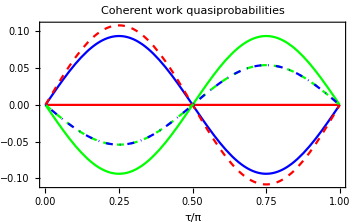

Legend:

(RGBColor[1, 0, 0] | w=0
RGBColor[0, 1, 0] | w=ℏω_S
RGBColor[0, 0, 1] | w=-ℏω_S)

qWc.pdf

qWc.png

qWc.eps

```mathematica
ClearAll[functions]
functions=Flatten[{Table[(ReDataWqp[[i,2]]/.parameters2)/.{τ->t*τmax},{i,1,3}],Table[(ImDataWqp[[i,2]]/.parameters2)/.{τ->t*τmax},{i,1,3}]}]

labels={"q(w=0)","q(w=ℏω_S)","q(w=-ℏω_S)"}
labels={"w=0","w=ℏω_S","w=-ℏω_S"}

legenda=LineLegend[labels,LabelStyle->{FontSize->12,FontFamily->"Times"}]

plotqWc=Plot[functions,{t,0,1},
PlotLabel->"Coherent work quasiprobabilities",
PlotStyle->{{Red},{Green},{Blue},{Red,Dashed},{Green,Dashed},{Blue,DotDashed}},
Frame->True,
FrameLabel->{"τ/π",None},
BaseStyle->{FontFamily->"Times",FontSize->14},
ImageSize->Medium,
PlotLegends->Placed[legenda,{0.75,0.44}]
]

Print["Legend:"]
colors={RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1]};
MatrixForm[Transpose[{colors,labels}]]

Export["qWc.pdf",plotqWc]
Export["qWc.png",plotqWc,ImageResolution->200]
Export["qWc.eps",plotqWc]
```

## 8c. FIGURE 6: Operator approach - Probability distribution for Coherent Work

```mathematica
Print["Eigenprojectors and eigenvalues of O2 at resonance:"] 

psi2m=1/(√2){1,-I};
Π2m=ketbra[psi2m];
MatrixForm[%]
psi2p=1/(√2){1,I};
Π2p=ketbra[psi2p];
MatrixForm[%]
{o2m,o2p}=Eigenvalues[O2res]

Print["Array of eigenvalues of O2:"]
vecOVals={o2m,o2p,o2m,o2p}

Print["Quasiprobabilities of this process: "]

qmmz=FullSimplify[Tr[Π2m.Π1m.ρSt0]];
Print["qmmz = ",qmmz]

qmpz=FullSimplify[Tr[Π2p.Π1m.ρSt0]];
Print["qmpz = ",qmpz]

qpmz=FullSimplify[Tr[Π2m.Π1p.ρSt0]];
Print["qpmz = ",qpmz]

qppz=FullSimplify[Tr[Π2p.Π1p.ρSt0]];
Print["qppz = ",qppz]

Print["Sum of quasiprobabilities = ",FullSimplify[qmmz+qpmz+qmpz+qppz]]

Print["Array of quasiprobabilities:"]
vecqwOp={qmmz,qmpz,qpmz,qppz};
MatrixForm[%]

Print["Average of Wc with this method:"]
MeanCoherentZ=Simplify[(qmmz+qpmz) o2m+(qmpz+qppz)o2p,Assumptions->constraints]

Print["Another check:"]
Simplify[vecqwOp.vecOVals,Assumptions->constraints]
```

Eigenprojectors and eigenvalues of O2 at resonance:

(1/2 | ⅈ/2
-ⅈ/2 | 1/2)

(1/2 | -ⅈ/2
ⅈ/2 | 1/2)

{-1/2 λ1 ω ℏ Sin[2 g τ],1/2 λ1 ω ℏ Sin[2 g τ]}

Array of eigenvalues of O2:

{-1/2 λ1 ω ℏ Sin[2 g τ],1/2 λ1 ω ℏ Sin[2 g τ],-1/2 λ1 ω ℏ Sin[2 g τ],1/2 λ1 ω ℏ Sin[2 g τ]}

Quasiprobabilities of this process:

qmmz = 1/2 (ρ11+ρ12I-ⅈ ρ12R)

qmpz = 1/2 (ρ11-ρ12I+ⅈ ρ12R)

qpmz = 1/2 (1-ρ11+ρ12I+ⅈ ρ12R)

qppz = 1/2 (1-ρ11-ρ12I-ⅈ ρ12R)

Sum of quasiprobabilities = 1

Array of quasiprobabilities:

(1/2 (ρ11+ρ12I-ⅈ ρ12R)
1/2 (ρ11-ρ12I+ⅈ ρ12R)
1/2 (1-ρ11+ρ12I+ⅈ ρ12R)
1/2 (1-ρ11-ρ12I-ⅈ ρ12R))

Average of Wc with this method:

-λ1 ρ12I ω ℏ Sin[2 g τ]

Another check:

-λ1 ρ12I ω ℏ Sin[2 g τ]

```mathematica
ClearAll[wVec,pwVec,nwVec,k,i,len,kWmax,added]

wVec={}; (* array with the individual values assumed by w *)
pwVec={}; (* array of the corresponding quasiprobabilities *)
nwVec=0; (* number of elements in each of the arrays above *)
kWmax=Dimensions[vecΔEA][[1]];

For[k=1,k<=kWmax,k++,
added=False;
w=vecOVals[[k]]; (* single out current value of work exchange and its corresponding quasiprobability *)
q=vecqwOp[[k]];
len=Length[wVec];
For[i=1,i<=len,i++,(* loop over already stored entries in the arrays, if any *)
If[wVec[[i]]==w,
pwVec[[i]]=pwVec[[i]]+q; (* here we found that the work value w is already present in the array, so we only add q *)
added=True;
Break[] (* exit for loop, because we found the value *)
]
];
If[!added,
AppendTo[wVec,w];(* if we got here, the value of w was not present in the array, so we add it *)
AppendTo[pwVec,q];(* we also add its quasiprobability *)
nwVec++;
added=True;
];
]

pwVec=Simplify[pwVec];

Print["Vector of values of W:"]
wVec

Print["Vector of corresponding probabilities:"]
pwVec

Print["Check - Average W computed with this method:"]
check=Simplify[wVec.pwVec,Assumptions->constraints]

Print["Dataset for istogram display:"]

ClearAll[ReDataWMO,ImDataWMO]

ReDataWMO=Simplify[Transpose[{wVec,Re[pwVec]}],Assumptions->constraints];
MatrixForm[%]

ImDataWMO=Simplify[Transpose[{wVec,Im[pwVec]}],Assumptions->constraints];
MatrixForm[%]
```

Vector of values of W:

{-1/2 λ1 ω ℏ Sin[2 g τ],1/2 λ1 ω ℏ Sin[2 g τ]}

Vector of corresponding probabilities:

{1/2+ρ12I,1/2-ρ12I}

Check - Average W computed with this method:

-λ1 ρ12I ω ℏ Sin[2 g τ]

Dataset for istogram display:

(-1/2 λ1 ω ℏ Sin[2 g τ] | 1/2+ρ12I
1/2 λ1 ω ℏ Sin[2 g τ] | 1/2-ρ12I)

(-1/2 λ1 ω ℏ Sin[2 g τ] | 0
1/2 λ1 ω ℏ Sin[2 g τ] | 0)

```mathematica
Print["Coherence in the system:"]
CoherenceSMax=√(ρ11(1-ρ11))
CoherenceSMaxN=CoherenceSMax/.ρ11->1/4

Print["λmax:"]
λmax
λmaxN=N[λmax/.{ℏ->1,β->1/10,ωe->1}]

parameters2={ℏ->1,ρ11->1/4,ρ12R->CoherenceSMaxN*Cos[π/3],ρ12I->CoherenceSMaxN*Sin[π/3],ω->1,ωs->1,ωe->1,β->1/10,g->1,λ->λmaxN,λ1->λmaxN}
τmax=π;
```

Coherence in the system:

√((1-ρ11) ρ11)

(√3)/4

λmax:

√(1/((ⅇ^(-1/2 β ωe ℏ)+ⅇ^((β ωe ℏ)/2))^2))

0.499376

{ℏ→1,ρ11→1/4,ρ12R→(√3)/8,ρ12I→3/8,ω→1,ωs→1,ωe→1,β→1/10,g→1,λ→0.499376,λ1→0.499376}

{-1/2 λ1 ω ℏ Sin[2 g τ],1/2 λ1 ω ℏ Sin[2 g τ]}

{-0.249688 Sin[2 π t],0.249688 Sin[2 π t]}

{p(w^OA)=1/2 + Im[ρ_12],p(w^OA)=1/2 - Im[ρ_12]}

LineLegend[{p(w^OA)=1/2 + Im[ρ_12],p(w^OA)=1/2 - Im[ρ_12]},LabelStyle→{FontSize→12,FontFamily→Times}]

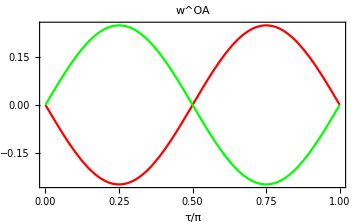

Legend:

(RGBColor[1, 0, 0] | p(w^OA)=1/2 + Im[ρ_12]
RGBColor[0, 1, 0] | p(w^OA)=1/2 - Im[ρ_12])

pWcMO.pdf

pWcMO.png

pWcMO.eps

```mathematica
ClearAll[functions]
functions={ReDataWMO[[1,1]],ReDataWMO[[2,1]]}

ClearAll[functions]
functions=Table[(ReDataWMO[[i,1]]/.parameters2)/.{τ->t*τmax},{i,1,2}]

labels={"p(w^OA)=1/2 + Im[ρ_12]","p(\!\(\*SuperscriptBox[\(w\), \(OA\)]\))=1/2 - Im[\!\(\*SubscriptBox[\(ρ\), \(12\)]\)]"}

legenda=LineLegend[{"p(w^OA)=1/2 + Im[ρ_12]","p(\!\(\*SuperscriptBox[\(w\), \(OA\)]\))=1/2 - Im[\!\(\*SubscriptBox[\(ρ\), \(12\)]\)]"},LabelStyle->{FontSize->12,FontFamily->"Times"}]

plotqWc=Plot[functions,{t,0,1},
PlotLabel->"w^OA",
PlotLegends->Placed[legenda,{0.74,0.49}],
Frame->True,
FrameLabel->{"τ/π",None},
PlotStyle->{Red,Green},
BaseStyle->{FontFamily->"Times",FontSize->14},
ImageSize->Medium
]

Print["Legend:"]
MatrixForm[Transpose[{{Red,Green},labels}]]

Export["pWcMO.pdf",plotqWc]
Export["pWcMO.png",plotqWc,ImageResolution->200]
Export["pWcMO.eps",plotqWc]
```

## 9. Estimates in realistic experimental setting: Microwave Photonics with Superconducting Quantum Circuits

Proposal 1: Cavity QED setup, realized on a Superconducting Quantum Circuit (SQC) interacting with microwave resonator photons.
We study the resonant case. 
The Rotating Wave Approximation, used to derive the Jaynes-Cummings Hamiltonian from Quantum Rabi Hamiltonian is valid when (ωs+ωe)>> Max[g,|ωs-ωe|], from Xui Gu et al., “Microwave Photonics with superconducting quantum circuits”, Phys. Rep. 718-19 (2017). 
Nel nostro caso con la energy-preserving condition, ciò vuol dire che g deve essere << 2 ω.

```mathematica
ℏ=1.;
ω=5.7*10^9 ; (* GHz range, microwaves *)
ωs=ω; (* resonant case *)
ωe=ω; (* resonant case *)
(* g=1.34*ωe; *)(* Value for Dispersive Strong Regime *)
g=2/5 ω;(* Value around 2/5 ω for validity of RWA *)
τ=10^-9*1.34/2; (* around 700 picoseconds, value for having g*τ around π/2, thus a strong single-collision effect *)
β=0.2*10^-9/ℏ;

ρ11=0.25;
r12=0.4;
ϕ12=π/4;
ρ12R=r12*Cos[ϕ12];
ρ12I=r12*Sin[ϕ12];
λmaxN=N[λmax];
Print["λmax for the Ancilla = ",λmaxN];
λ1=0.125;

(* Initial system state *)
ρSt0={{ρ11,ρ12R+I*ρ12I},{ρ12R-I*ρ12I,1-ρ11}};
Print["Initial system state:"]
MatrixForm[ρSt0]

(* Initial environment state *)
ρAth=MatrixExp[-β He]/Tr[MatrixExp[-β He]]; 
χA=λ1 σx;
ρA=ρAth+χA;
Print["Environment state with coherence:"]
MatrixForm[ρA] 

(* Initial collective state *)
ρin=Chop[KroneckerProduct[ρSt0,ρA]];
Print["Collective initial state:"]
MatrixForm[ρin]
```

λmax for the Ancilla = 0.428487

Initial system state:

(0.25 | 0.282843+0.282843 ⅈ
0.282843-0.282843 ⅈ | 0.75)

Environment state with coherence:

(0.24232 | 0.125
0.125 | 0.75768)

Collective initial state:

(0.0605801 | 0.03125 | 0.0685385+0.0685385 ⅈ | 0.0353553+0.0353553 ⅈ
0.03125 | 0.18942 | 0.0353553+0.0353553 ⅈ | 0.214304+0.214304 ⅈ
0.0685385-0.0685385 ⅈ | 0.0353553-0.0353553 ⅈ | 0.18174 | 0.09375
0.0353553-0.0353553 ⅈ | 0.214304-0.214304 ⅈ | 0.09375 | 0.56826)

## 10a. Dynamical evolution: repeated collisions, steady state WITH DIMENSIONLESS VARIABLES

This  section  implements  the  NUMERICAL  iteration  of  the  collisional  model  dynamics.
The numerical implementation uses as much as possible DIMENSIONLESS VARIABLES, as defined in the substitution rules below. 
The overall scale is set by the two parameters still carrying dimensions ℏ and ωe, the angular frequency giving the energy gap of the environment particles.

### Construction of the formulas for the relevant quantities, with dimensionless variables

```mathematica
(* ***** RESONANT CASE ***** *)

dimensionless={β->β1/(ℏ ωe),ωs->ωs1 ωe,g->g1 ωe,τ->τ1/ωe}
constraints={ωs∈Reals,ωs>0,ωe∈Reals,ωe>0,ω∈Reals,ω>0,β∈Reals,β>0,τse∈Reals,τse>0,τ∈Reals,τ>0,Jse∈Reals,Jse>0,g∈Reals,g>0,ρ11∈Reals,ρ11>=0,ρ11<=1,ρ12R∈Reals,ρ12I∈Reals,ℏ ∈ Reals,ℏ>0,ωs1∈Reals,ωs1>0,β1∈Reals,β1>0,τ1∈Reals,τ1>0,g1∈Reals,g1>0};

(* ***** GOOD FORMULAS WITH CORRECT FACTORISATION OF DIMENSIONED CONSTANTS ***** *)
(* to be computed only once analytically, BEFORE all the parameters are assigned their numerical values *)

Print["Constrution of System Average Energy expression with dimensionless variables:"];
AverageΔESqresDL=FullSimplify[(AverageΔESqres/.dimensionless)/.ωe->ω,Assumptions->constraints]

Print["Constrution of Ancilla Average Energy expression with dimensionless variables:"];
AverageΔEAqresDL=FullSimplify[(AverageΔEAqres/.dimensionless)/.ωe->ω,Assumptions->constraints]

Print["Constrution of System Incoherent Heat Exchange expression with dimensionless variables:"];
AverageQSqresDL=Simplify[(AverageQSqres/.dimensionless)/.ωe->ω,Assumptions->constraints]

Print["Constrution of Ancilla Incoherent Heat Exchange expression with dimensionless variables:"];
AverageQAqresDL=Simplify[(AverageQAqres/.dimensionless)/.ωe->ω,Assumptions->constraints]

Print["Constrution of Coherent Work Exchange expression from the side of the System with dimensionless variables:"];
AverageWcSqresDL=FullSimplify[(AverageWcSqres/.dimensionless)/.ωe->ω,Assumptions->constraints]

Print["Constrution of Coherent Work Exchange expression from the side of the Ancilla with dimensionless variables:"];
AverageWcAqresDL=Simplify[(AverageWcAqres/.dimensionless)/.ωe->ω,Assumptions->constraints]

Print["Constrution of System Energy Variance expression with dimensionless variables:"];
VarΔESqresDL=Simplify[Collect[Simplify[(VarΔESqres/.dimensionless)/.ωe->ω,Assumptions->constraints],ω],Assumptions->constraints]

Print["Constrution of Ancilla Energy Variance expression with dimensionless variables:"];
VarΔEAqresDL=Simplify[Collect[Simplify[(VarΔEAqres/.dimensionless)/.ωe->ω,Assumptions->constraints],ω],Assumptions->constraints]

Print["Constrution of System Heat Exchange Variance expression with dimensionless variables:"];
VarQSqresDL=Simplify[Collect[Simplify[(VarQSqres/.dimensionless)/.ωe->ω,Assumptions->constraints],ω],Assumptions->constraints]

Print["Constrution of Ancilla Heat Exchange Variance expression with dimensionless variables:"];
VarQAqresDL=Simplify[Collect[Simplify[(VarQAqres/.dimensionless)/.ωe->ω,Assumptions->constraints],ω],Assumptions->constraints]

Print["Constrution of System Coherent Work Variance expression with dimensionless variables:"];
VarWcSqresDL=Simplify[Collect[Simplify[(VarWcSqres/.dimensionless)/.ωe->ω,Assumptions->constraints],ω],Assumptions->constraints]

Print["Constrution of Ancilla Coherent Work Variance expression with dimensionless variables:"];
VarWcAqresDL=Simplify[Collect[Simplify[(VarWcAqres/.dimensionless)/.ωe->ω,Assumptions->constraints],ω],Assumptions->constraints]

Print["Constrution of Non-Classicality Functional of System ΔES QPs - Real part with dimensionless variables:"];
negqΔESRresDL=Total[Abs[Simplify[Collect[Simplify[ComplexExpand[Re[(vecqΔES/.dimensionless)/.ωe->ω]],Assumptions->constraints],ω],Assumptions->constraints]]]-1

Print["Constrution of Non-Classicality Functional of System ΔES QPs - Imaginary part with dimensionless variables:"];
negqΔESIresDL=Simplify[(negqΔESI/.dimensionless)/.ωe->ω,Assumptions->constraints]

(* ***** OFF-RESONANCE CASE ***** *)
Print[""];
Print["***** OFF-RESONANCE CASE *****"];
Print[""];

Print["Constrution of System Average Energy expression with dimensionless variables:"];
AverageΔESqnonresDL=FullSimplify[AverageΔESqnonres/.dimensionless,Assumptions->constraints]

Print["Constrution of Ancilla Average Energy expression with dimensionless variables:"];
AverageΔEAqnonresDL=Chop[FullSimplify[AverageΔEAqnonres/.dimensionless,Assumptions->constraints]]

Print["Constrution of System Incoherent Heat Exchange expression with dimensionless variables:"];
AverageQSqnonresDL=Simplify[AverageQSqnonres/.dimensionless,Assumptions->constraints]

Print["Constrution of Ancilla Incoherent Heat Exchange expression with dimensionless variables:"];
AverageQAqnonresDL=Simplify[AverageQAqnonres/.dimensionless,Assumptions->constraints]

Print["Constrution of Coherent Work Exchange expression from the side of the System with dimensionless variables:"];
AverageWcSqnonresDL=FullSimplify[AverageWcSqnonres/.dimensionless,Assumptions->constraints]

Print["Constrution of Coherent Work Exchange expression from the side of the Ancilla with dimensionless variables:"];
AverageWcAqnonresDL=Simplify[AverageWcAqnonres/.dimensionless,Assumptions->constraints]

Print["Construction of Mechanical Work LM expression with dimensionless variables"];
LMDL=Simplify[Collect[Simplify[LM/.dimensionless,Assumptions->constraints],ωe]]

Print["Constrution of System Energy Variance expression with dimensionless variables:"];
VarΔESqnonresDL=Simplify[Collect[Simplify[VarΔESqnonres/.dimensionless,Assumptions->constraints],ωe],Assumptions->constraints]

Print["Constrution of Ancilla Energy Variance expression with dimensionless variables:"];
VarΔEAqnonresDL=Simplify[Collect[Simplify[VarΔEAqnonres/.dimensionless,Assumptions->constraints],ωe],Assumptions->constraints]

Print["Constrution of System Heat Exchange Variance expression with dimensionless variables:"];
VarQSqnonresDL=Simplify[Collect[Simplify[VarQSqnonres/.dimensionless,Assumptions->constraints],ωe],Assumptions->constraints]

Print["Constrution of Ancilla Heat Exchange Variance expression with dimensionless variables:"];
VarQAqnonresDL=Simplify[Collect[Simplify[VarQAqnonres/.dimensionless,Assumptions->constraints],ωe],Assumptions->constraints]

Print["Constrution of System Coherent Work Variance expression with dimensionless variables:"];
VarWcSqnonresDL=Simplify[Collect[Simplify[VarWcSqnonres/.dimensionless,Assumptions->constraints],ωe],Assumptions->constraints]

Print["Constrution of Ancilla Coherent Work Variance expression with dimensionless variables:"];
VarWcAqnonresDL=Simplify[Collect[Simplify[VarWcAqnonres/.dimensionless,Assumptions->constraints],ωe],Assumptions->constraints]

Print["Construction of Mechanical Work LM Variance expression with dimensionless variables"];
VarLMDL=Simplify[Collect[Simplify[VarLM/.dimensionless,Assumptions->constraints],ωe],Assumptions->constraints]

Print["Constrution of Non-Classicality Functional of System ΔES QPs - Real part with dimensionless variables:"];
negqΔESRDL=Total[Abs[Simplify[Collect[Simplify[ComplexExpand[Re[vecqΔES/.dimensionless]],Assumptions->constraints],ωe],Assumptions->constraints]]]-1

Print["Constrution of Non-Classicality Functional of System ΔES QPs - Imaginary part with dimensionless variables:"];
negqΔESIDL=Simplify[negqΔESI/.dimensionless,Assumptions->constraints]

Print["Constrution of Non-Classicality functional for Mechanical Work QPs - Real part with dimensionless variables:"];
negqLMRDL=Total[Abs[Simplify[Collect[Simplify[ComplexExpand[Re[Qlm/.dimensionless]],Assumptions->constraints],ωe],Assumptions->constraints]],2]-1

Print["Constrution of Non-Classicality functional for Mechanical Work QPs - Imaginary part with dimensionless variables:"];
negqLMIDL=Simplify[negqLMI/.dimensionless,Assumptions->constraints]
```

{β→β1/(ωe ℏ),ωs→ωe ωs1,g→g1 ωe,τ→τ1/ωe}

Constrution of System Average Energy expression with dimensionless variables:

-(ω ℏ Sin[(g1 π ω)/36] (2 (1+ⅇ^β1) λ1 ρ12I Cos[(g1 π ω)/36]+(-1+ρ11+ⅇ^β1 ρ11) Sin[(g1 π ω)/36]))/(1+ⅇ^β1)

Constrution of Ancilla Average Energy expression with dimensionless variables:

(ω ℏ Sin[(g1 π ω)/36] (2 (1+ⅇ^β1) λ1 ρ12I Cos[(g1 π ω)/36]+(-1+ρ11+ⅇ^β1 ρ11) Sin[(g1 π ω)/36]))/(1+ⅇ^β1)

Constrution of System Incoherent Heat Exchange expression with dimensionless variables:

-((-1+ρ11+ⅇ^β1 ρ11) ω ℏ Sin[(g1 π ω)/36]^2)/(1+ⅇ^β1)

Constrution of Ancilla Incoherent Heat Exchange expression with dimensionless variables:

((-1+ρ11+ⅇ^β1 ρ11) ω ℏ Sin[(g1 π ω)/36]^2)/(1+ⅇ^β1)

Constrution of Coherent Work Exchange expression from the side of the System with dimensionless variables:

-λ1 ρ12I ω ℏ Sin[(g1 π ω)/18]

Constrution of Coherent Work Exchange expression from the side of the Ancilla with dimensionless variables:

-λ1 ρ12I ω ℏ Sin[2 g1 τ1]

Constrution of System Energy Variance expression with dimensionless variables:

(ω^2 ℏ^2 Sin[(g1 π ω)/36] (-Sin[(g1 π ω)/36] (2 (1+ⅇ^β1) λ1 ρ12I Cos[(g1 π ω)/36]+(-1+ρ11+ⅇ^β1 ρ11) Sin[(g1 π ω)/36])^2+(1+ⅇ^β1) (-2 ⅈ (1+ⅇ^β1) λ1 ρ12R Cos[(g1 π ω)/36]+(1+(-1+ⅇ^β1) ρ11) Sin[(g1 π ω)/36])))/((1+ⅇ^β1)^2)

Constrution of Ancilla Energy Variance expression with dimensionless variables:

(ω^2 ℏ^2 Sin[(g1 π ω)/36] (-Sin[(g1 π ω)/36] (2 (1+ⅇ^β1) λ1 ρ12I Cos[(g1 π ω)/36]+(-1+ρ11+ⅇ^β1 ρ11) Sin[(g1 π ω)/36])^2+(1+ⅇ^β1) (-2 ⅈ (1+ⅇ^β1) λ1 ρ12R Cos[(g1 π ω)/36]+(1+(-1+ⅇ^β1) ρ11) Sin[(g1 π ω)/36])))/((1+ⅇ^β1)^2)

Constrution of System Heat Exchange Variance expression with dimensionless variables:

-(ω^2 ℏ^2 Sin[(g1 π ω)/36]^2 (-1-ⅇ^β1+ρ11-ⅇ^(2 β1) ρ11+(-1+ρ11+ⅇ^β1 ρ11)^2 Sin[(g1 π ω)/36]^2))/((1+ⅇ^β1)^2)

Constrution of Ancilla Heat Exchange Variance expression with dimensionless variables:

-(ω^2 ℏ^2 Sin[(g1 π ω)/36]^2 (-1-ⅇ^β1+ρ11-ⅇ^(2 β1) ρ11+(-1+ρ11+ⅇ^β1 ρ11)^2 Sin[(g1 π ω)/36]^2))/((1+ⅇ^β1)^2)

Constrution of System Coherent Work Variance expression with dimensionless variables:

-λ1 ω^2 ℏ^2 Sin[(g1 π ω)/18] (ⅈ ρ12R+λ1 ρ12I^2 Sin[(g1 π ω)/18])

Constrution of Ancilla Coherent Work Variance expression with dimensionless variables:

-λ1 ω^2 ℏ^2 Sin[(g1 π ω)/18] (ⅈ ρ12R+λ1 ρ12I^2 Sin[(g1 π ω)/18])

Constrution of Non-Classicality Functional of System ΔES QPs - Real part with dimensionless variables:

-1+2 Abs[(g1 Sin[1/2 τ1 √(4 g1^2+(-1+ωs1)^2)] ((1+ⅇ^β1) λ1 ρ12I (4 g1^2+(-1+ωs1)^2) Cos[1/2 τ1 √(4 g1^2+(-1+ωs1)^2)]+(ⅇ^β1 (2 g1 ρ11-λ1 ρ12R (-1+ωs1))-λ1 ρ12R (-1+ωs1)) √(4 g1^2+(-1+ωs1)^2) Sin[1/2 τ1 √(4 g1^2+(-1+ωs1)^2)]))/((1+ⅇ^β1) (4 g1^2+(-1+ωs1)^2)^(3/2))]+Abs[(g1 (2 (2 g1 (-1+ρ11)-(1+ⅇ^β1) λ1 ρ12R (-1+ωs1)) √(4 g1^2+(-1+ωs1)^2) Sin[1/2 τ1 √(4 g1^2+(-1+ωs1)^2)]^2+(1+ⅇ^β1) λ1 ρ12I (4 g1^2+(-1+ωs1)^2) Sin[τ1 √(4 g1^2+(-1+ωs1)^2)]))/((1+ⅇ^β1) (4 g1^2+(-1+ωs1)^2)^(3/2))]+Abs[1/((1+ⅇ^β1) (4 g1^2+(-1+ωs1)^2)^(3/2))((ρ11 (4 g1^2+ⅇ^β1 (2 g1^2+(-1+ωs1)^2)+(-1+ωs1)^2)+(1+ⅇ^β1) g1 λ1 ρ12R (-1+ωs1)) √(4 g1^2+(-1+ωs1)^2)+g1 (ⅇ^β1 (2 g1 ρ11-λ1 ρ12R (-1+ωs1))-λ1 ρ12R (-1+ωs1)) √(4 g1^2+(-1+ωs1)^2) Cos[τ1 √(4 g1^2+(-1+ωs1)^2)]-(1+ⅇ^β1) g1 λ1 ρ12I (4 g1^2+(-1+ωs1)^2) Sin[τ1 √(4 g1^2+(-1+ωs1)^2)])]+Abs[1/((1+ⅇ^β1) (4 g1^2+(-1+ωs1)^2)^(3/2))(√(4 g1^2+(-1+ωs1)^2) (-2 g1^2 (-1+ρ11)+ⅇ^β1 (-4 g1^2 (-1+ρ11)-g1 λ1 ρ12R (-1+ωs1)-(-1+ρ11) (-1+ωs1)^2)-g1 λ1 ρ12R (-1+ωs1)-(-1+ρ11) (-1+ωs1)^2)-g1 (2 g1 (-1+ρ11)-(1+ⅇ^β1) λ1 ρ12R (-1+ωs1)) √(4 g1^2+(-1+ωs1)^2) Cos[τ1 √(4 g1^2+(-1+ωs1)^2)]+(1+ⅇ^β1) g1 λ1 ρ12I (4 g1^2+(-1+ωs1)^2) Sin[τ1 √(4 g1^2+(-1+ωs1)^2)])]

Constrution of Non-Classicality Functional of System ΔES QPs - Imaginary part with dimensionless variables:

2 (Abs[(g1 λ1 (ρ12I √(4 g1^2+(-1+ωs1)^2) (-1+ωs1)-ρ12I √(4 g1^2+(-1+ωs1)^2) (-1+ωs1) Cos[τ1 √(4 g1^2+(-1+ωs1)^2)]+ρ12R (4 g1^2+(-1+ωs1)^2) Sin[τ1 √(4 g1^2+(-1+ωs1)^2)]))/((4 g1^2+(-1+ωs1)^2)^(3/2))]+Abs[(g1 λ1 (2 ρ12I √(4 g1^2+(-1+ωs1)^2) (-1+ωs1) Sin[1/2 τ1 √(4 g1^2+(-1+ωs1)^2)]^2+ρ12R (4 g1^2+(-1+ωs1)^2) Sin[τ1 √(4 g1^2+(-1+ωs1)^2)]))/((4 g1^2+(-1+ωs1)^2)^(3/2))])

***** OFF-RESONANCE CASE *****

Constrution of System Average Energy expression with dimensionless variables:

-(4 g1 ωs1 ℏ Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)] ((1+ⅇ^β1) λ1 ρ12I ωe √(4 g1^2+(-1+ωs1)^2) Cos[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]+ωe (g1 (-1+ρ11+ⅇ^β1 ρ11)-(1+ⅇ^β1) λ1 ρ12R (-1+ωs1)) Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]))/((1+ⅇ^β1) (4 g1^2+(-1+ωs1)^2))

Constrution of Ancilla Average Energy expression with dimensionless variables:

(4 g1 ℏ Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)] ((1+ⅇ^β1) λ1 ρ12I ωe √(4 g1^2+(-1+ωs1)^2) Cos[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]+ωe (g1 (-1+ρ11+ⅇ^β1 ρ11)-(1+ⅇ^β1) λ1 ρ12R (-1+ωs1)) Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]))/((1+ⅇ^β1) (4 g1^2+(-1+ωs1)^2))

Constrution of System Incoherent Heat Exchange expression with dimensionless variables:

-(4 g1^2 (-1+ρ11+ⅇ^β1 ρ11) ωe ωs1 ℏ Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]^2)/((1+ⅇ^β1) (4 g1^2+(-1+ωs1)^2))

Constrution of Ancilla Incoherent Heat Exchange expression with dimensionless variables:

(4 g1^2 (-1+ρ11+ⅇ^β1 ρ11) ωe ℏ Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]^2)/((1+ⅇ^β1) (4 g1^2+(-1+ωs1)^2))

Constrution of Coherent Work Exchange expression from the side of the System with dimensionless variables:

4 g1 λ1 ωe ωs1 ℏ Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)] (-(ρ12I Cos[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)])/(√(4 g1^2+(-1+ωs1)^2))+(ρ12R (-1+ωs1) Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)])/(4 g1^2+(-1+ωs1)^2))

Constrution of Coherent Work Exchange expression from the side of the Ancilla with dimensionless variables:

(4 g1 λ1 ωe ℏ Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)] (ρ12I (4 g1^2+(-1+ωs1)^2) Cos[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]-ρ12R √(4 g1^2+(-1+ωs1)^2) (-1+ωs1) Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]))/((4 g1^2+(-1+ωs1)^2)^(3/2))

Construction of Mechanical Work LM expression with dimensionless variables

-(4 g1 ωe (-1+ωs1) ℏ Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)] ((1+ⅇ^β1) λ1 ρ12I √(4 g1^2+(-1+ωs1)^2) Cos[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]+(g1 (-1+ρ11+ⅇ^β1 ρ11)-(1+ⅇ^β1) λ1 ρ12R (-1+ωs1)) Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]))/((1+ⅇ^β1) (4 g1^2+(-1+ωs1)^2))

Constrution of System Energy Variance expression with dimensionless variables:

1/((1+ⅇ^β1)^2 (4 g1^2+(-1+ωs1)^2)^2)4 g1 ωe^2 ωs1^2 ℏ^2 Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)] (-ⅈ (1+ⅇ^β1)^2 λ1 ρ12R (4 g1^2+(-1+ωs1)^2)^(3/2) Cos[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]+(1+ⅇ^β1) g1 (1+(-1+ⅇ^β1) ρ11) (4 g1^2+(-1+ωs1)^2) Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]-ⅈ (1+ⅇ^β1)^2 λ1 ρ12I (4 g1^2+(-1+ωs1)^2) (-1+ωs1) Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]-4 (1+ⅇ^β1)^2 g1 λ1^2 ρ12I^2 (4 g1^2+(-1+ωs1)^2) Cos[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]^2 Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]-4 g1^3 (-1+ρ11+ⅇ^β1 ρ11)^2 Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]^3+8 (1+ⅇ^β1) g1^2 λ1 (-1+ρ11+ⅇ^β1 ρ11) ρ12R (-1+ωs1) Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]^3-4 (1+ⅇ^β1)^2 g1 λ1^2 ρ12R^2 (-1+ωs1)^2 Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]^3-4 (1+ⅇ^β1) g1^2 λ1 (-1+ρ11+ⅇ^β1 ρ11) ρ12I √(4 g1^2+(-1+ωs1)^2) Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)] Sin[1/36 π ωe √(4 g1^2+(-1+ωs1)^2)]+4 (1+ⅇ^β1)^2 g1 λ1^2 ρ12I ρ12R √(4 g1^2+(-1+ωs1)^2) (-1+ωs1) Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)] Sin[1/36 π ωe √(4 g1^2+(-1+ωs1)^2)])

Constrution of Ancilla Energy Variance expression with dimensionless variables:

1/((1+ⅇ^β1)^2 (4 g1^2+(-1+ωs1)^2)^2)4 g1 ωe^2 ℏ^2 Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)] (-ⅈ (1+ⅇ^β1)^2 λ1 ρ12R (4 g1^2+(-1+ωs1)^2)^(3/2) Cos[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]+(1+ⅇ^β1) g1 (1+(-1+ⅇ^β1) ρ11) (4 g1^2+(-1+ωs1)^2) Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]-ⅈ (1+ⅇ^β1)^2 λ1 ρ12I (4 g1^2+(-1+ωs1)^2) (-1+ωs1) Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]-4 (1+ⅇ^β1)^2 g1 λ1^2 ρ12I^2 (4 g1^2+(-1+ωs1)^2) Cos[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]^2 Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]-4 g1^3 (-1+ρ11+ⅇ^β1 ρ11)^2 Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]^3+8 (1+ⅇ^β1) g1^2 λ1 (-1+ρ11+ⅇ^β1 ρ11) ρ12R (-1+ωs1) Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]^3-4 (1+ⅇ^β1)^2 g1 λ1^2 ρ12R^2 (-1+ωs1)^2 Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]^3-4 (1+ⅇ^β1) g1^2 λ1 (-1+ρ11+ⅇ^β1 ρ11) ρ12I √(4 g1^2+(-1+ωs1)^2) Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)] Sin[1/36 π ωe √(4 g1^2+(-1+ωs1)^2)]+4 (1+ⅇ^β1)^2 g1 λ1^2 ρ12I ρ12R √(4 g1^2+(-1+ωs1)^2) (-1+ωs1) Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)] Sin[1/36 π ωe √(4 g1^2+(-1+ωs1)^2)])

Constrution of System Heat Exchange Variance expression with dimensionless variables:

(2 g1^2 ωe^2 ωs1^2 ℏ^2 (-1+Cos[1/36 π ωe √(4 g1^2+(-1+ωs1)^2)]) (-(1+ⅇ^β1) (1+(-1+ⅇ^β1) ρ11) (4 g1^2+(-1+ωs1)^2)+4 g1^2 (-1+ρ11+ⅇ^β1 ρ11)^2 Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]^2))/((1+ⅇ^β1)^2 (4 g1^2+(-1+ωs1)^2)^2)

Constrution of Ancilla Heat Exchange Variance expression with dimensionless variables:

(2 g1^2 ωe^2 ℏ^2 (-1+Cos[1/36 π ωe √(4 g1^2+(-1+ωs1)^2)]) (-(1+ⅇ^β1) (1+(-1+ⅇ^β1) ρ11) (4 g1^2+(-1+ωs1)^2)+4 g1^2 (-1+ρ11+ⅇ^β1 ρ11)^2 Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]^2))/((1+ⅇ^β1)^2 (4 g1^2+(-1+ωs1)^2)^2)

Constrution of System Coherent Work Variance expression with dimensionless variables:

-1/((4 g1^2+(-1+ωs1)^2)^(5/2))4 g1 λ1 ωe ωs1^2 ℏ^2 Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)] (ⅈ ρ12R ωe (4 g1^2+(-1+ωs1)^2)^2 Cos[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]-8 g1 λ1 ρ12I^2 ωe √(4 g1^2+(-1+ωs1)^2) ωs1 Cos[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]^2 Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]+ωe Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)] (√(4 g1^2+(-1+ωs1)^2) (ⅈ ρ12I (4 g1^2+(-1+ωs1)^2) (-1+ωs1)+2 g1 λ1 ρ12R^2 (-1+ωs1)^2+2 g1 λ1 ρ12I^2 (1+4 g1^2+ωs1^2))+2 g1 λ1 √(4 g1^2+(-1+ωs1)^2) (-ρ12R^2 (-1+ωs1)^2+ρ12I^2 (1+4 g1^2+ωs1^2)) Cos[1/36 π ωe √(4 g1^2+(-1+ωs1)^2)]-4 g1 λ1 ρ12I ρ12R (4 g1^2+(-1+ωs1)^2) (-1+ωs1) Sin[1/36 π ωe √(4 g1^2+(-1+ωs1)^2)]))

Constrution of Ancilla Coherent Work Variance expression with dimensionless variables:

-1/((4 g1^2+(-1+ωs1)^2)^(5/2))4 g1 λ1 ωe ℏ^2 Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)] (ⅈ ρ12R ωe (4 g1^2+(-1+ωs1)^2)^2 Cos[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]-8 g1 λ1 ρ12I^2 ωe √(4 g1^2+(-1+ωs1)^2) ωs1 Cos[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]^2 Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]+ωe Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)] (√(4 g1^2+(-1+ωs1)^2) (ⅈ ρ12I (4 g1^2+(-1+ωs1)^2) (-1+ωs1)+2 g1 λ1 ρ12R^2 (-1+ωs1)^2+2 g1 λ1 ρ12I^2 (1+4 g1^2+ωs1^2))+2 g1 λ1 √(4 g1^2+(-1+ωs1)^2) (-ρ12R^2 (-1+ωs1)^2+ρ12I^2 (1+4 g1^2+ωs1^2)) Cos[1/36 π ωe √(4 g1^2+(-1+ωs1)^2)]-4 g1 λ1 ρ12I ρ12R (4 g1^2+(-1+ωs1)^2) (-1+ωs1) Sin[1/36 π ωe √(4 g1^2+(-1+ωs1)^2)]))

Construction of Mechanical Work LM Variance expression with dimensionless variables

1/((1+ⅇ^β1)^2 (4 g1^2+(-1+ωs1)^2)^2)4 g1 ωe^2 ℏ^2 Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)] (-ⅈ (1+ⅇ^β1)^2 λ1 ρ12R (4 g1^2+(-1+ωs1)^2)^(3/2) Cos[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]+2 ⅈ (1+ⅇ^β1)^2 λ1 ρ12R (4 g1^2+(-1+ωs1)^2)^(3/2) ωs1 Cos[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]-ⅈ (1+ⅇ^β1)^2 λ1 ρ12R (4 g1^2+(-1+ωs1)^2)^(3/2) ωs1^2 Cos[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]+(1+ⅇ^β1) g1 (1+(-1+ⅇ^β1) ρ11) (4 g1^2+(-1+ωs1)^2) Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]-ⅈ (1+ⅇ^β1)^2 λ1 ρ12I (4 g1^2+(-1+ωs1)^2) (-1+ωs1) Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]-2 (1+ⅇ^β1) g1 (1+(-1+ⅇ^β1) ρ11) (4 g1^2+(-1+ωs1)^2) ωs1 Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]+2 ⅈ (1+ⅇ^β1)^2 λ1 ρ12I (4 g1^2+(-1+ωs1)^2) (-1+ωs1) ωs1 Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]+(1+ⅇ^β1) g1 (1+(-1+ⅇ^β1) ρ11) (4 g1^2+(-1+ωs1)^2) ωs1^2 Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]-ⅈ (1+ⅇ^β1)^2 λ1 ρ12I (4 g1^2+(-1+ωs1)^2) (-1+ωs1) ωs1^2 Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]-4 (1+ⅇ^β1)^2 g1 λ1^2 ρ12I^2 (4 g1^2+(-1+ωs1)^2) Cos[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]^2 Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]+8 (1+ⅇ^β1)^2 g1 λ1^2 ρ12I^2 (4 g1^2+(-1+ωs1)^2) ωs1 Cos[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]^2 Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]-4 (1+ⅇ^β1)^2 g1 λ1^2 ρ12I^2 (4 g1^2+(-1+ωs1)^2) ωs1^2 Cos[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]^2 Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]-4 g1^3 (-1+ρ11+ⅇ^β1 ρ11)^2 Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]^3+8 (1+ⅇ^β1) g1^2 λ1 (-1+ρ11+ⅇ^β1 ρ11) ρ12R (-1+ωs1) Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]^3-4 (1+ⅇ^β1)^2 g1 λ1^2 ρ12R^2 (-1+ωs1)^2 Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]^3+8 g1^3 (-1+ρ11+ⅇ^β1 ρ11)^2 ωs1 Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]^3-16 (1+ⅇ^β1) g1^2 λ1 (-1+ρ11+ⅇ^β1 ρ11) ρ12R (-1+ωs1) ωs1 Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]^3+8 (1+ⅇ^β1)^2 g1 λ1^2 ρ12R^2 (-1+ωs1)^2 ωs1 Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]^3-4 g1^3 (-1+ρ11+ⅇ^β1 ρ11)^2 ωs1^2 Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]^3+8 (1+ⅇ^β1) g1^2 λ1 (-1+ρ11+ⅇ^β1 ρ11) ρ12R (-1+ωs1) ωs1^2 Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]^3-4 (1+ⅇ^β1)^2 g1 λ1^2 ρ12R^2 (-1+ωs1)^2 ωs1^2 Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)]^3-4 (1+ⅇ^β1) g1^2 λ1 (-1+ρ11+ⅇ^β1 ρ11) ρ12I √(4 g1^2+(-1+ωs1)^2) Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)] Sin[1/36 π ωe √(4 g1^2+(-1+ωs1)^2)]+4 (1+ⅇ^β1)^2 g1 λ1^2 ρ12I ρ12R √(4 g1^2+(-1+ωs1)^2) (-1+ωs1) Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)] Sin[1/36 π ωe √(4 g1^2+(-1+ωs1)^2)]+8 (1+ⅇ^β1) g1^2 λ1 (-1+ρ11+ⅇ^β1 ρ11) ρ12I √(4 g1^2+(-1+ωs1)^2) ωs1 Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)] Sin[1/36 π ωe √(4 g1^2+(-1+ωs1)^2)]-8 (1+ⅇ^β1)^2 g1 λ1^2 ρ12I ρ12R √(4 g1^2+(-1+ωs1)^2) (-1+ωs1) ωs1 Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)] Sin[1/36 π ωe √(4 g1^2+(-1+ωs1)^2)]-4 (1+ⅇ^β1) g1^2 λ1 (-1+ρ11+ⅇ^β1 ρ11) ρ12I √(4 g1^2+(-1+ωs1)^2) ωs1^2 Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)] Sin[1/36 π ωe √(4 g1^2+(-1+ωs1)^2)]+4 (1+ⅇ^β1)^2 g1 λ1^2 ρ12I ρ12R √(4 g1^2+(-1+ωs1)^2) (-1+ωs1) ωs1^2 Sin[1/72 π ωe √(4 g1^2+(-1+ωs1)^2)] Sin[1/36 π ωe √(4 g1^2+(-1+ωs1)^2)])

Constrution of Non-Classicality Functional of System ΔES QPs - Real part with dimensionless variables:

-1+2 Abs[(g1 Sin[1/2 τ1 √(4 g1^2+(-1+ωs1)^2)] ((1+ⅇ^β1) λ1 ρ12I (4 g1^2+(-1+ωs1)^2) Cos[1/2 τ1 √(4 g1^2+(-1+ωs1)^2)]+(ⅇ^β1 (2 g1 ρ11-λ1 ρ12R (-1+ωs1))-λ1 ρ12R (-1+ωs1)) √(4 g1^2+(-1+ωs1)^2) Sin[1/2 τ1 √(4 g1^2+(-1+ωs1)^2)]))/((1+ⅇ^β1) (4 g1^2+(-1+ωs1)^2)^(3/2))]+Abs[(g1 (2 (2 g1 (-1+ρ11)-(1+ⅇ^β1) λ1 ρ12R (-1+ωs1)) √(4 g1^2+(-1+ωs1)^2) Sin[1/2 τ1 √(4 g1^2+(-1+ωs1)^2)]^2+(1+ⅇ^β1) λ1 ρ12I (4 g1^2+(-1+ωs1)^2) Sin[τ1 √(4 g1^2+(-1+ωs1)^2)]))/((1+ⅇ^β1) (4 g1^2+(-1+ωs1)^2)^(3/2))]+Abs[1/((1+ⅇ^β1) (4 g1^2+(-1+ωs1)^2)^(3/2))((ρ11 (4 g1^2+ⅇ^β1 (2 g1^2+(-1+ωs1)^2)+(-1+ωs1)^2)+(1+ⅇ^β1) g1 λ1 ρ12R (-1+ωs1)) √(4 g1^2+(-1+ωs1)^2)+g1 (ⅇ^β1 (2 g1 ρ11-λ1 ρ12R (-1+ωs1))-λ1 ρ12R (-1+ωs1)) √(4 g1^2+(-1+ωs1)^2) Cos[τ1 √(4 g1^2+(-1+ωs1)^2)]-(1+ⅇ^β1) g1 λ1 ρ12I (4 g1^2+(-1+ωs1)^2) Sin[τ1 √(4 g1^2+(-1+ωs1)^2)])]+Abs[1/((1+ⅇ^β1) (4 g1^2+(-1+ωs1)^2)^(3/2))(√(4 g1^2+(-1+ωs1)^2) (-2 g1^2 (-1+ρ11)+ⅇ^β1 (-4 g1^2 (-1+ρ11)-g1 λ1 ρ12R (-1+ωs1)-(-1+ρ11) (-1+ωs1)^2)-g1 λ1 ρ12R (-1+ωs1)-(-1+ρ11) (-1+ωs1)^2)-g1 (2 g1 (-1+ρ11)-(1+ⅇ^β1) λ1 ρ12R (-1+ωs1)) √(4 g1^2+(-1+ωs1)^2) Cos[τ1 √(4 g1^2+(-1+ωs1)^2)]+(1+ⅇ^β1) g1 λ1 ρ12I (4 g1^2+(-1+ωs1)^2) Sin[τ1 √(4 g1^2+(-1+ωs1)^2)])]

Constrution of Non-Classicality Functional of System ΔES QPs - Imaginary part with dimensionless variables:

2 (Abs[(g1 λ1 (ρ12I √(4 g1^2+(-1+ωs1)^2) (-1+ωs1)-ρ12I √(4 g1^2+(-1+ωs1)^2) (-1+ωs1) Cos[τ1 √(4 g1^2+(-1+ωs1)^2)]+ρ12R (4 g1^2+(-1+ωs1)^2) Sin[τ1 √(4 g1^2+(-1+ωs1)^2)]))/((4 g1^2+(-1+ωs1)^2)^(3/2))]+Abs[(g1 λ1 (2 ρ12I √(4 g1^2+(-1+ωs1)^2) (-1+ωs1) Sin[1/2 τ1 √(4 g1^2+(-1+ωs1)^2)]^2+ρ12R (4 g1^2+(-1+ωs1)^2) Sin[τ1 √(4 g1^2+(-1+ωs1)^2)]))/((4 g1^2+(-1+ωs1)^2)^(3/2))])

Constrution of Non-Classicality functional for Mechanical Work QPs - Real part with dimensionless variables:

-1+ⅇ^Re[β1] Abs[(-1+ρ11)/(1+ⅇ^β1)]+Abs[ρ11/(1+ⅇ^β1)]+2 Abs[(g1 Sin[1/2 τ1 √(4 g1^2+(-1+ωs1)^2)] ((1+ⅇ^β1) λ1 ρ12I √(4 g1^2+(-1+ωs1)^2) Cos[1/2 τ1 √(4 g1^2+(-1+ωs1)^2)]+(2 g1 (-1+ρ11)-(1+ⅇ^β1) λ1 ρ12R (-1+ωs1)) Sin[1/2 τ1 √(4 g1^2+(-1+ωs1)^2)]))/((1+ⅇ^β1) (4 g1^2+(-1+ωs1)^2))]+2 Abs[(g1 Sin[1/2 τ1 √(4 g1^2+(-1+ωs1)^2)] ((1+ⅇ^β1) λ1 ρ12I (4 g1^2+(-1+ωs1)^2) Cos[1/2 τ1 √(4 g1^2+(-1+ωs1)^2)]+(ⅇ^β1 (2 g1 ρ11-λ1 ρ12R (-1+ωs1))-λ1 ρ12R (-1+ωs1)) √(4 g1^2+(-1+ωs1)^2) Sin[1/2 τ1 √(4 g1^2+(-1+ωs1)^2)]))/((1+ⅇ^β1) (4 g1^2+(-1+ωs1)^2)^(3/2))]+Abs[1/((1+ⅇ^β1) (4 g1^2+(-1+ωs1)^2)^(3/2))((ⅇ^β1 (ρ11 (2 g1^2+(-1+ωs1)^2)+g1 λ1 ρ12R (-1+ωs1))+g1 λ1 ρ12R (-1+ωs1)) √(4 g1^2+(-1+ωs1)^2)+g1 (ⅇ^β1 (2 g1 ρ11-λ1 ρ12R (-1+ωs1))-λ1 ρ12R (-1+ωs1)) √(4 g1^2+(-1+ωs1)^2) Cos[τ1 √(4 g1^2+(-1+ωs1)^2)]-(1+ⅇ^β1) g1 λ1 ρ12I (4 g1^2+(-1+ωs1)^2) Sin[τ1 √(4 g1^2+(-1+ωs1)^2)])]+Abs[1/((1+ⅇ^β1) (4 g1^2+(-1+ωs1)^2)^(3/2))(√(4 g1^2+(-1+ωs1)^2) (-2 g1^2 (-1+ρ11)-(1+ⅇ^β1) g1 λ1 ρ12R (-1+ωs1)-(-1+ρ11) (-1+ωs1)^2)-g1 (2 g1 (-1+ρ11)-(1+ⅇ^β1) λ1 ρ12R (-1+ωs1)) √(4 g1^2+(-1+ωs1)^2) Cos[τ1 √(4 g1^2+(-1+ωs1)^2)]+(1+ⅇ^β1) g1 λ1 ρ12I (4 g1^2+(-1+ωs1)^2) Sin[τ1 √(4 g1^2+(-1+ωs1)^2)])]

Constrution of Non-Classicality functional for Mechanical Work QPs - Imaginary part with dimensionless variables:

2 Abs[(g1 λ1 Sin[1/2 τ1 √(4 g1^2+(-1+ωs1)^2)] (ρ12R (4 g1^2+(-1+ωs1)^2) Cos[1/2 τ1 √(4 g1^2+(-1+ωs1)^2)]+ρ12I √(4 g1^2+(-1+ωs1)^2) (-1+ωs1) Sin[1/2 τ1 √(4 g1^2+(-1+ωs1)^2)]))/((4 g1^2+(-1+ωs1)^2)^(3/2))]+3 Abs[(g1 λ1 (2 ρ12I √(4 g1^2+(-1+ωs1)^2) (-1+ωs1) Sin[1/2 τ1 √(4 g1^2+(-1+ωs1)^2)]^2+ρ12R (4 g1^2+(-1+ωs1)^2) Sin[τ1 √(4 g1^2+(-1+ωs1)^2)]))/((4 g1^2+(-1+ωs1)^2)^(3/2))]

```mathematica
λmaxN=(λmax/.{β->0.4*10^-9/ℏ,ωe->5.7*10^9})/.ℏ->1
```

0.290142

### Iterated Dynamics

```mathematica
constraints={ωs∈Reals,ωs>0,ωe∈Reals,ωe>0,ω∈Reals,ω>0,β∈Reals,β>0,τse∈Reals,τse>0,τ∈Reals,τ>0,Jse∈Reals,Jse>0,g∈Reals,g>0,ρ11∈Reals,ρ11>=0,ρ11<=1,ρ12R∈Reals,ρ12I∈Reals,ℏ ∈ Reals,ℏ>0,ωs1∈Reals,ωs1>0,β1∈Reals,β1>0,τ1∈Reals,τ1>0,g1∈Reals,g1>0};

ClearAll[λ1,β,ρ11,ρ12R,ρ12I]
ClearAll[ℏ,g,ωs,ωe,ω,β,τ,ρ11,ρ12R,ρ12I,λ1,r12,ϕ12]
ClearAll[ρAthN,χAN,ρAN,ρSt0N,ρinN,ρend,ρSend,ρAend]
ClearAll[Nmax,n,rx,ry,rz]
ClearAll[ΔESn,ΔEAn,QSn,QAn,WcSn,WcAn,LMn]
ClearAll[VarΔESn,VarΔEAn,VarQSn,VarQAn,VarWcSn,VarWcAn, VarLMn]
ClearAll[negqΔESRn,negqΔESIn,negqLMRn,negqLMIn]
ClearAll[rxArray,ryArray,rzArray,FidArray,DistArray]
ClearAll[ΔESArray,ΔEAArray,QSArray,QAArray,WcSArray,WcAArray]
ClearAll[VarΔESArray,VarΔEAArray,VarQSArray,VarQAArray,VarWcSArray,VarWcAArray]
ClearAll[negqΔESRArray,negqΔESIArray,negqLMRArray,negqLMIArray]

(* prescriptions for transitioning from conventional to dimensionless parameters *)
dimensionless={β->β1/(ℏ ωe),ωs->ωs1 ωe,g->g1 ωe,τ->τ1/ωe};

(* Set NUMERICAL PARAMETERS *)
ℏ=1.;
ω=5.7*10^9 ; (* GHz range, microwaves *)
ωs=ω; 
ωe=ω; 
g=2/5 ω;(* Value around 2/5 ω for validity of RWA *)
(* g=1.34*ωe; *)(* Value for Dispersive Strong Regime *)
τ=0.2*10^-9*1.34/2; (* around 150 ps, value for having g*τ around π/10, thus a weak single-collision effect *)
(*τ=10^-9*1.34/2;*) (* around 700 picoseconds, value for having g*τ around π/2, thus a strong single-collision effect *)
β=0.4*10^-9/ℏ; (* we chose the ancillas colder than the system, with respect to the case in the section above, to observe a non-trivial dynamics of the populations *)
λmaxN=N[λmax];
Print["λmax for the Ancilla = ",λmaxN];
λ1=0.125;
Print[""]

(* Set DIMENSIONLESS NUMERICAL PARAMETERS *)
β1=β ℏ ωe;
ωs1 = ωs/ωe;
g1=g/ωe;
τ1=τ ωe;
Print["β1 = ",β1];
Print["ωs1 = ",ωs1];
Print["g1 = ",g1];
Print["τ1 = ",τ1];
Print[""];

(* Generate Numerical U and Udag, and functions for computing averages and variances of thermodynamic quantities *)

UN=N[U/.dimensionless];
UdagN=N[Udag/.dimensionless];

(* check of resonance condition, and dedicated definition of all the numerica functions for the estimated quantities in the two separated case*)

If[ωs==ωe,

(* ***** RESONANCE CASE ***** *)

Print["*** Resonance condition: ωs = ωe = ",ωs," GHz, energy-preserving interaction ***"];
Print[""];

Print["Constrution of System Average Energy Function at resonance:"];
temp4=Chop[N[AverageΔESqresDL]];
ΔESn[x_,y_,z_]:=temp4/.{ρ11->x,ρ12R->y,ρ12I->z};
Print[ΔESn[ρ11,ρ12R,ρ12I]];

Print["Constrution of Ancilla Average Energy Function at resonance:"];
temp5=Chop[N[AverageΔEAqresDL]];
ΔEAn[x_,y_,z_]:=temp5/.{ρ11->x,ρ12R->y,ρ12I->z};
Print[ΔEAn[ρ11,ρ12R,ρ12I]];

Print["Constrution of System Incoherent Heat Exchange Function at resonance:"];
temp6=Chop[N[AverageQSqresDL]];
QSn[x_,y_,z_]:=temp6/.{ρ11->x,ρ12R->y,ρ12I->z};
Print[QSn[ρ11,ρ12R,ρ12I]];

Print["Constrution of Ancilla Incoherent Heat Exchange Function at resonance:"];
temp7=Chop[N[AverageQAqresDL]];
QAn[x_,y_,z_]:=temp7/.{ρ11->x,ρ12R->y,ρ12I->z};
Print[QAn[ρ11,ρ12R,ρ12I]];

Print["Constrution of Coherent Work Exchange Function from the side of the System at resonance:"];
temp8=Chop[N[AverageWcSqresDL]];
WcSn[x_,y_,z_]:=temp8/.{ρ11->x,ρ12R->y,ρ12I->z};
Print[WcSn[ρ11,ρ12R,ρ12I]];

Print["Constrution of Coherent Work Exchange Function from the side of the Ancilla at resonance:"];
temp9=Chop[N[AverageWcAqresDL]];
WcAn[x_,y_,z_]:=temp9/.{ρ11->x,ρ12R->y,ρ12I->z};
Print[WcAn[ρ11,ρ12R,ρ12I]];

Print["In the resonant case the mechanical work LM is identically 0"];
LMn[x_,y_,z_]:=0/.{ρ11->x,ρ12R->y,ρ12I->z};

Print["Constrution of System Energy Variance Function at resonance:"];
temp10=Chop[N[VarΔESqresDL]];
VarΔESn[x_,y_,z_]:=temp10/.{ρ11->x,ρ12R->y,ρ12I->z};
Print[VarΔESn[ρ11,ρ12R,ρ12I]];

Print["Constrution of Ancilla Energy Variance Function at resonance:"];
temp11=Chop[N[VarΔEAqresDL]];
VarΔEAn[x_,y_,z_]:=temp11/.{ρ11->x,ρ12R->y,ρ12I->z};
Print[VarΔEAn[ρ11,ρ12R,ρ12I]];

Print["Constrution of System Heat Exchange Variance Function at resonance:"];
temp12=Chop[N[VarQSqresDL]];
VarQSn[x_,y_,z_]:=temp12/.{ρ11->x,ρ12R->y,ρ12I->z};
Print[VarQSn[ρ11,ρ12R,ρ12I]];

Print["Constrution of Ancilla Heat Exchange Variance Function at resonance:"];
temp13=Chop[N[VarQAqresDL]];
VarQAn[x_,y_,z_]:=temp13/.{ρ11->x,ρ12R->y,ρ12I->z};
Print[VarQAn[ρ11,ρ12R,ρ12I]];

Print["Constrution of System Coherent Work Variance Function at resonance:"];
temp14=Chop[N[VarWcSqresDL]];
VarWcSn[x_,y_,z_]:=temp14/.{ρ11->x,ρ12R->y,ρ12I->z};
Print[VarWcSn[ρ11,ρ12R,ρ12I]];

Print["Constrution of Ancilla Coherent Work Variance Function at resonance:"];
temp15=Chop[N[VarWcAqresDL]];
VarWcAn[x_,y_,z_]:=temp15/.{ρ11->x,ρ12R->y,ρ12I->z};
Print[VarWcAn[ρ11,ρ12R,ρ12I]];

VarLMn[x_,y_,z_]:=0/.{ρ11->x,ρ12R->y,ρ12I->z};

Print["Constrution of Non-Classicality functional for System ΔES QPs - Real part at resonance:"];
temp16=Chop[N[negqΔESRresDL]];
negqΔESRn[x_,y_,z_]:=Chop[temp16/.{ρ11->x,ρ12R->y,ρ12I->z}];
Print[negqΔESRn[ρ11,ρ12R,ρ12I]];

Print["Constrution of Non-Classicality functional for System ΔES QPs - Imaginary part at resonance:"];
temp17=Chop[N[negqΔESIresDL]];
negqΔESIn[x_,y_,z_]:=Chop[temp17/.{ρ11->x,ρ12R->y,ρ12I->z}];
Print[negqΔESIn[ρ11,ρ12R,ρ12I]];

Print[""],

(* ***** OFF-RESONANCE CASE ***** *)

Print["*** Off-Resonance condition: ωs = ",ωs,", ωe = ",ωe," GHz, non-energy-preserving interaction ***"];
Print[""];

Print["with dimensionless variables:"];

Print["Constrution of System Average Energy Function:"];
temp4=Simplify[N[AverageΔESqnonresDL]];
ΔESn[x_,y_,z_]:=Chop[temp4/.{ρ11->x,ρ12R->y,ρ12I->z}];
Print[ΔESn[ρ11,ρ12R,ρ12I]];

Print["Constrution of Ancilla Average Energy Function:"];
temp5=Simplify[N[AverageΔEAqnonresDL]];
ΔEAn[x_,y_,z_]:=Chop[temp5/.{ρ11->x,ρ12R->y,ρ12I->z}];
Print[ΔEAn[ρ11,ρ12R,ρ12I]];

Print["Constrution of System Incoherent Heat Exchange Function:"];
temp6=Simplify[N[AverageQSqnonresDL]];
QSn[x_,y_,z_]:=Chop[temp6/.{ρ11->x,ρ12R->y,ρ12I->z}];
Print[QSn[ρ11,ρ12R,ρ12I]];

Print["Constrution of Ancilla Incoherent Heat Exchange Function:"];
temp7=Simplify[N[AverageQAqnonresDL]];
QAn[x_,y_,z_]:=Chop[temp7/.{ρ11->x,ρ12R->y,ρ12I->z}];
Print[QAn[ρ11,ρ12R,ρ12I]];

Print["Constrution of Coherent Work Exchange Function from the side of the System:"];
temp8=Simplify[N[AverageWcSqnonresDL]];
WcSn[x_,y_,z_]:=Chop[temp8/.{ρ11->x,ρ12R->y,ρ12I->z}];
Print[WcSn[ρ11,ρ12R,ρ12I]];

Print["Constrution of Coherent Work Exchange Function from the side of the Ancilla:"];
temp9=Simplify[N[AverageWcAqnonresDL]];
WcAn[x_,y_,z_]:=Chop[temp9/.{ρ11->x,ρ12R->y,ρ12I->z}];
Print[WcAn[ρ11,ρ12R,ρ12I]];

Print["Construction of Mechanical Work LM Function"];
temp18=Simplify[N[LMDL]];
LMn[x_,y_,z_]:=Chop[temp18/.{ρ11->x,ρ12R->y,ρ12I->z}];
Print[LMn[ρ11,ρ12R,ρ12I]];

Print["Constrution of System Energy Variance Function:"];
temp10=Simplify[Chop[Simplify[N[VarΔESqnonresDL]/ωe^2]]*ωe^2];
VarΔESn[x_,y_,z_]:=Chop[temp10/.{ρ11->x,ρ12R->y,ρ12I->z}];
Print[VarΔESn[ρ11,ρ12R,ρ12I]];

Print["Constrution of Ancilla Energy Variance Function:"];
temp11=Simplify[Chop[Simplify[N[VarΔEAqnonresDL]/ωe^2]]*ωe^2];
VarΔEAn[x_,y_,z_]:=Chop[temp11/.{ρ11->x,ρ12R->y,ρ12I->z}];
Print[VarΔEAn[ρ11,ρ12R,ρ12I]];

Print["Constrution of System Heat Exchange Variance Function:"];
temp12=Simplify[Chop[Simplify[N[VarQSqnonresDL]/ωe^2]]*ωe^2];
VarQSn[x_,y_,z_]:=Chop[temp12/.{ρ11->x,ρ12R->y,ρ12I->z}];
Print[VarQSn[ρ11,ρ12R,ρ12I]];

Print["Constrution of Ancilla Heat Exchange Variance Function:"];
temp13=Simplify[Chop[Simplify[N[VarQAqnonresDL]/ωe^2]]*ωe^2];
VarQAn[x_,y_,z_]:=Chop[temp13/.{ρ11->x,ρ12R->y,ρ12I->z}];
Print[VarQAn[ρ11,ρ12R,ρ12I]];

Print["Constrution of System Coherent Work Variance Function:"];
temp14=Chop[Simplify[N[VarWcSqnonresDL]]];
VarWcSn[x_,y_,z_]:=Chop[temp14/.{ρ11->x,ρ12R->y,ρ12I->z}];
Print[VarWcSn[ρ11,ρ12R,ρ12I]];

Print["Constrution of Ancilla Coherent Work Variance Function:"];
temp15=Chop[Simplify[N[VarWcAqnonresDL]]];
VarWcAn[x_,y_,z_]:=Chop[temp15/.{ρ11->x,ρ12R->y,ρ12I->z}];
Print[VarWcAn[ρ11,ρ12R,ρ12I]];

Print["Construction of Mechanical Work LM Variance Function"];
temp19=Simplify[Chop[Simplify[N[VarLMDL]/ωe^2]]*ωe^2];
VarLMn[x_,y_,z_]:=Chop[temp19/.{ρ11->x,ρ12R->y,ρ12I->z}];
Print[VarLMn[ρ11,ρ12R,ρ12I]];

Print["Constrution of Non-Classicality functional for System ΔES QPs - Real part:"];
temp16=Simplify[N[negqΔESRDL]];
negqΔESRn[x_,y_,z_]:=Chop[temp16/.{ρ11->x,ρ12R->y,ρ12I->z},10^-16];
Print[negqΔESRn[ρ11,ρ12R,ρ12I]];

Print["Constrution of Non-Classicality functional for System ΔES QPs - Imaginary part:"];
temp17=Simplify[N[negqΔESIDL]];
negqΔESIn[x_,y_,z_]:=Chop[temp17/.{ρ11->x,ρ12R->y,ρ12I->z},10^-16];
Print[negqΔESIn[ρ11,ρ12R,ρ12I]];

Print["Constrution of Non-Classicality functional for Mechanical Work QPs - Real part:"];
temp20=Simplify[N[negqLMRDL]];
negqLMRn[x_,y_,z_]:=Chop[temp20/.{ρ11->x,ρ12R->y,ρ12I->z},10^-16];
Print[negqLMRn[ρ11,ρ12R,ρ12I]];

Print["Constrution of Non-Classicality functional for Mechanical Work QPs - Imaginary part:"];
temp21=Simplify[N[negqLMIDL]];
negqLMIn[x_,y_,z_]:=Chop[temp21/.{ρ11->x,ρ12R->y,ρ12I->z},10^-16];
Print[negqLMIn[ρ11,ρ12R,ρ12I]];

Print[""]

]

Print["Functions for computing averages and variances of thermodynamic quantities built correctly."]
Print[""]

(* Simulation parameters *)
Nmax=150;

(* Construct arrays for storing simulation data *)

(* System Bloch vector components *)
rxArray=Table[0,{i,1,Nmax+1}];
ryArray=Table[0,{i,1,Nmax+1}];
rzArray=Table[0,{i,1,Nmax+1}];

(* Arrays to monitor approach to equilibrium *)
FidArray=Table[0,{i,1,Nmax+1}];
DistArray=Table[0,{i,1,Nmax+1}];

(* System and Ancilla Internal Energy Average and Variance *)
ΔESArray=Table[0,{i,1,Nmax+1}];
ΔEAArray=Table[0,{i,1,Nmax+1}];
QSArray=Table[0,{i,1,Nmax+1}];
QAArray=Table[0,{i,1,Nmax+1}];
WcSArray=Table[0,{i,1,Nmax+1}];
WcAArray=Table[0,{i,1,Nmax+1}];
LMArray=Table[0,{i,1,Nmax+1}];

VarΔESArray=Table[0,{i,1,Nmax+1}];
VarΔEAArray=Table[0,{i,1,Nmax+1}];
VarQSArray=Table[0,{i,1,Nmax+1}];
VarQAArray=Table[0,{i,1,Nmax+1}];
VarWcSArray=Table[0,{i,1,Nmax+1}];
VarWcAArray=Table[0,{i,1,Nmax+1}];
VarLMArray=Table[0,{i,1,Nmax+1}];

(* Non-classicality functionals *)
negqΔESRArray=Table[0,{i,1,Nmax+1}];
negqΔESIArray=Table[0,{i,1,Nmax+1}];
negqLMRArray=Table[0,{i,1,Nmax+1}];
negqLMIArray=Table[0,{i,1,Nmax+1}];

(* Initial system state *)
ρ11=0.25;
r12=0.4;
ϕ12=π/4;
ρ12R=r12*Cos[ϕ12];
ρ12I=r12*Sin[ϕ12];
ρSt0N={{ρ11,ρ12R+I*ρ12I},{ρ12R-I*ρ12I,1-ρ11}};
Print["Initial system state:"]
MatrixForm[ρSt0]

(* Initial environment state *)
ρAthN=MatrixExp[-β He]/Tr[MatrixExp[-β He]]; 
Print["Environment state / thermal part:"]
MatrixForm[ρAthN]

χAN=λ1 σx;
ρAN=ρAthN+χAN;
Print["Environment state with coherence:"]
MatrixForm[ρAN] 

(* Initial collective state *)
ρinN=Chop[KroneckerProduct[ρSt0N,ρAN]];
Print["Collective initial state:"]
MatrixForm[ρinN]

ρbefore = ρinN;

(* Compute System Bloch vector components and store them in the arrays *)
rx = Chop[Tr[σx.ρSt0N]];
ry = Chop[Tr[σy.ρSt0N]];
rz = Chop[Tr[σz.ρSt0N]];
rxArray[[1]]=rx;
ryArray[[1]]=ry;
rzArray[[1]]=rz;

(* Measures of approach to equilibrium *)
DistArray[[1]]=TrDist[ρSt0N,ρAN];
FidArray[[1]]=Fid[ρSt0N,ρAN];

(* Store initial thermodynamic quantities in the arrays, set by default to 0 because they are all meant to be variations *)
ΔESArray[[1]]=0;
ΔEAArray[[1]]=0;
QSArray[[1]]=0;
QAArray[[1]]=0;
WcSArray[[1]]=0;
WcAArray[[1]]=0;
LMArray[[1]]=0;

VarΔESArray[[1]]=0;
VarΔEAArray[[1]]=0;
VarQSArray[[1]]=0;
VarQAArray[[1]]=0;
VarWcSArray[[1]]=0;
VarWcAArray[[1]]=0;
VarLMArray[[1]]=0;

negqΔESIArray[[1]]=0;
negqΔESRArray[[1]]=0;
negqLMIArray[[1]]=0;
negqLMRArray[[1]]=0;

Print["Inizialization of the simulation completed."]
Print[""]

(* ***** SIMULATION ITERATION CYCLE ***** *)

Print["Simulation of dynamics begins..."]
time1 = SessionTime[]; 
Print[""]

For[n=1,n<=Nmax,n++,

(* Evolved collective state *)
ρafter=Chop[UN.ρbefore.UdagN];

(* Evolved system state *)
ρSafter=Chop[Marginal[ρafter,1]];
ρ11=ρSafter[[1,1]];
ρ12R=Re[ρSafter[[1,2]]];
ρ12I=Im[ρSafter[[1,2]]];

(* Evolved ancilla state *)
ρAafter=Chop[Marginal[ρafter,2]];

(* Compute and Store relevant quantities in the arrays *)

(* System Bloch vector components *)
rxArray[[n+1]]=Chop[Tr[σx.ρSafter]];
ryArray[[n+1]]=Chop[Tr[σy.ρSafter]];
rzArray[[n+1]]=Chop[Tr[σz.ρSafter]];

(* Homogenization/equilibration measures *)
DistArray[[n+1]]=TrDist[ρSafter,ρAN];
FidArray[[n+1]]=Fid[ρSafter,ρAN];

(* Thermodynamic quantities *)
ΔESArray[[n+1]]=ΔESn[ρ11,ρ12R,ρ12I];
ΔEAArray[[n+1]]=ΔEAn[ρ11,ρ12R,ρ12I];
QSArray[[n+1]]=QSn[ρ11,ρ12R,ρ12I];
QAArray[[n+1]]=QAn[ρ11,ρ12R,ρ12I];
WcSArray[[n+1]]=WcSn[ρ11,ρ12R,ρ12I];
WcAArray[[n+1]]=WcAn[ρ11,ρ12R,ρ12I];
LMArray[[n+1]]=LMn[ρ11,ρ12R,ρ12I];

(* Variances of thermodynamic quantities *)
VarΔESArray[[n+1]]=VarΔESn[ρ11,ρ12R,ρ12I];
VarΔEAArray[[n+1]]=VarΔEAn[ρ11,ρ12R,ρ12I];
VarQSArray[[n+1]]=VarQSn[ρ11,ρ12R,ρ12I];
VarQAArray[[n+1]]=VarQAn[ρ11,ρ12R,ρ12I];
VarWcSArray[[n+1]]=VarWcSn[ρ11,ρ12R,ρ12I];
VarWcAArray[[n+1]]=VarWcAn[ρ11,ρ12R,ρ12I];
VarLMArray[[n+1]]=VarLMn[ρ11,ρ12R,ρ12I];

(* Non-Classicality Functionals *)
negqΔESRArray[[n+1]]=negqΔESRn[ρ11,ρ12R,ρ12I];
negqΔESIArray[[n+1]]=negqΔESIn[ρ11,ρ12R,ρ12I];
negqLMRArray[[n+1]]=negqLMRn[ρ11,ρ12R,ρ12I];
negqLMIArray[[n+1]]=negqLMIn[ρ11,ρ12R,ρ12I];

(* prepare Collective state for next step by adding new ancilla *)
ρSbefore=ρSafter;
ρbefore=KroneckerProduct[ρSafter,ρAN];

];

time2=SessionTime[];
Print["Simulation of dynamics completed after ",Nmax," steps."]
Print["Simulation time: ",time2-time1," seconds."]

Print["Final system state:"]
MatrixForm[ρSafter]


(* CLEAR numerical parameters at the end of the simulation*)
ClearAll[λ1,β,ρ11,ρ12R,ρ12I]
ClearAll[ℏ,g,ωs,ωe,ω,β,τ,ρ11,ρ12R,ρ12I,λ1,r12,ϕ12]
ClearAll[ρSt0N,ρAthN,χAN,ρAN,ρinN,ρend,ρSend,ρAend]
```

λmax for the Ancilla = 0.290142

β1 = 2.28

ωs1 = 1.

g1 = 0.4

τ1 = 0.7638

*** Resonance condition: ωs = ωe = 5.7×10^9 GHz, energy-preserving interaction ***

Constrution of System Average Energy Function at resonance:

1.7145×10^9 (0.300789 (0.092793-1. ρ11)-0.238423 ρ12I)

Constrution of Ancilla Average Energy Function at resonance:

1.7145×10^9 (0.300789 (-0.092793+ρ11)+0.238423 ρ12I)

Constrution of System Incoherent Heat Exchange Function at resonance:

-4.78535×10^7 (-1.+10.7767 ρ11)

Constrution of Ancilla Incoherent Heat Exchange Function at resonance:

4.78535×10^7 (-1.+10.7767 ρ11)

Constrution of Coherent Work Exchange Function from the side of the System at resonance:

-4.08775×10^8 ρ12I

Constrution of Coherent Work Exchange Function from the side of the Ancilla at resonance:

4.08775×10^8 ρ12I

In the resonant case the mechanical work LM is identically 0

Constrution of System Energy Variance Function at resonance:

8.41476×10^16 (-0.300789 (0.300789 (-1.+10.7767 ρ11)+2.5694 ρ12I)^2+10.7767 (0.300789 (1.+8.77668 ρ11)-(0.+2.5694 ⅈ) ρ12R))

Constrution of Ancilla Energy Variance Function at resonance:

8.41476×10^16 (-0.300789 (0.300789 (-1.+10.7767 ρ11)+2.5694 ρ12I)^2+10.7767 (0.300789 (1.+8.77668 ρ11)-(0.+2.5694 ⅈ) ρ12R))

Constrution of System Heat Exchange Variance Function at resonance:

-2.53107×10^16 (-10.7767-94.5835 ρ11+0.0904741 (-1.+10.7767 ρ11)^2)

Constrution of Ancilla Heat Exchange Variance Function at resonance:

-2.53107×10^16 (-10.7767-94.5835 ρ11+0.0904741 (-1.+10.7767 ρ11)^2)

Constrution of System Coherent Work Variance Function at resonance:

-2.33002×10^18 (0.0717149 ρ12I^2+(0.+1. ⅈ) ρ12R)

Constrution of Ancilla Coherent Work Variance Function at resonance:

-2.33002×10^18 (0.0717149 ρ12I^2+(0.+1. ⅈ) ρ12R)

Constrution of Non-Classicality functional for System ΔES QPs - Real part at resonance:

-1.+0.181236 Abs[5.06478 ρ11-0.197849 ρ12I]+0.181236 Abs[-5.47134 (-1.+ρ11)+0.197849 ρ12I]+0.0724945 Abs[0.115807 (-1.+ρ11)+0.494623 ρ12I]+0.0436111 Abs[1.88206 ρ11+0.82221 ρ12I]

Constrution of Non-Classicality functional for System ΔES QPs - Imaginary part at resonance:

0.14343 Abs[ρ12R]

Functions for computing averages and variances of thermodynamic quantities built correctly.

Initial system state:

(0.25 | 0.282843+0.282843 ⅈ
0.282843-0.282843 ⅈ | 0.75)

Environment state / thermal part:

(0.092793 | 0.
0. | 0.907207)

Environment state with coherence:

(0.092793 | 0.125
0.125 | 0.907207)

Collective initial state:

(0.0231982 | 0.03125 | 0.0262458+0.0262458 ⅈ | 0.0353553+0.0353553 ⅈ
0.03125 | 0.226802 | 0.0353553+0.0353553 ⅈ | 0.256597+0.256597 ⅈ
0.0262458-0.0262458 ⅈ | 0.0353553-0.0353553 ⅈ | 0.0695947 | 0.09375
0.0353553-0.0353553 ⅈ | 0.256597-0.256597 ⅈ | 0.09375 | 0.680405)

Inizialization of the simulation completed.

Simulation of dynamics begins...

Simulation of dynamics completed after 150 steps.

Simulation time: 0.0785221 seconds.

Final system state:

(0.0819277 | -0.040768+0.0132839 ⅈ
-0.040768-0.0132839 ⅈ | 0.918072)

## 10b. FIGURE 7: discrete-time evolution of Incoherent Heat and Coherent Work at resonance

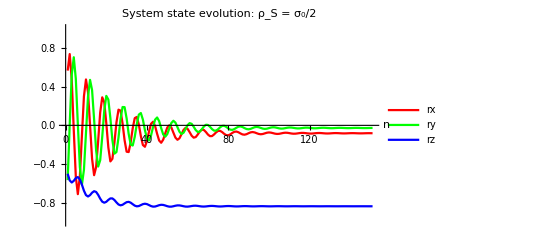

```mathematica
ListPlot[{rxArray,ryArray,rzArray},
Joined->True,
PlotStyle->{Red,Green,Blue},
PlotRange->{-1,1},
AxesLabel->{"n",None},
PlotLegends->{"rx","ry","rz"},
PlotLabel->"System state evolution: ρ_S = σ_0/2"]
```

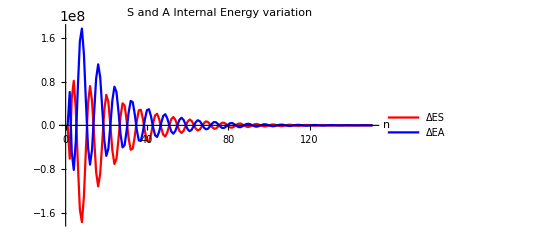

```mathematica
ListPlot[{ΔESArray,ΔEAArray},
Joined->True,
PlotStyle->{Red,Blue},
PlotRange->All,
AxesLabel->{"n",None},
PlotLegends->{"ΔES","ΔEA"},
PlotLabel->"S and A Internal Energy variation"]
```

LineLegend[{Q_S,Q_A},LabelStyle→{FontFamily→Times,FontSize→14}]

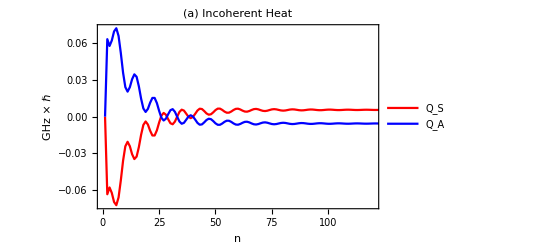

Qinc_VS_n.pdf

Qinc_VS_n.png

Qinc_VS_n.eps

```mathematica
legenda=LineLegend[{"Q_S","Q_A"},LabelStyle->{FontFamily->"Times",FontSize->14}]

plotQinc=ListPlot[{QSArray/1000000000,QAArray/1000000000},
Joined->True,
PlotStyle->{Red,Blue},
PlotRange->{{0,120},All},
PlotLegends->Placed[legenda,{0.8,0.75}],
Frame->True,
FrameLabel->{"n","GHz × ℏ"},
PlotLabel->"(a) Incoherent Heat",
BaseStyle->{FontFamily->"Times",FontSize->14}]

Export["Qinc_VS_n.pdf",plotQinc]
Export["Qinc_VS_n.png",plotQinc,ImageResolution->200]
Export["Qinc_VS_n.eps",plotQinc]
```

LineLegend[{W_S,W_A},LabelStyle→{FontFamily→Times,FontSize→14}]

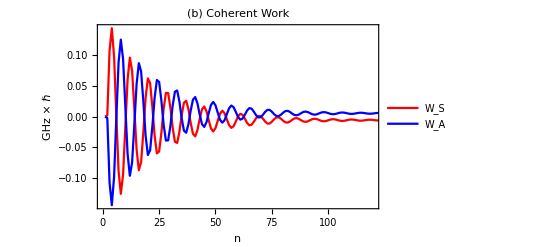

Wcoh_VS_n.pdf

Wcoh_VS_n.png

Wcoh_VS_n.eps

```mathematica
legenda=LineLegend[{"W_S","W_A"},LabelStyle->{FontFamily->"Times",FontSize->14}]

plotWc=ListPlot[{WcSArray/1000000000,WcAArray/1000000000},
Joined->True,
PlotStyle->{Red,Blue},
PlotRange->{{0,120},All},
Frame->True,
FrameLabel->{"n","GHz × ℏ"},
PlotLabel->"(b) Coherent Work",
PlotLegends->Placed[legenda,{0.8,0.75}],
BaseStyle->{FontFamily->"Times",FontSize->14}
]

Export["Wcoh_VS_n.pdf",plotWc]
Export["Wcoh_VS_n.png",plotWc,ImageResolution->200]
Export["Wcoh_VS_n.eps",plotWc]
```